# The refined local P2 computation

## Generalities

Maximum degree of the closed string expansion:

```mathematica
DMAX=4;
```

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

## The degree zero prepotential and the topological metric

The deformed chiral ring is generated by (1,p,p^2), with the relation (p+λ1)(p+λ2)(p+λ3)=0. That is:

```mathematica
Replp3=-Expand[(p+α[0])(p+α[1])(p+α[2])]+p^3
```

-p^2 α[0]-p^2 α[1]-p α[0] α[1]-p^2 α[2]-p α[0] α[2]-p α[1] α[2]-α[0] α[1] α[2]

The degree zero part of the prepotential. The "integrand" reads

```mathematica
exp=Expand[Expand[Expand[Expand[(t[1]+t[2] p+t[3] p^2)^3]/.p^6->p^3Replp3]/.p^5->p^2Replp3]/.p^4->p Replp3]/.p^3->Replp3//Simplify;
```

and the integral yields

```mathematica
PrepCl=(Series[((exp /(α[2]-α[1])/(α[0]-α[1])/(-3 p)/.p->-α[1])+(exp/(α[1]-α[2])/(α[0]-α[2])/(-3 p)/.p->-α[2])+(exp/(α[1]-α[0])/(α[2]-α[0])/(-3 p)/.p->-α[0]))/6 ,{t[1],0,3},{t[2],0,3},{t[3],0,3}]//Normal//Simplify)/ϵ[1]/ϵ[2];
```

The topological metric.

```mathematica
Clear[η];eta[i_,j_]:=D[D[D[PrepCl,t[1]],t[i]],t[j]]//Simplify
```

```mathematica
η=Array[eta,{3,3}];
```

```mathematica
η//MatrixForm
```

(1/(3 α[0] α[1] α[2] ϵ[1] ϵ[2]) | 0 | 0
0 | 0 | -1/(3 ϵ[1] ϵ[2])
0 | -1/(3 ϵ[1] ϵ[2]) | (α[0]+α[1]+α[2])/(3 ϵ[1] ϵ[2]))

Rewriting in terms of symmetric polynomials in the weight.

```mathematica
η=-({{-1/(3 ee[3] ϵ[1] ϵ[2]), 0, 0}, {0, 0, 1/(3 ϵ[1] ϵ[2])}, {0, 1/(3 ϵ[1] ϵ[2]), (-ee[1])/(3 ϵ[1] ϵ[2])}})
```

{{1/(3 ee[3] ϵ[1] ϵ[2]),0,0},{0,0,-1/(3 ϵ[1] ϵ[2])},{0,-1/(3 ϵ[1] ϵ[2]),ee[1]/(3 ϵ[1] ϵ[2])}}

Replacement rule for symmetric polynomials in the weight.

```mathematica
eα[i_]:=SymmetricPolynomial[i,Table[α[j],{j,0,2}]]
```

The inverse tt-metric.

```mathematica
ηm1=Inverse[η] //Simplify;
```

```mathematica
ηm1 //MatrixForm
```

(3 ee[3] ϵ[1] ϵ[2] | 0 | 0
0 | -3 ee[1] ϵ[1] ϵ[2] | -3 ϵ[1] ϵ[2]
0 | -3 ϵ[1] ϵ[2] | 0)

Non-trivial classical Yukawas which we will need later.

```mathematica
C224=D[D[PrepCl,t[3]],{t[2],2}]//Simplify
```

(α[0]+α[1]+α[2])/(3 ϵ[1] ϵ[2])

```mathematica
C222cl=D[PrepCl,{t[2],3}]//Simplify
```

-1/(3 ϵ[1] ϵ[2])

## Classical canonical coordinates

We have:

```mathematica
ReplPToCan=Table[p^n->(-α[0])^n δ[0]+(-α[2])^n δ[2]+(-α[1])^n δ[1],{n,1,2}]//Simplify; ;ReplCanToP=Solve[{1,p,p^2}=={δ[1]+δ[2]+δ[0],p/.ReplPToCan, p^2/.ReplPToCan},Table[δ[i],{i,0,2}]]//Simplify//Flatten;
```

```mathematica
ReplCanToP
```

{δ[0]→((p+α[1]) (p+α[2]))/((α[0]-α[1]) (α[0]-α[2])),δ[1]→-((p+α[0]) (p+α[2]))/((α[0]-α[1]) (α[1]-α[2])),δ[2]→-((p+α[0]) (p+α[1]))/((α[0]-α[2]) (-α[1]+α[2]))}

```mathematica
Sum[δ[i],{i,0,2}]/.ReplCanToP//Simplify
```

1

Square lengths of idempotents:

```mathematica
cnorm=Table[(η.CoefficientList[δ[i]/.ReplCanToP,p]//Simplify)[[1]],{i,0,2}]/.ee->eα//FullSimplify
```

{1/(3 α[0] (α[0]-α[1]) (α[0]-α[2]) ϵ[1] ϵ[2]),-1/(3 (α[0]-α[1]) α[1] (α[1]-α[2]) ϵ[1] ϵ[2]),1/(3 (α[0]-α[2]) (α[1]-α[2]) α[2] ϵ[1] ϵ[2])}

## The large radius I function

```mathematica
ISummand[d_,z_]=z Product[1/Product[p+α[i]+m z,{m,1,d}],{i,0,2}]Product[-3p-m z,{m,0,3d-1}]y^(d)
```

(3 p y^d (-z)^(3 d) z^(-3 d) Pochhammer[1+(3 p)/z,-1+3 d])/(Pochhammer[(p+z+α[0])/z,d] Pochhammer[(p+z+α[1])/z,d] Pochhammer[(p+z+α[2])/z,d])

```mathematica
IFun[y_]= y^(p/z)(z+Sum[ISummand[d,z],{d,1,∞}])//FullSimplify
```

y^(p/z) (z-(3 p y z (3 p+z) (3 p+2 z) HypergeometricPFQ[{1,1+p/z,4/3+p/z,5/3+p/z},{2+p/z+α[0]/z,2+p/z+α[1]/z,2+p/z+α[2]/z},-27 y])/((p+z+α[0]) (p+z+α[1]) (p+z+α[2])))

```mathematica
PFp=Series[ Block[{coeff=CoefficientList[Series[(z DY+α[0])(z DY+α[1])(z DY+α[2]),{DY,0,3}],DY],coeff2=CoefficientList[Series[(3z DY )(3z DY +z)(3z DY+2 z ),{DY,0,3}],DY]},Sum[coeff[[n+1]] D[IFun[Exp[Y]],{Y,n}],{n,0,3}]+y Sum[coeff2[[n+1]] D[IFun[Exp[Y]],{Y,n}],{n,0,3}]]/.Y->Log[y],{y,0,4}]//Simplify
```

y^(p/z) (z (p+α[0]) (p+α[1]) (p+α[2])+O[y]^5)

```mathematica
PFloc=Sum[(PFp/.ReplPToCan/.δ[l_]->KroneckerDelta[l,j])δ[j],{j,0,2}]//Simplify
```

(y^(-α[0]/z)+y^(-α[1]/z)+y^(-α[2]/z)) O[y]^5

```mathematica
$Assumptions={z>0, d∈Integers, d>=0}
```

{z>0,d∈ℤ,d≥0}

```mathematica
II[k_,n_]:=Coefficient[Collect[SeriesCoefficient[Series[IFun[y],{z,∞,2}],n],p]/.p^3->Replp3,p,k]//Simplify
```

```mathematica
C1[y_]=y D[II[1,0],y]//FullSimplify
```

Hypergeometric2F1[1/3,2/3,1,-27 y]

```mathematica
CoefficientList[FullSimplify[SeriesCoefficient[FullSimplify[Series[ISummand[d,z],{z,∞,1}],z>0 && d>0 && d∈Integers],0]/.p->H/.λ[i_]->Subscript[α, i],z>0 && d>0 && d∈Integers]/.Gamma[x_]->(x-1)!,H]//Simplify
```

{0,(3 (-y)^d (-1+3 d)!)/(d!)^3}

```mathematica
CoefficientList[FullSimplify[SeriesCoefficient[FullSimplify[Series[ISummand[d,z],{z,∞,1}],z>0 && d>0 && d∈Integers],1]/.p->H/.λ[i_]->Subscript[α, i],z>0 && d>0 && d∈Integers]/.Gamma[x_]->(x-1)!,H]//Simplify
```

{0,-(3 (-y)^d (-1+3 d)! HarmonicNumber[d] (α[0]+α[1]+α[2]))/(d!)^3,(9 (-y)^d (-1+3 d)! (EulerGamma-HarmonicNumber[d]+PolyGamma[0,3 d]))/(d!)^3}

```mathematica
C2[y_]=y D[y D[II[2,1],y]/C1[y],y]; D2[y_]= y D[y D[II[1,1],y]/C1[y],y];
```

```mathematica
-2 y D[y D[II[1,1],y]/C1[y],y]/(α[0]+α[1]+α[2])+y D[y D[II[2,1],y]/C1[y],y]-1/(1 + 27 y)//Simplify;
```

```mathematica
Series[2 y D[y D[II[1,1],y]/C1[y],y]/(α[0]+α[1]+α[2]),{y,0,3}]//N//Rationalize//Simplify
```

12 y-396 y^2+11676 y^3+O[y]^4

```mathematica
L[y_]:=Power[1/(1 + 27 y),1/3]
```

```mathematica
Series[C2[y]-L[y]^3,{y,0,5}]//N//Rationalize//Simplify
```

12 y-396 y^2+11676 y^3-332172 y^4+9294372 y^5+O[y]^6

```mathematica
Series[D2[y]/(α[0]+α[1]+α[2]) 2,{y,0,5}]//N//Rationalize//Simplify
```

12 y-396 y^2+11676 y^3-332172 y^4+9294372 y^5+O[y]^6

```mathematica
%/%% //Simplify
```

1+O[y]^5

```mathematica
Series[II[2,1]-Log[y]^2/2-Log[y](II[1,0]-Log[y]),{y,0,5}]//N//Rationalize
```

-9 y+(423 y^2)/4-1486 y^3+(389415 y^4)/16-(21981393 y^5)/50+O[y]^6

```mathematica
Sum[(9 (-y)^d (-1+3 d)! (EulerGamma-HarmonicNumber[d]+PolyGamma[0,3 d]))/(d!)^3,{d,1,5}]
```

-9 y+(423 y^2)/4-1486 y^3+(389415 y^4)/16-(21981393 y^5)/50

```mathematica
invmm=Series[Exp[II[1,0]],{y,0,2DMAX}]/.y->Q//InverseSeries
```

Q+6 Q^2+9 Q^3+56 Q^4-300 Q^5+3942 Q^6-48412 Q^7+639264 Q^8+O[Q]^9

```mathematica
dFdt=Series[Normal[Rationalize[N[Series[II[1,1] η[[2,2]]+II[2,1] η[[2,3]]/.ee->eα/.α[ll_]->ϵ[1]/3+ϵ[2]/3,{y,0,2DMAX}],20]]]/.y->invmm,{Q,0,2DMAX}]
```

-Log[Q]^2/(6 (ϵ[1] ϵ[2]))+(3 Q)/(ϵ[1] ϵ[2])-(45 Q^2)/(4 (ϵ[1] ϵ[2]))+(244 Q^3)/(3 ϵ[1] ϵ[2])-(12333 Q^4)/(16 (ϵ[1] ϵ[2]))+(211878 Q^5)/(25 ϵ[1] ϵ[2])-(102365 Q^6)/(ϵ[1] ϵ[2])+(64639725 Q^7)/(49 ϵ[1] ϵ[2])+O[Q]^8

### Relations between L, D2 and C2

```mathematica
Series[y D[II[1,1]/(α[0]+α[1]+α[2])2-II[2,1],y]+Log[y] C1[y],{y,0,6}]//N//Rationalize//Simplify
```

27 y-(1053 y^2)/2+11178 y^3-(1001565 y^4)/4+(58053429 y^5)/10-(689155047 y^6)/5+O[y]^7

```mathematica
Series[-Log[L[y]^3] C1[y],{y,0,6}]//N//Rationalize//Simplify
```

27 y-(1053 y^2)/2+11178 y^3-(1001565 y^4)/4+(58053429 y^5)/10-(689155047 y^6)/5+O[y]^7

```mathematica
Table[Sum[-(-27 y)^(d-k)/(d-k) Pochhammer[1/3,k]Pochhammer[2/3,k]/k!^2 (-27 y )^k,{k,0,d-1}],{d,1,6}]
```

{27 y,-(1053 y^2)/2,11178 y^3,-(1001565 y^4)/4,(58053429 y^5)/10,-(689155047 y^6)/5}

```mathematica
Table[-((-y)^d (3 d)! ( 1/d+ 2 HarmonicNumber[d]+3 PolyGamma[0,3 d]-3 PolyGamma[0,1+d]))/(d!)^3,{d,1,6}]//Simplify
```

{27 y,-(1053 y^2)/2,11178 y^3,-(1001565 y^4)/4,(58053429 y^5)/10,-(689155047 y^6)/5}

## Canonical coordinates

```mathematica
C1[y_]=Hypergeometric2F1[1/3,2/3,1,-27 y] ; L[y_]=(1/(1+27 y))^(1/3);CC2[y_]=L[y]^3/C1[y]^2;DD2[y_]=ee[1]/2 (CC2[y]-L[y]^3)
```

1/2 ee[1] (-1/(1+27 y)+1/((1+27 y) Hypergeometric2F1[1/3,2/3,1,-27 y]^2))

The fundamental solution.

```mathematica
SH[0][z_]:=IFun[y]/z;SH[1][z_]:=y D[IFun[y],y]/C1[y];SH[2][z_]:=(z y D[y D[IFun[y],y]/C1[y],y]- DD2[y] y D[IFun[y],y]/C1[y])/CC2[y];
```

Leading order expansion.

```mathematica
sH[i_,a_][z_]:=KroneckerDelta[i,a]+ssH[i,a][y]/z;
```

```mathematica
ssH[i_,0][y]:= PC1[y] KroneckerDelta[i,1]; ssH[i_,1][y]:=PD2[y] KroneckerDelta[i,1]+PC2[y] KroneckerDelta[i,2];
```

```mathematica
Series[Series[Table[Sum[sH[i,a][z]Inverse[η][[a+1,b+1]]sH[j,b][w],{a,0,2},{b,0,2}]- Inverse[η][[i+1,j+1]],{i,0,2},{j,0,2}],{w,-z,0}]//Normal,{z,∞,1}]//Simplify
```

{{0,-(3 (ϵ[1] ϵ[2] (ee[3] PC1[y]+ssH[0,2][y])))/z+O[1/z]^2,O[1/z]^2},{(3 ϵ[1] ϵ[2] (ee[3] PC1[y]+ssH[0,2][y]))/z+O[1/z]^2,O[1/z]^2,(3 ϵ[1] ϵ[2] (ee[1] PC2[y]-PD2[y]+ssH[2,2][y]))/z+O[1/z]^2},{O[1/z]^2,-(3 (ϵ[1] ϵ[2] (ee[1] PC2[y]-PD2[y]+ssH[2,2][y])))/z+O[1/z]^2,O[1/z]^2}}

```mathematica
Solve[Normal[%]==0,{ssH[2,2][y],ssH[0,2][y]}]//Simplify
```

{{ssH[2,2][y]→-ee[1] PC2[y]+PD2[y],ssH[0,2][y]→-ee[3] PC1[y]}}

```mathematica
ssH[0,2][y_]:= -PC1[y]ee[3];ssH[2,2][y_]:=PD2[y]-PC2[y] ee[1]; %%//Simplify//Normal
```

{{0,0,0},{0,0,0},{0,0,0}}

Canonical coordinates. Here cch[i,j,k] stands for (c^i)_jk.

```mathematica
dudt[i_,0]=1; dudt[i_,1]= LL[i]/c1[y];
```

```mathematica
(dudt[i,1])(dudt[i,2]) -Sum[cch[l,1,2] dudt[i,l],{l,0,2}]/.Flatten[Table[cc[0,m,n]->η[[m+1,n+1]],{m,0,2},{n,0,2}]]/.cc[2,1,2]->cc[1,2,2]//Simplify
```

-cch[0,1,2]-cch[2,1,2] dudt[i,2]+((-cch[1,1,2]+dudt[i,2]) LL[i])/c1[y]

```mathematica
Solve[%==0,dudt[i,2]]//Simplify//Flatten
```

{dudt[i,2]→-(c1[y] cch[0,1,2]+cch[1,1,2] LL[i])/(c1[y] cch[2,1,2]-LL[i])}

```mathematica
dudt[i_,0]=1; dudt[i_,1]= LL[i]/c1[y]; dudt[i_,2]:=-(c1[y] cch[0,1,2]+cch[1,1,2] LL[i])/(c1[y] cch[2,1,2]-LL[i])
```

### Structure constants

Structure constants of the small quantum product with at least one identity or divisor insertion.

```mathematica
Do[cch[0,i,j]=Inverse[η][[1,1]] η[[i+1,j+1]]; cch[i,0,j]=KroneckerDelta[i,j],{i,0,2},{j,0,2}];cch[1,1,1]=dd2[y]/c1[y];cch[2,1,1]=cc2[y]/c1[y];cch[2,1,2]=-ee[1]cc2[y]/c1[y]+dd2[y]/c1[y]
```

dd2[y]/c1[y]-(cc2[y] ee[1])/c1[y]

Zagier-Zinger-type relations.

```mathematica
bigrepl={cc2[y]->ll[y]^3/c1[y]^2,dd2[y]->ee[1]/2(cc2[y]-ll[y]^3)}
```

{cc2[y]→ll[y]^3/c1[y]^2,dd2[y]→1/2 ee[1] (cc2[y]-ll[y]^3)}

WDVV relations.

```mathematica
wdvv=Sum[(cch[i,1,1]  cch[j,2,2]-cch[i,1,2]  cch[j,1,2]) η[[i+1,j+1]],{i,0,2},{j,0,2}]//.bigrepl//Simplify
```

-1/(12 c1[y]^6 ϵ[1] ϵ[2])(4 c1[y]^6 ee[3]-2 c1[y]^5 (-2 cch[1,1,2]+cch[2,2,2]) ee[1] ll[y]^3+2 c1[y]^3 (2 cch[1,2,2]+(2 cch[1,1,2]-cch[2,2,2]) ee[1]) ll[y]^3+ee[1]^3 ll[y]^6+2 c1[y]^2 ee[1]^3 ll[y]^6+c1[y]^4 ee[1]^3 ll[y]^6)

```mathematica
replwdvv=Solve[wdvv==0,cch[1,1,2]]//Simplify//Flatten
```

{cch[1,1,2]→-1/(4 c1[y]^3 (1+c1[y]^2) ee[1] ll[y]^3)(4 c1[y]^6 ee[3]-2 c1[y]^5 cch[2,2,2] ee[1] ll[y]^3+2 c1[y]^3 (2 cch[1,2,2]-cch[2,2,2] ee[1]) ll[y]^3+ee[1]^3 ll[y]^6+2 c1[y]^2 ee[1]^3 ll[y]^6+c1[y]^4 ee[1]^3 ll[y]^6)}

```mathematica
bigrepl=Join[bigrepl,replwdvv]
```

{cc2[y]→ll[y]^3/c1[y]^2,dd2[y]→1/2 ee[1] (cc2[y]-ll[y]^3),cch[1,1,2]→-1/(4 c1[y]^3 (1+c1[y]^2) ee[1] ll[y]^3)(4 c1[y]^6 ee[3]-2 c1[y]^5 cch[2,2,2] ee[1] ll[y]^3+2 c1[y]^3 (2 cch[1,2,2]-cch[2,2,2] ee[1]) ll[y]^3+ee[1]^3 ll[y]^6+2 c1[y]^2 ee[1]^3 ll[y]^6+c1[y]^4 ee[1]^3 ll[y]^6)}

Semi-semplicity relations. The first one (a=1, b=2) was already implemented.

```mathematica
(dudt[i,1])(dudt[i,2]) -Sum[cch[l,1,2] dudt[i,l],{l,0,2}]//Simplify
```

0

a=b=1.

```mathematica
(dudt[i,1])^2 -Sum[cch[l,1,1] dudt[i,l],{l,0,2}]//.bigrepl//Together//Simplify
```

(-2 c1[y]^3 cch[2,2,2] ee[1] ll[y]^3 LL[i]+2 c1[y] (2 cch[1,2,2]-cch[2,2,2] ee[1]) ll[y]^3 LL[i]+ee[1]^3 ll[y]^6 LL[i]+2 c1[y]^2 ee[1] (ee[1]^2 ll[y]^6 LL[i]+2 LL[i]^3+2 ll[y]^3 (ee[3]+ee[1] LL[i]^2))+c1[y]^4 (ee[1]^3 ll[y]^6 LL[i]+4 ee[1] ll[y]^3 (ee[3]+ee[1] LL[i]^2)+4 LL[i] (ee[3]+ee[1] LL[i]^2)))/(2 c1[y]^2 (1+c1[y]^2) ee[1] ((1+c1[y]^2) ee[1] ll[y]^3+2 c1[y]^2 LL[i]))

```mathematica
solc122=Solve[%==0,cch[1,2,2]]//Together//Flatten
```

{cch[1,2,2]→1/(4 c1[y] ll[y]^3 LL[i])(-4 c1[y]^2 ee[1] ee[3] ll[y]^3-4 c1[y]^4 ee[1] ee[3] ll[y]^3-4 c1[y]^4 ee[3] LL[i]+2 c1[y] cch[2,2,2] ee[1] ll[y]^3 LL[i]+2 c1[y]^3 cch[2,2,2] ee[1] ll[y]^3 LL[i]-ee[1]^3 ll[y]^6 LL[i]-2 c1[y]^2 ee[1]^3 ll[y]^6 LL[i]-c1[y]^4 ee[1]^3 ll[y]^6 LL[i]-4 c1[y]^2 ee[1]^2 ll[y]^3 LL[i]^2-4 c1[y]^4 ee[1]^2 ll[y]^3 LL[i]^2-4 c1[y]^2 ee[1] LL[i]^3-4 c1[y]^4 ee[1] LL[i]^3)}

The polynomial arising from the leading order solution to the Picard--Fuchs equations.

```mathematica
polPF=Sum[ee[j] XX[3-j],{j,1,3}]+1/ll[y]^3 XX[3]
```

ee[3] XX[0]+ee[2] XX[1]+ee[1] XX[2]+XX[3]/ll[y]^3

Solving for the cubic term.

```mathematica
replPF=Solve[polPF==0,XX[3]]//Flatten
```

{XX[3]→-ll[y]^3 (ee[3] XX[0]+ee[2] XX[1]+ee[1] XX[2])}

Using this to simplify cch[1,2,2] and get rid of the LL_i dependence. The numerator...

```mathematica
Block[{coeff=CoefficientList[Numerator[cch[1,2,2]/.solc122],LL[i]]//Simplify},Sum[coeff[[i]] XX[i-1],{i,1,4}]]/.replPF//Simplify
```

-((-2 c1[y] cch[2,2,2] ee[1] ll[y]^3-2 c1[y]^3 cch[2,2,2] ee[1] ll[y]^3+ee[1]^3 ll[y]^6+c1[y]^4 (4 ee[3]-4 ee[1] ee[2] ll[y]^3+ee[1]^3 ll[y]^6)+2 c1[y]^2 (-2 ee[1] ee[2] ll[y]^3+ee[1]^3 ll[y]^6)) XX[1])

...divided by the denominator. The final result only depends on cch[2,2,2], c1[y] and ll[y].

```mathematica
%/Denominator[cch[1,2,2]/.solc122]/.XX[k_]->LL[i]^k//Simplify
```

1/4 (2 cch[2,2,2] ee[1]+2 c1[y]^2 cch[2,2,2] ee[1]-(ee[1]^3 ll[y]^3)/c1[y]+c1[y] (4 ee[1] ee[2]-2 ee[1]^3 ll[y]^3)+c1[y]^3 (4 ee[1] ee[2]-(4 ee[3])/ll[y]^3-ee[1]^3 ll[y]^3))

```mathematica
solc122={cch[1,2,2]->%}
```

{cch[1,2,2]→1/4 (2 cch[2,2,2] ee[1]+2 c1[y]^2 cch[2,2,2] ee[1]-(ee[1]^3 ll[y]^3)/c1[y]+c1[y] (4 ee[1] ee[2]-2 ee[1]^3 ll[y]^3)+c1[y]^3 (4 ee[1] ee[2]-(4 ee[3])/ll[y]^3-ee[1]^3 ll[y]^3))}

Adding this to the list of solutions.

```mathematica
bigrepl=Join[bigrepl/.solc122//Simplify, solc122]
```

{cc2[y]→ll[y]^3/c1[y]^2,dd2[y]→1/2 ee[1] (cc2[y]-ll[y]^3),cch[1,1,2]→-(ee[1]^2 ll[y]^3)/(4 c1[y]^3)+c1[y] (-ee[2]+1/4 ee[1]^2 ll[y]^3),cch[1,2,2]→1/4 (2 cch[2,2,2] ee[1]+2 c1[y]^2 cch[2,2,2] ee[1]-(ee[1]^3 ll[y]^3)/c1[y]+c1[y] (4 ee[1] ee[2]-2 ee[1]^3 ll[y]^3)+c1[y]^3 (4 ee[1] ee[2]-(4 ee[3])/ll[y]^3-ee[1]^3 ll[y]^3))}

a = b = 2. We have only cch[2,2,2] left to solve for.

```mathematica
(dudt[i,2])^2 -Sum[cch[l,2,2] dudt[i,l],{l,0,2}]//.bigrepl//Together
```

(16 c1[y]^8 ee[3]^2 ll[y]^3+8 c1[y]^5 cch[2,2,2] ee[1] ee[3] ll[y]^6+8 c1[y]^7 cch[2,2,2] ee[1] ee[3] ll[y]^6-4 c1[y]^2 ee[1]^3 ee[3] ll[y]^9-8 c1[y]^4 ee[1]^3 ee[3] ll[y]^9-4 c1[y]^6 ee[1]^3 ee[3] ll[y]^9+16 c1[y]^7 cch[2,2,2] ee[3] ll[y]^3 LL[i]+32 c1[y]^8 ee[2] ee[3] ll[y]^3 LL[i]+8 c1[y]^5 cch[2,2,2] ee[1] ee[2] ll[y]^6 LL[i]+8 c1[y]^7 cch[2,2,2] ee[1] ee[2] ll[y]^6 LL[i]-4 c1[y]^4 ee[1]^2 ee[3] ll[y]^6 LL[i]-8 c1[y]^6 ee[1]^2 ee[3] ll[y]^6 LL[i]-4 c1[y]^8 ee[1]^2 ee[3] ll[y]^6 LL[i]-4 c1[y]^3 cch[2,2,2] ee[1]^3 ll[y]^9 LL[i]-8 c1[y]^5 cch[2,2,2] ee[1]^3 ll[y]^9 LL[i]-4 c1[y]^7 cch[2,2,2] ee[1]^3 ll[y]^9 LL[i]-4 c1[y]^2 ee[1]^3 ee[2] ll[y]^9 LL[i]-12 c1[y]^4 ee[1]^3 ee[2] ll[y]^9 LL[i]-12 c1[y]^6 ee[1]^3 ee[2] ll[y]^9 LL[i]-4 c1[y]^8 ee[1]^3 ee[2] ll[y]^9 LL[i]+ee[1]^5 ll[y]^12 LL[i]+4 c1[y]^2 ee[1]^5 ll[y]^12 LL[i]+6 c1[y]^4 ee[1]^5 ll[y]^12 LL[i]+4 c1[y]^6 ee[1]^5 ll[y]^12 LL[i]+c1[y]^8 ee[1]^5 ll[y]^12 LL[i]+16 c1[y]^7 cch[2,2,2] ee[2] ll[y]^3 LL[i]^2+16 c1[y]^8 ee[2]^2 ll[y]^3 LL[i]^2+16 c1[y]^8 ee[1] ee[3] ll[y]^3 LL[i]^2-4 c1[y]^3 cch[2,2,2] ee[1]^2 ll[y]^6 LL[i]^2-16 c1[y]^5 cch[2,2,2] ee[1]^2 ll[y]^6 LL[i]^2-12 c1[y]^7 cch[2,2,2] ee[1]^2 ll[y]^6 LL[i]^2-8 c1[y]^4 ee[1]^2 ee[2] ll[y]^6 LL[i]^2-32 c1[y]^6 ee[1]^2 ee[2] ll[y]^6 LL[i]^2-24 c1[y]^8 ee[1]^2 ee[2] ll[y]^6 LL[i]^2+ee[1]^4 ll[y]^9 LL[i]^2+4 c1[y]^2 ee[1]^4 ll[y]^9 LL[i]^2+10 c1[y]^4 ee[1]^4 ll[y]^9 LL[i]^2+12 c1[y]^6 ee[1]^4 ll[y]^9 LL[i]^2+5 c1[y]^8 ee[1]^4 ll[y]^9 LL[i]^2+16 c1[y]^8 ee[3] LL[i]^3-8 c1[y]^5 cch[2,2,2] ee[1] ll[y]^3 LL[i]^3-8 c1[y]^7 cch[2,2,2] ee[1] ll[y]^3 LL[i]^3-16 c1[y]^6 ee[1] ee[2] ll[y]^3 LL[i]^3-16 c1[y]^8 ee[1] ee[2] ll[y]^3 LL[i]^3+4 c1[y]^4 ee[1]^3 ll[y]^6 LL[i]^3+8 c1[y]^6 ee[1]^3 ll[y]^6 LL[i]^3+4 c1[y]^8 ee[1]^3 ll[y]^6 LL[i]^3)/(4 c1[y]^2 ll[y]^3 (ee[1] ll[y]^3+c1[y]^2 ee[1] ll[y]^3+2 c1[y]^2 LL[i])^2)

```mathematica
solc222=Solve[%==0,cch[2,2,2]]//Together//Flatten
```

{cch[2,2,2]→(16 c1[y]^8 ee[3]^2 ll[y]^3-4 c1[y]^2 ee[1]^3 ee[3] ll[y]^9-8 c1[y]^4 ee[1]^3 ee[3] ll[y]^9-4 c1[y]^6 ee[1]^3 ee[3] ll[y]^9+32 c1[y]^8 ee[2] ee[3] ll[y]^3 LL[i]-4 c1[y]^4 ee[1]^2 ee[3] ll[y]^6 LL[i]-8 c1[y]^6 ee[1]^2 ee[3] ll[y]^6 LL[i]-4 c1[y]^8 ee[1]^2 ee[3] ll[y]^6 LL[i]-4 c1[y]^2 ee[1]^3 ee[2] ll[y]^9 LL[i]-12 c1[y]^4 ee[1]^3 ee[2] ll[y]^9 LL[i]-12 c1[y]^6 ee[1]^3 ee[2] ll[y]^9 LL[i]-4 c1[y]^8 ee[1]^3 ee[2] ll[y]^9 LL[i]+ee[1]^5 ll[y]^12 LL[i]+4 c1[y]^2 ee[1]^5 ll[y]^12 LL[i]+6 c1[y]^4 ee[1]^5 ll[y]^12 LL[i]+4 c1[y]^6 ee[1]^5 ll[y]^12 LL[i]+c1[y]^8 ee[1]^5 ll[y]^12 LL[i]+16 c1[y]^8 ee[2]^2 ll[y]^3 LL[i]^2+16 c1[y]^8 ee[1] ee[3] ll[y]^3 LL[i]^2-8 c1[y]^4 ee[1]^2 ee[2] ll[y]^6 LL[i]^2-32 c1[y]^6 ee[1]^2 ee[2] ll[y]^6 LL[i]^2-24 c1[y]^8 ee[1]^2 ee[2] ll[y]^6 LL[i]^2+ee[1]^4 ll[y]^9 LL[i]^2+4 c1[y]^2 ee[1]^4 ll[y]^9 LL[i]^2+10 c1[y]^4 ee[1]^4 ll[y]^9 LL[i]^2+12 c1[y]^6 ee[1]^4 ll[y]^9 LL[i]^2+5 c1[y]^8 ee[1]^4 ll[y]^9 LL[i]^2+16 c1[y]^8 ee[3] LL[i]^3-16 c1[y]^6 ee[1] ee[2] ll[y]^3 LL[i]^3-16 c1[y]^8 ee[1] ee[2] ll[y]^3 LL[i]^3+4 c1[y]^4 ee[1]^3 ll[y]^6 LL[i]^3+8 c1[y]^6 ee[1]^3 ll[y]^6 LL[i]^3+4 c1[y]^8 ee[1]^3 ll[y]^6 LL[i]^3)/(4 c1[y]^3 ll[y]^3 (ee[1] ll[y]^3+c1[y]^2 ee[1] ll[y]^3+2 c1[y]^2 LL[i]) (-2 c1[y]^2 ee[3]-2 c1[y]^2 ee[2] LL[i]+ee[1]^2 ll[y]^3 LL[i]+c1[y]^2 ee[1]^2 ll[y]^3 LL[i]+ee[1] LL[i]^2+c1[y]^2 ee[1] LL[i]^2))}

Once again, we want to get rid of the LL[i] dependence. We have a rational dependence on LL[i] with degrees at numerator and denominator equal to 3.

```mathematica
Exponent[Numerator[cch[2,2,2]/.solc222],LL[i]]
```

3

```mathematica
Exponent[Denominator[cch[2,2,2]/.solc222],LL[i]]
```

3

Replacing the cubic term, numerator and denominator respectively:

```mathematica
Block[{coeff=CoefficientList[Numerator[cch[2,2,2]/.solc222],LL[i]]//Simplify},Sum[coeff[[i]] XX[i-1],{i,1,4}]]/.replPF//Simplify
```

-ll[y]^3 (ee[1]^2 ll[y]^3+2 c1[y]^2 ee[1]^2 ll[y]^3+c1[y]^4 (-4 ee[2]+ee[1]^2 ll[y]^3)) (-ee[1]^2 ll[y]^3 (ee[1] ll[y]^3 XX[1]+XX[2])-2 c1[y]^2 ee[1] ll[y]^3 (-2 ee[3] XX[0]-2 ee[2] XX[1]+ee[1]^2 ll[y]^3 XX[1]+ee[1] XX[2])+c1[y]^4 (-ee[1]^3 ll[y]^6 XX[1]+ee[1] ll[y]^3 (4 ee[3] XX[0]+4 ee[2] XX[1]-ee[1] XX[2])+4 (ee[3] XX[1]+ee[2] XX[2])))

```mathematica
Block[{coeff=CoefficientList[Denominator[cch[2,2,2]/.solc222],LL[i]]//Simplify},Sum[coeff[[i]] XX[i-1],{i,1,4}]]/.replPF//Simplify
```

4 (c1[y]^3 ee[1]^2 ll[y]^6 (ee[1] ll[y]^3 XX[1]+XX[2])+2 c1[y]^5 ee[1] ll[y]^6 (-2 ee[3] XX[0]-2 ee[2] XX[1]+ee[1]^2 ll[y]^3 XX[1]+ee[1] XX[2])+c1[y]^7 (ee[1]^3 ll[y]^9 XX[1]+ee[1] ll[y]^6 (-4 ee[3] XX[0]-4 ee[2] XX[1]+ee[1] XX[2])-4 ll[y]^3 (ee[3] XX[1]+ee[2] XX[2])))

And all LL[i] dependence magically disappears:

```mathematica
solc222={cch[2,2,2]->%%/%/.XX[k_]->LL[i]^k//Simplify}
```

{cch[2,2,2]→(ee[1]^2 ll[y]^3+2 c1[y]^2 ee[1]^2 ll[y]^3+c1[y]^4 (-4 ee[2]+ee[1]^2 ll[y]^3))/(4 c1[y]^3)}

```mathematica
bigrepl=Join[bigrepl/.solc222//Simplify, solc222]
```

{cc2[y]→ll[y]^3/c1[y]^2,dd2[y]→1/2 ee[1] (cc2[y]-ll[y]^3),cch[1,1,2]→-(ee[1]^2 ll[y]^3)/(4 c1[y]^3)+c1[y] (-ee[2]+1/4 ee[1]^2 ll[y]^3),cch[1,2,2]→(ee[1]^3 ll[y]^6+c1[y]^2 ee[1]^3 ll[y]^6+c1[y]^4 (4 ee[1] ee[2] ll[y]^3-ee[1]^3 ll[y]^6)-c1[y]^6 (8 ee[3]-4 ee[1] ee[2] ll[y]^3+ee[1]^3 ll[y]^6))/(8 c1[y]^3 ll[y]^3),cch[2,2,2]→(ee[1]^2 ll[y]^3+2 c1[y]^2 ee[1]^2 ll[y]^3+c1[y]^4 (-4 ee[2]+ee[1]^2 ll[y]^3))/(4 c1[y]^3)}

#### Various checks

```mathematica
SeriesCoefficient[Series[(z y D[y D[IFun[y],y]/C1[y],y]-  DD2[y] y D[IFun[y],y]/C1[y])/CC2[y],{z,∞,1}],1];
```

```mathematica
tab=CoefficientList[Collect[%,p]/.p^3->Replp3,p];
```

```mathematica
Series[y D[tab[[1]],y]/C1[y],{y,0,2}]//Expand//N//Rationalize
```

-α[0] α[1] α[2]+O[y]^3

```mathematica
Series[tab[[2]],{y,0,2}]//N//Rationalize
```

(-Log[y] α[0] α[1]-Log[y] α[0] α[2]-Log[y] α[1] α[2])-6 (α[0]^2+α[1]^2+α[2]^2) y-9 (4 ee[1] α[0]-17 α[0]^2+4 ee[1] α[1]-22 α[0] α[1]-17 α[1]^2+4 ee[1] α[2]-22 α[0] α[2]-22 α[1] α[2]-17 α[2]^2) y^2+O[y]^3

```mathematica
Series[tab[[3]],{y,0,2}]//N//Rationalize
```

(-Log[y] α[0]-Log[y] α[1]-Log[y] α[2])-3 (2 ee[1] Log[y]-7 α[0]-2 Log[y] α[0]-7 α[1]-2 Log[y] α[1]-7 α[2]-2 Log[y] α[2]) y+9/2 (20 ee[1]+24 ee[1] Log[y]-79 α[0]-24 Log[y] α[0]-79 α[1]-24 Log[y] α[1]-79 α[2]-24 Log[y] α[2]) y^2+O[y]^3

```mathematica
firstsum=N[Series[II[2,2],{y,0,7}],20]//Rationalize;
```

```mathematica
y D[ y D[firstsum,y]/C1[y],y]-DD2[y] y D[Series[II[2,1],{y,0,7}]//N//Rationalize,y]/C1[y]/.ee->eα//Rationalize//Simplify
```

-Log[y] (α[0]+α[1]+α[2])+3 (7+5 Log[y]) (α[0]+α[1]+α[2]) y-9/2 ((129+74 Log[y]) (α[0]+α[1]+α[2])) y^2+1/2 (31181+16014 Log[y]) (α[0]+α[1]+α[2]) y^3-3/4 ((556163+265692 Log[y]) (α[0]+α[1]+α[2])) y^4+9/20 (24794951+11232300 Log[y]) (α[0]+α[1]+α[2]) y^5-9/4 ((132721355+57672436 Log[y]) (α[0]+α[1]+α[2])) y^6+3.35902×10^9 (2.38096 α[0]+1. Log[y] α[0]+2.38096 α[1]+1. Log[y] α[1]+2.38096 α[2]+1. Log[y] α[2]) y^7+O[y]^8

```mathematica
%/CC2[y]//Simplify
```

-Log[y] (α[0]+α[1]+α[2])+21 (α[0]+α[1]+α[2]) y-531/2 (α[0]+α[1]+α[2]) y^2+4615 (α[0]+α[1]+α[2]) y^3-365355/4 (α[0]+α[1]+α[2]) y^4+9701721/5 (α[0]+α[1]+α[2]) y^5-86197245/2 (α[0]+α[1]+α[2]) y^6+(9.87098×10^8 α[0]+9.87098×10^8 α[1]+9.87098×10^8 α[2]) y^7+O[y]^8

```mathematica
y D[%,y]/C1[y]
```

(-α[0]-α[1]-α[2])+(6 (-α[0]-α[1]-α[2])+21 (α[0]+α[1]+α[2])) y+(-54 (-α[0]-α[1]-α[2])-405 (α[0]+α[1]+α[2])) y^2+(816 (-α[0]-α[1]-α[2])+9525 (α[0]+α[1]+α[2])) y^3+(-14814 (-α[0]-α[1]-α[2])-236475 (α[0]+α[1]+α[2])) y^4+(295812 (-α[0]-α[1]-α[2])+6017571 (α[0]+α[1]+α[2])) y^5+(-6262488 (-α[0]-α[1]-α[2])-155276433 (α[0]+α[1]+α[2])) y^6+(137929392 (-α[0]-α[1]-α[2])-2867261274 (α[0]+α[1]+α[2])+7 (9.87098×10^8 α[0]+9.87098×10^8 α[1]+9.87098×10^8 α[2])) y^7+O[y]^8

```mathematica
%/eα[1]//Simplify
```

-1+15 y-351 y^2+8709 y^3-221661 y^4+5721759 y^5-149013945 y^6+3.90449×10^9 y^7+O[y]^8

```mathematica
Series[cch[1,1,2]/.bigrepl/.c1->C1/.ll[y]->Power[1/(1+27 y),1/3],{y,0,3}]/.ee->eα//Simplify
```

(-α[1] α[2]-α[0] (α[1]+α[2]))-6 (α[0]^2+α[1]^2+α[1] α[2]+α[2]^2+α[0] (α[1]+α[2])) y+(198 (α[0]+α[1]+α[2])^2-90 (α[1] α[2]+α[0] (α[1]+α[2]))) y^2+(-5946 (α[0]+α[1]+α[2])^2+1680 (α[1] α[2]+α[0] (α[1]+α[2]))) y^3+O[y]^4

```mathematica
(-Log[y] α[0] α[1]-Log[y] α[0] α[2]-Log[y] α[1] α[2])-6 (α[0]^2+α[1]^2+α[2]^2) y+9 (13 α[0]^2+14 α[0] α[1]+13 α[1]^2+14 α[0] α[2]+14 α[1] α[2]+13 α[2]^2) y^2+O[y]^3
```

(-Log[y] α[0] α[1]-Log[y] α[0] α[2]-Log[y] α[1] α[2])-6 (α[0]^2+α[1]^2+α[2]^2) y+9 (13 α[0]^2+14 α[0] α[1]+13 α[1]^2+14 α[0] α[2]+14 α[1] α[2]+13 α[2]^2) y^2+O[y]^3

```mathematica
y D[%,y]/C1[y]
```

(-α[0] α[1]-α[0] α[2]-α[1] α[2])+(6 (-α[0] α[1]-α[0] α[2]-α[1] α[2])-6 (α[0]^2+α[1]^2+α[2]^2)) y+(-54 (-α[0] α[1]-α[0] α[2]-α[1] α[2])-36 (α[0]^2+α[1]^2+α[2]^2)+18 (13 α[0]^2+14 α[0] α[1]+13 α[1]^2+14 α[0] α[2]+14 α[1] α[2]+13 α[2]^2)) y^2+O[y]^3

```mathematica
%-%%%
```

O[y]^3

```mathematica
y D[Series[tab[[1]],{y,0,3}]//N//Rationalize,y]/C1[y]//Chop
```

-α[0] α[1] α[2]+O[y]^4

```mathematica
cch[0,1,2]/.bigrepl/.ee->eα
```

-α[0] α[1] α[2]

```mathematica
%-%%
```

O[y]^4

```mathematica
Series[y D[N[Series[tab[[2]],{y,0,3}],10]//Normal//Expand//Rationalize,y],{y,0,3}]/C1[y]/.ee->eα//Simplify
```

(-α[1] α[2]-α[0] (α[1]+α[2]))-6 (α[0]^2+α[1]^2+α[1] α[2]+α[2]^2+α[0] (α[1]+α[2])) y+18 (11 α[0]^2+11 α[1]^2+17 α[1] α[2]+11 α[2]^2+17 α[0] (α[1]+α[2])) y^2-6 (991 α[0]^2+991 α[1]^2+1702 α[1] α[2]+991 α[2]^2+1702 α[0] (α[1]+α[2])) y^3+O[y]^4

```mathematica
Series[cch[1,1,2]/.bigrepl/.c1->C1/.ll[y]->Power[1/(1+27 y),1/3],{y,0,3}]/.ee->eα//Simplify
```

(-α[1] α[2]-α[0] (α[1]+α[2]))-6 (α[0]^2+α[1]^2+α[1] α[2]+α[2]^2+α[0] (α[1]+α[2])) y+(198 (α[0]+α[1]+α[2])^2-90 (α[1] α[2]+α[0] (α[1]+α[2]))) y^2+(-5946 (α[0]+α[1]+α[2])^2+1680 (α[1] α[2]+α[0] (α[1]+α[2]))) y^3+O[y]^4

```mathematica
%-%%
```

O[y]^4

```mathematica
Series[y D[N[Series[tab[[3]],{y,0,3}],10]//Normal//Expand//Rationalize,y],{y,0,3}]/C1[y]/.ee->eα//Simplify
```

(-α[0]-α[1]-α[2])+15 (α[0]+α[1]+α[2]) y-351 (α[0]+α[1]+α[2]) y^2+8709 (α[0]+α[1]+α[2]) y^3+O[y]^4

```mathematica
Series[cch[2,1,2]/.bigrepl/.c1->C1/.cc2->C2/.ll[y]->Power[1/(1+27 y),1/3],{y,0,3}]/.ee->eα//N//Rationalize//Simplify
```

(-α[0]-α[1]-α[2])+15 (α[0]+α[1]+α[2]) y-351 (α[0]+α[1]+α[2]) y^2+8709 (α[0]+α[1]+α[2]) y^3+O[y]^4

```mathematica
%-%%
```

O[y]^4

### The Ψ matrix

```mathematica
replpolPF=Table[Solve[polPF==0,XX[3]]/.XX[l_]->LL[i]^l,{i,0,2}]//Flatten
```

{LL[0]^3→-ll[y]^3 (ee[3]+ee[2] LL[0]+ee[1] LL[0]^2),LL[1]^3→-ll[y]^3 (ee[3]+ee[2] LL[1]+ee[1] LL[1]^2),LL[2]^3→-ll[y]^3 (ee[3]+ee[2] LL[2]+ee[1] LL[2]^2)}

Some massaging. Note that:

```mathematica
dudt[i,2]//.bigrepl//Simplify
```

(-ee[1]^2 ll[y]^3 LL[i]+c1[y]^4 (-4 ee[3]+(-4 ee[2]+ee[1]^2 ll[y]^3) LL[i]))/(2 c1[y] (1+c1[y]^2) ee[1] ll[y]^3+4 c1[y]^3 LL[i])

Is the same as

```mathematica
(LL[i]-dd2[y])LL[i]/c1[y]/cc2[y]//.bigrepl//Simplify
```

(LL[i] (-ee[1]+c1[y]^2 (ee[1]+(2 LL[i])/ll[y]^3)))/(2 c1[y])

Check

```mathematica
%-%%//Simplify
```

(2 c1[y]^3 (LL[i]^3+ll[y]^3 (ee[3]+ee[2] LL[i]+ee[1] LL[i]^2)))/((1+c1[y]^2) ee[1] ll[y]^6+2 c1[y]^2 ll[y]^3 LL[i])

```mathematica
%/.replpolPF
```

(2 c1[y]^3 (LL[i]^3+ll[y]^3 (ee[3]+ee[2] LL[i]+ee[1] LL[i]^2)))/((1+c1[y]^2) ee[1] ll[y]^6+2 c1[y]^2 ll[y]^3 LL[i])

So:

```mathematica
dudt[i_,2]=(LL[i]-dd2[y])LL[i]/c1[y]/cc2[y];
```

Elementary symmetric polynomials in the roots of the Picard--Fuchs polynomial.

```mathematica
eLL[i_]:=eα[i]/.α->LL
```

The roots themselves:

```mathematica
replLL=Solve[Sum[ee[i]XX^(3-i)/.LL->α,{i,1,3}]+XX^3/ll[y]^3==0,XX];
```

The Φ matrix:

```mathematica
Φ=Array[dudt,{3,3},{0,0}]/.bigrepl//Simplify
```

{{1,LL[0]/c1[y],(c1[y] LL[0] (-1/2 ee[1] (cc2[y]-ll[y]^3)+LL[0]))/ll[y]^3},{1,LL[1]/c1[y],(c1[y] LL[1] (-1/2 ee[1] (cc2[y]-ll[y]^3)+LL[1]))/ll[y]^3},{1,LL[2]/c1[y],(c1[y] LL[2] (-1/2 ee[1] (cc2[y]-ll[y]^3)+LL[2]))/ll[y]^3}}

Its inverse.

```mathematica
Φinv=Inverse[Φ]//Simplify
```

{{(LL[1] LL[2])/((LL[0]-LL[1]) (LL[0]-LL[2])),-(LL[0] LL[2])/((LL[0]-LL[1]) (LL[1]-LL[2])),(LL[0] LL[1])/((LL[0]-LL[2]) (LL[1]-LL[2]))},{(c1[y] (cc2[y] ee[1]-ee[1] ll[y]^3-2 (LL[1]+LL[2])))/(2 (LL[0]-LL[1]) (LL[0]-LL[2])),(c1[y] (-cc2[y] ee[1]+ee[1] ll[y]^3+2 (LL[0]+LL[2])))/(2 (LL[0]-LL[1]) (LL[1]-LL[2])),(c1[y] (-cc2[y] ee[1]+ee[1] ll[y]^3+2 (LL[0]+LL[1])))/(2 (LL[0]-LL[2]) (-LL[1]+LL[2]))},{ll[y]^3/(c1[y] (LL[0]-LL[1]) (LL[0]-LL[2])),-ll[y]^3/(c1[y] (LL[0]-LL[1]) (LL[1]-LL[2])),ll[y]^3/(c1[y] (LL[0]-LL[2]) (LL[1]-LL[2]))}}

More massaging. I claim that the i^th diagonal component of

```mathematica
FF2=-1/ll[y]^3Table[LL[i]Product[If[i==j,1,LL[i]-LL[Mod[j,3]]],{j,0,2}],{i,0,2}] IdentityMatrix[3]
```

{{-(LL[0] (LL[0]-LL[1]) (LL[0]-LL[2]))/ll[y]^3,0,0},{0,-(LL[1] (-LL[0]+LL[1]) (LL[1]-LL[2]))/ll[y]^3,0},{0,0,-(LL[2] (-LL[0]+LL[2]) (-LL[1]+LL[2]))/ll[y]^3}}

is the same as the following quadratic polynomial evaluated at x=LL[i-1]

```mathematica
ff2[x_]=x^2 ee[1]+2 x ee[2]+3 ee[3]
```

x^2 ee[1]+2 x ee[2]+3 ee[3]

Check

```mathematica
Expand[FF2[[1,1]]- ff2[LL[0]]]/.(replpolPF/.i->0)//Simplify
```

-2 ee[3]-ee[2] LL[0]+(LL[0] (-LL[1] LL[2]+LL[0] (LL[1]+LL[2])))/ll[y]^3

```mathematica
Expand[%]/.LL[0] LL[1] LL[2]->- ee[3] ll[y]^3//Simplify
```

-ee[3]-ee[2] LL[0]+(LL[0]^2 (LL[1]+LL[2]))/ll[y]^3

```mathematica
%/.LL[1]->-LL[2]-LL[0]-ee[1] ll[y]^3
```

-ee[3]-ee[2] LL[0]+((-ee[1] ll[y]^3-LL[0]) LL[0]^2)/ll[y]^3

```mathematica
Expand[%]/.(replpolPF/.i->0)//Simplify
```

0

```mathematica
Φinv.FF2//.bigrepl//Simplify
```

{{ee[3],ee[3],ee[3]},{-((1+c1[y]^2) ee[1] LL[0])/(2 c1[y])-(c1[y] LL[0]^2)/ll[y]^3,-((1+c1[y]^2) ee[1] LL[1])/(2 c1[y])-(c1[y] LL[1]^2)/ll[y]^3,-((1+c1[y]^2) ee[1] LL[2])/(2 c1[y])-(c1[y] LL[2]^2)/ll[y]^3},{-LL[0]/c1[y],-LL[1]/c1[y],-LL[2]/c1[y]}}

```mathematica
Φinv={{ee[3],ee[3],ee[3]},{-((1+c1[y]^2) ee[1] LL[0])/(2 c1[y])-(c1[y] LL[0]^2)/ll[y]^3,-((1+c1[y]^2) ee[1] LL[1])/(2 c1[y])-(c1[y] LL[1]^2)/ll[y]^3,-((1+c1[y]^2) ee[1] LL[2])/(2 c1[y])-(c1[y] LL[2]^2)/ll[y]^3},{-LL[0]/c1[y],-LL[1]/c1[y],-LL[2]/c1[y]}}.Inverse[FF2]//Simplify
```

{{-(ee[3] ll[y]^3)/(LL[0] (LL[0]-LL[1]) (LL[0]-LL[2])),-(ee[3] ll[y]^3)/(LL[1] (-LL[0]+LL[1]) (LL[1]-LL[2])),-(ee[3] ll[y]^3)/(LL[2] (-LL[0]+LL[2]) (-LL[1]+LL[2]))},{((1+c1[y]^2) ee[1] ll[y]^3+2 c1[y]^2 LL[0])/(2 c1[y] (LL[0]-LL[1]) (LL[0]-LL[2])),-((1+c1[y]^2) ee[1] ll[y]^3+2 c1[y]^2 LL[1])/(2 c1[y] (LL[0]-LL[1]) (LL[1]-LL[2])),-((1+c1[y]^2) ee[1] ll[y]^3+2 c1[y]^2 LL[2])/(2 c1[y] (LL[0]-LL[2]) (-LL[1]+LL[2]))},{ll[y]^3/(c1[y] (LL[0]-LL[1]) (LL[0]-LL[2])),ll[y]^3/(c1[y] (-LL[0]+LL[1]) (LL[1]-LL[2])),ll[y]^3/(c1[y] (-LL[0]+LL[2]) (-LL[1]+LL[2]))}}

```mathematica
FF2
```

{{-(LL[0] (LL[0]-LL[1]) (LL[0]-LL[2]))/ll[y]^3,0,0},{0,-(LL[1] (-LL[0]+LL[1]) (LL[1]-LL[2]))/ll[y]^3,0},{0,0,-(LL[2] (-LL[0]+LL[2]) (-LL[1]+LL[2]))/ll[y]^3}}

```mathematica
Ψ=DiagonalMatrix[Table[1/Sqrt[3 ϵ[1] ϵ[2] FF2[[i,i]]],{i,1,3}]].Φ//Simplify
```

{{1/(√3 √(-(LL[0] (LL[0]-LL[1]) (LL[0]-LL[2]) ϵ[1] ϵ[2])/ll[y]^3)),LL[0]/(√3 c1[y] √(-(LL[0] (LL[0]-LL[1]) (LL[0]-LL[2]) ϵ[1] ϵ[2])/ll[y]^3)),(c1[y] LL[0] (-1/2 ee[1] (cc2[y]-ll[y]^3)+LL[0]))/(√3 ll[y]^3 √(-(LL[0] (LL[0]-LL[1]) (LL[0]-LL[2]) ϵ[1] ϵ[2])/ll[y]^3))},{1/(√3 √(((LL[0]-LL[1]) LL[1] (LL[1]-LL[2]) ϵ[1] ϵ[2])/ll[y]^3)),LL[1]/(√3 c1[y] √(((LL[0]-LL[1]) LL[1] (LL[1]-LL[2]) ϵ[1] ϵ[2])/ll[y]^3)),(c1[y] LL[1] (-1/2 ee[1] (cc2[y]-ll[y]^3)+LL[1]))/(√3 ll[y]^3 √(((LL[0]-LL[1]) LL[1] (LL[1]-LL[2]) ϵ[1] ϵ[2])/ll[y]^3))},{1/(√3 √(-(LL[2] (-LL[0]+LL[2]) (-LL[1]+LL[2]) ϵ[1] ϵ[2])/ll[y]^3)),LL[2]/(√3 c1[y] √(((LL[0]-LL[2]) LL[2] (-LL[1]+LL[2]) ϵ[1] ϵ[2])/ll[y]^3)),(c1[y] LL[2] (-1/2 ee[1] (cc2[y]-ll[y]^3)+LL[2]))/(√3 ll[y]^3 √(-(LL[2] (-LL[0]+LL[2]) (-LL[1]+LL[2]) ϵ[1] ϵ[2])/ll[y]^3))}}

```mathematica
(Transpose[Ψ].Ψ//Simplify)/.(LL[0]+LL[1]+LL[2])->e[1]/.LL[0]->e[3]/( LL[1] LL[2])/.e[i_]->(-1)^i ll[y]^3 ee[i]//.bigrepl//Simplify
```

{{1/(3 ee[3] ϵ[1] ϵ[2]),0,0},{0,0,-1/(3 ϵ[1] ϵ[2])},{0,-1/(3 ϵ[1] ϵ[2]),ee[1]/(3 ϵ[1] ϵ[2])}}

```mathematica
η
```

{{1/(3 ee[3] ϵ[1] ϵ[2]),0,0},{0,0,-1/(3 ϵ[1] ϵ[2])},{0,-1/(3 ϵ[1] ϵ[2]),ee[1]/(3 ϵ[1] ϵ[2])}}

```mathematica
Φinv.FF2.Transpose[Φinv]//FullSimplify
```

{{-(ee[3]^2 ll[y]^3)/(LL[0] LL[1] LL[2]),0,0},{0,-((1+c1[y]^2) ee[1])-(c1[y]^2 (LL[0]+LL[1]+LL[2]))/ll[y]^3,-1},{0,-1,0}}

```mathematica
%/.(LL[0]+LL[1]+LL[2])->e[1]/.LL[0]->e[3]/( LL[1] LL[2])/.e[i_]->(-1)^i ll[y]^3 ee[i]//Simplify
```

{{ee[3],0,0},{0,-ee[1],-1},{0,-1,0}}

```mathematica
Inverse[η]/3/ϵ[1]/ϵ[2]
```

{{ee[3],0,0},{0,-ee[1],-1},{0,-1,0}}

## Higher genus

### Inputting stable graphs

Load the IGraphM package.

```mathematica
<<IGraphM`
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
SetDirectory[NotebookDirectory[]]
```

G:\My Drive\Projects\refGW

Inputs binary data for stable graphs from Boundary.

```mathematica
Do[in[k]=Delete[Delete[BinaryReadList["StableGraph-"<>ToString[k]<>".bin"],1],-1],{k,2,7}];
```

Fixing a bug in the input: remove spurious carriage returns (ASCII 13) in genus 6 and 7:

```mathematica
in[7]=DeleteCases[in[7],13]; in[6]=DeleteCases[in[6],13];
```

Inputs a diagonal and upper block; outputs symmetric matrix having those as diagonal and upper-triangular part.

```mathematica
tabtoadj[diag__,up__]:=Block[{K=Length[diag],Adj,adj}, Adj=Array[adj,{K,K}]; Do[adj[j,j]=diag[[j]]; Do[adj[i,j]=adj[j,i]=up[[j,i-j]],{i,j+1,K}],{j,1,K}]; Adj]
```

Inputs raw binary data for each stable graph; outputs a table in the form
{K=number of components, {g_1,..., g_K } = genera/colourings, {m_1,..., m_K } = markings/leaves,  adj= nodes/adjacency matrix}

```mathematica
graphlist[raw__]:=Block[{count=1,K, g,m,l,atab,a,out={},count2=0,adj},
While[count<=Length[raw], 
If[K==9&&raw[[count]]>K,count++];
K= raw[[count]]; 
g=Take[raw, {count+1, count+K}];
m=Take[raw, {count+K+1, count+2K}];
l=Take[raw, {count+2K+1, count+3K}];
a={};
If[K>1,atab=Take[raw, {count+3K+1, count+3K+K(K-1)/2}];Do[a=Join[a,{Take[atab,K-j]}]; atab=Delete[atab,Partition[Range[K-j],1]];,{j,1,K-1}];];
adj=tabtoadj[l,a];
AppendTo[out,{K,g,l,adj}]; 
count+= 3K+Length[a//Flatten]+1; count2++; ]; out]
```

Compute the automorphism group of a stable graph, with input as above. As IGBliss can only handle simple graph, the function creates a simple graph by first removing multiple edges (by taking the sign of the adjacency matrix); computes the order of the automorphism group of the corresponding genus-coloured simple graph; the output multiplies that by a factor ∏_v (2^|loops(v)| |loops(v)|! (∏_(w->v) |edges(v->w)|!)) to get the order for the original non-simple stable graph.

```mathematica
aut[tab__]:=Block[{a=tab[[-1]],sa, saut},
sa=Sign[a];
saut=IGBlissAutomorphismCount[{sa//AdjacencyGraph,"VertexColors"->tab[[2]]}];saut Product[a[[i,j]]!,{i,1,Length[a]},{j,1,i-1}] Product[2^a[[i,i]] a[[i,i]]!,{i,1,Length[a]}]]
```

A list sorted by order of automorphism group. It’s pretty inefficient.

```mathematica
Do[grlist[l]=SortBy[graphlist[in[l]],aut],{l,2,6}];//AbsoluteTiming
```

{51.9509,Null}

# of automorphisms in genus two.

```mathematica
Table[aut[grlist[2][[i]]],{i,1,Length[grlist[2]]}]
```

{1,2,2,2,8,8,12}

A genus 6 graph.

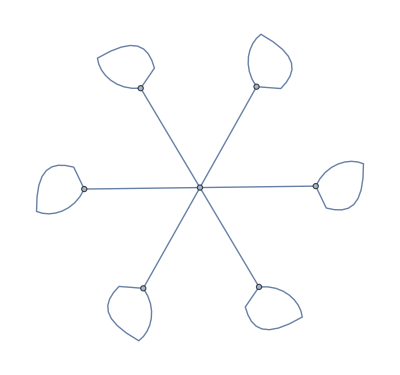

```mathematica
grlist[6][[-1]][[-1]]//AdjacencyGraph
```

The order of its automorphism group. All nodes have genus zero, so it should be 2^6 6!.

```mathematica
grlist[6][[-1]]//aut
```

46080

```mathematica
2^6 6!
```

46080

### Solving exactly in y

#### Picard-Fuchs calculations

The restriction in the choice of torus action as in Lho’s paper.

```mathematica
ee[0]=1;ee[1]=ee[2]^2/3/ee[3];
```

The algebraic relation for the canonical coordinates on the small quantum cohomology locus, arising from the leading order in z of the expansion of the solution of the equivariant PF equation.

```mathematica
polPFL[y_,XX_]=polPF/.XX[i_]->XX^i/.ll->L
```

XX^3 (1+27 y)+XX ee[2]+(XX^2 ee[2]^2)/(3 ee[3])+ee[3]

The same relation specialised to the fibrewise action α_i=(ϵ_1+ϵ_2)/3:

```mathematica
polPFLdiag[y_,XX_]=polPF/.XX[i_]->XX^i/.ll->L/.ee->eα/.α[ll_]->ϵ[1]/3+ϵ[2]/3//Simplify
```

XX^3 (1+27 y)+XX^2 (ϵ[1]+ϵ[2])+1/3 XX (ϵ[1]+ϵ[2])^2+1/27 (ϵ[1]+ϵ[2])^3

#### implicit derivatives up to order 7, hidden for legibility -- run this

The following table contains at its n^th entry the n^th derivative of a function y[x], defined implicitly as P[x,y[x]]=0 for a two-variable polynomial P[x,y], expressed in terms of P[x,y] and its derivatives.

```mathematica
ImplRepl[x_,y_]={-(Derivative[1,0][P][x,y])/(Derivative[0,1][P][x,y]),-(Derivative[0,2][P][x,y] (Derivative[1,0][P][x,y])^2-2 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[2,0][P][x,y])/(Derivative[0,1][P][x,y])^3,1/(Derivative[0,1][P][x,y])^5(-3 (Derivative[0,2][P][x,y])^2 (Derivative[1,0][P][x,y])^3-3 Derivative[0,1][P][x,y] Derivative[0,2][P][x,y] Derivative[1,0][P][x,y] (-3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^3-Derivative[0,1][P][x,y] (3 (Derivative[1,0][P][x,y])^2 Derivative[1,2][P][x,y]+Derivative[1,0][P][x,y] (6 (Derivative[1,1][P][x,y])^2-3 Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+Derivative[0,1][P][x,y] (-3 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])))),1/(Derivative[0,1][P][x,y])^7(-15 (Derivative[0,2][P][x,y])^3 (Derivative[1,0][P][x,y])^4+6 Derivative[0,1][P][x,y] (Derivative[0,2][P][x,y])^2 (Derivative[1,0][P][x,y])^2 (10 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] Derivative[0,2][P][x,y] (10 Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^4-Derivative[0,1][P][x,y] (24 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y]+3 (Derivative[0,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2+18 (Derivative[1,0][P][x,y])^2 (4 (Derivative[1,1][P][x,y])^2-Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+4 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-9 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])))-(Derivative[0,1][P][x,y])^2 (Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^4+2 Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^2 (8 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (-4 (Derivative[1,0][P][x,y])^3 Derivative[1,3][P][x,y]+6 (Derivative[1,0][P][x,y])^2 (-6 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y]+Derivative[0,1][P][x,y] Derivative[2,2][P][x,y])-4 Derivative[1,0][P][x,y] (6 (Derivative[1,1][P][x,y])^3-3 Derivative[0,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]-6 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[3,1][P][x,y])+Derivative[0,1][P][x,y] (12 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y]-6 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-4 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[3,0][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[4,0][P][x,y])))),1/(Derivative[0,1][P][x,y])^9(-105 (Derivative[0,2][P][x,y])^4 (Derivative[1,0][P][x,y])^5-75 Derivative[0,1][P][x,y] (Derivative[0,2][P][x,y])^3 (Derivative[1,0][P][x,y])^3 (-7 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]+2 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])-15 Derivative[0,1][P][x,y] (Derivative[0,2][P][x,y])^2 Derivative[1,0][P][x,y] (-7 Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^4+Derivative[0,1][P][x,y] (15 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y]+3 (Derivative[0,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2+10 (Derivative[1,0][P][x,y])^2 (6 (Derivative[1,1][P][x,y])^2-Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+2 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-15 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])))-5 (Derivative[0,1][P][x,y])^2 Derivative[0,2][P][x,y] (3 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^5+20 Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^3 (3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (-10 (Derivative[1,0][P][x,y])^4 Derivative[1,3][P][x,y]+12 (Derivative[1,0][P][x,y])^3 (-10 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y]+Derivative[0,1][P][x,y] Derivative[2,2][P][x,y])+(Derivative[0,1][P][x,y])^2 Derivative[2,0][P][x,y] (-9 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+2 Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])-6 (Derivative[1,0][P][x,y])^2 (20 (Derivative[1,1][P][x,y])^3-6 Derivative[0,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]-12 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[3,1][P][x,y])+Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (72 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y]-18 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-12 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[3,0][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[4,0][P][x,y])))+(Derivative[0,1][P][x,y])^2 (-10 (Derivative[0,3][P][x,y])^2 (Derivative[1,0][P][x,y])^5+5 Derivative[0,1][P][x,y] Derivative[0,3][P][x,y] Derivative[1,0][P][x,y] (10 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y]+3 (Derivative[0,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2+8 (Derivative[1,0][P][x,y])^2 (5 (Derivative[1,1][P][x,y])^2-Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+2 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-12 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y]))-Derivative[0,1][P][x,y] (-Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^5-5 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^3 (5 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-2 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (5 (Derivative[1,0][P][x,y])^4 Derivative[1,4][P][x,y]+10 (Derivative[1,0][P][x,y])^3 (6 (Derivative[1,2][P][x,y])^2+8 Derivative[1,1][P][x,y] Derivative[1,3][P][x,y]-Derivative[0,1][P][x,y] Derivative[2,3][P][x,y])+10 (Derivative[1,0][P][x,y])^2 (36 (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y]-9 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,2][P][x,y]+Derivative[0,1][P][x,y] (-3 Derivative[1,3][P][x,y] Derivative[2,0][P][x,y]-9 Derivative[1,2][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,2][P][x,y]))+5 Derivative[1,0][P][x,y] (24 (Derivative[1,1][P][x,y])^4-36 Derivative[0,1][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[2,1][P][x,y]+4 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] (-9 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]+2 Derivative[0,1][P][x,y] Derivative[3,1][P][x,y])+(Derivative[0,1][P][x,y])^2 (6 (Derivative[2,1][P][x,y])^2+6 Derivative[2,0][P][x,y] Derivative[2,2][P][x,y]+4 Derivative[1,2][P][x,y] Derivative[3,0][P][x,y]-Derivative[0,1][P][x,y] Derivative[4,1][P][x,y]))+Derivative[0,1][P][x,y] (-60 (Derivative[1,1][P][x,y])^3 Derivative[2,0][P][x,y]+20 Derivative[0,1][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[3,0][P][x,y]-5 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] (-12 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[4,0][P][x,y])+Derivative[0,1][P][x,y] (15 Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^2+Derivative[0,1][P][x,y] (-10 Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]-10 Derivative[2,0][P][x,y] Derivative[3,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[5,0][P][x,y]))))))),-1/(Derivative[0,1][P][x,y])^11(945 (Derivative[0,2][P][x,y])^5 (Derivative[1,0][P][x,y])^6+315 Derivative[0,1][P][x,y] (Derivative[0,2][P][x,y])^4 (Derivative[1,0][P][x,y])^4 (-18 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]+5 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+15 Derivative[0,1][P][x,y] (Derivative[0,2][P][x,y])^3 (Derivative[1,0][P][x,y])^2 (-84 Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^4+Derivative[0,1][P][x,y] (168 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y]+45 (Derivative[0,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2+105 (Derivative[1,0][P][x,y])^2 (8 (Derivative[1,1][P][x,y])^2-Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+20 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-21 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])))+15 (Derivative[0,1][P][x,y])^2 (Derivative[0,2][P][x,y])^2 (14 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^6+21 Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^4 (16 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-5 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (-42 (Derivative[1,0][P][x,y])^5 Derivative[1,3][P][x,y]+3 (Derivative[0,1][P][x,y])^3 (Derivative[2,0][P][x,y])^3+45 (Derivative[1,0][P][x,y])^4 (-14 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y]+Derivative[0,1][P][x,y] Derivative[2,2][P][x,y])+6 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] (-15 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+2 Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])-20 (Derivative[1,0][P][x,y])^3 (42 (Derivative[1,1][P][x,y])^3-9 Derivative[0,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]-18 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[3,1][P][x,y])+3 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (180 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y]-30 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-20 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[3,0][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[4,0][P][x,y])))+(Derivative[0,1][P][x,y])^2 Derivative[0,2][P][x,y] (280 (Derivative[0,3][P][x,y])^2 (Derivative[1,0][P][x,y])^6-10 Derivative[0,1][P][x,y] Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^2 (126 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y]+45 (Derivative[0,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2+90 (Derivative[1,0][P][x,y])^2 (7 (Derivative[1,1][P][x,y])^2-Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+20 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-18 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y]))+Derivative[0,1][P][x,y] (-21 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^6-45 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^4 (14 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-5 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (90 (Derivative[1,0][P][x,y])^5 Derivative[1,4][P][x,y]+150 (Derivative[1,0][P][x,y])^4 (9 (Derivative[1,2][P][x,y])^2+12 Derivative[1,1][P][x,y] Derivative[1,3][P][x,y]-Derivative[0,1][P][x,y] Derivative[2,3][P][x,y])+120 (Derivative[1,0][P][x,y])^3 (90 (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y]-15 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,2][P][x,y]+Derivative[0,1][P][x,y] (-5 Derivative[1,3][P][x,y] Derivative[2,0][P][x,y]-15 Derivative[1,2][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,2][P][x,y]))+5 (Derivative[0,1][P][x,y])^2 (108 (Derivative[1,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2-36 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[3,0][P][x,y]+Derivative[0,1][P][x,y] (-27 (Derivative[2,0][P][x,y])^2 Derivative[2,1][P][x,y]+2 Derivative[0,1][P][x,y] (Derivative[3,0][P][x,y])^2+3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[4,0][P][x,y]))+45 (Derivative[1,0][P][x,y])^2 (120 (Derivative[1,1][P][x,y])^4-120 Derivative[0,1][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[2,1][P][x,y]+8 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] (-15 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]+2 Derivative[0,1][P][x,y] Derivative[3,1][P][x,y])+(Derivative[0,1][P][x,y])^2 (12 (Derivative[2,1][P][x,y])^2+12 Derivative[2,0][P][x,y] Derivative[2,2][P][x,y]+8 Derivative[1,2][P][x,y] Derivative[3,0][P][x,y]-Derivative[0,1][P][x,y] Derivative[4,1][P][x,y]))+6 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-600 (Derivative[1,1][P][x,y])^3 Derivative[2,0][P][x,y]+120 Derivative[0,1][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[3,0][P][x,y]-15 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] (-24 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[4,0][P][x,y])+Derivative[0,1][P][x,y] (90 Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^2+Derivative[0,1][P][x,y] (-30 Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]-30 Derivative[2,0][P][x,y] Derivative[3,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[5,0][P][x,y]))))))+(Derivative[0,1][P][x,y])^3 (-30 (Derivative[0,3][P][x,y])^2 (Derivative[1,0][P][x,y])^4 (14 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-5 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])-5 Derivative[0,3][P][x,y] (7 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^6+Derivative[0,1][P][x,y] (-24 (Derivative[1,0][P][x,y])^5 Derivative[1,3][P][x,y]+3 (Derivative[0,1][P][x,y])^3 (Derivative[2,0][P][x,y])^3+30 (Derivative[1,0][P][x,y])^4 (-12 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y]+Derivative[0,1][P][x,y] Derivative[2,2][P][x,y])+12 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] (-6 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])-8 (Derivative[1,0][P][x,y])^3 (60 (Derivative[1,1][P][x,y])^3-15 Derivative[0,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]-30 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y]+2 (Derivative[0,1][P][x,y])^2 Derivative[3,1][P][x,y])+3 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (120 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y]-24 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-16 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[3,0][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[4,0][P][x,y])))+Derivative[0,1][P][x,y] (Derivative[0,6][P][x,y] (Derivative[1,0][P][x,y])^6+450 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^4 (Derivative[1,1][P][x,y])^2-720 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^5+90 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^5 Derivative[1,2][P][x,y]-3600 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^3 Derivative[1,2][P][x,y]-1800 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] (Derivative[1,2][P][x,y])^2-1200 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^3 (Derivative[1,1][P][x,y])^2 Derivative[1,3][P][x,y]-300 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[1,2][P][x,y] Derivative[1,3][P][x,y]-150 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[1,4][P][x,y]-6 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^5 Derivative[1,5][P][x,y]-300 Derivative[0,1][P][x,y] Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+360 (Derivative[0,1][P][x,y])^2 (Derivative[1,1][P][x,y])^4 Derivative[2,0][P][x,y]+2160 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]+540 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 (Derivative[1,2][P][x,y])^2 Derivative[2,0][P][x,y]+720 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[1,3][P][x,y] Derivative[2,0][P][x,y]+60 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,4][P][x,y] Derivative[2,0][P][x,y]+45 (Derivative[0,1][P][x,y])^2 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^2 (Derivative[2,0][P][x,y])^2-270 (Derivative[0,1][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^2-90 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] Derivative[1,3][P][x,y] (Derivative[2,0][P][x,y])^2+3 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^4 (12 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-5 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])-75 Derivative[0,1][P][x,y] Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[2,1][P][x,y]+1440 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^3 Derivative[2,1][P][x,y]+2160 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,1][P][x,y]+240 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,3][P][x,y] Derivative[2,1][P][x,y]-540 (Derivative[0,1][P][x,y])^3 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-540 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-540 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] (Derivative[2,1][P][x,y])^2+90 (Derivative[0,1][P][x,y])^4 Derivative[2,0][P][x,y] (Derivative[2,1][P][x,y])^2+1080 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^2 Derivative[2,2][P][x,y]+360 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y] Derivative[2,2][P][x,y]-540 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,2][P][x,y]+45 (Derivative[0,1][P][x,y])^4 (Derivative[2,0][P][x,y])^2 Derivative[2,2][P][x,y]-270 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[2,1][P][x,y] Derivative[2,2][P][x,y]+240 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[2,3][P][x,y]-90 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[2,0][P][x,y] Derivative[2,3][P][x,y]+15 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[2,4][P][x,y]+20 (Derivative[0,1][P][x,y])^2 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^3 Derivative[3,0][P][x,y]-120 (Derivative[0,1][P][x,y])^3 (Derivative[1,1][P][x,y])^3 Derivative[3,0][P][x,y]-360 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[3,0][P][x,y]-60 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,3][P][x,y] Derivative[3,0][P][x,y]+60 (Derivative[0,1][P][x,y])^4 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[3,0][P][x,y]+120 (Derivative[0,1][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]+60 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[2,2][P][x,y] Derivative[3,0][P][x,y]-360 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[3,1][P][x,y]-180 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[3,1][P][x,y]+120 (Derivative[0,1][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[3,1][P][x,y]+120 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[2,1][P][x,y] Derivative[3,1][P][x,y]-20 (Derivative[0,1][P][x,y])^5 Derivative[3,0][P][x,y] Derivative[3,1][P][x,y]-180 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[3,2][P][x,y]+60 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] Derivative[3,2][P][x,y]-20 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[3,3][P][x,y]+30 (Derivative[0,1][P][x,y])^4 (Derivative[1,1][P][x,y])^2 Derivative[4,0][P][x,y]+30 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,2][P][x,y] Derivative[4,0][P][x,y]-15 (Derivative[0,1][P][x,y])^5 Derivative[2,1][P][x,y] Derivative[4,0][P][x,y]+60 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[4,1][P][x,y]-15 (Derivative[0,1][P][x,y])^5 Derivative[2,0][P][x,y] Derivative[4,1][P][x,y]+15 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[4,2][P][x,y]-6 (Derivative[0,1][P][x,y])^5 Derivative[1,1][P][x,y] Derivative[5,0][P][x,y]-6 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[5,1][P][x,y]+(Derivative[0,1][P][x,y])^6 Derivative[6,0][P][x,y]))),-1/(Derivative[0,1][P][x,y])^13(10395 (Derivative[0,2][P][x,y])^6 (Derivative[1,0][P][x,y])^7+6615 Derivative[0,1][P][x,y] (Derivative[0,2][P][x,y])^5 (Derivative[1,0][P][x,y])^5 (-11 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]+3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+105 Derivative[0,1][P][x,y] (Derivative[0,2][P][x,y])^4 (Derivative[1,0][P][x,y])^3 (-165 Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^4+7 Derivative[0,1][P][x,y] (45 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y]+15 (Derivative[0,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2+27 (Derivative[1,0][P][x,y])^2 (10 (Derivative[1,1][P][x,y])^2-Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+5 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-27 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])))+105 (Derivative[0,1][P][x,y])^2 (Derivative[0,2][P][x,y])^3 Derivative[1,0][P][x,y] (30 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^6+84 Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^4 (10 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (-84 (Derivative[1,0][P][x,y])^5 Derivative[1,3][P][x,y]+15 (Derivative[0,1][P][x,y])^3 (Derivative[2,0][P][x,y])^3-84 (Derivative[1,0][P][x,y])^4 (18 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y]-Derivative[0,1][P][x,y] Derivative[2,2][P][x,y])+15 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] (-21 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+2 Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])-35 (Derivative[1,0][P][x,y])^3 (72 (Derivative[1,1][P][x,y])^3-12 Derivative[0,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]-24 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[3,1][P][x,y])+5 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (336 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y]-42 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-28 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[3,0][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[4,0][P][x,y])))+21 (Derivative[0,1][P][x,y])^2 (Derivative[0,2][P][x,y])^2 (300 (Derivative[0,3][P][x,y])^2 (Derivative[1,0][P][x,y])^7-35 Derivative[0,1][P][x,y] Derivative[0,3][P][x,y] (Derivative[1,0][P][x,y])^3 (36 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y]+15 (Derivative[0,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2+24 (Derivative[1,0][P][x,y])^2 (9 (Derivative[1,1][P][x,y])^2-Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+5 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-24 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y]))+Derivative[0,1][P][x,y] (-18 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^7-210 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^5 (3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (70 (Derivative[1,0][P][x,y])^6 Derivative[1,4][P][x,y]+105 (Derivative[1,0][P][x,y])^5 (12 (Derivative[1,2][P][x,y])^2+16 Derivative[1,1][P][x,y] Derivative[1,3][P][x,y]-Derivative[0,1][P][x,y] Derivative[2,3][P][x,y])+15 (Derivative[0,1][P][x,y])^3 (Derivative[2,0][P][x,y])^2 (-5 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])+75 (Derivative[1,0][P][x,y])^4 (168 (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y]-21 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,2][P][x,y]+Derivative[0,1][P][x,y] (-7 Derivative[1,3][P][x,y] Derivative[2,0][P][x,y]-21 Derivative[1,2][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,2][P][x,y]))+5 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] (270 (Derivative[1,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2-60 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[3,0][P][x,y]+Derivative[0,1][P][x,y] (-45 (Derivative[2,0][P][x,y])^2 Derivative[2,1][P][x,y]+2 Derivative[0,1][P][x,y] (Derivative[3,0][P][x,y])^2+3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[4,0][P][x,y]))+25 (Derivative[1,0][P][x,y])^3 (336 (Derivative[1,1][P][x,y])^4-252 Derivative[0,1][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[2,1][P][x,y]+12 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] (-21 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]+2 Derivative[0,1][P][x,y] Derivative[3,1][P][x,y])+(Derivative[0,1][P][x,y])^2 (18 (Derivative[2,1][P][x,y])^2+18 Derivative[2,0][P][x,y] Derivative[2,2][P][x,y]+12 Derivative[1,2][P][x,y] Derivative[3,0][P][x,y]-Derivative[0,1][P][x,y] Derivative[4,1][P][x,y]))+3 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (-2100 (Derivative[1,1][P][x,y])^3 Derivative[2,0][P][x,y]+300 Derivative[0,1][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[3,0][P][x,y]-25 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] (-36 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[4,0][P][x,y])+Derivative[0,1][P][x,y] (225 Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^2+Derivative[0,1][P][x,y] (-50 Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]-50 Derivative[2,0][P][x,y] Derivative[3,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[5,0][P][x,y]))))))+7 (Derivative[0,1][P][x,y])^3 Derivative[0,2][P][x,y] (-840 (Derivative[0,3][P][x,y])^2 (Derivative[1,0][P][x,y])^5 (3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])-10 Derivative[0,3][P][x,y] Derivative[1,0][P][x,y] (18 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^6+Derivative[0,1][P][x,y] (-56 (Derivative[1,0][P][x,y])^5 Derivative[1,3][P][x,y]+15 (Derivative[0,1][P][x,y])^3 (Derivative[2,0][P][x,y])^3-63 (Derivative[1,0][P][x,y])^4 (16 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y]-Derivative[0,1][P][x,y] Derivative[2,2][P][x,y])+30 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] (-9 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])-15 (Derivative[1,0][P][x,y])^3 (112 (Derivative[1,1][P][x,y])^3-21 Derivative[0,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]-42 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y]+2 (Derivative[0,1][P][x,y])^2 Derivative[3,1][P][x,y])+5 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (252 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y]-36 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-24 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[3,0][P][x,y]+(Derivative[0,1][P][x,y])^2 Derivative[4,0][P][x,y])))+Derivative[0,1][P][x,y] (4 Derivative[0,6][P][x,y] (Derivative[1,0][P][x,y])^7+2520 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^5 (Derivative[1,1][P][x,y])^2-7560 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^5+420 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^6 Derivative[1,2][P][x,y]-25200 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^3 (Derivative[1,1][P][x,y])^3 Derivative[1,2][P][x,y]-9450 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[1,1][P][x,y] (Derivative[1,2][P][x,y])^2-6300 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^4 (Derivative[1,1][P][x,y])^2 Derivative[1,3][P][x,y]-1260 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^5 Derivative[1,2][P][x,y] Derivative[1,3][P][x,y]-630 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^5 Derivative[1,1][P][x,y] Derivative[1,4][P][x,y]-21 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^6 Derivative[1,5][P][x,y]-1575 Derivative[0,1][P][x,y] Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+5400 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^4 Derivative[2,0][P][x,y]+16200 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]+2700 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 (Derivative[1,2][P][x,y])^2 Derivative[2,0][P][x,y]+3600 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[1,3][P][x,y] Derivative[2,0][P][x,y]+225 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,4][P][x,y] Derivative[2,0][P][x,y]+225 (Derivative[0,1][P][x,y])^2 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^3 (Derivative[2,0][P][x,y])^2-900 (Derivative[0,1][P][x,y])^3 (Derivative[1,1][P][x,y])^3 (Derivative[2,0][P][x,y])^2-2700 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^2-450 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,3][P][x,y] (Derivative[2,0][P][x,y])^2+90 (Derivative[0,1][P][x,y])^4 Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^3+21 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^5 (8 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])-315 Derivative[0,1][P][x,y] Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^5 Derivative[2,1][P][x,y]+10800 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^3 Derivative[2,1][P][x,y]+10800 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,1][P][x,y]+900 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,3][P][x,y] Derivative[2,1][P][x,y]-5400 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-2700 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]+540 (Derivative[0,1][P][x,y])^4 Derivative[1,1][P][x,y] (Derivative[2,0][P][x,y])^2 Derivative[2,1][P][x,y]-2700 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] (Derivative[2,1][P][x,y])^2+540 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] (Derivative[2,1][P][x,y])^2+5400 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 (Derivative[1,1][P][x,y])^2 Derivative[2,2][P][x,y]+1350 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,2][P][x,y] Derivative[2,2][P][x,y]-2700 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,2][P][x,y]+270 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] (Derivative[2,0][P][x,y])^2 Derivative[2,2][P][x,y]-900 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[2,1][P][x,y] Derivative[2,2][P][x,y]+900 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[2,3][P][x,y]-300 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[2,0][P][x,y] Derivative[2,3][P][x,y]+45 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^5 Derivative[2,4][P][x,y]+75 (Derivative[0,1][P][x,y])^2 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[3,0][P][x,y]-1200 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^3 Derivative[3,0][P][x,y]-1800 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[3,0][P][x,y]-200 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[1,3][P][x,y] Derivative[3,0][P][x,y]+360 (Derivative[0,1][P][x,y])^4 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y] Derivative[3,0][P][x,y]+360 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[3,0][P][x,y]+720 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]-90 (Derivative[0,1][P][x,y])^5 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]+180 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[2,2][P][x,y] Derivative[3,0][P][x,y]-30 (Derivative[0,1][P][x,y])^5 Derivative[1,1][P][x,y] (Derivative[3,0][P][x,y])^2-1800 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^2 Derivative[3,1][P][x,y]-600 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y] Derivative[3,1][P][x,y]+720 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[3,1][P][x,y]-45 (Derivative[0,1][P][x,y])^5 (Derivative[2,0][P][x,y])^2 Derivative[3,1][P][x,y]+360 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[2,1][P][x,y] Derivative[3,1][P][x,y]-60 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[3,0][P][x,y] Derivative[3,1][P][x,y]-600 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[3,2][P][x,y]+180 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[2,0][P][x,y] Derivative[3,2][P][x,y]-50 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^4 Derivative[3,3][P][x,y]+180 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[4,0][P][x,y]+90 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[4,0][P][x,y]-45 (Derivative[0,1][P][x,y])^5 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[4,0][P][x,y]-45 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[2,1][P][x,y] Derivative[4,0][P][x,y]+5 (Derivative[0,1][P][x,y])^6 Derivative[3,0][P][x,y] Derivative[4,0][P][x,y]+180 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[4,1][P][x,y]-45 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] Derivative[4,1][P][x,y]+30 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^3 Derivative[4,2][P][x,y]-18 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[5,0][P][x,y]+3 (Derivative[0,1][P][x,y])^6 Derivative[2,0][P][x,y] Derivative[5,0][P][x,y]-9 (Derivative[0,1][P][x,y])^5 (Derivative[1,0][P][x,y])^2 Derivative[5,1][P][x,y]+(Derivative[0,1][P][x,y])^6 Derivative[1,0][P][x,y] Derivative[6,0][P][x,y]))+(Derivative[0,1][P][x,y])^3 (-280 (Derivative[0,3][P][x,y])^3 (Derivative[1,0][P][x,y])^7+70 Derivative[0,1][P][x,y] (Derivative[0,3][P][x,y])^2 (Derivative[1,0][P][x,y])^3 (28 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y]+15 (Derivative[0,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2+21 (Derivative[1,0][P][x,y])^2 (8 (Derivative[1,1][P][x,y])^2-Derivative[0,1][P][x,y] Derivative[2,1][P][x,y])+5 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (-21 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y]))-7 Derivative[0,1][P][x,y] Derivative[0,3][P][x,y] (-8 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^7-35 Derivative[0,4][P][x,y] (Derivative[1,0][P][x,y])^5 (8 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+Derivative[0,1][P][x,y] (35 (Derivative[1,0][P][x,y])^6 Derivative[1,4][P][x,y]+30 (Derivative[1,0][P][x,y])^5 (21 (Derivative[1,2][P][x,y])^2+28 Derivative[1,1][P][x,y] Derivative[1,3][P][x,y]-2 Derivative[0,1][P][x,y] Derivative[2,3][P][x,y])+15 (Derivative[0,1][P][x,y])^3 (Derivative[2,0][P][x,y])^2 (-4 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])+50 (Derivative[1,0][P][x,y])^4 (126 (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y]-18 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,2][P][x,y]+Derivative[0,1][P][x,y] (-6 Derivative[1,3][P][x,y] Derivative[2,0][P][x,y]-18 Derivative[1,2][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,2][P][x,y]))+5 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] (180 (Derivative[1,1][P][x,y])^2 (Derivative[2,0][P][x,y])^2-48 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[3,0][P][x,y]+Derivative[0,1][P][x,y] (-36 (Derivative[2,0][P][x,y])^2 Derivative[2,1][P][x,y]+2 Derivative[0,1][P][x,y] (Derivative[3,0][P][x,y])^2+3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y] Derivative[4,0][P][x,y]))+20 (Derivative[1,0][P][x,y])^3 (210 (Derivative[1,1][P][x,y])^4-180 Derivative[0,1][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[2,1][P][x,y]+20 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] (-9 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,1][P][x,y])+(Derivative[0,1][P][x,y])^2 (15 (Derivative[2,1][P][x,y])^2+15 Derivative[2,0][P][x,y] Derivative[2,2][P][x,y]+10 Derivative[1,2][P][x,y] Derivative[3,0][P][x,y]-Derivative[0,1][P][x,y] Derivative[4,1][P][x,y]))+3 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (-1200 (Derivative[1,1][P][x,y])^3 Derivative[2,0][P][x,y]+200 Derivative[0,1][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[3,0][P][x,y]-20 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] (-30 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[4,0][P][x,y])+Derivative[0,1][P][x,y] (150 Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^2+Derivative[0,1][P][x,y] (-40 Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]-40 Derivative[2,0][P][x,y] Derivative[3,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[5,0][P][x,y])))))+Derivative[0,1][P][x,y] (35 (Derivative[0,4][P][x,y])^2 (Derivative[1,0][P][x,y])^7+35 Derivative[0,1][P][x,y] Derivative[0,4][P][x,y] Derivative[1,0][P][x,y] (-7 (Derivative[1,0][P][x,y])^5 Derivative[1,3][P][x,y]+3 (Derivative[0,1][P][x,y])^3 (Derivative[2,0][P][x,y])^3+9 (Derivative[1,0][P][x,y])^4 (-14 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y]+Derivative[0,1][P][x,y] Derivative[2,2][P][x,y])+3 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] (-15 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]+2 Derivative[0,1][P][x,y] Derivative[3,0][P][x,y])-5 (Derivative[1,0][P][x,y])^3 (42 (Derivative[1,1][P][x,y])^3-18 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] (-9 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]+Derivative[0,1][P][x,y] Derivative[3,1][P][x,y]))+Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (180 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y]-20 Derivative[0,1][P][x,y] Derivative[1,1][P][x,y] Derivative[3,0][P][x,y]+Derivative[0,1][P][x,y] (-30 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]+Derivative[0,1][P][x,y] Derivative[4,0][P][x,y])))+Derivative[0,1][P][x,y] (-Derivative[0,7][P][x,y] (Derivative[1,0][P][x,y])^7-882 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^5 (Derivative[1,1][P][x,y])^2+5040 Derivative[0,1][P][x,y] Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^6-147 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^6 Derivative[1,2][P][x,y]+37800 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^4 Derivative[1,2][P][x,y]+37800 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^3 (Derivative[1,1][P][x,y])^2 (Derivative[1,2][P][x,y])^2+3150 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^4 (Derivative[1,2][P][x,y])^3+16800 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^3 (Derivative[1,1][P][x,y])^3 Derivative[1,3][P][x,y]+12600 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[1,3][P][x,y]+420 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^5 (Derivative[1,3][P][x,y])^2+3150 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^4 (Derivative[1,1][P][x,y])^2 Derivative[1,4][P][x,y]+630 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^5 Derivative[1,2][P][x,y] Derivative[1,4][P][x,y]+252 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^5 Derivative[1,1][P][x,y] Derivative[1,5][P][x,y]+7 Derivative[0,1][P][x,y] (Derivative[1,0][P][x,y])^6 Derivative[1,6][P][x,y]+630 Derivative[0,1][P][x,y] Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y]-2520 (Derivative[0,1][P][x,y])^2 (Derivative[1,1][P][x,y])^5 Derivative[2,0][P][x,y]-25200 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^3 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y]-18900 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] (Derivative[1,2][P][x,y])^2 Derivative[2,0][P][x,y]-12600 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^2 Derivative[1,3][P][x,y] Derivative[2,0][P][x,y]-4200 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y] Derivative[1,3][P][x,y] Derivative[2,0][P][x,y]-2100 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[1,4][P][x,y] Derivative[2,0][P][x,y]-105 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,5][P][x,y] Derivative[2,0][P][x,y]-105 (Derivative[0,1][P][x,y])^2 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^3 (Derivative[2,0][P][x,y])^2+3780 (Derivative[0,1][P][x,y])^3 (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^2+1890 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] (Derivative[1,2][P][x,y])^2 (Derivative[2,0][P][x,y])^2+2520 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[1,3][P][x,y] (Derivative[2,0][P][x,y])^2+315 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,4][P][x,y] (Derivative[2,0][P][x,y])^2-105 (Derivative[0,1][P][x,y])^4 Derivative[1,3][P][x,y] (Derivative[2,0][P][x,y])^3-7 Derivative[0,6][P][x,y] (Derivative[1,0][P][x,y])^5 (7 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y]-3 Derivative[0,1][P][x,y] Derivative[2,0][P][x,y])+126 Derivative[0,1][P][x,y] Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^5 Derivative[2,1][P][x,y]-12600 (Derivative[0,1][P][x,y])^2 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^4 Derivative[2,1][P][x,y]-37800 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[2,1][P][x,y]-6300 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 (Derivative[1,2][P][x,y])^2 Derivative[2,1][P][x,y]-8400 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[1,3][P][x,y] Derivative[2,1][P][x,y]-525 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,4][P][x,y] Derivative[2,1][P][x,y]+5040 (Derivative[0,1][P][x,y])^3 (Derivative[1,1][P][x,y])^3 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]+15120 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]+2520 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,3][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y]-945 (Derivative[0,1][P][x,y])^4 Derivative[1,2][P][x,y] (Derivative[2,0][P][x,y])^2 Derivative[2,1][P][x,y]+7560 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^2 (Derivative[2,1][P][x,y])^2+3780 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,2][P][x,y] (Derivative[2,1][P][x,y])^2-1890 (Derivative[0,1][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] (Derivative[2,1][P][x,y])^2-630 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] (Derivative[2,1][P][x,y])^3-12600 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^3 Derivative[2,2][P][x,y]-12600 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,2][P][x,y]-1050 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,3][P][x,y] Derivative[2,2][P][x,y]+7560 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y] Derivative[2,2][P][x,y]+3780 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[2,2][P][x,y]-945 (Derivative[0,1][P][x,y])^4 Derivative[1,1][P][x,y] (Derivative[2,0][P][x,y])^2 Derivative[2,2][P][x,y]+7560 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[2,1][P][x,y] Derivative[2,2][P][x,y]-1890 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] Derivative[2,1][P][x,y] Derivative[2,2][P][x,y]+630 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 (Derivative[2,2][P][x,y])^2-4200 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^3 (Derivative[1,1][P][x,y])^2 Derivative[2,3][P][x,y]-1050 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,2][P][x,y] Derivative[2,3][P][x,y]+2520 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[2,3][P][x,y]-315 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] (Derivative[2,0][P][x,y])^2 Derivative[2,3][P][x,y]+840 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[2,1][P][x,y] Derivative[2,3][P][x,y]-525 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[2,4][P][x,y]+210 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[2,0][P][x,y] Derivative[2,4][P][x,y]-21 (Derivative[0,1][P][x,y])^2 (Derivative[1,0][P][x,y])^5 Derivative[2,5][P][x,y]-35 (Derivative[0,1][P][x,y])^2 Derivative[0,5][P][x,y] (Derivative[1,0][P][x,y])^4 Derivative[3,0][P][x,y]+840 (Derivative[0,1][P][x,y])^3 (Derivative[1,1][P][x,y])^4 Derivative[3,0][P][x,y]+5040 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[3,0][P][x,y]+1260 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 (Derivative[1,2][P][x,y])^2 Derivative[3,0][P][x,y]+1680 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[1,3][P][x,y] Derivative[3,0][P][x,y]+140 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[1,4][P][x,y] Derivative[3,0][P][x,y]-1260 (Derivative[0,1][P][x,y])^4 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[3,0][P][x,y]-420 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,3][P][x,y] Derivative[2,0][P][x,y] Derivative[3,0][P][x,y]-1260 (Derivative[0,1][P][x,y])^4 (Derivative[1,1][P][x,y])^2 Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]-1260 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,2][P][x,y] Derivative[2,1][P][x,y] Derivative[3,0][P][x,y]+210 (Derivative[0,1][P][x,y])^5 (Derivative[2,1][P][x,y])^2 Derivative[3,0][P][x,y]-1260 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[2,2][P][x,y] Derivative[3,0][P][x,y]+210 (Derivative[0,1][P][x,y])^5 Derivative[2,0][P][x,y] Derivative[2,2][P][x,y] Derivative[3,0][P][x,y]-210 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[2,3][P][x,y] Derivative[3,0][P][x,y]+70 (Derivative[0,1][P][x,y])^5 Derivative[1,2][P][x,y] (Derivative[3,0][P][x,y])^2+3360 (Derivative[0,1][P][x,y])^3 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^3 Derivative[3,1][P][x,y]+5040 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[3,1][P][x,y]+560 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[1,3][P][x,y] Derivative[3,1][P][x,y]-1260 (Derivative[0,1][P][x,y])^4 (Derivative[1,1][P][x,y])^2 Derivative[2,0][P][x,y] Derivative[3,1][P][x,y]-1260 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[3,1][P][x,y]-2520 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[2,1][P][x,y] Derivative[3,1][P][x,y]+420 (Derivative[0,1][P][x,y])^5 Derivative[2,0][P][x,y] Derivative[2,1][P][x,y] Derivative[3,1][P][x,y]-630 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[2,2][P][x,y] Derivative[3,1][P][x,y]+280 (Derivative[0,1][P][x,y])^5 Derivative[1,1][P][x,y] Derivative[3,0][P][x,y] Derivative[3,1][P][x,y]+140 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] (Derivative[3,1][P][x,y])^2+2520 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^2 (Derivative[1,1][P][x,y])^2 Derivative[3,2][P][x,y]+840 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[1,2][P][x,y] Derivative[3,2][P][x,y]-1260 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[3,2][P][x,y]+105 (Derivative[0,1][P][x,y])^5 (Derivative[2,0][P][x,y])^2 Derivative[3,2][P][x,y]-630 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[2,1][P][x,y] Derivative[3,2][P][x,y]+140 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[3,0][P][x,y] Derivative[3,2][P][x,y]+560 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^3 Derivative[1,1][P][x,y] Derivative[3,3][P][x,y]-210 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[2,0][P][x,y] Derivative[3,3][P][x,y]+35 (Derivative[0,1][P][x,y])^3 (Derivative[1,0][P][x,y])^4 Derivative[3,4][P][x,y]-210 (Derivative[0,1][P][x,y])^4 (Derivative[1,1][P][x,y])^3 Derivative[4,0][P][x,y]-630 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[1,2][P][x,y] Derivative[4,0][P][x,y]-105 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[1,3][P][x,y] Derivative[4,0][P][x,y]+105 (Derivative[0,1][P][x,y])^5 Derivative[1,2][P][x,y] Derivative[2,0][P][x,y] Derivative[4,0][P][x,y]+210 (Derivative[0,1][P][x,y])^5 Derivative[1,1][P][x,y] Derivative[2,1][P][x,y] Derivative[4,0][P][x,y]+105 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[2,2][P][x,y] Derivative[4,0][P][x,y]-35 (Derivative[0,1][P][x,y])^6 Derivative[3,1][P][x,y] Derivative[4,0][P][x,y]-630 (Derivative[0,1][P][x,y])^4 Derivative[1,0][P][x,y] (Derivative[1,1][P][x,y])^2 Derivative[4,1][P][x,y]-315 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[1,2][P][x,y] Derivative[4,1][P][x,y]+210 (Derivative[0,1][P][x,y])^5 Derivative[1,1][P][x,y] Derivative[2,0][P][x,y] Derivative[4,1][P][x,y]+210 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[2,1][P][x,y] Derivative[4,1][P][x,y]-35 (Derivative[0,1][P][x,y])^6 Derivative[3,0][P][x,y] Derivative[4,1][P][x,y]-315 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^2 Derivative[1,1][P][x,y] Derivative[4,2][P][x,y]+105 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[2,0][P][x,y] Derivative[4,2][P][x,y]-35 (Derivative[0,1][P][x,y])^4 (Derivative[1,0][P][x,y])^3 Derivative[4,3][P][x,y]+42 (Derivative[0,1][P][x,y])^5 (Derivative[1,1][P][x,y])^2 Derivative[5,0][P][x,y]+42 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[1,2][P][x,y] Derivative[5,0][P][x,y]-21 (Derivative[0,1][P][x,y])^6 Derivative[2,1][P][x,y] Derivative[5,0][P][x,y]+84 (Derivative[0,1][P][x,y])^5 Derivative[1,0][P][x,y] Derivative[1,1][P][x,y] Derivative[5,1][P][x,y]-21 (Derivative[0,1][P][x,y])^6 Derivative[2,0][P][x,y] Derivative[5,1][P][x,y]+21 (Derivative[0,1][P][x,y])^5 (Derivative[1,0][P][x,y])^2 Derivative[5,2][P][x,y]-7 (Derivative[0,1][P][x,y])^6 Derivative[1,1][P][x,y] Derivative[6,0][P][x,y]-7 (Derivative[0,1][P][x,y])^6 Derivative[1,0][P][x,y] Derivative[6,1][P][x,y]+(Derivative[0,1][P][x,y])^7 Derivative[7,0][P][x,y]))))};
```

#### reprise

The next function takes exp a rational function in variables (y, var), where var satisfies polPFL[y,var]=0; it reduces it modulo polPFL in the minimal form P[y,var]/Q[y,var] where deg P and deg Q ≤2 .

```mathematica
LLpowred[exp_,var_]:=Block[{temp=exp//Together},Collect[PolynomialRemainder[Numerator[temp],polPFL[y,var],var],var]/Collect[PolynomialRemainder[Denominator[temp],polPFL[y,var],var],var]//Factor]
```

Same, but for the diagonal (fibrewise) restriction of the weights.

```mathematica
LLpowreddiag[exp_,var_]:=Block[{temp=exp//Together},Collect[PolynomialRemainder[Numerator[temp],polPFLdiag[y,var],var],var]/Collect[PolynomialRemainder[Denominator[temp],polPFLdiag[y,var],var],var]//Factor]
```

A replacement rule expressing the n^th y-derivative of L_i, where polPFL[y,L_i]=0, as a rational function in (y, L_i), presented in the minimal form.

```mathematica
LLDerrepl=Table[Derivative[l][LLL[i_]][y]->LLpowred[(ImplRepl[y,LLL[i][y]]/.P->polPFL)[[l]],LLL[i][y]],{l,1,3}]//Simplify;
```

Same, but for the diagonal (fibrewise) restriction of the weights .

```mathematica
LLDerrepldiag=Table[Derivative[l][LLL[i_]][y]->LLpowreddiag[(ImplRepl[y,LLL[i][y]]/.P->polPFLdiag)[[l]],LLL[i][y]],{l,1,3}]//Simplify;
```

Cut-off in the z-expansion.

```mathematica
ZMAX=3
```

3

The asymptotic form of the i^th localised component of the I-function, up to order ZMAX.

```mathematica
IAs[y_]=Exp[μμ[i][y] /z](Sum[S0[i,k][y] z^k,{k,0,ZMAX+1}]);
```

The Picard-Fuchs operator applied to the asymptotic expansion of the I-function.

```mathematica
pf=Exp[-μμ[i][y] /z]Block[{coeff=Table[(z) ^k ee[3-k],{k,0,3}],coeff2=CoefficientList[Series[(3z DY )(3z DY +z)(3z DY+2 z ),{DY,0,3}],DY]},Sum[coeff[[n+1]] D[IAs[Exp[Y]],{Y,n}],{n,0,3}]+y Sum[coeff2[[n+1]] D[IAs[Exp[Y]],{Y,n}],{n,0,3}]]/.Y->Log[y]/.Table[D[μμ[i]'[y]->LLL[i][y]/y,{y,n}],{n,0,3}]//.LLDerrepl//Expand;
```

Ansatz for the solution of pf=0.

```mathematica
S0ans[i_,k_][y_]:=Sum[pp[k][l][m] LLL[i][y]^l y^m/ (3 ee[3]+ee[2] LLL[i][y])^(k+2)/((1+27 y) (-ee[2]^3+27 (1+27 y) ee[3]^2))^k,{l,0,2},{m,0,2k}];
```

Feeding the ansatz to the solution will give a linear system for the unknown coefficients pp[k][l][m]. It turns out that, with the bounds above on the exponents appearing in the numerator and denominator, the system admits a unique solution up to normalisation of pp[k][0][0]. 
The next routine solves the linear system arising from the ansatz, fixing the normalisation such that pp[k][0][0]=δ_k0. It takes a while. The result is copied below.

```mathematica
(**Module[{eq,dϕdy,repl={},temp,mat,vec,sol,tabpp},
Do[
eq=CoefficientList[LLpowred[(Simplify[Coefficient[pf,z,k]]/.S0->S0ans/.repl//Together//Numerator)//.LLDerrepl//Together//Numerator,LLL[i][y]]//Numerator,{y,LLL[i][y]}]; 
repl=Join[repl,Solve[eq==0 && pp[k-1][0][0]==KroneckerDelta[k,1],Table[pp[k-1][l][m],{l,0,2},{m,0,2k-2}]//Flatten]//Flatten];
,{k,1,ZMAX+1}]; PFAsRepl=repl];**)
```

```mathematica
PFAsRepl={pp[0][0][0]->1,pp[0][1][0]->ee[2]/(3 ee[3]),pp[0][2][0]->0,pp[1][0][0]->0,pp[1][0][1]->-162 ee[2] ee[3]^2,pp[1][0][2]->-4374 ee[2] ee[3]^2,pp[1][1][0]->(ee[2]^2 (-ee[2]^3+27 ee[3]^2))/(36 ee[3]),pp[1][1][1]->-(3 ee[2]^2 (ee[2]^3+153 ee[3]^2))/(4 ee[3]),pp[1][1][2]->-3645 ee[2]^2 ee[3],pp[1][2][0]->((-ee[2]^3+27 ee[3]^2) (ee[2]^3+54 ee[3]^2))/(324 ee[3]^2),pp[1][2][1]->(-ee[2]^6-405 ee[2]^3 ee[3]^2+2916 ee[3]^4)/(12 ee[3]^2),pp[1][2][2]->-243/2 (7 ee[2]^3-27 ee[3]^2),pp[2][0][0]->0,pp[2][0][1]->-1/96 ee[2]^2 (ee[2]^3-27 ee[3]^2) (35 ee[2]^3+25056 ee[3]^2),pp[2][0][2]->-9/32 ee[2]^2 (35 ee[2]^6+56430 ee[2]^3 ee[3]^2-1405512 ee[3]^4),pp[2][0][3]->-(59049 ee[2]^2 ee[3]^2 (133 ee[2]^6-6780 ee[2]^3 ee[3]^2+86832 ee[3]^4))/(32 (ee[2]^3-27 ee[3]^2)),pp[2][0][4]->(43046721 ee[2]^2 ee[3]^4 (-7 ee[2]^3+216 ee[3]^2))/(32 (-ee[2]^3+27 ee[3]^2)),pp[2][1][0]->-((-ee[2]^3+27 ee[3]^2)^3)/(1944 ee[3]),pp[2][1][1]->((-ee[2]^3+27 ee[3]^2) (97 ee[2]^6+56268 ee[2]^3 ee[3]^2+61236 ee[3]^4))/(288 ee[3]),pp[2][1][2]->(3 (-101 ee[2]^9-130950 ee[2]^6 ee[3]^2+3093876 ee[2]^3 ee[3]^4+5432508 ee[3]^6))/(32 ee[3]),pp[2][1][3]->-(2187 ee[3] (2875 ee[2]^9-145368 ee[2]^6 ee[3]^2+1641708 ee[2]^3 ee[3]^4+5589972 ee[3]^6))/(32 (ee[2]^3-27 ee[3]^2)),pp[2][1][4]->(1594323 ee[3]^3 (253 ee[2]^6-4968 ee[2]^3 ee[3]^2-69984 ee[3]^4))/(32 (ee[2]^3-27 ee[3]^2)),pp[2][2][0]->-(ee[2] (-ee[2]^3+27 ee[3]^2)^2 (-17 ee[2]^3+216 ee[3]^2))/(23328 ee[3]^2),pp[2][2][1]->-(ee[2] (-ee[2]^3+27 ee[3]^2) (-71 ee[2]^6-38070 ee[2]^3 ee[3]^2+110808 ee[3]^4))/(864 ee[3]^2),pp[2][2][2]->-(ee[2] (88 ee[2]^9+93528 ee[2]^6 ee[3]^2-2735937 ee[2]^3 ee[3]^4+8030664 ee[3]^6))/(32 ee[3]^2),pp[2][2][3]->-(729 ee[2] (2167 ee[2]^9-137484 ee[2]^6 ee[3]^2+2437776 ee[2]^3 ee[3]^4-7715736 ee[3]^6))/(32 (ee[2]^3-27 ee[3]^2)),pp[2][2][4]->(531441 ee[2] ee[3]^2 (701 ee[2]^6-23112 ee[2]^3 ee[3]^2+93312 ee[3]^4))/(32 (ee[2]^3-27 ee[3]^2)),pp[3][1][0]->-(ee[2] (ee[2]^3-27 ee[3]^2)^3 (7889 ee[2]^6-222966 ee[2]^3 ee[3]^2+1049760 ee[3]^4))/(4199040 ee[3] (ee[2]^3-9 ee[3]^2)),pp[3][2][0]->-(ee[2]^2 (ee[2]^3-27 ee[3]^2)^3 (1309 ee[2]^6-37632 ee[2]^3 ee[3]^2+126684 ee[3]^4))/(1399680 ee[3]^2 (ee[2]^3-9 ee[3]^2)),pp[3][0][0]->0,pp[3][0][1]->-((ee[2]^3-27 ee[3]^2)^2 (3563 ee[2]^9+5608566 ee[2]^6 ee[3]^2-36771732 ee[2]^3 ee[3]^4-123084360 ee[3]^6))/(25920 (ee[2]^3-9 ee[3]^2)),pp[3][1][1]->-(ee[2] (ee[2]^3-27 ee[3]^2)^2 (5005 ee[2]^9+2327491 ee[2]^6 ee[3]^2-9741114 ee[2]^3 ee[3]^4-97511040 ee[3]^6))/(17280 ee[3] (ee[2]^3-9 ee[3]^2)),pp[3][2][1]->(ee[2]^2 (-ee[2]^3+27 ee[3]^2)^2 (18907 ee[2]^9+6558345 ee[2]^6 ee[3]^2-132282882 ee[2]^3 ee[3]^4+697040640 ee[3]^6))/(155520 ee[3]^2 (-ee[2]^3+9 ee[3]^2)),pp[3][0][2]->-(3 (ee[2]^3-27 ee[3]^2) (4231 ee[2]^12+6278267 ee[2]^9 ee[3]^2-142851870 ee[2]^6 ee[3]^4+462022704 ee[2]^3 ee[3]^6+2728063800 ee[3]^8))/(640 (ee[2]^3-9 ee[3]^2)),pp[3][0][3]->-1/(640 (ee[2]^3-9 ee[3]^2))9 (30953 ee[2]^15+82923921 ee[2]^12 ee[3]^2-3654656334 ee[2]^9 ee[3]^4+40216043160 ee[2]^6 ee[3]^6-27320318928 ee[2]^3 ee[3]^8-857108044800 ee[3]^10),pp[3][0][4]->-((6561 ee[3]^2 (1417777 ee[2]^15-94764852 ee[2]^12 ee[3]^2+1955822922 ee[2]^9 ee[3]^4-9996123087 ee[2]^6 ee[3]^6-55536293088 ee[2]^3 ee[3]^8+388377082800 ee[3]^10))/(640 (-ee[2]^3+9 ee[3]^2) (-ee[2]^3+27 ee[3]^2))),pp[3][0][5]->(4782969 ee[3]^4 (10490 ee[2]^12+1870029 ee[2]^9 ee[3]^2-81120690 ee[2]^6 ee[3]^4+500053176 ee[2]^3 ee[3]^6+1488034800 ee[3]^8))/(640 (-ee[2]^3+9 ee[3]^2) (-ee[2]^3+27 ee[3]^2)),pp[3][0][6]->(847288609443 ee[3]^6 (-10 ee[2]^9+1791 ee[2]^6 ee[3]^2-45824 ee[2]^3 ee[3]^4+309960 ee[3]^6))/(640 (-ee[2]^3+9 ee[3]^2) (-ee[2]^3+27 ee[3]^2)),pp[3][1][2]->-1/(960 ee[3] (ee[2]^3-9 ee[3]^2))ee[2] (ee[2]^3-27 ee[3]^2) (22984 ee[2]^12+22193940 ee[2]^9 ee[3]^2-513470826 ee[2]^6 ee[3]^4+1102158333 ee[2]^3 ee[3]^6+14526054000 ee[3]^8),pp[3][1][3]->-1/(320 ee[3] (ee[2]^3-9 ee[3]^2))3 ee[2] (50374 ee[2]^15+106646346 ee[2]^12 ee[3]^2-5192540154 ee[2]^9 ee[3]^4+66071507301 ee[2]^6 ee[3]^6-50839240383 ee[2]^3 ee[3]^8-1714216089600 ee[3]^10),pp[3][1][4]->-((2187 ee[2] ee[3] (3823312 ee[2]^15-307942083 ee[2]^12 ee[3]^2+8304349311 ee[2]^9 ee[3]^4-75525160347 ee[2]^6 ee[3]^6-61318371168 ee[2]^3 ee[3]^8+2253734992800 ee[3]^10))/(640 (ee[2]^3-27 ee[3]^2) (ee[2]^3-9 ee[3]^2))),pp[3][1][5]->(1594323 ee[2] ee[3]^3 (817625 ee[2]^12-38881125 ee[2]^9 ee[3]^2+425761029 ee[2]^6 ee[3]^4+1430193024 ee[2]^3 ee[3]^6-20747456640 ee[3]^8))/(640 (ee[2]^3-27 ee[3]^2) (ee[2]^3-9 ee[3]^2)),pp[3][1][6]->(10460353203 ee[2] ee[3]^5 (745 ee[2]^9-22338 ee[2]^6 ee[3]^2+249912 ee[2]^3 ee[3]^4-29160 ee[3]^6))/(160 (ee[2]^3-27 ee[3]^2) (ee[2]^3-9 ee[3]^2)),pp[3][2][2]->-(ee[2]^2 (ee[2]^3-27 ee[3]^2) (2770 ee[2]^12+2406059 ee[2]^9 ee[3]^2-86639490 ee[2]^6 ee[3]^4+908621226 ee[2]^3 ee[3]^6-3123692100 ee[3]^8))/(320 ee[3]^2 (ee[2]^3-9 ee[3]^2)),pp[3][2][3]->-1/(320 ee[3]^2 (ee[2]^3-9 ee[3]^2))3 ee[2]^2 (17440 ee[2]^15+35029008 ee[2]^12 ee[3]^2-2237495886 ee[2]^9 ee[3]^4+44589625443 ee[2]^6 ee[3]^6-285667075053 ee[2]^3 ee[3]^8+420709953240 ee[3]^10),pp[3][2][4]->-((2187 ee[2]^2 (1261612 ee[2]^15-133986645 ee[2]^12 ee[3]^2+4663421019 ee[2]^9 ee[3]^4-57219314247 ee[2]^6 ee[3]^6+62137144602 ee[2]^3 ee[3]^8+1390791725820 ee[3]^10))/(640 (ee[2]^3-27 ee[3]^2) (ee[2]^3-9 ee[3]^2))),pp[3][2][5]->(1594323 ee[2]^2 ee[3]^2 (632407 ee[2]^12-26755011 ee[2]^9 ee[3]^2+10148895 ee[2]^6 ee[3]^4+9314914140 ee[2]^3 ee[3]^6-67369712688 ee[3]^8))/(640 (ee[2]^3-27 ee[3]^2) (ee[2]^3-9 ee[3]^2)),pp[3][2][6]->(1162261467 ee[2]^2 ee[3]^4 (58885 ee[2]^9-3737997 ee[2]^6 ee[3]^2+74732463 ee[2]^3 ee[3]^4-404157600 ee[3]^6))/(320 (ee[2]^3-27 ee[3]^2) (ee[2]^3-9 ee[3]^2))};
```

The next routine checks that the Picard-Fuchs equations are effectively satisfied by the ansatz. Takes about half an hour; it’s commented out.

```mathematica
(**Table[
Block[{temp},
temp=Numerator[LLpowred[Coefficient[pf,z,k],LLL[i][y]]]/.S0->S0ans/.PFAsRepl;
Print["Step 1 done, k=" <> ToString[k]];
temp=temp//Together//Numerator;
Print["Step 2 done, k=" <> ToString[k]];
temp= temp //.LLDerrepl//Together//Numerator;
Print["Step 3 done, k=" <> ToString[k]];
LLpowred[temp,LLL[i][y]]
]
,{k,0,ZMAX+1}]//AbsoluteTiming**)
```

#### The R-matrix

The square-length of the quantum idempotents.

```mathematica
3 ϵ[1] ϵ[2]ff2[LLL[i][y]]//Factor
```

(ϵ[1] ϵ[2] (3 ee[3]+ee[2] LLL[i][y])^2)/ee[3]

The lengths, accordingly.

```mathematica
sqrtΔ[i_]=Sqrt[  ϵ[1] ϵ[2]/ee[3]](3 ee[3]+ee[2] LLL[i][y]);sqrtΔcl[i]=Sqrt[  ϵ[1] ϵ[2]/ee[3]](3 ee[3]-ee[2] α[i]);
```

Constructing the R-matrix now. The previous ansatz was not normalised such that e^(-u_j(y)/z)I_j(y,z) -> z for y->0. We ensure that this is the case below.

```mathematica
PPunnorm[0,i_][z_]=Sum[S0ans[i,k][y]z^k/.PFAsRepl,{k,0,ZMAX}]+O[z]^(ZMAX+1)//Simplify;
```

```mathematica
normLR[i_,z_]=Sum[cnormLR[i,k] z^k,{k,0,ZMAX}];
```

```mathematica
replnormI=Solve[(Take[CoefficientList[PPunnorm[0,i][z] normLR[i,z],z],ZMAX+1]/.y->0/.LLL[i][0]->-α[i])==Table[KroneckerDelta[k,0]/sqrtΔcl[i],{k,0,ZMAX}],Table[cnormLR[i,k],{k,0,ZMAX}]//Simplify]//Flatten;
```

So PPunnorm[0,i][z] normLR[i,z] /. replnormI returns the S-matrix acting on the identity (times diag(e^(-u/z))). To get the identity column of the R-matrix, we need to normalise by the materialisation constants from quantum Riemann-Roch.

```mathematica
replqrr = Block[{ser},Table[qrrc[ll_,k]->SeriesCoefficient[Series[Exp[Sum[Qrrc[ll,k] z^(2k+1),{k,0,ZMAX}]],{z,0,ZMAX+1}],k],{k,0,ZMAX+1}]//Flatten];
```

```mathematica
ff[i_][z_]=Series[1+Sum[qrrc[i,k]z^k,{k,1,ZMAX}],{z,0,ZMAX}]//Simplify//Normal
```

1+z qrrc[i,1]+z^2 qrrc[i,2]+z^3 qrrc[i,3]

```mathematica
w[i_,j_]:=If[j<3,If[i != j, α[j]-α[i], 3 α[i]],-ϵ[j-2]]
```

```mathematica
Qrrc[i_,k_]:=-BernoulliB[2k+2]/(2k+2)/(2k+1)Sum[1/w[i,j]^(2k+1),{j,0,4}]
```

The R-matrix applied to the identity, in minimal form, is then:

```mathematica
PP[0,i_][z_]=Sum[LLpowred[Sum[Coefficient[PPunnorm[0,i][z],z,k]Coefficient[ff[i][z],z,m] Coefficient[normLR[i,z],z,l-k-m]  z^l/.replnormI,{k,0,l},{m,0,l}],LLL[i][y]]//Simplify,{l,0,ZMAX}];
```

I will want to restrict to the fibrewise choice α[i]=(ϵ[1]+ϵ[2])/3 of weights now. The tricky bit is that the materialisation constants in ff[i][z] are ill-defined in that case. We need to take that as some sort of limit from the case of isolated fixed points α_i!=α_j, and *importantly*, we need to do it without leaving the quartic e_2^2=3 e_1 e_3 in the weight space as that constraint has been imposed while solving the Picard--Fuchs equations (e.g., α_i=(ϵ[1]+ϵ[2])/3 + i δ doesn’t work). It turns out that choosing α_i=(ϵ[1]+ϵ[2])/(3(1-ω^iδ)) for ω=e^(2 π I/3) and δ!=0 does the trick:

```mathematica
eα[2]^2-3eα[1]eα[3]/.α[i_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2Pi I i/3]δ)//Simplify
```

0

In the following, I’ll restrict the weights as above and extract the limit as δ->0 of each Taylor coefficient in z of the R-matrix applied to the identity. It turns out to be more expedient to extract leading order in δ of the numerator and denominator for each coefficient, and to divide the former by the latter. Here goes:

```mathematica
Series[(Coefficient[PP[0,0][z],z,0]//Numerator)/.replqrr/.ee->eα/.α[ll_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2 Pi I/3 ll] δ),{δ,0,0}]//Simplify
```

1

```mathematica
Series[(Coefficient[PP[0,0][z],z,0]//Denominator)/.replqrr/.ee->eα/.α[ll_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2 Pi I/3 ll] δ),{δ,0,0}]//Simplify
```

(√((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3) (ϵ[1]+ϵ[2])^2 (ϵ[1]+ϵ[2]+3 LLL[0][y]))/(√3)+O[δ]^1

```mathematica
%%/%//Normal//FullSimplify
```

(√3)/(√((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3) (ϵ[1]+ϵ[2])^2 (ϵ[1]+ϵ[2]+3 LLL[0][y]))

```mathematica
cPP[0,i_][0]=%/.LLL[0][y]->LLL[i][y];
```

```mathematica
cPP[0,i_][0]=(√3)/(√((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3) (ϵ[1]+ϵ[2])^2 (ϵ[1]+ϵ[2]+3 LLL[0][y]))/.LLL[0][y]->LLL[i][y];
```

```mathematica
Series[(Coefficient[PP[0,0][z],z,1]//Numerator)/.replqrr/.ee->eα/.α[ll_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2 Pi I/3 ll] δ),{δ,0,2}]//Simplify
```

-1/(177147 ((-1+(-1)^(1/3))^2 ϵ[1] ϵ[2]))((1+(-1)^(1/3))^2 y (1+27 y) (ϵ[1]+ϵ[2])^18 ((ϵ[1]+ϵ[2])^2 (ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)+6 (ϵ[1]^3-8 ϵ[1]^2 ϵ[2]-8 ϵ[1] ϵ[2]^2+ϵ[2]^3) LLL[0][y]+9 (ϵ[1]^2-11 ϵ[1] ϵ[2]+ϵ[2]^2) (LLL[0][y])^2)) δ^2+O[δ]^3

```mathematica
Series[(Coefficient[PP[0,0][z],z,1]//Denominator)/.replqrr/.ee->eα/.α[ll_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2 Pi I/3 ll] δ),{δ,0,2}]//Simplify
```

(4 y^2 √((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3) (ϵ[1]+ϵ[2])^22 ((ϵ[1]+ϵ[2])^2+9 (ϵ[1]+ϵ[2]) LLL[0][y]+27 (LLL[0][y])^2) δ^2)/(729 √3)+O[δ]^3

```mathematica
%%/%//Normal//FullSimplify
```

((1+27 y) (ϵ[1]+ϵ[2]+3 LLL[0][y]) ((ϵ[1]+ϵ[2]) (ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)+3 (ϵ[1]^2-11 ϵ[1] ϵ[2]+ϵ[2]^2) LLL[0][y]))/(108 √3 y ((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3)^(3/2) (ϵ[1]+ϵ[2])^7 ((ϵ[1]+ϵ[2])^2+9 LLL[0][y] (ϵ[1]+ϵ[2]+3 LLL[0][y])))

```mathematica
cPP[0,i_][1]=%/.LLL[0][y]->LLL[i][y];
```

```mathematica
cPP[0,i_][1]=((1+27 y) (ϵ[1]+ϵ[2]+3 LLL[0][y]) ((ϵ[1]+ϵ[2]) (ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)+3 (ϵ[1]^2-11 ϵ[1] ϵ[2]+ϵ[2]^2) LLL[0][y]))/(108 √3 y ((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3)^(3/2) (ϵ[1]+ϵ[2])^7 ((ϵ[1]+ϵ[2])^2+9 LLL[0][y] (ϵ[1]+ϵ[2]+3 LLL[0][y])))/.LLL[0][y]->LLL[i][y];
```

```mathematica
Series[(Coefficient[PP[0,0][z],z,2]//Numerator)/.replqrr/.ee->eα/.α[ll_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2 Pi I/3 ll] δ),{δ,0,7}]//Simplify
```

-1/(3486784401 (ϵ[1]^2 ϵ[2]^2))(y^2 (1+27 y) (ϵ[1]+ϵ[2])^41 ((ϵ[1]+ϵ[2])^2 (8 ϵ[1] ϵ[2] (ϵ[1]^2-27 ϵ[1] ϵ[2]+ϵ[2]^2)+27 y (ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)^2)+3 (ϵ[1]+ϵ[2]) (16 ϵ[1] ϵ[2] (ϵ[1]^2-31 ϵ[1] ϵ[2]+ϵ[2]^2)+27 y (3 ϵ[1]^4-50 ϵ[1]^3 ϵ[2]+305 ϵ[1]^2 ϵ[2]^2-50 ϵ[1] ϵ[2]^3+3 ϵ[2]^4)) LLL[0][y]+9 (8 ϵ[1] ϵ[2] (ϵ[1]^2-35 ϵ[1] ϵ[2]+ϵ[2]^2)+27 y (3 ϵ[1]^4-58 ϵ[1]^3 ϵ[2]+521 ϵ[1]^2 ϵ[2]^2-58 ϵ[1] ϵ[2]^3+3 ϵ[2]^4)) (LLL[0][y])^2)) δ^7+O[δ]^8

```mathematica
Series[(Coefficient[PP[0,0][z],z,2]//Denominator)/.replqrr/.ee->eα/.α[ll_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2 Pi I/3 ll] δ),{δ,0,7}]//Simplify
```

-(32 (y^3 √((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3) (ϵ[1]+ϵ[2])^46 ((-2+27 y) (ϵ[1]+ϵ[2])^2+3 (-5+108 y) (ϵ[1]+ϵ[2]) LLL[0][y]+27 (-1+54 y) (LLL[0][y])^2)) δ^7)/(14348907 √3)+O[δ]^8

```mathematica
%%/%//Normal//FullSimplify
```

((1+27 y) ((ϵ[1]+ϵ[2])^2 (8 ϵ[1] ϵ[2] (ϵ[1]^2-27 ϵ[1] ϵ[2]+ϵ[2]^2)+27 y (ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)^2)+3 (ϵ[1]+ϵ[2]) (81 y ϵ[1]^4+2 (8-675 y) ϵ[1]^3 ϵ[2]+(-496+8235 y) ϵ[1]^2 ϵ[2]^2+2 (8-675 y) ϵ[1] ϵ[2]^3+81 y ϵ[2]^4) LLL[0][y]+9 (81 y ϵ[1]^4+2 (4-783 y) ϵ[1]^3 ϵ[2]+(-280+14067 y) ϵ[1]^2 ϵ[2]^2+2 (4-783 y) ϵ[1] ϵ[2]^3+81 y ϵ[2]^4) (LLL[0][y])^2))/(2592 √3 y ((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3)^(5/2) (ϵ[1]+ϵ[2])^11 ((-2+27 y) (ϵ[1]+ϵ[2])^2+3 LLL[0][y] ((-5+108 y) (ϵ[1]+ϵ[2])+9 (-1+54 y) LLL[0][y])))

```mathematica
cPP[0,i_][2]=%/.LLL[0][y]->LLL[i][y];
```

```mathematica
cPP[0,i_][2]=((1+27 y) ((ϵ[1]+ϵ[2])^2 (8 ϵ[1] ϵ[2] (ϵ[1]^2-27 ϵ[1] ϵ[2]+ϵ[2]^2)+27 y (ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)^2)+3 (ϵ[1]+ϵ[2]) (81 y ϵ[1]^4+2 (8-675 y) ϵ[1]^3 ϵ[2]+(-496+8235 y) ϵ[1]^2 ϵ[2]^2+2 (8-675 y) ϵ[1] ϵ[2]^3+81 y ϵ[2]^4) LLL[0][y]+9 (81 y ϵ[1]^4+2 (4-783 y) ϵ[1]^3 ϵ[2]+(-280+14067 y) ϵ[1]^2 ϵ[2]^2+2 (4-783 y) ϵ[1] ϵ[2]^3+81 y ϵ[2]^4) (LLL[0][y])^2))/(2592 √3 y ((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3)^(5/2) (ϵ[1]+ϵ[2])^11 ((-2+27 y) (ϵ[1]+ϵ[2])^2+3 LLL[0][y] ((-5+108 y) (ϵ[1]+ϵ[2])+9 (-1+54 y) LLL[0][y])))/.LLL[0][y]->LLL[i][y];
```

The cubic order requires more muscle in the calculation of the denominator. The below uses a trick to distribute the calculation in parallel to speed it up.

```mathematica
(Coefficient[PP[0,0][z],z,3]//Numerator)/.replqrr/.ee->eα/.α[ll_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2 Pi I/3 ll] δ);
```

```mathematica
Block[{prefactor, arg, out},
prefactor=%[[1]]; arg=%[[2]];
DistributeDefinitions[arg];
If[Head[arg]==Plus,
out=prefactor ParallelSum[SeriesCoefficient[Series[arg[[k]],{δ,0,9}],9] δ^9//Simplify,{k,1,Length[arg]}]//Simplify;
]; out]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

-1/(16677181699666569 ϵ[1]^3 ϵ[2]^3)2 y^3 (1+27 y) δ^9 (ϵ[1]+ϵ[2])^67 ((ϵ[1]+ϵ[2])^2 (-320 ϵ[1]^2 ϵ[2]^2 (3 ϵ[1]^2-185 ϵ[1] ϵ[2]+3 ϵ[2]^2)+729 y^2 (139 ϵ[1]^6+537 ϵ[1]^5 ϵ[2]-318 ϵ[1]^4 ϵ[2]^2-9451 ϵ[1]^3 ϵ[2]^3-318 ϵ[1]^2 ϵ[2]^4+537 ϵ[1] ϵ[2]^5+139 ϵ[2]^6)-54 y (139 ϵ[1]^6+627 ϵ[1]^5 ϵ[2]-4698 ϵ[1]^4 ϵ[2]^2+47379 ϵ[1]^3 ϵ[2]^3-4698 ϵ[1]^2 ϵ[2]^4+627 ϵ[1] ϵ[2]^5+139 ϵ[2]^6))+3 (ϵ[1]+ϵ[2]) (-640 ϵ[1]^2 ϵ[2]^2 (3 ϵ[1]^2-199 ϵ[1] ϵ[2]+3 ϵ[2]^2)+2916 y^2 (139 ϵ[1]^6+552 ϵ[1]^5 ϵ[2]-888 ϵ[1]^4 ϵ[2]^2-7606 ϵ[1]^3 ϵ[2]^3-888 ϵ[1]^2 ϵ[2]^4+552 ϵ[1] ϵ[2]^5+139 ϵ[2]^6)-135 y (139 ϵ[1]^6+633 ϵ[1]^5 ϵ[2]-5310 ϵ[1]^4 ϵ[2]^2+67317 ϵ[1]^3 ϵ[2]^3-5310 ϵ[1]^2 ϵ[2]^4+633 ϵ[1] ϵ[2]^5+139 ϵ[2]^6)) LLL[0][y]+27 (-320 ϵ[1]^2 ϵ[2]^2 (ϵ[1]^2-71 ϵ[1] ϵ[2]+ϵ[2]^2)+1458 y^2 (139 ϵ[1]^6+567 ϵ[1]^5 ϵ[2]-1618 ϵ[1]^4 ϵ[2]^2+1119 ϵ[1]^3 ϵ[2]^3-1618 ϵ[1]^2 ϵ[2]^4+567 ϵ[1] ϵ[2]^5+139 ϵ[2]^6)-27 y (139 ϵ[1]^6+657 ϵ[1]^5 ϵ[2]-7118 ϵ[1]^4 ϵ[2]^2+119549 ϵ[1]^3 ϵ[2]^3-7118 ϵ[1]^2 ϵ[2]^4+657 ϵ[1] ϵ[2]^5+139 ϵ[2]^6)) (LLL[0][y])^2)

```mathematica
Series[(Coefficient[PP[0,0][z],z,3]//Denominator)/.replqrr/.ee->eα/.α[ll_]->(ϵ[1]/3+ϵ[2]/3)/(1-Exp[2 Pi I/3 ll] δ),{δ,0,9}]//Simplify
```

1/(7625597484987 √3)1280 y^4 √((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3) (ϵ[1]+ϵ[2])^73 ((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^2+3 (2-540 y+3645 y^2) (ϵ[1]+ϵ[2]) LLL[0][y]+9 (1-432 y+7290 y^2) (LLL[0][y])^2) δ^9+O[δ]^10

```mathematica
%%/%//Normal//FullSimplify
```

-(((1+27 y) ((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3)^(3/2) ((ϵ[1]+ϵ[2])^2 (3753 y (-2+27 y) ϵ[1]^6+81 y (-418+4833 y) ϵ[1]^5 ϵ[2]-6 (160+729 y (-58+53 y)) ϵ[1]^4 ϵ[2]^2+(59200-81 y (31586+85059 y)) ϵ[1]^3 ϵ[2]^3-6 (160+729 y (-58+53 y)) ϵ[1]^2 ϵ[2]^4+81 y (-418+4833 y) ϵ[1] ϵ[2]^5+3753 y (-2+27 y) ϵ[2]^6)+3 (ϵ[1]+ϵ[2]) (3753 y (-5+108 y) ϵ[1]^6+81 y (-1055+19872 y) ϵ[1]^5 ϵ[2]-6 (320+81 y (-1475+5328 y)) ϵ[1]^4 ϵ[2]^2+(127360-81 y (112195+273816 y)) ϵ[1]^3 ϵ[2]^3-6 (320+81 y (-1475+5328 y)) ϵ[1]^2 ϵ[2]^4+81 y (-1055+19872 y) ϵ[1] ϵ[2]^5+3753 y (-5+108 y) ϵ[2]^6) LLL[0][y]+27 (3753 y (-1+54 y) ϵ[1]^6+243 y (-73+3402 y) ϵ[1]^5 ϵ[2]-2 (160+27 y (-3559+43686 y)) ϵ[1]^4 ϵ[2]^2+(22720+27 y (-119549+60426 y)) ϵ[1]^3 ϵ[2]^3-2 (160+27 y (-3559+43686 y)) ϵ[1]^2 ϵ[2]^4+243 y (-73+3402 y) ϵ[1] ϵ[2]^5+3753 y (-1+54 y) ϵ[2]^6) (LLL[0][y])^2))/(466560 √3 y ϵ[1]^5 ϵ[2]^5 ((1+27 y (-7+27 y)) (ϵ[1]+ϵ[2])^2+3 (2+135 y (-4+27 y)) (ϵ[1]+ϵ[2]) LLL[0][y]+9 (1+54 y (-8+135 y)) (LLL[0][y])^2)))

```mathematica
cPP[0,i_][3]=%/.LLL[0][y]->LLL[i][y];
```

```mathematica
cPP[0,i_][3]=-(((1+27 y) ((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3)^(3/2) ((ϵ[1]+ϵ[2])^2 (3753 y (-2+27 y) ϵ[1]^6+81 y (-418+4833 y) ϵ[1]^5 ϵ[2]-6 (160+729 y (-58+53 y)) ϵ[1]^4 ϵ[2]^2+(59200-81 y (31586+85059 y)) ϵ[1]^3 ϵ[2]^3-6 (160+729 y (-58+53 y)) ϵ[1]^2 ϵ[2]^4+81 y (-418+4833 y) ϵ[1] ϵ[2]^5+3753 y (-2+27 y) ϵ[2]^6)+3 (ϵ[1]+ϵ[2]) (3753 y (-5+108 y) ϵ[1]^6+81 y (-1055+19872 y) ϵ[1]^5 ϵ[2]-6 (320+81 y (-1475+5328 y)) ϵ[1]^4 ϵ[2]^2+(127360-81 y (112195+273816 y)) ϵ[1]^3 ϵ[2]^3-6 (320+81 y (-1475+5328 y)) ϵ[1]^2 ϵ[2]^4+81 y (-1055+19872 y) ϵ[1] ϵ[2]^5+3753 y (-5+108 y) ϵ[2]^6) LLL[0][y]+27 (3753 y (-1+54 y) ϵ[1]^6+243 y (-73+3402 y) ϵ[1]^5 ϵ[2]-2 (160+27 y (-3559+43686 y)) ϵ[1]^4 ϵ[2]^2+(22720+27 y (-119549+60426 y)) ϵ[1]^3 ϵ[2]^3-2 (160+27 y (-3559+43686 y)) ϵ[1]^2 ϵ[2]^4+243 y (-73+3402 y) ϵ[1] ϵ[2]^5+3753 y (-1+54 y) ϵ[2]^6) (LLL[0][y])^2))/(466560 √3 y ϵ[1]^5 ϵ[2]^5 ((1+27 y (-7+27 y)) (ϵ[1]+ϵ[2])^2+3 (2+135 y (-4+27 y)) (ϵ[1]+ϵ[2]) LLL[0][y]+9 (1+54 y (-8+135 y)) (LLL[0][y])^2)))/.LLL[0][y]->LLL[i][y];
```

The R-matrix in the fibrewise limit and in minimal form, finally. It’s expressed in a mixed basis P_(a i)=Coeff_e_i R(H^a): we pick the flat basis for the argument, and the normalised canonical for the image.

```mathematica
PPdiag[0,i_][z_]=Sum[cPP[0,i][k] z^k,{k,0,ZMAX}];
```

```mathematica
PPdiag[1,i_][z_]=
Block[{arg=(LLL[i][y]PPdiag[0,i][z]+z y D[PPdiag[0,i][z],y])/c1[y]/.LLDerrepldiag},
Sum[LLpowreddiag[Coefficient[arg,z,k],LLL[i][y]] z^k//Simplify,{k,0,ZMAX}]];
```

```mathematica
PPdiag[2,i_][z_]=
Block[{arg=(LLL[i][y]PPdiag[1,i][z]+z y D[PPdiag[1,i][z],y]- d2[y] PPdiag[1,i][z])/c2[y]/.LLDerrepldiag},
Sum[LLpowreddiag[Coefficient[arg,z,k],LLL[i][y]] z^k//Simplify,{k,0,ZMAX}]];
```

We are now free to take the fibrewise limit in the following.

```mathematica
α[ll_]=(ϵ[1]+ϵ[2])/3;ee=eα;
```

Some checks. Verify that at z=0 we recover the Jacobian from the flat frame to the normalised canonical one:

```mathematica
ReplDenLL=Table[(3 ee[3]+ee[2] LLL[i][y])9/(ϵ[1]+ϵ[2])^2 ->9/(ϵ[1]+ϵ[2])^2 Sqrt[-3ee[3](1+27 y)  LLL[i][y] (LLL[i][y]-LLL[Mod[i+1,3]][y]) (LLL[i][y]-LLL[Mod[i+2,3]][y])],{i,0,2}]//Simplify
```

{ϵ[1]+ϵ[2]+3 LLL[0][y]→(3 √(-((1+27 y) (ϵ[1]+ϵ[2])^3 LLL[0][y] (LLL[0][y]-LLL[1][y]) (LLL[0][y]-LLL[2][y]))))/(ϵ[1]+ϵ[2])^2,ϵ[1]+ϵ[2]+3 LLL[1][y]→(3 √(-((1+27 y) (ϵ[1]+ϵ[2])^3 LLL[1][y] (-LLL[0][y]+LLL[1][y]) (LLL[1][y]-LLL[2][y]))))/(ϵ[1]+ϵ[2])^2,ϵ[1]+ϵ[2]+3 LLL[2][y]→(3 √(-((1+27 y) (ϵ[1]+ϵ[2])^3 LLL[2][y] (-LLL[0][y]+LLL[2][y]) (-LLL[1][y]+LLL[2][y]))))/(ϵ[1]+ϵ[2])^2}

```mathematica
(Table[(PPdiag[ii,jj][0]/Ψ[[jj+1,ii+1]])^2
//.bigrepl/.LL[ll_]->LLL[ll][y]/.ll->L/.d2[y_]->ee[1](1/2 c2[y]-1/2L[y]^3)/.c2[y]->L[y]^3/c1[y]^2,{ii,0,2},{jj,0,2}]//Factor)/.ReplDenLL//FullSimplify
```

{{1,1,1},{1,1,1},{1,1,1}}

Good. Computing dilaton leaf, marked leaf, and edge terms.

```mathematica
Dynamic[{i,n}]
```

```mathematica
Do[Dilaton[i,n]=Coefficient[ -PPdiag[0,i][-z],z,n-1 ],{i,0,2},{n,1,ZMAX+1}]
```

```mathematica
Do[Leaf[i,n,a]= Coefficient[PPdiag[a,i][-z]/.d2[y_]->ee[1](1/2 c2[y]-1/2L[y]^3)/.c2[y]->L[y]^3/c1[y]^2,z,n],{i,0,2},{n,0,ZMAX},{a,0,2}]
```

To compute the edge term, we first compute id-(P(-w))^*P(-z)

```mathematica
Do[PreEdgeTerm[i,j]=
( KroneckerDelta[i,j]-Sum[PPdiag[a,i][-ww]Inverse[η][[a+1,b+1]]PPdiag[b,j][-zz],{a,0,2},{b,0,2}])/.d2[y_]->ee[1](1/2 c2[y]-1/2L[y]^3)/.c2[y]->L[y]^3/c1[y]^2
//.bigrepl /.LL[ll_]->LLL[ll][y]/.ll->L,{i,0,2},{j,0,2}];
```

and then divide by (z+w). At the level of coefficients, this reads:

```mathematica
Dynamic[{i,j,m,n}]
```

```mathematica
AbsoluteTiming[Do[
Block[{precoeff=CoefficientList[PreEdgeTerm[i,j],{ww,zz}]},
Do[
EdgeTerm[i,j,m,n] =Sum[(-1)^k precoeff[[m+k+2,n-k+1]],{k,0,n}]//Together;
,{m,0,ZMAX-2},{n,0,ZMAX-2}];
];
,{j,0,1},{i,0,0}]]
```

{451.909,Null}

```mathematica
AbsoluteTiming[Do[
Block[{precoeff=CoefficientList[PreEdgeTerm[i,j],{ww,zz}]},
Do[
EdgeTerm[i,j,m,n] =Sum[(-1)^k precoeff[[m+k+2,n-k+1]],{k,0,n}]//Together;
,{m,0,ZMAX-1},{n,0,0}];
];
,{j,0,1},{i,0,0}]]
```

{2.43694,Null}

Representing some terms below in minimal form.

```mathematica
AbsoluteTiming[EdgeTerm[0,0,0,0]=LLpowreddiag[EdgeTerm[0,0,0,0],LLL[0][y]];]
```

{1.83523,Null}

```mathematica
AbsoluteTiming[EdgeTerm[0,0,1,0]=LLpowreddiag[EdgeTerm[0,0,1,0],LLL[0][y]];]
```

{11.4244,Null}

```mathematica
AbsoluteTiming[EdgeTerm[0,0,2,0]=LLpowreddiag[EdgeTerm[0,0,2,0],LLL[0][y]];]
```

{9.14485,Null}

```mathematica
AbsoluteTiming[EdgeTerm[0,1,0,0]=LLpowreddiag[LLpowreddiag[EdgeTerm[0,1,0,0],LLL[0][y]],LLL[1][y]];]
```

{3.19227,Null}

```mathematica
AbsoluteTiming[EdgeTerm[0,1,1,0]=LLpowreddiag[LLpowreddiag[EdgeTerm[0,1,1,0],LLL[0][y]],LLL[1][y]];]
```

{27.7388,Null}

```mathematica
AbsoluteTiming[EdgeTerm[1,1,0,0]=LLpowreddiag[EdgeTerm[1,1,0,0],LLL[1][y]];]
```

{1.30392,Null}

```mathematica
AbsoluteTiming[EdgeTerm[0,0,1,1]=LLpowreddiag[EdgeTerm[0,0,1,1],LLL[0][y]];]
```

{175.826,Null}

```mathematica
AbsoluteTiming[EdgeTerm[0,1,1,1]=LLpowreddiag[LLpowreddiag[EdgeTerm[0,1,1,1],LLL[0][y]],LLL[1][y]];]
```

{1508.45,Null}

```mathematica
AbsoluteTiming[EdgeTerm[1,2,0,0]=LLpowreddiag[LLpowreddiag[EdgeTerm[1,1,0,0],LLL[1][y]],LLL[2][y]];]
```

{0.0953903,Null}

```mathematica
sqrtΔ[i_]=Sqrt[  ϵ[1] ϵ[2]/ee[3]](3 ee[3]+ee[2] LLL[i][y])//Simplify
```

(√((ϵ[1] ϵ[2])/(ϵ[1]+ϵ[2])^3) (ϵ[1]+ϵ[2])^2 (ϵ[1]+ϵ[2]+3 LLL[i][y]))/(√3)

### Stable graph sums

#### some calculations about the odd generator

All graph terms are rational functions of LLL[i][y], and in the fibrewise limit, they are actually S_3-invariant (i.e. symmetric) rational functions in them. Since symmetric polynomials in LLL[i][y] are coefficients of polPFL[y, LLL[i][y]], they are in particular rational functions of y. It will be useful in the following to consider μ_3-invariant (i.e. cyclically symmetric) rational functions of LLL[i][y]: it turns out that these are also rational functions of y. To see it, consider the ideal generated by the symmetric polynomials in {LLL[i][y]}_i, i=0,1,2:

```mathematica
ngrb=Table[SymmetricPolynomial[k,Table[LLL[i][y],{i,0,2}]]- Coefficient[polPFLdiag[y,XX]/(1+27y),XX,3-k],{k,1,3}]
```

{-(ϵ[1]+ϵ[2])/(1+27 y)+LLL[0][y]+LLL[1][y]+LLL[2][y],-(ϵ[1]+ϵ[2])^2/(3 (1+27 y))+LLL[0][y] LLL[1][y]+LLL[0][y] LLL[2][y]+LLL[1][y] LLL[2][y],-(ϵ[1]+ϵ[2])^3/(27 (1+27 y))+LLL[0][y] LLL[1][y] LLL[2][y]}

A Groebener basis for the ideal.

```mathematica
grb=DeleteCases[GroebnerBasis[ngrb,Table[LLL[i][y],{i,0,2}]]//Simplify,0]
```

{(-(ϵ[1]+ϵ[2])^3+9 (ϵ[1]+ϵ[2])^2 LLL[2][y]-27 (ϵ[1]+ϵ[2]) (LLL[2][y])^2+27 (1+27 y) (LLL[2][y])^3)/(1+27 y),((ϵ[1]+ϵ[2])^2+(3+81 y) (LLL[1][y])^2-3 (ϵ[1]+ϵ[2]) LLL[2][y]+(3+81 y) (LLL[2][y])^2-3 LLL[1][y] (ϵ[1]+ϵ[2]-(1+27 y) LLL[2][y]))/(1+27 y),LLL[0][y]+LLL[1][y]-(ϵ[1]+ϵ[2]-(1+27 y) LLL[2][y])/(1+27 y)}

We have that C[x,y,z]^μ_3 = C[e_1,e_2,e_3,o]/(o^2=e_1^2 e_2^2-4 e_2^3-4 e_1^3 e_3+18 e_1 e_2 e_3-27 e_3^2): here e_i is the i^th elementary symmetric polynomial, and o(x,y,z)=(x-y)(x-z)(y-z) is cyclically invariant and odd under transposition. Let’s figure out what o^2(L_0,L_1,L_2) looks like

```mathematica
PolynomialReduce[((LLL[0][y]-LLL[1][y])(LLL[0][y]-LLL[2][y])(LLL[1][y]-LLL[2][y]))^2,grb,Table[LLL[i][y],{i,0,2}]][[-1]]//Simplify
```

-(27 y^2 (ϵ[1]+ϵ[2])^6)/(1+27 y)^4

so o(L_0,L_1,L_2), as a function of y, is

```mathematica
Simplify[Sqrt[%],ϵ[1]>-ϵ[2]&&y>0]
```

(3 ⅈ √3 y (ϵ[1]+ϵ[2])^3)/(1+27 y)^2

#### reprise

The next function takes as input a cyclically symmetric polynomial arg  in {LLL[0][y],LLL[1][y],LLL[2][y]} and writes it as a polynomial in the generators of C[LLL[0][y],LLL[1][y],LLL[2][y]}]^μ_3, and therefore as an algebraic function of y.

```mathematica
ToSymPolLL[arg_]:=If[arg===0,0,
Block[{argint=arg,par,exp,pol,sol, out,parodd,odd},
(**Do[If[Exponent[argint,LLL[ii][y]]>2,argint=LLpowreddiag[argint,LLL[ii][y]]];,{ii,0,2}];**)
exp=Length[CoefficientList[argint,LLL[0][y]]]-1;
par=Select[Flatten[Table[Partitions[k,3],{k,0,3 exp}],1],Length[#]<=exp&]; 
parodd=Select[Flatten[Table[Partitions[k,3],{k,0,3 (exp-1)}],1],Length[#]<=exp-2&]; 
odd=(LLL[0][y]-LLL[1][y])(LLL[0][y]-LLL[2][y])(LLL[1][y]-LLL[2][y]);
pol=Sum[AA[k]Product[SymmetricPolynomial[par[[k]][[j]],Table[LLL[i][y],{i,0,2}]],{j,1,Length[par[[k]]]}],{k,1,Length[par]}]+odd Sum[AA[k+Length[par]]Product[SymmetricPolynomial[parodd[[k]][[j]],Table[LLL[i][y],{i,0,2}]],{j,1,Length[parodd[[k]]]}],{k,1,Length[parodd]}];
sol=Solve[CoefficientList[argint-pol,{LLL[0][y],LLL[1][y],LLL[2][y]}]==0,Table[AA[k],{k,1,Length[par]+Length[parodd]}]]//Flatten; 
If[sol=={},Print["Error -- argument is not a cyclically symmetric polynomial in each LLL[i][y]"]; Abort[]];
out=Sum[AA[k]Product[(-1)^par[[k]][[j]] eα[par[[k]][[j]]] L[y]^3,{j,1,Length[par[[k]]]}],{k,1,Length[par]}]+(3 √3 I (y (ϵ[1]+ϵ[2])^3)/(1+27 y)^2)Sum[AA[Length[par]+k]Product[(-1)^parodd[[k]][[j]] eα[parodd[[k]][[j]]] L[y]^3,{j,1,Length[parodd[[k]]]}],{k,1,Length[parodd]}]/.sol//Simplify;
(**Print[Table[AA[k]/.sol,{k,1,Length[par]+1}]];**)
out
]]
```

Same as above, but for cyclically symmetric rational functions in {LLL[0][y],LLL[1][y],LLL[2][y]}.

```mathematica
ToSymRatLL[arg_]:=
Block[{frac}, 
frac=arg//Together; 
ToSymPolLL[frac//Numerator]/ToSymPolLL[frac//Denominator]]
```

Variables such as EdgeTerm[i,j,m,n] soon take up hundreds of Mb of RAM, and graph sums involving symmetric functions of them are too cumbersome for ToSymRatLL and ToSymPolLL to swallow. An efficient workaround is implemented here: we generate a table of cyclically symmetric combination of monomials in (LLL[0][y], LLL[1][y], LLL[2][y]), up to order MONMAX in each variable.

```mathematica
MONMAX=12
```

12

```mathematica
CyclicProj[arg_]:=1/3 Sum[arg/.LLL[ll_][y]->LLL[Mod[ll+kk,3]][y],{kk,1,3} ]
```

The next routine is commented out -- its result is input in the next section.

```mathematica
(**AbsoluteTiming[moncycproj=Table[ToSymPolLL[CyclicProj[Product[LLL[i][y]^m[i],{i,0,2}]]],{m[0],0,MONMAX},{m[1],0,MONMAX},{m[2],0,MONMAX}];]**)
```

This routine is the heart of the computations of stable graph contributions. It takes arg a rational function of (LLL[i][y])_i as input, and it considers its cyclic symmetrisation. It first computes the denominator in the symmetrisation as a function of y by invoking ToSymPolLL -- this is always relatively fast -- and then the numerator, which is often extremely cumbersome. In order to do this, we expand it as a (very large) polynomial of LLL[i][y] and replace each monomial using the list moncycproj above to compute the cyclically-invariant projection. The resulting polynomial in y is usually too big for Mathematica to Simplify (up to hundreds of MB). The trick here is to use the fact that 1) the denominator is always of the form (1+27 (y))^n for some very large n; 2) the numerator contains (1+27 (y))^(n-degΔ) as a factor, where the argument degΔ is the order of the pole of arg at the discriminant; 3) as a result, (1+27 (y))^degΔ x numerator/denominator is a polynomial in y of relatively small degree degy: to compute it, it suffices to interpolate the crazy-big expression for the numerator at a small number (=degy+1) of values for the argument y.

```mathematica
CyclicQuotOpt[arg_, degy_,degΔ_]:=
Block[{num,den, denc,summand, sum,degLL},
num=Numerator[arg];den=Denominator[arg];
denc=If[Head[den]==Times, Product[ToSymPolLL[Product[den[[m]] /.LLL[ll_]->LLL[Mod[ll+kk,3]],{kk,0,2}]],{m,1,Length[den]}], ToSymPolLL[den]];
Print["Cyclic symmetrisation of the denominator OK. Result: "];
Print[denc];
summand=num (den/.LLL[ll_][y]->LLL[Mod[ll+1,3]][y]) (den /.LLL[ll_][y]->LLL[Mod[ll+2,3]][y]) ;
degLL=Max[Table[Exponent[summand,LLL[i][y]],{i,0,2}]];
Print["Max degree in LLL[i] is: " <>ToString[degLL] <>"."];
If[degLL>MONMAX, Print["Degree exceeds bounds. Try using a higher value for MONMAX. Aborting..."]; Abort[]];Print ["Starting cyclic symmetrisation of the numerator..."];
sum=Sum[Factor[Factor[Coefficient[Coefficient[Coefficient[(1+27 y)^degΔ summand/denc, LLL[2][y],m[2]],LLL[1][y],m[1]],LLL[0][y],m[0]]] moncycproj[[m[0]+1,m[1]+1,m[2]+1]]]/.c1'[y]->cc1p/.c1[y]->cc1,{m[0],0, degLL},{m[1],0,  degLL},{m[2],0, degLL}];
Print["Cyclic symmetrisation of the numerator OK. Interpolating..."];
InterpolatingPolynomial[Table[sum/.y->n,{n,1,degy+1}],y]/(1+27 y)^degΔ/.cc1->c1[y]/.cc1p->c1'[y]  //Factor
]
```

Symplecticity checks (commented out):

```mathematica
(**Table[Series[( KroneckerDelta[a,b]-Sum[Normal[PP[b,i][ww]]Inverse[η][[a+1,c+1]]Normal[PP[c,i][z]]/.ww->-z,{i,0,2},{c,0,2}])/.ll->L,{z,0,2}],{a,0,2},{b,0,2}]/.d2[y_]->ee[1](1/2 c2[y]-1/2L[y]^3)/.c2[y]->L[y]^3/c1[y]^2/.ee->eα/.α[ll_]->ϵ[1]/3+ϵ[2]/3/.LLL[i_][y_]->LLL[i][0,y];**)
```

```mathematica
(**Table[ToSymRatLL[SeriesCoefficient[%[[a+1,b+1]],k]],{a,0,2},{b,0,2},{k,0,1}]**)
```

{{{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0}}}

#### replacements for cyclically symmetrised monomials -- run this

```mathematica
MONMAX=12
```

12

```mathematica
(**AbsoluteTiming[moncycproj=Table[ToSymPolLL[CyclicProj[Product[LLL[i][y]^m[i],{i,0,2}]]],{m[0],0,MONMAX},{m[1],0,MONMAX},{m[2],0,MONMAX}];]**)
```

```mathematica
moncycproj={{{1,-(ϵ[1]+ϵ[2])/(3+81 y),-((-1+54 y) (ϵ[1]+ϵ[2])^2)/(9 (1+27 y)^2),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^3)/(27 (1+27 y)^3),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^4)/(81 (1+27 y)^4),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^5)/(243 (1+27 y)^5),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^6)/(729 (1+27 y)^6),-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^7),-((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^8),-((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^9),((1-5670 y+2077650 y^2-164353050 y^3+3595198365 y^4-20834612964 y^5+21308126895 y^6) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^10),((-1+7425 y-3584493 y^2+390805965 y^3-12790721988 y^4+129742817094 y^5-340930030320 y^6+115063885233 y^7) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^11),1/(531441 (1+27 y)^12)(1-9504 y+5885946 y^2-851329116 y^3+39214499949 y^4-620618925564 y^5+3128033028186 y^6-3682044327456 y^7+282429536481 y^8) (ϵ[1]+ϵ[2])^12},{-(ϵ[1]+ϵ[2])/(3+81 y),(ϵ[1]+ϵ[2])^2/(9+243 y),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^3)/(54 (1+27 y)^2),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^4)/(162 (1+27 y)^3),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^4),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^5),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^6),((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^7),1/(39366 (1+27 y)^8)(-2+378 (13-2 ⅈ √3) y+10206 ⅈ (70 ⅈ+19 √3) y^2+137781 (127-51 ⅈ √3) y^3+3720087 ⅈ (19 ⅈ+11 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^9,1/(118098 (1+27 y)^9)(2+108 ⅈ (65 ⅈ+9 √3) y+40824 (37-9 ⅈ √3) y^2+19683 ⅈ (3139 ⅈ+1107 √3) y^3+14880348 (37-18 ⅈ √3) y^4+57395628 ⅈ (13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^10,1/(354294 (1+27 y)^10)(-2+81 (119-15 ⅈ √3) y+30618 ⅈ (95 ⅈ+21 √3) y^2+19683 (9185-2907 ⅈ √3) y^3+6377292 ⅈ (451 ⅈ+192 √3) y^4+86093442 (121-69 ⅈ √3) y^5+387420489 ⅈ (11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^11,1/(1062882 (1+27 y)^11)(2+135 ⅈ (95 ⅈ+11 √3) y+8748 (596-121 ⅈ √3) y^2+98415 ⅈ (4693 ⅈ+1353 √3) y^3+5314410 (2188-835 ⅈ √3) y^4+86093442 ⅈ (959 ⅈ+475 √3) y^5+3874204890 (32-21 ⅈ √3) y^6+10460353203 ⅈ (ⅈ+√3) y^7) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^12)(-2+594 (28-3 ⅈ √3) y+24057 ⅈ (367 ⅈ+69 √3) y^2+1082565 (983-261 ⅈ √3) y^3+531441 ⅈ (73789 ⅈ+25653 √3) y^4+473513931 (983-435 ⅈ √3) y^5+4261625379 ⅈ (367 ⅈ+207 √3) y^6+230127770466 (4-3 ⅈ √3) y^7) (ϵ[1]+ϵ[2])^13},{-((-1+54 y) (ϵ[1]+ϵ[2])^2)/(9 (1+27 y)^2),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^3)/(54 (1+27 y)^2),(ϵ[1]+ϵ[2])^4/(81 (1+27 y)^2),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^3),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^4),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^5),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^6),((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^7),((2+216 ⅈ (17 ⅈ+6 √3) y+4374 (74-57 ⅈ √3) y^2+39366 ⅈ (77 ⅈ+153 √3) y^3-531441 ⅈ (-7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^8),1/(354294 (1+27 y)^9)(-2+189 (29-9 ⅈ √3) y+5103 ⅈ (155 ⅈ+99 √3) y^2+19683 (853-1107 ⅈ √3) y^3+3720087 ⅈ (7 ⅈ+45 √3) y^4-14348907 ⅈ (-5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^11,1/(1062882 (1+27 y)^10)(2+432 ⅈ (18 ⅈ+5 √3) y+10206 (165-91 ⅈ √3) y^2+63576090 ⅈ (ⅈ+√3) y^3+14880348 (27-64 ⅈ √3) y^4+114791256 (3+23 ⅈ √3) y^5-387420489 ⅈ (-ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^11)(-2+81 (131-33 ⅈ √3) y+4374 ⅈ (743 ⅈ+363 √3) y^2+39366 (4894-4059 ⅈ √3) y^3+1594323 ⅈ (1603 ⅈ+2505 √3) y^4+86093442 (43-285 ⅈ √3) y^5+387420489 (25+63 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^12)(2+1080 ⅈ (13 ⅈ+3 √3) y+2187 (2663-1173 ⅈ √3) y^2+196830 ⅈ (2549 ⅈ+1827 √3) y^3+531441 (21277-25653 ⅈ √3) y^4+344373768 ⅈ (161 ⅈ+435 √3) y^5-1937102445 ⅈ (-17 ⅈ+207 √3) y^6+41841412812 (2+3 ⅈ √3) y^7) (ϵ[1]+ϵ[2])^14},{-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^3)/(27 (1+27 y)^3),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^4)/(162 (1+27 y)^3),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^3),(ϵ[1]+ϵ[2])^6/(729 (1+27 y)^2),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^4),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+108 (22-15 ⅈ √3) y+34992 ⅈ (ⅈ+6 √3) y^2-98415 ⅈ (-25 ⅈ+27 √3) y^3+531441 (13+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^9),1/(3188646 (1+27 y)^10)(-2+135 (43-21 ⅈ √3) y+5103 ⅈ (125 ⅈ+183 √3) y^2-196830 ⅈ (-29 ⅈ+225 √3) y^3+7440174 (52+51 ⅈ √3) y^4-28697814 ⅈ (-37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^11)(2+162 ⅈ (51 ⅈ+22 √3) y+30618 (49-55 ⅈ √3) y^2+216513 ⅈ (67 ⅈ+579 √3) y^3-6377292 ⅈ (-195 ⅈ+322 √3) y^4+172186884 (62+37 ⅈ √3) y^5-387420489 ⅈ (-19 ⅈ+3 √3) y^6) (ϵ[1]+ϵ[2])^14,-1/(28697814 (1+27 y)^12)(2+54 ⅈ (209 ⅈ+81 √3) y+17496 (175-162 ⅈ √3) y^2+19683 ⅈ (4979 ⅈ+15633 √3) y^3-531441 ⅈ (-4979 ⅈ+15633 √3) y^4+344373768 (175+162 ⅈ √3) y^5-774840978 ⅈ (-209 ⅈ+81 √3) y^6+20920706406 y^7) (ϵ[1]+ϵ[2])^15},{((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^4)/(81 (1+27 y)^4),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^4),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^4),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^4),((1+108 y) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^4),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2+216 ⅈ (5 ⅈ+8 √3) y-122472 ⅈ (-ⅈ+√3) y^2+78732 (29+3 ⅈ √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+54 (41-45 ⅈ √3) y+2187 (77+153 ⅈ √3) y^2-19683 ⅈ (-521 ⅈ+189 √3) y^3+531441 (61-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),1/(9565938 (1+27 y)^10)(2+540 ⅈ (7 ⅈ+6 √3) y-729 ⅈ (-175 ⅈ+1023 √3) y^2+196830 (155+99 ⅈ √3) y^3-5314410 ⅈ (-59 ⅈ+6 √3) y^4+28697814 (7-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+54 (108-77 ⅈ √3) y+10206 ⅈ (12 ⅈ+143 √3) y^2-69284160 ⅈ (-ⅈ+√3) y^3+3720087 (441+131 ⅈ √3) y^4+14348907 ⅈ (339 ⅈ+31 √3) y^5+387420489 (1-ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^12)(2+648 ⅈ (13 ⅈ+8 √3) y+17496 (44-149 ⅈ √3) y^2+78732 (1603+2505 ⅈ √3) y^3-1594323 ⅈ (-3797 ⅈ+1871 √3) y^4+344373768 (131+13 ⅈ √3) y^5+774840978 ⅈ (53 ⅈ+15 √3) y^6) (ϵ[1]+ϵ[2])^16},{((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^5)/(243 (1+27 y)^5),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^5),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^5),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((1+270 y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+(-162-1620 ⅈ √3) y+30618 (5+ⅈ √3) y^2+19683 ⅈ (29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+54 ⅈ (11 ⅈ+45 √3) y-17496 ⅈ (-19 ⅈ+9 √3) y^2+39366 (148-27 ⅈ √3) y^3+531441 ⅈ (ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),1/(28697814 (1+27 y)^10)(-2+135 (13-25 ⅈ √3) y+18225 (31+25 ⅈ √3) y^2-492075 ⅈ (-53 ⅈ+3 √3) y^3+2657205 (31-19 ⅈ √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+135 ⅈ (25 ⅈ+33 √3) y-729 ⅈ (-1087 ⅈ+1419 √3) y^2+2165130 (37+9 ⅈ √3) y^3+1062882 ⅈ (751 ⅈ+168 √3) y^4+14348907 (29-51 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+162 (34-35 ⅈ √3) y+15309 (59+133 ⅈ √3) y^2-433026 ⅈ (-451 ⅈ+192 √3) y^3+1594323 (2627-61 ⅈ √3) y^4+43046721 ⅈ (283 ⅈ+157 √3) y^5-774840978 ⅈ (-ⅈ+6 √3) y^6) (ϵ[1]+ϵ[2])^17},{((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^6)/(729 (1+27 y)^6),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^6),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^6),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^6),((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((1+648 (1+ⅈ √3) y+15309 ⅈ (3 ⅈ+√3) y^2-19683 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),-((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+216 (1+15 ⅈ √3) y-2187 ⅈ (-311 ⅈ+69 √3) y^2+78732 (137-72 ⅈ √3) y^3+531441 (29+39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),1/(258280326 (1+27 y)^11)(-2+135 (7-33 ⅈ √3) y+16038 (76+33 ⅈ √3) y^2+1082565 ⅈ (47 ⅈ+9 √3) y^3+5314410 (17-39 ⅈ √3) y^4+28697814 (8+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2+648 ⅈ (4 ⅈ+9 √3) y-2187 ⅈ (-863 ⅈ+585 √3) y^2+160219620 y^3+1594323 ⅈ (863 ⅈ+585 √3) y^4-344373768 ⅈ (-4 ⅈ+9 √3) y^5+774840978 y^6) (ϵ[1]+ϵ[2])^18},{-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^7),((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^7),((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^7),((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+189 ⅈ (7 ⅈ+3 √3) y+5103 (1+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^7),((-2-756 ⅈ (-3 ⅈ+√3) y-40824 ⅈ √3 y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+81 (29+21 ⅈ √3) y+30618 ⅈ (5 ⅈ+3 √3) y^2-39366 ⅈ (-26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+(-2079-2835 ⅈ √3) y+4374 (121-21 ⅈ √3) y^2+98415 (11+45 ⅈ √3) y^3+531441 ⅈ (17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),1/(774840978 (1+27 y)^11)(2+54 (26+77 ⅈ √3) y-8019 ⅈ (-149 ⅈ+7 √3) y^2+433026 (32-39 ⅈ √3) y^3+531441 (205+103 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+(-270-5670 ⅈ √3) y+2916 (751+168 ⅈ √3) y^2+2165130 ⅈ (37 ⅈ+18 √3) y^3-531441 ⅈ (-415 ⅈ+1083 √3) y^4+28697814 (53+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^19},{-((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^8),1/(39366 (1+27 y)^8)(-2+378 (13+2 ⅈ √3) y-10206 ⅈ (-70 ⅈ+19 √3) y^2+137781 (127+51 ⅈ √3) y^3-3720087 ⅈ (-19 ⅈ+11 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^9,((2-216 ⅈ (-17 ⅈ+6 √3) y+4374 (74+57 ⅈ √3) y^2-39366 ⅈ (-77 ⅈ+153 √3) y^3+531441 ⅈ (7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^8),((-2+108 (22+15 ⅈ √3) y-34992 ⅈ (-ⅈ+6 √3) y^2+98415 ⅈ (25 ⅈ+27 √3) y^3+531441 (13-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((2-216 ⅈ (-5 ⅈ+8 √3) y+122472 ⅈ (ⅈ+√3) y^2+78732 (29-3 ⅈ √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+162 ⅈ (ⅈ+10 √3) y+30618 (5-ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((1+648 (1-ⅈ √3) y-15309 ⅈ (-3 ⅈ+√3) y^2+19683 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),((-2+756 ⅈ (3 ⅈ+√3) y+40824 ⅈ √3 y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^8),((-2+(-3564-972 ⅈ √3) y-30618 ⅈ (-ⅈ+3 √3) y^2+19683 (7-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+540 (7+4 ⅈ √3) y+214326 ⅈ (ⅈ+√3) y^2-196830 ⅈ (-19 ⅈ+3 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2-54 ⅈ (-67 ⅈ+66 √3) y+48114 (17-6 ⅈ √3) y^2+216513 (41+45 ⅈ √3) y^3+1062882 ⅈ (37 ⅈ+15 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),1/(6973568802 (1+27 y)^12)(2+432 (7+12 ⅈ √3) y+32076 ⅈ (59 ⅈ+6 √3) y^2+866052 (7-45 ⅈ √3) y^3+531441 (823+147 ⅈ √3) y^4+57395628 ⅈ (ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^20},{-((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^9),1/(118098 (1+27 y)^9)(2+(-7020-972 ⅈ √3) y+40824 (37+9 ⅈ √3) y^2-19683 ⅈ (-3139 ⅈ+1107 √3) y^3+14880348 (37+18 ⅈ √3) y^4-57395628 ⅈ (-13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^10,1/(354294 (1+27 y)^9)(-2+189 (29+9 ⅈ √3) y-5103 ⅈ (-155 ⅈ+99 √3) y^2+19683 (853+1107 ⅈ √3) y^3-3720087 ⅈ (-7 ⅈ+45 √3) y^4+14348907 ⅈ (5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^11,((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^9),((-2+54 (41+45 ⅈ √3) y+2187 (77-153 ⅈ √3) y^2+19683 ⅈ (521 ⅈ+189 √3) y^3+531441 (61+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),((2+(-594-2430 ⅈ √3) y+17496 ⅈ (19 ⅈ+9 √3) y^2+39366 (148+27 ⅈ √3) y^3-531441 ⅈ (-ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),-((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+81 (29-21 ⅈ √3) y-30618 ⅈ (-5 ⅈ+3 √3) y^2+39366 ⅈ (26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+324 ⅈ (11 ⅈ+3 √3) y+30618 ⅈ (ⅈ+3 √3) y^2+19683 (7+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),((-2-405 ⅈ (-13 ⅈ+3 √3) y-61236 ⅈ (-2 ⅈ+3 √3) y^2+98415 (5-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+297 (19+9 ⅈ √3) y+48114 ⅈ (5 ⅈ+9 √3) y^2-10825650 y^3-531441 ⅈ (-13 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((2+54 (104+81 ⅈ √3) y+8019 ⅈ (143 ⅈ+81 √3) y^2-216513 ⅈ (-143 ⅈ+81 √3) y^3+1062882 (104-81 ⅈ √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^12)},{((1-5670 y+2077650 y^2-164353050 y^3+3595198365 y^4-20834612964 y^5+21308126895 y^6) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^10),1/(354294 (1+27 y)^10)(-2+81 (119+15 ⅈ √3) y-30618 ⅈ (-95 ⅈ+21 √3) y^2+19683 (9185+2907 ⅈ √3) y^3-6377292 ⅈ (-451 ⅈ+192 √3) y^4+86093442 (121+69 ⅈ √3) y^5-387420489 ⅈ (-11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^11,1/(1062882 (1+27 y)^10)(2-432 ⅈ (-18 ⅈ+5 √3) y+10206 (165+91 ⅈ √3) y^2-63576090 ⅈ (-ⅈ+√3) y^3+14880348 (27+64 ⅈ √3) y^4+114791256 (3-23 ⅈ √3) y^5+387420489 ⅈ (ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^10)(-2+135 (43+21 ⅈ √3) y-5103 ⅈ (-125 ⅈ+183 √3) y^2+196830 ⅈ (29 ⅈ+225 √3) y^3+7440174 (52-51 ⅈ √3) y^4+28697814 ⅈ (37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^10)(2-540 ⅈ (-7 ⅈ+6 √3) y+729 ⅈ (175 ⅈ+1023 √3) y^2+196830 (155-99 ⅈ √3) y^3+5314410 ⅈ (59 ⅈ+6 √3) y^4+28697814 (7+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^10)(-2+135 (13+25 ⅈ √3) y+18225 (31-25 ⅈ √3) y^2+492075 ⅈ (53 ⅈ+3 √3) y^3+2657205 (31+19 ⅈ √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,((2+216 (1-15 ⅈ √3) y+2187 ⅈ (311 ⅈ+69 √3) y^2+78732 (137+72 ⅈ √3) y^3+531441 (29-39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+189 ⅈ (11 ⅈ+15 √3) y+4374 (121+21 ⅈ √3) y^2+98415 (11-45 ⅈ √3) y^3-531441 ⅈ (-17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+540 (7-4 ⅈ √3) y-214326 ⅈ (-ⅈ+√3) y^2+196830 ⅈ (19 ⅈ+3 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+405 ⅈ (13 ⅈ+3 √3) y+61236 ⅈ (2 ⅈ+3 √3) y^2+98415 (5+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((1+3240 y+153090 y^2+196830 y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),((-2-1485 ⅈ (-5 ⅈ+√3) y-336798 ⅈ (-ⅈ+√3) y^2+1082565 (1-3 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+216 (37+15 ⅈ √3) y+24057 ⅈ (7 ⅈ+33 √3) y^2+433026 ⅈ (61 ⅈ+9 √3) y^3-1062882 ⅈ (-44 ⅈ+21 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{((-1+7425 y-3584493 y^2+390805965 y^3-12790721988 y^4+129742817094 y^5-340930030320 y^6+115063885233 y^7) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^11),1/(1062882 (1+27 y)^11)(2-135 ⅈ (-95 ⅈ+11 √3) y+8748 (596+121 ⅈ √3) y^2-98415 ⅈ (-4693 ⅈ+1353 √3) y^3+5314410 (2188+835 ⅈ √3) y^4-86093442 ⅈ (-959 ⅈ+475 √3) y^5+3874204890 (32+21 ⅈ √3) y^6-10460353203 ⅈ (-ⅈ+√3) y^7) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^11)(-2+81 (131+33 ⅈ √3) y-4374 ⅈ (-743 ⅈ+363 √3) y^2+39366 (4894+4059 ⅈ √3) y^3-1594323 ⅈ (-1603 ⅈ+2505 √3) y^4+86093442 (43+285 ⅈ √3) y^5+387420489 (25-63 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^11)(2+(-8262-3564 ⅈ √3) y+30618 (49+55 ⅈ √3) y^2-216513 ⅈ (-67 ⅈ+579 √3) y^3+6377292 ⅈ (195 ⅈ+322 √3) y^4+172186884 (62-37 ⅈ √3) y^5+387420489 ⅈ (19 ⅈ+3 √3) y^6) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+54 (108+77 ⅈ √3) y-10206 ⅈ (-12 ⅈ+143 √3) y^2+69284160 ⅈ (ⅈ+√3) y^3+3720087 (441-131 ⅈ √3) y^4-14348907 ⅈ (-339 ⅈ+31 √3) y^5+387420489 (1+ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+(-3375-4455 ⅈ √3) y+729 ⅈ (1087 ⅈ+1419 √3) y^2+2165130 (37-9 ⅈ √3) y^3-1062882 ⅈ (-751 ⅈ+168 √3) y^4+14348907 (29+51 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+135 (7+33 ⅈ √3) y+16038 (76-33 ⅈ √3) y^2-1082565 ⅈ (-47 ⅈ+9 √3) y^3+5314410 (17+39 ⅈ √3) y^4+28697814 (8-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^11)(2+54 (26-77 ⅈ √3) y+8019 ⅈ (149 ⅈ+7 √3) y^2+433026 (32+39 ⅈ √3) y^3+531441 (205-103 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+54 ⅈ (67 ⅈ+66 √3) y+48114 (17+6 ⅈ √3) y^2+216513 (41-45 ⅈ √3) y^3-1062882 ⅈ (-37 ⅈ+15 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+297 (19-9 ⅈ √3) y-48114 ⅈ (-5 ⅈ+9 √3) y^2-10825650 y^3+531441 ⅈ (13 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+1485 ⅈ (5 ⅈ+√3) y+336798 ⅈ (ⅈ+√3) y^2+1082565 (1+3 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((1+4455 y+336798 y^2+1082565 y^3) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^11),((-2-594 ⅈ (-17 ⅈ+3 √3) y-192456 ⅈ (-4 ⅈ+3 √3) y^2+1082565 (1-9 ⅈ √3) y^3+1062882 (5-6 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{1/(531441 (1+27 y)^12)(1-9504 y+5885946 y^2-851329116 y^3+39214499949 y^4-620618925564 y^5+3128033028186 y^6-3682044327456 y^7+282429536481 y^8) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^12)(-2+594 (28+3 ⅈ √3) y-24057 ⅈ (-367 ⅈ+69 √3) y^2+1082565 (983+261 ⅈ √3) y^3-531441 ⅈ (-73789 ⅈ+25653 √3) y^4+473513931 (983+435 ⅈ √3) y^5-4261625379 ⅈ (-367 ⅈ+207 √3) y^6+230127770466 (4+3 ⅈ √3) y^7) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^12)(2-1080 ⅈ (-13 ⅈ+3 √3) y+2187 (2663+1173 ⅈ √3) y^2-196830 ⅈ (-2549 ⅈ+1827 √3) y^3+531441 (21277+25653 ⅈ √3) y^4-344373768 ⅈ (-161 ⅈ+435 √3) y^5+1937102445 ⅈ (17 ⅈ+207 √3) y^6+41841412812 (2-3 ⅈ √3) y^7) (ϵ[1]+ϵ[2])^14,-1/(28697814 (1+27 y)^12)(2-54 ⅈ (-209 ⅈ+81 √3) y+17496 (175+162 ⅈ √3) y^2-19683 ⅈ (-4979 ⅈ+15633 √3) y^3+531441 ⅈ (4979 ⅈ+15633 √3) y^4+344373768 (175-162 ⅈ √3) y^5+774840978 ⅈ (209 ⅈ+81 √3) y^6+20920706406 y^7) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^12)(2-648 ⅈ (-13 ⅈ+8 √3) y+17496 (44+149 ⅈ √3) y^2+78732 (1603-2505 ⅈ √3) y^3+1594323 ⅈ (3797 ⅈ+1871 √3) y^4+344373768 (131-13 ⅈ √3) y^5-774840978 ⅈ (-53 ⅈ+15 √3) y^6) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+162 (34+35 ⅈ √3) y+15309 (59-133 ⅈ √3) y^2+433026 ⅈ (451 ⅈ+192 √3) y^3+1594323 (2627+61 ⅈ √3) y^4-43046721 ⅈ (-283 ⅈ+157 √3) y^5+774840978 ⅈ (ⅈ+6 √3) y^6) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2-648 ⅈ (-4 ⅈ+9 √3) y+2187 ⅈ (863 ⅈ+585 √3) y^2+160219620 y^3-1594323 ⅈ (-863 ⅈ+585 √3) y^4+344373768 ⅈ (4 ⅈ+9 √3) y^5+774840978 y^6) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+270 ⅈ (ⅈ+21 √3) y+2916 (751-168 ⅈ √3) y^2-2165130 ⅈ (-37 ⅈ+18 √3) y^3+531441 ⅈ (415 ⅈ+1083 √3) y^4+28697814 (53-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^19,1/(6973568802 (1+27 y)^12)(2+432 (7-12 ⅈ √3) y-32076 ⅈ (-59 ⅈ+6 √3) y^2+866052 (7+45 ⅈ √3) y^3+531441 (823-147 ⅈ √3) y^4-57395628 ⅈ (-ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^20,-((2+54 (104-81 ⅈ √3) y-8019 ⅈ (-143 ⅈ+81 √3) y^2+216513 ⅈ (143 ⅈ+81 √3) y^3+1062882 (104+81 ⅈ √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^12),((2+216 (37-15 ⅈ √3) y-24057 ⅈ (-7 ⅈ+33 √3) y^2-433026 ⅈ (-61 ⅈ+9 √3) y^3+1062882 ⅈ (44 ⅈ+21 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+594 ⅈ (17 ⅈ+3 √3) y+192456 ⅈ (4 ⅈ+3 √3) y^2+1082565 (1+9 ⅈ √3) y^3+1062882 (5+6 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((1+5940 y+673596 y^2+4330260 y^3+531441 y^4) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^12)}},{{-(ϵ[1]+ϵ[2])/(3+81 y),(ϵ[1]+ϵ[2])^2/(9+243 y),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^3)/(54 (1+27 y)^2),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^4)/(162 (1+27 y)^3),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^4),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^5),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^6),((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^7),1/(39366 (1+27 y)^8)(-2+378 (13+2 ⅈ √3) y-10206 ⅈ (-70 ⅈ+19 √3) y^2+137781 (127+51 ⅈ √3) y^3-3720087 ⅈ (-19 ⅈ+11 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^9,1/(118098 (1+27 y)^9)(2+(-7020-972 ⅈ √3) y+40824 (37+9 ⅈ √3) y^2-19683 ⅈ (-3139 ⅈ+1107 √3) y^3+14880348 (37+18 ⅈ √3) y^4-57395628 ⅈ (-13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^10,1/(354294 (1+27 y)^10)(-2+81 (119+15 ⅈ √3) y-30618 ⅈ (-95 ⅈ+21 √3) y^2+19683 (9185+2907 ⅈ √3) y^3-6377292 ⅈ (-451 ⅈ+192 √3) y^4+86093442 (121+69 ⅈ √3) y^5-387420489 ⅈ (-11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^11,1/(1062882 (1+27 y)^11)(2-135 ⅈ (-95 ⅈ+11 √3) y+8748 (596+121 ⅈ √3) y^2-98415 ⅈ (-4693 ⅈ+1353 √3) y^3+5314410 (2188+835 ⅈ √3) y^4-86093442 ⅈ (-959 ⅈ+475 √3) y^5+3874204890 (32+21 ⅈ √3) y^6-10460353203 ⅈ (-ⅈ+√3) y^7) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^12)(-2+594 (28+3 ⅈ √3) y-24057 ⅈ (-367 ⅈ+69 √3) y^2+1082565 (983+261 ⅈ √3) y^3-531441 ⅈ (-73789 ⅈ+25653 √3) y^4+473513931 (983+435 ⅈ √3) y^5-4261625379 ⅈ (-367 ⅈ+207 √3) y^6+230127770466 (4+3 ⅈ √3) y^7) (ϵ[1]+ϵ[2])^13},{(ϵ[1]+ϵ[2])^2/(9+243 y),-(ϵ[1]+ϵ[2])^3/(27+729 y),(ϵ[1]+ϵ[2])^4/(81 (1+27 y)^2),((-1+54 y) (ϵ[1]+ϵ[2])^5)/(243 (1+27 y)^3),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^6)/(729 (1+27 y)^4),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^5),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^6),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^7),((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^8),((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^9),((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^10),-((1-5670 y+2077650 y^2-164353050 y^3+3595198365 y^4-20834612964 y^5+21308126895 y^6) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^11),-((-1+7425 y-3584493 y^2+390805965 y^3-12790721988 y^4+129742817094 y^5-340930030320 y^6+115063885233 y^7) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^12)},{((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^3)/(54 (1+27 y)^2),(ϵ[1]+ϵ[2])^4/(81 (1+27 y)^2),-(ϵ[1]+ϵ[2])^5/(243 (1+27 y)^2),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^3),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^4),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+27 (121-21 ⅈ √3) y+4374 ⅈ (68 ⅈ+21 √3) y^2+196830 (19-9 ⅈ √3) y^3+1062882 ⅈ (4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),1/(1062882 (1+27 y)^9)(2+378 ⅈ (13 ⅈ+2 √3) y+10206 (70-19 ⅈ √3) y^2+137781 ⅈ (127 ⅈ+51 √3) y^3+3720087 (19-11 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^10)(-2+108 (65-9 ⅈ √3) y+40824 ⅈ (37 ⅈ+9 √3) y^2+19683 (3139-1107 ⅈ √3) y^3+14880348 ⅈ (37 ⅈ+18 √3) y^4+57395628 (13-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^11)(2+81 ⅈ (119 ⅈ+15 √3) y+30618 (95-21 ⅈ √3) y^2+19683 ⅈ (9185 ⅈ+2907 √3) y^3+6377292 (451-192 ⅈ √3) y^4+86093442 ⅈ (121 ⅈ+69 √3) y^5+387420489 (11-9 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^12)(-2+135 (95-11 ⅈ √3) y+8748 ⅈ (596 ⅈ+121 √3) y^2+98415 (4693-1353 ⅈ √3) y^3+5314410 ⅈ (2188 ⅈ+835 √3) y^4+86093442 (959-475 ⅈ √3) y^5+3874204890 ⅈ (32 ⅈ+21 √3) y^6+10460353203 (1-ⅈ √3) y^7) (ϵ[1]+ϵ[2])^15},{((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^4)/(162 (1+27 y)^3),((-1+54 y) (ϵ[1]+ϵ[2])^5)/(243 (1+27 y)^3),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^3),-(ϵ[1]+ϵ[2])^7/(2187 (1+27 y)^3),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^4),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2+135 ⅈ (17 ⅈ+7 √3) y+107163 (1-ⅈ √3) y^2+196830 ⅈ (ⅈ+6 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+216 (17-6 ⅈ √3) y+4374 ⅈ (74 ⅈ+57 √3) y^2+39366 (77-153 ⅈ √3) y^3+531441 (7+33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),1/(9565938 (1+27 y)^10)(2+189 ⅈ (29 ⅈ+9 √3) y+5103 (155-99 ⅈ √3) y^2+19683 ⅈ (853 ⅈ+1107 √3) y^3+3720087 (7-45 ⅈ √3) y^4+14348907 (5+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+432 (18-5 ⅈ √3) y+10206 ⅈ (165 ⅈ+91 √3) y^2+63576090 (1-ⅈ √3) y^3+14880348 ⅈ (27 ⅈ+64 √3) y^4-114791256 ⅈ (-3 ⅈ+23 √3) y^5+387420489 (1+ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^12)(2+81 ⅈ (131 ⅈ+33 √3) y+4374 (743-363 ⅈ √3) y^2+39366 ⅈ (4894 ⅈ+4059 √3) y^3+1594323 (1603-2505 ⅈ √3) y^4+86093442 ⅈ (43 ⅈ+285 √3) y^5-387420489 ⅈ (-25 ⅈ+63 √3) y^6) (ϵ[1]+ϵ[2])^16},{((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^4),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^6)/(729 (1+27 y)^4),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^4),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^4),-(ϵ[1]+ϵ[2])^9/(19683 (1+27 y)^3),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+162 (8-7 ⅈ √3) y+15309 (1+5 ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+108 ⅈ (22 ⅈ+15 √3) y+34992 (1-6 ⅈ √3) y^2+98415 (25+27 ⅈ √3) y^3-531441 ⅈ (-13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),-((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^10),1/(86093442 (1+27 y)^11)(2+135 ⅈ (43 ⅈ+21 √3) y+5103 (125-183 ⅈ √3) y^2+196830 (29+225 ⅈ √3) y^3-7440174 ⅈ (-52 ⅈ+51 √3) y^4+28697814 (37+12 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+162 (51-22 ⅈ √3) y+30618 ⅈ (49 ⅈ+55 √3) y^2+216513 (67-579 ⅈ √3) y^3+6377292 (195+322 ⅈ √3) y^4-172186884 ⅈ (-62 ⅈ+37 √3) y^5+387420489 (19+3 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^17},{((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^5),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^5),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),-((1+108 y) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^5),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+162 ⅈ (2 ⅈ+7 √3) y-30618 ⅈ (-2 ⅈ+√3) y^2+19683 (11-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),((-2+216 (5-8 ⅈ √3) y+122472 (1+ⅈ √3) y^2-78732 ⅈ (-29 ⅈ+3 √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+54 ⅈ (41 ⅈ+45 √3) y-2187 ⅈ (-77 ⅈ+153 √3) y^2+19683 (521+189 ⅈ √3) y^3+531441 ⅈ (61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),1/(258280326 (1+27 y)^11)(-2+540 (7-6 ⅈ √3) y+729 (175+1023 ⅈ √3) y^2-196830 ⅈ (-155 ⅈ+99 √3) y^3+5314410 (59+6 ⅈ √3) y^4+28697814 ⅈ (7 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2+54 ⅈ (108 ⅈ+77 √3) y+10206 (12-143 ⅈ √3) y^2+69284160 (1+ⅈ √3) y^3-3720087 ⅈ (-441 ⅈ+131 √3) y^4+14348907 (339-31 ⅈ √3) y^5+387420489 ⅈ (ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^18},{((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^6),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^6),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),-((1+270 y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+(-567-945 ⅈ √3) y+5103 (9-ⅈ √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+162 (1+10 ⅈ √3) y-30618 ⅈ (-5 ⅈ+√3) y^2+19683 (29-21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+54 (11-45 ⅈ √3) y+17496 (19+9 ⅈ √3) y^2+39366 ⅈ (148 ⅈ+27 √3) y^3+531441 (1-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),1/(774840978 (1+27 y)^11)(2+135 ⅈ (13 ⅈ+25 √3) y-18225 ⅈ (-31 ⅈ+25 √3) y^2+492075 (53+3 ⅈ √3) y^3+2657205 ⅈ (31 ⅈ+19 √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+135 (25-33 ⅈ √3) y+729 (1087+1419 ⅈ √3) y^2-2165130 ⅈ (-37 ⅈ+9 √3) y^3+1062882 (751-168 ⅈ √3) y^4+14348907 ⅈ (29 ⅈ+51 √3) y^5) (ϵ[1]+ϵ[2])^19},{((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^7),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^7),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+135 (5-3 ⅈ √3) y-1458 ⅈ (-2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),-((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^7),((2+189 (7+3 ⅈ √3) y+5103 ⅈ (ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-1-648 ⅈ (-ⅈ+√3) y+15309 (3-ⅈ √3) y^2+19683 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+(-216-3240 ⅈ √3) y+2187 (311+69 ⅈ √3) y^2+78732 ⅈ (137 ⅈ+72 √3) y^3-531441 ⅈ (-29 ⅈ+39 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),1/(6973568802 (1+27 y)^12)(2+135 ⅈ (7 ⅈ+33 √3) y-16038 ⅈ (-76 ⅈ+33 √3) y^2+1082565 (47-9 ⅈ √3) y^3+5314410 ⅈ (17 ⅈ+39 √3) y^4-28697814 ⅈ (-8 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^20},{1/(39366 (1+27 y)^8)(-2+378 (13-2 ⅈ √3) y+10206 ⅈ (70 ⅈ+19 √3) y^2+137781 (127-51 ⅈ √3) y^3+3720087 ⅈ (19 ⅈ+11 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^9,((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^8),((-2+27 (121+21 ⅈ √3) y-4374 ⅈ (-68 ⅈ+21 √3) y^2+196830 (19+9 ⅈ √3) y^3-1062882 ⅈ (-4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((2+(-2295-945 ⅈ √3) y+107163 (1+ⅈ √3) y^2-196830 ⅈ (-ⅈ+6 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+162 (8+7 ⅈ √3) y+15309 (1-5 ⅈ √3) y^2+19683 ⅈ (29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2-162 ⅈ (-2 ⅈ+7 √3) y+30618 ⅈ (2 ⅈ+√3) y^2+19683 (11+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),((-2+189 ⅈ (3 ⅈ+5 √3) y+5103 (9+ⅈ √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+189 (7-3 ⅈ √3) y-5103 ⅈ (-ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),-((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^8),((2+756 (3+ⅈ √3) y+40824 ⅈ √3 y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2-81 ⅈ (-29 ⅈ+21 √3) y+30618 (5-3 ⅈ √3) y^2+39366 (26+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+189 (11+15 ⅈ √3) y+4374 ⅈ (121 ⅈ+21 √3) y^2-98415 ⅈ (-11 ⅈ+45 √3) y^3+531441 (17-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),1/(20920706406 (1+27 y)^12)(-2-54 ⅈ (-26 ⅈ+77 √3) y+8019 (149+7 ⅈ √3) y^2+433026 ⅈ (32 ⅈ+39 √3) y^3-531441 ⅈ (-205 ⅈ+103 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21},{1/(118098 (1+27 y)^9)(2+108 ⅈ (65 ⅈ+9 √3) y+40824 (37-9 ⅈ √3) y^2+19683 ⅈ (3139 ⅈ+1107 √3) y^3+14880348 (37-18 ⅈ √3) y^4+57395628 ⅈ (13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^10,((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^9),1/(1062882 (1+27 y)^9)(2+(-4914-756 ⅈ √3) y+10206 (70+19 ⅈ √3) y^2-137781 ⅈ (-127 ⅈ+51 √3) y^3+3720087 (19+11 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^12,((-2+216 (17+6 ⅈ √3) y-4374 ⅈ (-74 ⅈ+57 √3) y^2+39366 (77+153 ⅈ √3) y^3+531441 (7-33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),((2+(-2376-1620 ⅈ √3) y+34992 (1+6 ⅈ √3) y^2+98415 (25-27 ⅈ √3) y^3+531441 ⅈ (13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),((-2+216 (5+8 ⅈ √3) y+122472 (1-ⅈ √3) y^2+78732 ⅈ (29 ⅈ+3 √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+162 (1-10 ⅈ √3) y+30618 ⅈ (5 ⅈ+√3) y^2+19683 (29+21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-1+648 ⅈ (ⅈ+√3) y+15309 (3+ⅈ √3) y^2+19683 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((2+756 (3-ⅈ √3) y-40824 ⅈ √3 y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),-((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^9),((2+324 (11+3 ⅈ √3) y+30618 (1+3 ⅈ √3) y^2+19683 ⅈ (7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2-540 ⅈ (-7 ⅈ+4 √3) y+214326 (1-ⅈ √3) y^2+196830 (19+3 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+54 (67+66 ⅈ √3) y+48114 ⅈ (17 ⅈ+6 √3) y^2-216513 ⅈ (-41 ⅈ+45 √3) y^3+1062882 (37-15 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{1/(354294 (1+27 y)^10)(-2+81 (119-15 ⅈ √3) y+30618 ⅈ (95 ⅈ+21 √3) y^2+19683 (9185-2907 ⅈ √3) y^3+6377292 ⅈ (451 ⅈ+192 √3) y^4+86093442 (121-69 ⅈ √3) y^5+387420489 ⅈ (11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^11,((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^10),1/(3188646 (1+27 y)^10)(-2+108 (65+9 ⅈ √3) y-40824 ⅈ (-37 ⅈ+9 √3) y^2+19683 (3139+1107 ⅈ √3) y^3-14880348 ⅈ (-37 ⅈ+18 √3) y^4+57395628 (13+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^10)(2-189 ⅈ (-29 ⅈ+9 √3) y+5103 (155+99 ⅈ √3) y^2-19683 ⅈ (-853 ⅈ+1107 √3) y^3+3720087 (7+45 ⅈ √3) y^4+14348907 (5-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,-((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^10),((2-54 ⅈ (-41 ⅈ+45 √3) y+2187 ⅈ (77 ⅈ+153 √3) y^2+19683 (521-189 ⅈ √3) y^3-531441 ⅈ (-61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+54 (11+45 ⅈ √3) y+17496 (19-9 ⅈ √3) y^2-39366 ⅈ (-148 ⅈ+27 √3) y^3+531441 (1+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+81 ⅈ (29 ⅈ+21 √3) y+30618 (5+3 ⅈ √3) y^2+39366 (26-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+324 (11-3 ⅈ √3) y+30618 (1-3 ⅈ √3) y^2-19683 ⅈ (-7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),-((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((2+405 (13+3 ⅈ √3) y+61236 (2+3 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2-297 ⅈ (-19 ⅈ+9 √3) y+48114 (5-9 ⅈ √3) y^2+10825650 y^3+531441 (13+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{1/(1062882 (1+27 y)^11)(2+135 ⅈ (95 ⅈ+11 √3) y+8748 (596-121 ⅈ √3) y^2+98415 ⅈ (4693 ⅈ+1353 √3) y^3+5314410 (2188-835 ⅈ √3) y^4+86093442 ⅈ (959 ⅈ+475 √3) y^5+3874204890 (32-21 ⅈ √3) y^6+10460353203 ⅈ (ⅈ+√3) y^7) (ϵ[1]+ϵ[2])^12,-((1-5670 y+2077650 y^2-164353050 y^3+3595198365 y^4-20834612964 y^5+21308126895 y^6) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^11),1/(9565938 (1+27 y)^11)(2+(-9639-1215 ⅈ √3) y+30618 (95+21 ⅈ √3) y^2-19683 ⅈ (-9185 ⅈ+2907 √3) y^3+6377292 (451+192 ⅈ √3) y^4-86093442 ⅈ (-121 ⅈ+69 √3) y^5+387420489 (11+9 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+432 (18+5 ⅈ √3) y-10206 ⅈ (-165 ⅈ+91 √3) y^2+63576090 (1+ⅈ √3) y^3-14880348 ⅈ (-27 ⅈ+64 √3) y^4+114791256 ⅈ (3 ⅈ+23 √3) y^5+387420489 (1-ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+(-5805-2835 ⅈ √3) y+5103 (125+183 ⅈ √3) y^2+196830 (29-225 ⅈ √3) y^3+7440174 ⅈ (52 ⅈ+51 √3) y^4+28697814 (37-12 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+540 (7+6 ⅈ √3) y+729 (175-1023 ⅈ √3) y^2+196830 ⅈ (155 ⅈ+99 √3) y^3+5314410 (59-6 ⅈ √3) y^4-28697814 ⅈ (-7 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^11)(2+(-1755-3375 ⅈ √3) y+18225 ⅈ (31 ⅈ+25 √3) y^2+492075 (53-3 ⅈ √3) y^3-2657205 ⅈ (-31 ⅈ+19 √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+216 ⅈ (ⅈ+15 √3) y+2187 (311-69 ⅈ √3) y^2-78732 ⅈ (-137 ⅈ+72 √3) y^3+531441 ⅈ (29 ⅈ+39 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+189 (11-15 ⅈ √3) y-4374 ⅈ (-121 ⅈ+21 √3) y^2+98415 ⅈ (11 ⅈ+45 √3) y^3+531441 (17+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+540 ⅈ (7 ⅈ+4 √3) y+214326 (1+ⅈ √3) y^2+196830 (19-3 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+405 (13-3 ⅈ √3) y+61236 (2-3 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),-((1+3240 y+153090 y^2+196830 y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+1485 (5+ⅈ √3) y+336798 (1+ⅈ √3) y^2+1082565 ⅈ (ⅈ+3 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{1/(3188646 (1+27 y)^12)(-2+594 (28-3 ⅈ √3) y+24057 ⅈ (367 ⅈ+69 √3) y^2+1082565 (983-261 ⅈ √3) y^3+531441 ⅈ (73789 ⅈ+25653 √3) y^4+473513931 (983-435 ⅈ √3) y^5+4261625379 ⅈ (367 ⅈ+207 √3) y^6+230127770466 (4-3 ⅈ √3) y^7) (ϵ[1]+ϵ[2])^13,-((-1+7425 y-3584493 y^2+390805965 y^3-12790721988 y^4+129742817094 y^5-340930030320 y^6+115063885233 y^7) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^12),1/(28697814 (1+27 y)^12)(-2+135 (95+11 ⅈ √3) y-8748 ⅈ (-596 ⅈ+121 √3) y^2+98415 (4693+1353 ⅈ √3) y^3-5314410 ⅈ (-2188 ⅈ+835 √3) y^4+86093442 (959+475 ⅈ √3) y^5-3874204890 ⅈ (-32 ⅈ+21 √3) y^6+10460353203 (1+ⅈ √3) y^7) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^12)(2-81 ⅈ (-131 ⅈ+33 √3) y+4374 (743+363 ⅈ √3) y^2-39366 ⅈ (-4894 ⅈ+4059 √3) y^3+1594323 (1603+2505 ⅈ √3) y^4-86093442 ⅈ (-43 ⅈ+285 √3) y^5+387420489 ⅈ (25 ⅈ+63 √3) y^6) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+162 (51+22 ⅈ √3) y-30618 ⅈ (-49 ⅈ+55 √3) y^2+216513 (67+579 ⅈ √3) y^3+6377292 (195-322 ⅈ √3) y^4+172186884 ⅈ (62 ⅈ+37 √3) y^5+387420489 (19-3 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2+(-5832-4158 ⅈ √3) y+10206 (12+143 ⅈ √3) y^2+69284160 (1-ⅈ √3) y^3+3720087 ⅈ (441 ⅈ+131 √3) y^4+14348907 (339+31 ⅈ √3) y^5-387420489 ⅈ (-ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+135 (25+33 ⅈ √3) y+729 (1087-1419 ⅈ √3) y^2+2165130 ⅈ (37 ⅈ+9 √3) y^3+1062882 (751+168 ⅈ √3) y^4-14348907 ⅈ (-29 ⅈ+51 √3) y^5) (ϵ[1]+ϵ[2])^19,1/(6973568802 (1+27 y)^12)(2+(-945-4455 ⅈ √3) y+16038 ⅈ (76 ⅈ+33 √3) y^2+1082565 (47+9 ⅈ √3) y^3-5314410 ⅈ (-17 ⅈ+39 √3) y^4+28697814 ⅈ (8 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^20,1/(20920706406 (1+27 y)^12)(-2+54 ⅈ (26 ⅈ+77 √3) y+8019 (149-7 ⅈ √3) y^2-433026 ⅈ (-32 ⅈ+39 √3) y^3+531441 ⅈ (205 ⅈ+103 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21,((2+54 (67-66 ⅈ √3) y-48114 ⅈ (-17 ⅈ+6 √3) y^2+216513 ⅈ (41 ⅈ+45 √3) y^3+1062882 (37+15 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+297 ⅈ (19 ⅈ+9 √3) y+48114 (5+9 ⅈ √3) y^2+10825650 y^3+531441 (13-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2+1485 (5-ⅈ √3) y+336798 (1-ⅈ √3) y^2-1082565 ⅈ (-ⅈ+3 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),-((1+4455 y+336798 y^2+1082565 y^3) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^12)}},{{-((-1+54 y) (ϵ[1]+ϵ[2])^2)/(9 (1+27 y)^2),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^3)/(54 (1+27 y)^2),(ϵ[1]+ϵ[2])^4/(81 (1+27 y)^2),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^3),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^4),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^5),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^6),((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^7),((2-216 ⅈ (-17 ⅈ+6 √3) y+4374 (74+57 ⅈ √3) y^2-39366 ⅈ (-77 ⅈ+153 √3) y^3+531441 ⅈ (7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^8),1/(354294 (1+27 y)^9)(-2+189 (29+9 ⅈ √3) y-5103 ⅈ (-155 ⅈ+99 √3) y^2+19683 (853+1107 ⅈ √3) y^3-3720087 ⅈ (-7 ⅈ+45 √3) y^4+14348907 ⅈ (5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^11,1/(1062882 (1+27 y)^10)(2-432 ⅈ (-18 ⅈ+5 √3) y+10206 (165+91 ⅈ √3) y^2-63576090 ⅈ (-ⅈ+√3) y^3+14880348 (27+64 ⅈ √3) y^4+114791256 (3-23 ⅈ √3) y^5+387420489 ⅈ (ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^11)(-2+81 (131+33 ⅈ √3) y-4374 ⅈ (-743 ⅈ+363 √3) y^2+39366 (4894+4059 ⅈ √3) y^3-1594323 ⅈ (-1603 ⅈ+2505 √3) y^4+86093442 (43+285 ⅈ √3) y^5+387420489 (25-63 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^12)(2-1080 ⅈ (-13 ⅈ+3 √3) y+2187 (2663+1173 ⅈ √3) y^2-196830 ⅈ (-2549 ⅈ+1827 √3) y^3+531441 (21277+25653 ⅈ √3) y^4-344373768 ⅈ (-161 ⅈ+435 √3) y^5+1937102445 ⅈ (17 ⅈ+207 √3) y^6+41841412812 (2-3 ⅈ √3) y^7) (ϵ[1]+ϵ[2])^14},{((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^3)/(54 (1+27 y)^2),(ϵ[1]+ϵ[2])^4/(81 (1+27 y)^2),-(ϵ[1]+ϵ[2])^5/(243 (1+27 y)^2),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^3),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^4),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+27 (121+21 ⅈ √3) y-4374 ⅈ (-68 ⅈ+21 √3) y^2+196830 (19+9 ⅈ √3) y^3-1062882 ⅈ (-4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),1/(1062882 (1+27 y)^9)(2+(-4914-756 ⅈ √3) y+10206 (70+19 ⅈ √3) y^2-137781 ⅈ (-127 ⅈ+51 √3) y^3+3720087 (19+11 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^10)(-2+108 (65+9 ⅈ √3) y-40824 ⅈ (-37 ⅈ+9 √3) y^2+19683 (3139+1107 ⅈ √3) y^3-14880348 ⅈ (-37 ⅈ+18 √3) y^4+57395628 (13+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^11)(2+(-9639-1215 ⅈ √3) y+30618 (95+21 ⅈ √3) y^2-19683 ⅈ (-9185 ⅈ+2907 √3) y^3+6377292 (451+192 ⅈ √3) y^4-86093442 ⅈ (-121 ⅈ+69 √3) y^5+387420489 (11+9 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^12)(-2+135 (95+11 ⅈ √3) y-8748 ⅈ (-596 ⅈ+121 √3) y^2+98415 (4693+1353 ⅈ √3) y^3-5314410 ⅈ (-2188 ⅈ+835 √3) y^4+86093442 (959+475 ⅈ √3) y^5-3874204890 ⅈ (-32 ⅈ+21 √3) y^6+10460353203 (1+ⅈ √3) y^7) (ϵ[1]+ϵ[2])^15},{(ϵ[1]+ϵ[2])^4/(81 (1+27 y)^2),-(ϵ[1]+ϵ[2])^5/(243 (1+27 y)^2),(ϵ[1]+ϵ[2])^6/(729 (1+27 y)^2),-(ϵ[1]+ϵ[2])^7/(2187 (1+27 y)^3),-((-1+54 y) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^4),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^5),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^6),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^7),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^8),-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^9),-((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^10),-((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^11),((1-5670 y+2077650 y^2-164353050 y^3+3595198365 y^4-20834612964 y^5+21308126895 y^6) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^12)},{((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^3),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^3),-(ϵ[1]+ϵ[2])^7/(2187 (1+27 y)^3),(ϵ[1]+ϵ[2])^8/(6561 (1+27 y)^3),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^4),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^5),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),1/(28697814 (1+27 y)^10)(-2+378 (13-2 ⅈ √3) y+10206 ⅈ (70 ⅈ+19 √3) y^2+137781 (127-51 ⅈ √3) y^3+3720087 ⅈ (19 ⅈ+11 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+108 ⅈ (65 ⅈ+9 √3) y+40824 (37-9 ⅈ √3) y^2+19683 ⅈ (3139 ⅈ+1107 √3) y^3+14880348 (37-18 ⅈ √3) y^4+57395628 ⅈ (13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+81 (119-15 ⅈ √3) y+30618 ⅈ (95 ⅈ+21 √3) y^2+19683 (9185-2907 ⅈ √3) y^3+6377292 ⅈ (451 ⅈ+192 √3) y^4+86093442 (121-69 ⅈ √3) y^5+387420489 ⅈ (11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^17},{((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^4),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^4),-((-1+54 y) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^4),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^4),(ϵ[1]+ϵ[2])^10/(59049 (1+27 y)^4),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^5),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+216 ⅈ (17 ⅈ+6 √3) y+4374 (74-57 ⅈ √3) y^2+39366 ⅈ (77 ⅈ+153 √3) y^3-531441 ⅈ (-7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),1/(258280326 (1+27 y)^11)(-2+189 (29-9 ⅈ √3) y+5103 ⅈ (155 ⅈ+99 √3) y^2+19683 (853-1107 ⅈ √3) y^3+3720087 ⅈ (7 ⅈ+45 √3) y^4-14348907 ⅈ (-5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2+432 ⅈ (18 ⅈ+5 √3) y+10206 (165-91 ⅈ √3) y^2+63576090 ⅈ (ⅈ+√3) y^3+14880348 (27-64 ⅈ √3) y^4+114791256 (3+23 ⅈ √3) y^5-387420489 ⅈ (-ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^18},{((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^5),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^5),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^5),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^5),(ϵ[1]+ϵ[2])^12/(531441 (1+27 y)^4),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+108 (22-15 ⅈ √3) y+34992 ⅈ (ⅈ+6 √3) y^2-98415 ⅈ (-25 ⅈ+27 √3) y^3+531441 (13+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^11),1/(2324522934 (1+27 y)^12)(-2+135 (43-21 ⅈ √3) y+5103 ⅈ (125 ⅈ+183 √3) y^2-196830 ⅈ (-29 ⅈ+225 √3) y^3+7440174 (52+51 ⅈ √3) y^4-28697814 ⅈ (-37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^19},{((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^6),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^6),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((1+108 y) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^6),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+216 ⅈ (5 ⅈ+8 √3) y-122472 ⅈ (-ⅈ+√3) y^2+78732 (29+3 ⅈ √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+54 (41-45 ⅈ √3) y+2187 (77+153 ⅈ √3) y^2-19683 ⅈ (-521 ⅈ+189 √3) y^3+531441 (61-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),1/(6973568802 (1+27 y)^12)(2+540 ⅈ (7 ⅈ+6 √3) y-729 ⅈ (-175 ⅈ+1023 √3) y^2+196830 (155+99 ⅈ √3) y^3-5314410 ⅈ (-59 ⅈ+6 √3) y^4+28697814 (7-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^20},{((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^7),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^7),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((1+270 y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+(-162-1620 ⅈ √3) y+30618 (5+ⅈ √3) y^2+19683 ⅈ (29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+54 ⅈ (11 ⅈ+45 √3) y-17496 ⅈ (-19 ⅈ+9 √3) y^2+39366 (148-27 ⅈ √3) y^3+531441 ⅈ (ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),1/(20920706406 (1+27 y)^12)(-2+135 (13-25 ⅈ √3) y+18225 (31+25 ⅈ √3) y^2-492075 ⅈ (-53 ⅈ+3 √3) y^3+2657205 (31-19 ⅈ √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21},{((2+216 ⅈ (17 ⅈ+6 √3) y+4374 (74-57 ⅈ √3) y^2+39366 ⅈ (77 ⅈ+153 √3) y^3-531441 ⅈ (-7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^8),((-2+27 (121-21 ⅈ √3) y+4374 ⅈ (68 ⅈ+21 √3) y^2+196830 (19-9 ⅈ √3) y^3+1062882 ⅈ (4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^8),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((1+648 (1+ⅈ √3) y+15309 ⅈ (3 ⅈ+√3) y^2-19683 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),-((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+216 (1+15 ⅈ √3) y-2187 ⅈ (-311 ⅈ+69 √3) y^2+78732 (137-72 ⅈ √3) y^3+531441 (29+39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{1/(354294 (1+27 y)^9)(-2+189 (29-9 ⅈ √3) y+5103 ⅈ (155 ⅈ+99 √3) y^2+19683 (853-1107 ⅈ √3) y^3+3720087 ⅈ (7 ⅈ+45 √3) y^4-14348907 ⅈ (-5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^11,1/(1062882 (1+27 y)^9)(2+378 ⅈ (13 ⅈ+2 √3) y+10206 (70-19 ⅈ √3) y^2+137781 ⅈ (127 ⅈ+51 √3) y^3+3720087 (19-11 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^12,-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^9),((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+189 ⅈ (7 ⅈ+3 √3) y+5103 (1+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^9),((-2-756 ⅈ (-3 ⅈ+√3) y-40824 ⅈ √3 y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+81 (29+21 ⅈ √3) y+30618 ⅈ (5 ⅈ+3 √3) y^2-39366 ⅈ (-26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+(-2079-2835 ⅈ √3) y+4374 (121-21 ⅈ √3) y^2+98415 (11+45 ⅈ √3) y^3+531441 ⅈ (17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{1/(1062882 (1+27 y)^10)(2+432 ⅈ (18 ⅈ+5 √3) y+10206 (165-91 ⅈ √3) y^2+63576090 ⅈ (ⅈ+√3) y^3+14880348 (27-64 ⅈ √3) y^4+114791256 (3+23 ⅈ √3) y^5-387420489 ⅈ (-ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^10)(-2+108 (65-9 ⅈ √3) y+40824 ⅈ (37 ⅈ+9 √3) y^2+19683 (3139-1107 ⅈ √3) y^3+14880348 ⅈ (37 ⅈ+18 √3) y^4+57395628 (13-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^13,-((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^10),1/(28697814 (1+27 y)^10)(-2+378 (13+2 ⅈ √3) y-10206 ⅈ (-70 ⅈ+19 √3) y^2+137781 (127+51 ⅈ √3) y^3-3720087 ⅈ (-19 ⅈ+11 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,((2-216 ⅈ (-17 ⅈ+6 √3) y+4374 (74+57 ⅈ √3) y^2-39366 ⅈ (-77 ⅈ+153 √3) y^3+531441 ⅈ (7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+108 (22+15 ⅈ √3) y-34992 ⅈ (-ⅈ+6 √3) y^2+98415 ⅈ (25 ⅈ+27 √3) y^3+531441 (13-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2-216 ⅈ (-5 ⅈ+8 √3) y+122472 ⅈ (ⅈ+√3) y^2+78732 (29-3 ⅈ √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+162 ⅈ (ⅈ+10 √3) y+30618 (5-ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((1+648 (1-ⅈ √3) y-15309 ⅈ (-3 ⅈ+√3) y^2+19683 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),((-2+756 ⅈ (3 ⅈ+√3) y+40824 ⅈ √3 y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^10),((-2+(-3564-972 ⅈ √3) y-30618 ⅈ (-ⅈ+3 √3) y^2+19683 (7-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+540 (7+4 ⅈ √3) y+214326 ⅈ (ⅈ+√3) y^2-196830 ⅈ (-19 ⅈ+3 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{1/(3188646 (1+27 y)^11)(-2+81 (131-33 ⅈ √3) y+4374 ⅈ (743 ⅈ+363 √3) y^2+39366 (4894-4059 ⅈ √3) y^3+1594323 ⅈ (1603 ⅈ+2505 √3) y^4+86093442 (43-285 ⅈ √3) y^5+387420489 (25+63 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^11)(2+81 ⅈ (119 ⅈ+15 √3) y+30618 (95-21 ⅈ √3) y^2+19683 ⅈ (9185 ⅈ+2907 √3) y^3+6377292 (451-192 ⅈ √3) y^4+86093442 ⅈ (121 ⅈ+69 √3) y^5+387420489 (11-9 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^14,-((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^11),1/(86093442 (1+27 y)^11)(2+(-7020-972 ⅈ √3) y+40824 (37+9 ⅈ √3) y^2-19683 ⅈ (-3139 ⅈ+1107 √3) y^3+14880348 (37+18 ⅈ √3) y^4-57395628 ⅈ (-13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+189 (29+9 ⅈ √3) y-5103 ⅈ (-155 ⅈ+99 √3) y^2+19683 (853+1107 ⅈ √3) y^3-3720087 ⅈ (-7 ⅈ+45 √3) y^4+14348907 ⅈ (5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^17,((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^11),((-2+54 (41+45 ⅈ √3) y+2187 (77-153 ⅈ √3) y^2+19683 ⅈ (521 ⅈ+189 √3) y^3+531441 (61+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+(-594-2430 ⅈ √3) y+17496 ⅈ (19 ⅈ+9 √3) y^2+39366 (148+27 ⅈ √3) y^3-531441 ⅈ (-ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+81 (29-21 ⅈ √3) y-30618 ⅈ (-5 ⅈ+3 √3) y^2+39366 ⅈ (26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+324 ⅈ (11 ⅈ+3 √3) y+30618 ⅈ (ⅈ+3 √3) y^2+19683 (7+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^10),((-2-405 ⅈ (-13 ⅈ+3 √3) y-61236 ⅈ (-2 ⅈ+3 √3) y^2+98415 (5-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{1/(9565938 (1+27 y)^12)(2+1080 ⅈ (13 ⅈ+3 √3) y+2187 (2663-1173 ⅈ √3) y^2+196830 ⅈ (2549 ⅈ+1827 √3) y^3+531441 (21277-25653 ⅈ √3) y^4+344373768 ⅈ (161 ⅈ+435 √3) y^5-1937102445 ⅈ (-17 ⅈ+207 √3) y^6+41841412812 (2+3 ⅈ √3) y^7) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^12)(-2+135 (95-11 ⅈ √3) y+8748 ⅈ (596 ⅈ+121 √3) y^2+98415 (4693-1353 ⅈ √3) y^3+5314410 ⅈ (2188 ⅈ+835 √3) y^4+86093442 (959-475 ⅈ √3) y^5+3874204890 ⅈ (32 ⅈ+21 √3) y^6+10460353203 (1-ⅈ √3) y^7) (ϵ[1]+ϵ[2])^15,((1-5670 y+2077650 y^2-164353050 y^3+3595198365 y^4-20834612964 y^5+21308126895 y^6) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^12),1/(258280326 (1+27 y)^12)(-2+81 (119+15 ⅈ √3) y-30618 ⅈ (-95 ⅈ+21 √3) y^2+19683 (9185+2907 ⅈ √3) y^3-6377292 ⅈ (-451 ⅈ+192 √3) y^4+86093442 (121+69 ⅈ √3) y^5-387420489 ⅈ (-11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2-432 ⅈ (-18 ⅈ+5 √3) y+10206 (165+91 ⅈ √3) y^2-63576090 ⅈ (-ⅈ+√3) y^3+14880348 (27+64 ⅈ √3) y^4+114791256 (3-23 ⅈ √3) y^5+387420489 ⅈ (ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+135 (43+21 ⅈ √3) y-5103 ⅈ (-125 ⅈ+183 √3) y^2+196830 ⅈ (29 ⅈ+225 √3) y^3+7440174 (52-51 ⅈ √3) y^4+28697814 ⅈ (37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^19,1/(6973568802 (1+27 y)^12)(2-540 ⅈ (-7 ⅈ+6 √3) y+729 ⅈ (175 ⅈ+1023 √3) y^2+196830 (155-99 ⅈ √3) y^3+5314410 ⅈ (59 ⅈ+6 √3) y^4+28697814 (7+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^20,1/(20920706406 (1+27 y)^12)(-2+135 (13+25 ⅈ √3) y+18225 (31-25 ⅈ √3) y^2+492075 ⅈ (53 ⅈ+3 √3) y^3+2657205 (31+19 ⅈ √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21,((2+216 (1-15 ⅈ √3) y+2187 ⅈ (311 ⅈ+69 √3) y^2+78732 (137+72 ⅈ √3) y^3+531441 (29-39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+189 ⅈ (11 ⅈ+15 √3) y+4374 (121+21 ⅈ √3) y^2+98415 (11-45 ⅈ √3) y^3-531441 ⅈ (-17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2+540 (7-4 ⅈ √3) y-214326 ⅈ (-ⅈ+√3) y^2+196830 ⅈ (19 ⅈ+3 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),((-2+405 ⅈ (13 ⅈ+3 √3) y+61236 ⅈ (2 ⅈ+3 √3) y^2+98415 (5+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),((1+3240 y+153090 y^2+196830 y^3) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^12)}},{{-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^3)/(27 (1+27 y)^3),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^4)/(162 (1+27 y)^3),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^3),(ϵ[1]+ϵ[2])^6/(729 (1+27 y)^2),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^4),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+108 (22+15 ⅈ √3) y-34992 ⅈ (-ⅈ+6 √3) y^2+98415 ⅈ (25 ⅈ+27 √3) y^3+531441 (13-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^9),1/(3188646 (1+27 y)^10)(-2+135 (43+21 ⅈ √3) y-5103 ⅈ (-125 ⅈ+183 √3) y^2+196830 ⅈ (29 ⅈ+225 √3) y^3+7440174 (52-51 ⅈ √3) y^4+28697814 ⅈ (37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^11)(2+(-8262-3564 ⅈ √3) y+30618 (49+55 ⅈ √3) y^2-216513 ⅈ (-67 ⅈ+579 √3) y^3+6377292 ⅈ (195 ⅈ+322 √3) y^4+172186884 (62-37 ⅈ √3) y^5+387420489 ⅈ (19 ⅈ+3 √3) y^6) (ϵ[1]+ϵ[2])^14,-1/(28697814 (1+27 y)^12)(2-54 ⅈ (-209 ⅈ+81 √3) y+17496 (175+162 ⅈ √3) y^2-19683 ⅈ (-4979 ⅈ+15633 √3) y^3+531441 ⅈ (4979 ⅈ+15633 √3) y^4+344373768 (175-162 ⅈ √3) y^5+774840978 ⅈ (209 ⅈ+81 √3) y^6+20920706406 y^7) (ϵ[1]+ϵ[2])^15},{((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^4)/(162 (1+27 y)^3),((-1+54 y) (ϵ[1]+ϵ[2])^5)/(243 (1+27 y)^3),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^3),-(ϵ[1]+ϵ[2])^7/(2187 (1+27 y)^3),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^4),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2+(-2295-945 ⅈ √3) y+107163 (1+ⅈ √3) y^2-196830 ⅈ (-ⅈ+6 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+216 (17+6 ⅈ √3) y-4374 ⅈ (-74 ⅈ+57 √3) y^2+39366 (77+153 ⅈ √3) y^3+531441 (7-33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),1/(9565938 (1+27 y)^10)(2-189 ⅈ (-29 ⅈ+9 √3) y+5103 (155+99 ⅈ √3) y^2-19683 ⅈ (-853 ⅈ+1107 √3) y^3+3720087 (7+45 ⅈ √3) y^4+14348907 (5-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+432 (18+5 ⅈ √3) y-10206 ⅈ (-165 ⅈ+91 √3) y^2+63576090 (1+ⅈ √3) y^3-14880348 ⅈ (-27 ⅈ+64 √3) y^4+114791256 ⅈ (3 ⅈ+23 √3) y^5+387420489 (1-ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^12)(2-81 ⅈ (-131 ⅈ+33 √3) y+4374 (743+363 ⅈ √3) y^2-39366 ⅈ (-4894 ⅈ+4059 √3) y^3+1594323 (1603+2505 ⅈ √3) y^4-86093442 ⅈ (-43 ⅈ+285 √3) y^5+387420489 ⅈ (25 ⅈ+63 √3) y^6) (ϵ[1]+ϵ[2])^16},{((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^3),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^3),-(ϵ[1]+ϵ[2])^7/(2187 (1+27 y)^3),(ϵ[1]+ϵ[2])^8/(6561 (1+27 y)^3),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^4),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^5),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),1/(28697814 (1+27 y)^10)(-2+378 (13+2 ⅈ √3) y-10206 ⅈ (-70 ⅈ+19 √3) y^2+137781 (127+51 ⅈ √3) y^3-3720087 ⅈ (-19 ⅈ+11 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+(-7020-972 ⅈ √3) y+40824 (37+9 ⅈ √3) y^2-19683 ⅈ (-3139 ⅈ+1107 √3) y^3+14880348 (37+18 ⅈ √3) y^4-57395628 ⅈ (-13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+81 (119+15 ⅈ √3) y-30618 ⅈ (-95 ⅈ+21 √3) y^2+19683 (9185+2907 ⅈ √3) y^3-6377292 ⅈ (-451 ⅈ+192 √3) y^4+86093442 (121+69 ⅈ √3) y^5-387420489 ⅈ (-11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^17},{(ϵ[1]+ϵ[2])^6/(729 (1+27 y)^2),-(ϵ[1]+ϵ[2])^7/(2187 (1+27 y)^3),(ϵ[1]+ϵ[2])^8/(6561 (1+27 y)^3),-(ϵ[1]+ϵ[2])^9/(19683 (1+27 y)^3),(ϵ[1]+ϵ[2])^10/(59049 (1+27 y)^4),((-1+54 y) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^5),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^6),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^7),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^9),((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^10),((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^11),((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^12)},{-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^4),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^4),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^4),(ϵ[1]+ϵ[2])^10/(59049 (1+27 y)^4),-(ϵ[1]+ϵ[2])^11/(177147 (1+27 y)^4),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^5),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^6),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+27 (121-21 ⅈ √3) y+4374 ⅈ (68 ⅈ+21 √3) y^2+196830 (19-9 ⅈ √3) y^3+1062882 ⅈ (4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),1/(774840978 (1+27 y)^11)(2+378 ⅈ (13 ⅈ+2 √3) y+10206 (70-19 ⅈ √3) y^2+137781 ⅈ (127 ⅈ+51 √3) y^3+3720087 (19-11 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+108 (65-9 ⅈ √3) y+40824 ⅈ (37 ⅈ+9 √3) y^2+19683 (3139-1107 ⅈ √3) y^3+14880348 ⅈ (37 ⅈ+18 √3) y^4+57395628 (13-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^19},{((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^5),((-1+54 y) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^5),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^5),-(ϵ[1]+ϵ[2])^13/(1594323 (1+27 y)^5),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^6),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+135 ⅈ (17 ⅈ+7 √3) y+107163 (1-ⅈ √3) y^2+196830 ⅈ (ⅈ+6 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+216 (17-6 ⅈ √3) y+4374 ⅈ (74 ⅈ+57 √3) y^2+39366 (77-153 ⅈ √3) y^3+531441 (7+33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),1/(6973568802 (1+27 y)^12)(2+189 ⅈ (29 ⅈ+9 √3) y+5103 (155-99 ⅈ √3) y^2+19683 ⅈ (853 ⅈ+1107 √3) y^3+3720087 (7-45 ⅈ √3) y^4+14348907 (5+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^20},{-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^6),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^6),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^6),-(ϵ[1]+ϵ[2])^15/(14348907 (1+27 y)^5),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+162 (8-7 ⅈ √3) y+15309 (1+5 ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+108 ⅈ (22 ⅈ+15 √3) y+34992 (1-6 ⅈ √3) y^2+98415 (25+27 ⅈ √3) y^3-531441 ⅈ (-13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^12)},{((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^7),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),-((1+108 y) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^7),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+162 ⅈ (2 ⅈ+7 √3) y-30618 ⅈ (-2 ⅈ+√3) y^2+19683 (11-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+216 (5-8 ⅈ √3) y+122472 (1+ⅈ √3) y^2-78732 ⅈ (-29 ⅈ+3 √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+54 ⅈ (41 ⅈ+45 √3) y-2187 ⅈ (-77 ⅈ+153 √3) y^2+19683 (521+189 ⅈ √3) y^3+531441 ⅈ (61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{((-2+108 (22-15 ⅈ √3) y+34992 ⅈ (ⅈ+6 √3) y^2-98415 ⅈ (-25 ⅈ+27 √3) y^3+531441 (13+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((2+135 ⅈ (17 ⅈ+7 √3) y+107163 (1-ⅈ √3) y^2+196830 ⅈ (ⅈ+6 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),-((1+270 y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+(-567-945 ⅈ √3) y+5103 (9-ⅈ √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+162 (1+10 ⅈ √3) y-30618 ⅈ (-5 ⅈ+√3) y^2+19683 (29-21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+54 (11-45 ⅈ √3) y+17496 (19+9 ⅈ √3) y^2+39366 ⅈ (148 ⅈ+27 √3) y^3+531441 (1-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^9),((-2+216 (17-6 ⅈ √3) y+4374 ⅈ (74 ⅈ+57 √3) y^2+39366 (77-153 ⅈ √3) y^3+531441 (7+33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^9),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+135 (5-3 ⅈ √3) y-1458 ⅈ (-2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),-((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((2+189 (7+3 ⅈ √3) y+5103 ⅈ (ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-1-648 ⅈ (-ⅈ+√3) y+15309 (3-ⅈ √3) y^2+19683 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{1/(3188646 (1+27 y)^10)(-2+135 (43-21 ⅈ √3) y+5103 ⅈ (125 ⅈ+183 √3) y^2-196830 ⅈ (-29 ⅈ+225 √3) y^3+7440174 (52+51 ⅈ √3) y^4-28697814 ⅈ (-37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^10)(2+189 ⅈ (29 ⅈ+9 √3) y+5103 (155-99 ⅈ √3) y^2+19683 ⅈ (853 ⅈ+1107 √3) y^3+3720087 (7-45 ⅈ √3) y^4+14348907 (5+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^10)(-2+378 (13-2 ⅈ √3) y+10206 ⅈ (70 ⅈ+19 √3) y^2+137781 (127-51 ⅈ √3) y^3+3720087 ⅈ (19 ⅈ+11 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^10),((-2+27 (121+21 ⅈ √3) y-4374 ⅈ (-68 ⅈ+21 √3) y^2+196830 (19+9 ⅈ √3) y^3-1062882 ⅈ (-4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+(-2295-945 ⅈ √3) y+107163 (1+ⅈ √3) y^2-196830 ⅈ (-ⅈ+6 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+162 (8+7 ⅈ √3) y+15309 (1-5 ⅈ √3) y^2+19683 ⅈ (29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2-162 ⅈ (-2 ⅈ+7 √3) y+30618 ⅈ (2 ⅈ+√3) y^2+19683 (11+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+189 ⅈ (3 ⅈ+5 √3) y+5103 (9+ⅈ √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+189 (7-3 ⅈ √3) y-5103 ⅈ (-ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),-((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^10),((2+756 (3+ⅈ √3) y+40824 ⅈ √3 y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2-81 ⅈ (-29 ⅈ+21 √3) y+30618 (5-3 ⅈ √3) y^2+39366 (26+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{1/(9565938 (1+27 y)^11)(2+162 ⅈ (51 ⅈ+22 √3) y+30618 (49-55 ⅈ √3) y^2+216513 ⅈ (67 ⅈ+579 √3) y^3-6377292 ⅈ (-195 ⅈ+322 √3) y^4+172186884 (62+37 ⅈ √3) y^5-387420489 ⅈ (-19 ⅈ+3 √3) y^6) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+432 (18-5 ⅈ √3) y+10206 ⅈ (165 ⅈ+91 √3) y^2+63576090 (1-ⅈ √3) y^3+14880348 ⅈ (27 ⅈ+64 √3) y^4-114791256 ⅈ (-3 ⅈ+23 √3) y^5+387420489 (1+ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+108 ⅈ (65 ⅈ+9 √3) y+40824 (37-9 ⅈ √3) y^2+19683 ⅈ (3139 ⅈ+1107 √3) y^3+14880348 (37-18 ⅈ √3) y^4+57395628 ⅈ (13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^16,((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^11),1/(774840978 (1+27 y)^11)(2+(-4914-756 ⅈ √3) y+10206 (70+19 ⅈ √3) y^2-137781 ⅈ (-127 ⅈ+51 √3) y^3+3720087 (19+11 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+216 (17+6 ⅈ √3) y-4374 ⅈ (-74 ⅈ+57 √3) y^2+39366 (77+153 ⅈ √3) y^3+531441 (7-33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+(-2376-1620 ⅈ √3) y+34992 (1+6 ⅈ √3) y^2+98415 (25-27 ⅈ √3) y^3+531441 ⅈ (13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+216 (5+8 ⅈ √3) y+122472 (1-ⅈ √3) y^2+78732 ⅈ (29 ⅈ+3 √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+162 (1-10 ⅈ √3) y+30618 ⅈ (5 ⅈ+√3) y^2+19683 (29+21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-1+648 ⅈ (ⅈ+√3) y+15309 (3+ⅈ √3) y^2+19683 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+756 (3-ⅈ √3) y-40824 ⅈ √3 y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),-((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^11),((2+324 (11+3 ⅈ √3) y+30618 (1+3 ⅈ √3) y^2+19683 ⅈ (7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12)},{-1/(28697814 (1+27 y)^12)(2+54 ⅈ (209 ⅈ+81 √3) y+17496 (175-162 ⅈ √3) y^2+19683 ⅈ (4979 ⅈ+15633 √3) y^3-531441 ⅈ (-4979 ⅈ+15633 √3) y^4+344373768 (175+162 ⅈ √3) y^5-774840978 ⅈ (-209 ⅈ+81 √3) y^6+20920706406 y^7) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^12)(2+81 ⅈ (131 ⅈ+33 √3) y+4374 (743-363 ⅈ √3) y^2+39366 ⅈ (4894 ⅈ+4059 √3) y^3+1594323 (1603-2505 ⅈ √3) y^4+86093442 ⅈ (43 ⅈ+285 √3) y^5-387420489 ⅈ (-25 ⅈ+63 √3) y^6) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+81 (119-15 ⅈ √3) y+30618 ⅈ (95 ⅈ+21 √3) y^2+19683 (9185-2907 ⅈ √3) y^3+6377292 ⅈ (451 ⅈ+192 √3) y^4+86093442 (121-69 ⅈ √3) y^5+387420489 ⅈ (11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^17,((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^12),1/(2324522934 (1+27 y)^12)(-2+108 (65+9 ⅈ √3) y-40824 ⅈ (-37 ⅈ+9 √3) y^2+19683 (3139+1107 ⅈ √3) y^3-14880348 ⅈ (-37 ⅈ+18 √3) y^4+57395628 (13+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^19,1/(6973568802 (1+27 y)^12)(2-189 ⅈ (-29 ⅈ+9 √3) y+5103 (155+99 ⅈ √3) y^2-19683 ⅈ (-853 ⅈ+1107 √3) y^3+3720087 (7+45 ⅈ √3) y^4+14348907 (5-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^20,-((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^12),((2-54 ⅈ (-41 ⅈ+45 √3) y+2187 ⅈ (77 ⅈ+153 √3) y^2+19683 (521-189 ⅈ √3) y^3-531441 ⅈ (-61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+54 (11+45 ⅈ √3) y+17496 (19-9 ⅈ √3) y^2-39366 ⅈ (-148 ⅈ+27 √3) y^3+531441 (1+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),((-2+81 ⅈ (29 ⅈ+21 √3) y+30618 (5+3 ⅈ √3) y^2+39366 (26-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),((2+324 (11-3 ⅈ √3) y+30618 (1-3 ⅈ √3) y^2-19683 ⅈ (-7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12),-((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^27)/(7625597484987 (1+27 y)^11)}},{{((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^4)/(81 (1+27 y)^4),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^4),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^4),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^4),((1+108 y) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^4),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2-216 ⅈ (-5 ⅈ+8 √3) y+122472 ⅈ (ⅈ+√3) y^2+78732 (29-3 ⅈ √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+54 (41+45 ⅈ √3) y+2187 (77-153 ⅈ √3) y^2+19683 ⅈ (521 ⅈ+189 √3) y^3+531441 (61+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),1/(9565938 (1+27 y)^10)(2-540 ⅈ (-7 ⅈ+6 √3) y+729 ⅈ (175 ⅈ+1023 √3) y^2+196830 (155-99 ⅈ √3) y^3+5314410 ⅈ (59 ⅈ+6 √3) y^4+28697814 (7+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+54 (108+77 ⅈ √3) y-10206 ⅈ (-12 ⅈ+143 √3) y^2+69284160 ⅈ (ⅈ+√3) y^3+3720087 (441-131 ⅈ √3) y^4-14348907 ⅈ (-339 ⅈ+31 √3) y^5+387420489 (1+ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^12)(2-648 ⅈ (-13 ⅈ+8 √3) y+17496 (44+149 ⅈ √3) y^2+78732 (1603-2505 ⅈ √3) y^3+1594323 ⅈ (3797 ⅈ+1871 √3) y^4+344373768 (131-13 ⅈ √3) y^5-774840978 ⅈ (-53 ⅈ+15 √3) y^6) (ϵ[1]+ϵ[2])^16},{((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^5)/(486 (1+27 y)^4),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^6)/(729 (1+27 y)^4),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^4),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^4),-(ϵ[1]+ϵ[2])^9/(19683 (1+27 y)^3),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+162 (8+7 ⅈ √3) y+15309 (1-5 ⅈ √3) y^2+19683 ⅈ (29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+(-2376-1620 ⅈ √3) y+34992 (1+6 ⅈ √3) y^2+98415 (25-27 ⅈ √3) y^3+531441 ⅈ (13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),-((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^10),1/(86093442 (1+27 y)^11)(2+(-5805-2835 ⅈ √3) y+5103 (125+183 ⅈ √3) y^2+196830 (29-225 ⅈ √3) y^3+7440174 ⅈ (52 ⅈ+51 √3) y^4+28697814 (37-12 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+162 (51+22 ⅈ √3) y-30618 ⅈ (-49 ⅈ+55 √3) y^2+216513 (67+579 ⅈ √3) y^3+6377292 (195-322 ⅈ √3) y^4+172186884 ⅈ (62 ⅈ+37 √3) y^5+387420489 (19-3 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^17},{((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^4),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^4),-((-1+54 y) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^4),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^4),(ϵ[1]+ϵ[2])^10/(59049 (1+27 y)^4),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^5),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2-216 ⅈ (-17 ⅈ+6 √3) y+4374 (74+57 ⅈ √3) y^2-39366 ⅈ (-77 ⅈ+153 √3) y^3+531441 ⅈ (7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),1/(258280326 (1+27 y)^11)(-2+189 (29+9 ⅈ √3) y-5103 ⅈ (-155 ⅈ+99 √3) y^2+19683 (853+1107 ⅈ √3) y^3-3720087 ⅈ (-7 ⅈ+45 √3) y^4+14348907 ⅈ (5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2-432 ⅈ (-18 ⅈ+5 √3) y+10206 (165+91 ⅈ √3) y^2-63576090 ⅈ (-ⅈ+√3) y^3+14880348 (27+64 ⅈ √3) y^4+114791256 (3-23 ⅈ √3) y^5+387420489 ⅈ (ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^18},{(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^4),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^4),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^4),(ϵ[1]+ϵ[2])^10/(59049 (1+27 y)^4),-(ϵ[1]+ϵ[2])^11/(177147 (1+27 y)^4),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^5),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^6),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+27 (121+21 ⅈ √3) y-4374 ⅈ (-68 ⅈ+21 √3) y^2+196830 (19+9 ⅈ √3) y^3-1062882 ⅈ (-4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),1/(774840978 (1+27 y)^11)(2+(-4914-756 ⅈ √3) y+10206 (70+19 ⅈ √3) y^2-137781 ⅈ (-127 ⅈ+51 √3) y^3+3720087 (19+11 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+108 (65+9 ⅈ √3) y-40824 ⅈ (-37 ⅈ+9 √3) y^2+19683 (3139+1107 ⅈ √3) y^3-14880348 ⅈ (-37 ⅈ+18 √3) y^4+57395628 (13+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^19},{((1+108 y) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^4),-(ϵ[1]+ϵ[2])^9/(19683 (1+27 y)^3),(ϵ[1]+ϵ[2])^10/(59049 (1+27 y)^4),-(ϵ[1]+ϵ[2])^11/(177147 (1+27 y)^4),(ϵ[1]+ϵ[2])^12/(531441 (1+27 y)^4),-(ϵ[1]+ϵ[2])^13/(1594323 (1+27 y)^5),-((-1+54 y) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^6),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^7),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^8),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^10),-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^11),-((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^12)},{((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^5),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^5),-(ϵ[1]+ϵ[2])^13/(1594323 (1+27 y)^5),(ϵ[1]+ϵ[2])^14/(4782969 (1+27 y)^5),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^6),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^7),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),1/(20920706406 (1+27 y)^12)(-2+378 (13-2 ⅈ √3) y+10206 ⅈ (70 ⅈ+19 √3) y^2+137781 (127-51 ⅈ √3) y^3+3720087 ⅈ (19 ⅈ+11 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21},{((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^6),-((-1+54 y) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^6),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^6),(ϵ[1]+ϵ[2])^16/(43046721 (1+27 y)^6),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^7),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+216 ⅈ (17 ⅈ+6 √3) y+4374 (74-57 ⅈ √3) y^2+39366 ⅈ (77 ⅈ+153 √3) y^3-531441 ⅈ (-7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^7),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^7),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^7),(ϵ[1]+ϵ[2])^18/(387420489 (1+27 y)^6),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+108 (22-15 ⅈ √3) y+34992 ⅈ (ⅈ+6 √3) y^2-98415 ⅈ (-25 ⅈ+27 √3) y^3+531441 (13+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{((2+216 ⅈ (5 ⅈ+8 √3) y-122472 ⅈ (-ⅈ+√3) y^2+78732 (29+3 ⅈ √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+162 (8-7 ⅈ √3) y+15309 (1+5 ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^8),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((1+108 y) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^8),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+216 ⅈ (5 ⅈ+8 √3) y-122472 ⅈ (-ⅈ+√3) y^2+78732 (29+3 ⅈ √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{((-2+54 (41-45 ⅈ √3) y+2187 (77+153 ⅈ √3) y^2-19683 ⅈ (-521 ⅈ+189 √3) y^3+531441 (61-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),((2+108 ⅈ (22 ⅈ+15 √3) y+34992 (1-6 ⅈ √3) y^2+98415 (25+27 ⅈ √3) y^3-531441 ⅈ (-13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((1+270 y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+(-162-1620 ⅈ √3) y+30618 (5+ⅈ √3) y^2+19683 ⅈ (29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{1/(9565938 (1+27 y)^10)(2+540 ⅈ (7 ⅈ+6 √3) y-729 ⅈ (-175 ⅈ+1023 √3) y^2+196830 (155+99 ⅈ √3) y^3-5314410 ⅈ (-59 ⅈ+6 √3) y^4+28697814 (7-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,-((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^10),((2+216 ⅈ (17 ⅈ+6 √3) y+4374 (74-57 ⅈ √3) y^2+39366 ⅈ (77 ⅈ+153 √3) y^3-531441 ⅈ (-7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+27 (121-21 ⅈ √3) y+4374 ⅈ (68 ⅈ+21 √3) y^2+196830 (19-9 ⅈ √3) y^3+1062882 ⅈ (4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^10),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^10),((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((1+648 (1+ⅈ √3) y+15309 ⅈ (3 ⅈ+√3) y^2-19683 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^12)},{1/(28697814 (1+27 y)^11)(-2+54 (108-77 ⅈ √3) y+10206 ⅈ (12 ⅈ+143 √3) y^2-69284160 ⅈ (-ⅈ+√3) y^3+3720087 (441+131 ⅈ √3) y^4+14348907 ⅈ (339 ⅈ+31 √3) y^5+387420489 (1-ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+135 ⅈ (43 ⅈ+21 √3) y+5103 (125-183 ⅈ √3) y^2+196830 (29+225 ⅈ √3) y^3-7440174 ⅈ (-52 ⅈ+51 √3) y^4+28697814 (37+12 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+189 (29-9 ⅈ √3) y+5103 ⅈ (155 ⅈ+99 √3) y^2+19683 (853-1107 ⅈ √3) y^3+3720087 ⅈ (7 ⅈ+45 √3) y^4-14348907 ⅈ (-5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^11)(2+378 ⅈ (13 ⅈ+2 √3) y+10206 (70-19 ⅈ √3) y^2+137781 ⅈ (127 ⅈ+51 √3) y^3+3720087 (19-11 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^11),((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+189 ⅈ (7 ⅈ+3 √3) y+5103 (1+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^11),((-2-756 ⅈ (-3 ⅈ+√3) y-40824 ⅈ √3 y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12)},{1/(86093442 (1+27 y)^12)(2+648 ⅈ (13 ⅈ+8 √3) y+17496 (44-149 ⅈ √3) y^2+78732 (1603+2505 ⅈ √3) y^3-1594323 ⅈ (-3797 ⅈ+1871 √3) y^4+344373768 (131+13 ⅈ √3) y^5+774840978 ⅈ (53 ⅈ+15 √3) y^6) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+162 (51-22 ⅈ √3) y+30618 ⅈ (49 ⅈ+55 √3) y^2+216513 (67-579 ⅈ √3) y^3+6377292 (195+322 ⅈ √3) y^4-172186884 ⅈ (-62 ⅈ+37 √3) y^5+387420489 (19+3 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2+432 ⅈ (18 ⅈ+5 √3) y+10206 (165-91 ⅈ √3) y^2+63576090 ⅈ (ⅈ+√3) y^3+14880348 (27-64 ⅈ √3) y^4+114791256 (3+23 ⅈ √3) y^5-387420489 ⅈ (-ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+108 (65-9 ⅈ √3) y+40824 ⅈ (37 ⅈ+9 √3) y^2+19683 (3139-1107 ⅈ √3) y^3+14880348 ⅈ (37 ⅈ+18 √3) y^4+57395628 (13-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^19,-((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^12),1/(20920706406 (1+27 y)^12)(-2+378 (13+2 ⅈ √3) y-10206 ⅈ (-70 ⅈ+19 √3) y^2+137781 (127+51 ⅈ √3) y^3-3720087 ⅈ (-19 ⅈ+11 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21,((2-216 ⅈ (-17 ⅈ+6 √3) y+4374 (74+57 ⅈ √3) y^2-39366 ⅈ (-77 ⅈ+153 √3) y^3+531441 ⅈ (7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+108 (22+15 ⅈ √3) y-34992 ⅈ (-ⅈ+6 √3) y^2+98415 ⅈ (25 ⅈ+27 √3) y^3+531441 (13-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2-216 ⅈ (-5 ⅈ+8 √3) y+122472 ⅈ (ⅈ+√3) y^2+78732 (29-3 ⅈ √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),((-2+162 ⅈ (ⅈ+10 √3) y+30618 (5-ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),((1+648 (1-ⅈ √3) y-15309 ⅈ (-3 ⅈ+√3) y^2+19683 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^12),((-2+756 ⅈ (3 ⅈ+√3) y+40824 ⅈ √3 y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12),((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^12)}},{{((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^5)/(243 (1+27 y)^5),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^5),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^5),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((1+270 y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+162 ⅈ (ⅈ+10 √3) y+30618 (5-ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+(-594-2430 ⅈ √3) y+17496 ⅈ (19 ⅈ+9 √3) y^2+39366 (148+27 ⅈ √3) y^3-531441 ⅈ (-ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),1/(28697814 (1+27 y)^10)(-2+135 (13+25 ⅈ √3) y+18225 (31-25 ⅈ √3) y^2+492075 ⅈ (53 ⅈ+3 √3) y^3+2657205 (31+19 ⅈ √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+(-3375-4455 ⅈ √3) y+729 ⅈ (1087 ⅈ+1419 √3) y^2+2165130 (37-9 ⅈ √3) y^3-1062882 ⅈ (-751 ⅈ+168 √3) y^4+14348907 (29+51 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^12)(-2+162 (34+35 ⅈ √3) y+15309 (59-133 ⅈ √3) y^2+433026 ⅈ (451 ⅈ+192 √3) y^3+1594323 (2627+61 ⅈ √3) y^4-43046721 ⅈ (-283 ⅈ+157 √3) y^5+774840978 ⅈ (ⅈ+6 √3) y^6) (ϵ[1]+ϵ[2])^17},{((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^6)/(1458 (1+27 y)^5),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^5),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),-((1+108 y) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^5),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2-162 ⅈ (-2 ⅈ+7 √3) y+30618 ⅈ (2 ⅈ+√3) y^2+19683 (11+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),((-2+216 (5+8 ⅈ √3) y+122472 (1-ⅈ √3) y^2+78732 ⅈ (29 ⅈ+3 √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2-54 ⅈ (-41 ⅈ+45 √3) y+2187 ⅈ (77 ⅈ+153 √3) y^2+19683 (521-189 ⅈ √3) y^3-531441 ⅈ (-61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),1/(258280326 (1+27 y)^11)(-2+540 (7+6 ⅈ √3) y+729 (175-1023 ⅈ √3) y^2+196830 ⅈ (155 ⅈ+99 √3) y^3+5314410 (59-6 ⅈ √3) y^4-28697814 ⅈ (-7 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2+(-5832-4158 ⅈ √3) y+10206 (12+143 ⅈ √3) y^2+69284160 (1-ⅈ √3) y^3+3720087 ⅈ (441 ⅈ+131 √3) y^4+14348907 (339+31 ⅈ √3) y^5-387420489 ⅈ (-ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^18},{((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^5),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^5),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^5),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^5),(ϵ[1]+ϵ[2])^12/(531441 (1+27 y)^4),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+108 (22+15 ⅈ √3) y-34992 ⅈ (-ⅈ+6 √3) y^2+98415 ⅈ (25 ⅈ+27 √3) y^3+531441 (13-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^11),1/(2324522934 (1+27 y)^12)(-2+135 (43+21 ⅈ √3) y-5103 ⅈ (-125 ⅈ+183 √3) y^2+196830 ⅈ (29 ⅈ+225 √3) y^3+7440174 (52-51 ⅈ √3) y^4+28697814 ⅈ (37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^19},{((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^5),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^5),((-1+54 y) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^5),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^5),-(ϵ[1]+ϵ[2])^13/(1594323 (1+27 y)^5),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^6),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+(-2295-945 ⅈ √3) y+107163 (1+ⅈ √3) y^2-196830 ⅈ (-ⅈ+6 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+216 (17+6 ⅈ √3) y-4374 ⅈ (-74 ⅈ+57 √3) y^2+39366 (77+153 ⅈ √3) y^3+531441 (7-33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),1/(6973568802 (1+27 y)^12)(2-189 ⅈ (-29 ⅈ+9 √3) y+5103 (155+99 ⅈ √3) y^2-19683 ⅈ (-853 ⅈ+1107 √3) y^3+3720087 (7+45 ⅈ √3) y^4+14348907 (5-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^20},{((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^5),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^5),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^5),-(ϵ[1]+ϵ[2])^13/(1594323 (1+27 y)^5),(ϵ[1]+ϵ[2])^14/(4782969 (1+27 y)^5),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^6),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^7),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),1/(20920706406 (1+27 y)^12)(-2+378 (13+2 ⅈ √3) y-10206 ⅈ (-70 ⅈ+19 √3) y^2+137781 (127+51 ⅈ √3) y^3-3720087 ⅈ (-19 ⅈ+11 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21},{((1+270 y) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^5),-((1+108 y) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^5),(ϵ[1]+ϵ[2])^12/(531441 (1+27 y)^4),-(ϵ[1]+ϵ[2])^13/(1594323 (1+27 y)^5),(ϵ[1]+ϵ[2])^14/(4782969 (1+27 y)^5),-(ϵ[1]+ϵ[2])^15/(14348907 (1+27 y)^5),(ϵ[1]+ϵ[2])^16/(43046721 (1+27 y)^6),((-1+54 y) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^7),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^9),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^11),((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^12)},{((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^6),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^6),(ϵ[1]+ϵ[2])^16/(43046721 (1+27 y)^6),-(ϵ[1]+ϵ[2])^17/(129140163 (1+27 y)^6),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^7),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^8),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+27 (121-21 ⅈ √3) y+4374 ⅈ (68 ⅈ+21 √3) y^2+196830 (19-9 ⅈ √3) y^3+1062882 ⅈ (4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^7),((-1+54 y) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^7),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^7),-(ϵ[1]+ϵ[2])^19/(1162261467 (1+27 y)^7),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^8),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+135 ⅈ (17 ⅈ+7 √3) y+107163 (1-ⅈ √3) y^2+196830 ⅈ (ⅈ+6 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{((-2+(-162-1620 ⅈ √3) y+30618 (5+ⅈ √3) y^2+19683 ⅈ (29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+162 ⅈ (2 ⅈ+7 √3) y-30618 ⅈ (-2 ⅈ+√3) y^2+19683 (11-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^8),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^8),-(ϵ[1]+ϵ[2])^21/(10460353203 (1+27 y)^7),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+162 (8-7 ⅈ √3) y+15309 (1+5 ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{((2+54 ⅈ (11 ⅈ+45 √3) y-17496 ⅈ (-19 ⅈ+9 √3) y^2+39366 (148-27 ⅈ √3) y^3+531441 ⅈ (ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),((-2+216 (5-8 ⅈ √3) y+122472 (1+ⅈ √3) y^2-78732 ⅈ (-29 ⅈ+3 √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^9),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),-((1+108 y) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^9),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+162 ⅈ (2 ⅈ+7 √3) y-30618 ⅈ (-2 ⅈ+√3) y^2+19683 (11-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12)},{1/(28697814 (1+27 y)^10)(-2+135 (13-25 ⅈ √3) y+18225 (31+25 ⅈ √3) y^2-492075 ⅈ (-53 ⅈ+3 √3) y^3+2657205 (31-19 ⅈ √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,((2+54 ⅈ (41 ⅈ+45 √3) y-2187 ⅈ (-77 ⅈ+153 √3) y^2+19683 (521+189 ⅈ √3) y^3+531441 ⅈ (61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+108 (22-15 ⅈ √3) y+34992 ⅈ (ⅈ+6 √3) y^2-98415 ⅈ (-25 ⅈ+27 √3) y^3+531441 (13+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+135 ⅈ (17 ⅈ+7 √3) y+107163 (1-ⅈ √3) y^2+196830 ⅈ (ⅈ+6 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),-((1+270 y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+(-567-945 ⅈ √3) y+5103 (9-ⅈ √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12)},{1/(86093442 (1+27 y)^11)(2+135 ⅈ (25 ⅈ+33 √3) y-729 ⅈ (-1087 ⅈ+1419 √3) y^2+2165130 (37+9 ⅈ √3) y^3+1062882 ⅈ (751 ⅈ+168 √3) y^4+14348907 (29-51 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+540 (7-6 ⅈ √3) y+729 (175+1023 ⅈ √3) y^2-196830 ⅈ (-155 ⅈ+99 √3) y^3+5314410 (59+6 ⅈ √3) y^4+28697814 ⅈ (7 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^17,((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^11),((-2+216 (17-6 ⅈ √3) y+4374 ⅈ (74 ⅈ+57 √3) y^2+39366 (77-153 ⅈ √3) y^3+531441 (7+33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^11),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+135 (5-3 ⅈ √3) y-1458 ⅈ (-2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),-((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^27)/(7625597484987 (1+27 y)^11),((2+189 (7+3 ⅈ √3) y+5103 ⅈ (ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12)},{1/(258280326 (1+27 y)^12)(-2+162 (34-35 ⅈ √3) y+15309 (59+133 ⅈ √3) y^2-433026 ⅈ (-451 ⅈ+192 √3) y^3+1594323 (2627-61 ⅈ √3) y^4+43046721 ⅈ (283 ⅈ+157 √3) y^5-774840978 ⅈ (-ⅈ+6 √3) y^6) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2+54 ⅈ (108 ⅈ+77 √3) y+10206 (12-143 ⅈ √3) y^2+69284160 (1+ⅈ √3) y^3-3720087 ⅈ (-441 ⅈ+131 √3) y^4+14348907 (339-31 ⅈ √3) y^5+387420489 ⅈ (ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+135 (43-21 ⅈ √3) y+5103 ⅈ (125 ⅈ+183 √3) y^2-196830 ⅈ (-29 ⅈ+225 √3) y^3+7440174 (52+51 ⅈ √3) y^4-28697814 ⅈ (-37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^19,1/(6973568802 (1+27 y)^12)(2+189 ⅈ (29 ⅈ+9 √3) y+5103 (155-99 ⅈ √3) y^2+19683 ⅈ (853 ⅈ+1107 √3) y^3+3720087 (7-45 ⅈ √3) y^4+14348907 (5+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^20,1/(20920706406 (1+27 y)^12)(-2+378 (13-2 ⅈ √3) y+10206 ⅈ (70 ⅈ+19 √3) y^2+137781 (127-51 ⅈ √3) y^3+3720087 ⅈ (19 ⅈ+11 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21,((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^12),((-2+27 (121+21 ⅈ √3) y-4374 ⅈ (-68 ⅈ+21 √3) y^2+196830 (19+9 ⅈ √3) y^3-1062882 ⅈ (-4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2+(-2295-945 ⅈ √3) y+107163 (1+ⅈ √3) y^2-196830 ⅈ (-ⅈ+6 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),((-2+162 (8+7 ⅈ √3) y+15309 (1-5 ⅈ √3) y^2+19683 ⅈ (29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),((2-162 ⅈ (-2 ⅈ+7 √3) y+30618 ⅈ (2 ⅈ+√3) y^2+19683 (11+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12),((-2+189 ⅈ (3 ⅈ+5 √3) y+5103 (9+ⅈ √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12),((2+189 (7-3 ⅈ √3) y-5103 ⅈ (-ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12),-((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^29)/(68630377364883 (1+27 y)^12)}},{{((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^6)/(729 (1+27 y)^6),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^6),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^6),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^6),((-2+189 ⅈ (7 ⅈ+3 √3) y+5103 (1+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((1+648 (1-ⅈ √3) y-15309 ⅈ (-3 ⅈ+√3) y^2+19683 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),-((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+216 (1-15 ⅈ √3) y+2187 ⅈ (311 ⅈ+69 √3) y^2+78732 (137+72 ⅈ √3) y^3+531441 (29-39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),1/(258280326 (1+27 y)^11)(-2+135 (7+33 ⅈ √3) y+16038 (76-33 ⅈ √3) y^2-1082565 ⅈ (-47 ⅈ+9 √3) y^3+5314410 (17+39 ⅈ √3) y^4+28697814 (8-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^12)(2-648 ⅈ (-4 ⅈ+9 √3) y+2187 ⅈ (863 ⅈ+585 √3) y^2+160219620 y^3-1594323 ⅈ (-863 ⅈ+585 √3) y^4+344373768 ⅈ (4 ⅈ+9 √3) y^5+774840978 y^6) (ϵ[1]+ϵ[2])^18},{((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^7)/(4374 (1+27 y)^6),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^6),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),-((1+270 y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((2+135 (5-3 ⅈ √3) y-1458 ⅈ (-2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+189 ⅈ (3 ⅈ+5 √3) y+5103 (9+ⅈ √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+162 (1-10 ⅈ √3) y+30618 ⅈ (5 ⅈ+√3) y^2+19683 (29+21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+54 (11+45 ⅈ √3) y+17496 (19-9 ⅈ √3) y^2-39366 ⅈ (-148 ⅈ+27 √3) y^3+531441 (1+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),1/(774840978 (1+27 y)^11)(2+(-1755-3375 ⅈ √3) y+18225 ⅈ (31 ⅈ+25 √3) y^2+492075 (53-3 ⅈ √3) y^3-2657205 ⅈ (-31 ⅈ+19 √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+135 (25+33 ⅈ √3) y+729 (1087-1419 ⅈ √3) y^2+2165130 ⅈ (37 ⅈ+9 √3) y^3+1062882 (751+168 ⅈ √3) y^4-14348907 ⅈ (-29 ⅈ+51 √3) y^5) (ϵ[1]+ϵ[2])^19},{((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^6),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^6),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((1+108 y) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^6),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2-216 ⅈ (-5 ⅈ+8 √3) y+122472 ⅈ (ⅈ+√3) y^2+78732 (29-3 ⅈ √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+54 (41+45 ⅈ √3) y+2187 (77-153 ⅈ √3) y^2+19683 ⅈ (521 ⅈ+189 √3) y^3+531441 (61+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),1/(6973568802 (1+27 y)^12)(2-540 ⅈ (-7 ⅈ+6 √3) y+729 ⅈ (175 ⅈ+1023 √3) y^2+196830 (155-99 ⅈ √3) y^3+5314410 ⅈ (59 ⅈ+6 √3) y^4+28697814 (7+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^20},{-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^6),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^6),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^6),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^6),-(ϵ[1]+ϵ[2])^15/(14348907 (1+27 y)^5),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+162 (8+7 ⅈ √3) y+15309 (1-5 ⅈ √3) y^2+19683 ⅈ (29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+(-2376-1620 ⅈ √3) y+34992 (1+6 ⅈ √3) y^2+98415 (25-27 ⅈ √3) y^3+531441 ⅈ (13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^12)},{((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^6),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^6),-((-1+54 y) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^6),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^6),(ϵ[1]+ϵ[2])^16/(43046721 (1+27 y)^6),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^7),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2-216 ⅈ (-17 ⅈ+6 √3) y+4374 (74+57 ⅈ √3) y^2-39366 ⅈ (-77 ⅈ+153 √3) y^3+531441 ⅈ (7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^6),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^6),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^6),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^6),(ϵ[1]+ϵ[2])^16/(43046721 (1+27 y)^6),-(ϵ[1]+ϵ[2])^17/(129140163 (1+27 y)^6),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^7),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^8),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+27 (121+21 ⅈ √3) y-4374 ⅈ (-68 ⅈ+21 √3) y^2+196830 (19+9 ⅈ √3) y^3-1062882 ⅈ (-4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^6),-((1+270 y) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^6),((1+108 y) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^6),-(ϵ[1]+ϵ[2])^15/(14348907 (1+27 y)^5),(ϵ[1]+ϵ[2])^16/(43046721 (1+27 y)^6),-(ϵ[1]+ϵ[2])^17/(129140163 (1+27 y)^6),(ϵ[1]+ϵ[2])^18/(387420489 (1+27 y)^6),-(ϵ[1]+ϵ[2])^19/(1162261467 (1+27 y)^7),-((-1+54 y) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^8),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^10),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^12)},{((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^7),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^7),-(ϵ[1]+ϵ[2])^19/(1162261467 (1+27 y)^7),(ϵ[1]+ϵ[2])^20/(3486784401 (1+27 y)^7),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^8),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^9),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{((1+648 (1+ⅈ √3) y+15309 ⅈ (3 ⅈ+√3) y^2-19683 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),((-2+(-567-945 ⅈ √3) y+5103 (9-ⅈ √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^8),-((-1+54 y) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^8),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^8),(ϵ[1]+ϵ[2])^22/(31381059609 (1+27 y)^8),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^9),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12)},{-((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+162 (1+10 ⅈ √3) y-30618 ⅈ (-5 ⅈ+√3) y^2+19683 (29-21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^9),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^9),(ϵ[1]+ϵ[2])^24/(282429536481 (1+27 y)^8),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12)},{((2+216 (1+15 ⅈ √3) y-2187 ⅈ (-311 ⅈ+69 √3) y^2+78732 (137-72 ⅈ √3) y^3+531441 (29+39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+54 (11-45 ⅈ √3) y+17496 (19+9 ⅈ √3) y^2+39366 ⅈ (148 ⅈ+27 √3) y^3+531441 (1-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+216 ⅈ (5 ⅈ+8 √3) y-122472 ⅈ (-ⅈ+√3) y^2+78732 (29+3 ⅈ √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+162 (8-7 ⅈ √3) y+15309 (1+5 ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^10),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((1+108 y) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^10),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12)},{1/(258280326 (1+27 y)^11)(-2+135 (7-33 ⅈ √3) y+16038 (76+33 ⅈ √3) y^2+1082565 ⅈ (47 ⅈ+9 √3) y^3+5314410 (17-39 ⅈ √3) y^4+28697814 (8+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^11)(2+135 ⅈ (13 ⅈ+25 √3) y-18225 ⅈ (-31 ⅈ+25 √3) y^2+492075 (53+3 ⅈ √3) y^3+2657205 ⅈ (31 ⅈ+19 √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+54 (41-45 ⅈ √3) y+2187 (77+153 ⅈ √3) y^2-19683 ⅈ (-521 ⅈ+189 √3) y^3+531441 (61-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+108 ⅈ (22 ⅈ+15 √3) y+34992 (1-6 ⅈ √3) y^2+98415 (25+27 ⅈ √3) y^3-531441 ⅈ (-13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((1+270 y) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^11),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12)},{1/(774840978 (1+27 y)^12)(2+648 ⅈ (4 ⅈ+9 √3) y-2187 ⅈ (-863 ⅈ+585 √3) y^2+160219620 y^3+1594323 ⅈ (863 ⅈ+585 √3) y^4-344373768 ⅈ (-4 ⅈ+9 √3) y^5+774840978 y^6) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+135 (25-33 ⅈ √3) y+729 (1087+1419 ⅈ √3) y^2-2165130 ⅈ (-37 ⅈ+9 √3) y^3+1062882 (751-168 ⅈ √3) y^4+14348907 ⅈ (29 ⅈ+51 √3) y^5) (ϵ[1]+ϵ[2])^19,1/(6973568802 (1+27 y)^12)(2+540 ⅈ (7 ⅈ+6 √3) y-729 ⅈ (-175 ⅈ+1023 √3) y^2+196830 (155+99 ⅈ √3) y^3-5314410 ⅈ (-59 ⅈ+6 √3) y^4+28697814 (7-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^20,-((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^12),((2+216 ⅈ (17 ⅈ+6 √3) y+4374 (74-57 ⅈ √3) y^2+39366 ⅈ (77 ⅈ+153 √3) y^3-531441 ⅈ (-7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+27 (121-21 ⅈ √3) y+4374 ⅈ (68 ⅈ+21 √3) y^2+196830 (19-9 ⅈ √3) y^3+1062882 ⅈ (4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^12),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^30)/(205891132094649 (1+27 y)^12)}},{{-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^7)/(2187 (1+27 y)^7),((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^7),((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^7),((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^7),((-2+756 ⅈ (3 ⅈ+√3) y+40824 ⅈ √3 y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+81 (29-21 ⅈ √3) y-30618 ⅈ (-5 ⅈ+3 √3) y^2+39366 ⅈ (26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+189 ⅈ (11 ⅈ+15 √3) y+4374 (121+21 ⅈ √3) y^2+98415 (11-45 ⅈ √3) y^3-531441 ⅈ (-17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),1/(774840978 (1+27 y)^11)(2+54 (26-77 ⅈ √3) y+8019 ⅈ (149 ⅈ+7 √3) y^2+433026 (32+39 ⅈ √3) y^3+531441 (205-103 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,1/(2324522934 (1+27 y)^12)(-2+270 ⅈ (ⅈ+21 √3) y+2916 (751-168 ⅈ √3) y^2-2165130 ⅈ (-37 ⅈ+18 √3) y^3+531441 ⅈ (415 ⅈ+1083 √3) y^4+28697814 (53-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^19},{((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^8)/(13122 (1+27 y)^7),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^7),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),-((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^7),((2+189 (7-3 ⅈ √3) y-5103 ⅈ (-ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-1+648 ⅈ (ⅈ+√3) y+15309 (3+ⅈ √3) y^2+19683 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+216 ⅈ (ⅈ+15 √3) y+2187 (311-69 ⅈ √3) y^2-78732 ⅈ (-137 ⅈ+72 √3) y^3+531441 ⅈ (29 ⅈ+39 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),1/(6973568802 (1+27 y)^12)(2+(-945-4455 ⅈ √3) y+16038 ⅈ (76 ⅈ+33 √3) y^2+1082565 (47+9 ⅈ √3) y^3-5314410 ⅈ (-17 ⅈ+39 √3) y^4+28697814 ⅈ (8 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^20},{((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^9)/(39366 (1+27 y)^7),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^7),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((1+270 y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+162 ⅈ (ⅈ+10 √3) y+30618 (5-ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+(-594-2430 ⅈ √3) y+17496 ⅈ (19 ⅈ+9 √3) y^2+39366 (148+27 ⅈ √3) y^3-531441 ⅈ (-ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),1/(20920706406 (1+27 y)^12)(-2+135 (13+25 ⅈ √3) y+18225 (31-25 ⅈ √3) y^2+492075 ⅈ (53 ⅈ+3 √3) y^3+2657205 (31+19 ⅈ √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21},{((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^7),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^7),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),-((1+108 y) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^7),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2-162 ⅈ (-2 ⅈ+7 √3) y+30618 ⅈ (2 ⅈ+√3) y^2+19683 (11+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+216 (5+8 ⅈ √3) y+122472 (1-ⅈ √3) y^2+78732 ⅈ (29 ⅈ+3 √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2-54 ⅈ (-41 ⅈ+45 √3) y+2187 ⅈ (77 ⅈ+153 √3) y^2+19683 (521-189 ⅈ √3) y^3-531441 ⅈ (-61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^7),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^7),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^7),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^7),(ϵ[1]+ϵ[2])^18/(387420489 (1+27 y)^6),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+108 (22+15 ⅈ √3) y-34992 ⅈ (-ⅈ+6 √3) y^2+98415 ⅈ (25 ⅈ+27 √3) y^3+531441 (13-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^7),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^7),((-1+54 y) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^7),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^7),-(ϵ[1]+ϵ[2])^19/(1162261467 (1+27 y)^7),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^8),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+(-2295-945 ⅈ √3) y+107163 (1+ⅈ √3) y^2-196830 ⅈ (-ⅈ+6 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{((-2+189 ⅈ (7 ⅈ+3 √3) y+5103 (1+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^7),((2+135 (5-3 ⅈ √3) y-1458 ⅈ (-2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^7),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^7),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^7),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^7),-(ϵ[1]+ϵ[2])^19/(1162261467 (1+27 y)^7),(ϵ[1]+ϵ[2])^20/(3486784401 (1+27 y)^7),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^8),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^9),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^7),-((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^7),((1+270 y) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^7),-((1+108 y) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^7),(ϵ[1]+ϵ[2])^18/(387420489 (1+27 y)^6),-(ϵ[1]+ϵ[2])^19/(1162261467 (1+27 y)^7),(ϵ[1]+ϵ[2])^20/(3486784401 (1+27 y)^7),-(ϵ[1]+ϵ[2])^21/(10460353203 (1+27 y)^7),(ϵ[1]+ϵ[2])^22/(31381059609 (1+27 y)^8),((-1+54 y) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^9),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^10),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^11),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^12)},{((-2-756 ⅈ (-3 ⅈ+√3) y-40824 ⅈ √3 y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+189 (7+3 ⅈ √3) y+5103 ⅈ (ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^8),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^8),(ϵ[1]+ϵ[2])^22/(31381059609 (1+27 y)^8),-(ϵ[1]+ϵ[2])^23/(94143178827 (1+27 y)^8),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^9),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^10),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12)},{((2+81 (29+21 ⅈ √3) y+30618 ⅈ (5 ⅈ+3 √3) y^2-39366 ⅈ (-26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-1-648 ⅈ (-ⅈ+√3) y+15309 (3-ⅈ √3) y^2+19683 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^9),((-1+54 y) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^9),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^9),-(ϵ[1]+ϵ[2])^25/(847288609443 (1+27 y)^9),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^10),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12)},{((-2+(-2079-2835 ⅈ √3) y+4374 (121-21 ⅈ √3) y^2+98415 (11+45 ⅈ √3) y^3+531441 ⅈ (17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+(-162-1620 ⅈ √3) y+30618 (5+ⅈ √3) y^2+19683 ⅈ (29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+162 ⅈ (2 ⅈ+7 √3) y-30618 ⅈ (-2 ⅈ+√3) y^2+19683 (11-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^10),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^10),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^10),-(ϵ[1]+ϵ[2])^27/(7625597484987 (1+27 y)^9),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^11),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12)},{1/(774840978 (1+27 y)^11)(2+54 (26+77 ⅈ √3) y-8019 ⅈ (-149 ⅈ+7 √3) y^2+433026 (32-39 ⅈ √3) y^3+531441 (205+103 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+(-216-3240 ⅈ √3) y+2187 (311+69 ⅈ √3) y^2+78732 ⅈ (137 ⅈ+72 √3) y^3-531441 ⅈ (-29 ⅈ+39 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+54 ⅈ (11 ⅈ+45 √3) y-17496 ⅈ (-19 ⅈ+9 √3) y^2+39366 (148-27 ⅈ √3) y^3+531441 ⅈ (ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+216 (5-8 ⅈ √3) y+122472 (1+ⅈ √3) y^2-78732 ⅈ (-29 ⅈ+3 √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^11),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^11),-((1+108 y) (ϵ[1]+ϵ[2])^29)/(68630377364883 (1+27 y)^11),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^12)},{1/(2324522934 (1+27 y)^12)(-2+(-270-5670 ⅈ √3) y+2916 (751+168 ⅈ √3) y^2+2165130 ⅈ (37 ⅈ+18 √3) y^3-531441 ⅈ (-415 ⅈ+1083 √3) y^4+28697814 (53+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^19,1/(6973568802 (1+27 y)^12)(2+135 ⅈ (7 ⅈ+33 √3) y-16038 ⅈ (-76 ⅈ+33 √3) y^2+1082565 (47-9 ⅈ √3) y^3+5314410 ⅈ (17 ⅈ+39 √3) y^4-28697814 ⅈ (-8 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^20,1/(20920706406 (1+27 y)^12)(-2+135 (13-25 ⅈ √3) y+18225 (31+25 ⅈ √3) y^2-492075 ⅈ (-53 ⅈ+3 √3) y^3+2657205 (31-19 ⅈ √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21,((2+54 ⅈ (41 ⅈ+45 √3) y-2187 ⅈ (-77 ⅈ+153 √3) y^2+19683 (521+189 ⅈ √3) y^3+531441 ⅈ (61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+108 (22-15 ⅈ √3) y+34992 ⅈ (ⅈ+6 √3) y^2-98415 ⅈ (-25 ⅈ+27 √3) y^3+531441 (13+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2+135 ⅈ (17 ⅈ+7 √3) y+107163 (1-ⅈ √3) y^2+196830 ⅈ (ⅈ+6 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^12),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^12),-((1+270 y) (ϵ[1]+ϵ[2])^31)/(617673396283947 (1+27 y)^12)}},{{-((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^8)/(6561 (1+27 y)^8),1/(39366 (1+27 y)^8)(-2+378 (13-2 ⅈ √3) y+10206 ⅈ (70 ⅈ+19 √3) y^2+137781 (127-51 ⅈ √3) y^3+3720087 ⅈ (19 ⅈ+11 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^9,((2+216 ⅈ (17 ⅈ+6 √3) y+4374 (74-57 ⅈ √3) y^2+39366 ⅈ (77 ⅈ+153 √3) y^3-531441 ⅈ (-7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^8),((-2+108 (22-15 ⅈ √3) y+34992 ⅈ (ⅈ+6 √3) y^2-98415 ⅈ (-25 ⅈ+27 √3) y^3+531441 (13+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((2+216 ⅈ (5 ⅈ+8 √3) y-122472 ⅈ (-ⅈ+√3) y^2+78732 (29+3 ⅈ √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+(-162-1620 ⅈ √3) y+30618 (5+ⅈ √3) y^2+19683 ⅈ (29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((1+648 (1+ⅈ √3) y+15309 ⅈ (3 ⅈ+√3) y^2-19683 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),((-2-756 ⅈ (-3 ⅈ+√3) y-40824 ⅈ √3 y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^8),((-2+324 ⅈ (11 ⅈ+3 √3) y+30618 ⅈ (ⅈ+3 √3) y^2+19683 (7+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+540 (7-4 ⅈ √3) y-214326 ⅈ (-ⅈ+√3) y^2+196830 ⅈ (19 ⅈ+3 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+54 ⅈ (67 ⅈ+66 √3) y+48114 (17+6 ⅈ √3) y^2+216513 (41-45 ⅈ √3) y^3-1062882 ⅈ (-37 ⅈ+15 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),1/(6973568802 (1+27 y)^12)(2+432 (7-12 ⅈ √3) y-32076 ⅈ (-59 ⅈ+6 √3) y^2+866052 (7+45 ⅈ √3) y^3+531441 (823-147 ⅈ √3) y^4-57395628 ⅈ (-ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^20},{1/(39366 (1+27 y)^8)(-2+378 (13+2 ⅈ √3) y-10206 ⅈ (-70 ⅈ+19 √3) y^2+137781 (127+51 ⅈ √3) y^3-3720087 ⅈ (-19 ⅈ+11 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^9,((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^8),((-2+27 (121-21 ⅈ √3) y+4374 ⅈ (68 ⅈ+21 √3) y^2+196830 (19-9 ⅈ √3) y^3+1062882 ⅈ (4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((2+135 ⅈ (17 ⅈ+7 √3) y+107163 (1-ⅈ √3) y^2+196830 ⅈ (ⅈ+6 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+162 (8-7 ⅈ √3) y+15309 (1+5 ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+162 ⅈ (2 ⅈ+7 √3) y-30618 ⅈ (-2 ⅈ+√3) y^2+19683 (11-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),((-2+(-567-945 ⅈ √3) y+5103 (9-ⅈ √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+189 (7+3 ⅈ √3) y+5103 ⅈ (ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),-((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^8),((2+756 (3-ⅈ √3) y-40824 ⅈ √3 y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+81 ⅈ (29 ⅈ+21 √3) y+30618 (5+3 ⅈ √3) y^2+39366 (26-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+189 (11-15 ⅈ √3) y-4374 ⅈ (-121 ⅈ+21 √3) y^2+98415 ⅈ (11 ⅈ+45 √3) y^3+531441 (17+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),1/(20920706406 (1+27 y)^12)(-2+54 ⅈ (26 ⅈ+77 √3) y+8019 (149-7 ⅈ √3) y^2-433026 ⅈ (-32 ⅈ+39 √3) y^3+531441 ⅈ (205 ⅈ+103 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21},{((2-216 ⅈ (-17 ⅈ+6 √3) y+4374 (74+57 ⅈ √3) y^2-39366 ⅈ (-77 ⅈ+153 √3) y^3+531441 ⅈ (7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^10)/(118098 (1+27 y)^8),((-2+27 (121+21 ⅈ √3) y-4374 ⅈ (-68 ⅈ+21 √3) y^2+196830 (19+9 ⅈ √3) y^3-1062882 ⅈ (-4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^8),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),((-2+189 ⅈ (7 ⅈ+3 √3) y+5103 (1+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((1+648 (1-ⅈ √3) y-15309 ⅈ (-3 ⅈ+√3) y^2+19683 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),-((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+216 (1-15 ⅈ √3) y+2187 ⅈ (311 ⅈ+69 √3) y^2+78732 (137+72 ⅈ √3) y^3+531441 (29-39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{((-2+108 (22+15 ⅈ √3) y-34992 ⅈ (-ⅈ+6 √3) y^2+98415 ⅈ (25 ⅈ+27 √3) y^3+531441 (13-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^11)/(354294 (1+27 y)^8),((2+(-2295-945 ⅈ √3) y+107163 (1+ⅈ √3) y^2-196830 ⅈ (-ⅈ+6 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),-((1+270 y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((2+135 (5-3 ⅈ √3) y-1458 ⅈ (-2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+189 ⅈ (3 ⅈ+5 √3) y+5103 (9+ⅈ √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+162 (1-10 ⅈ √3) y+30618 ⅈ (5 ⅈ+√3) y^2+19683 (29+21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+54 (11+45 ⅈ √3) y+17496 (19-9 ⅈ √3) y^2-39366 ⅈ (-148 ⅈ+27 √3) y^3+531441 (1+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{((2-216 ⅈ (-5 ⅈ+8 √3) y+122472 ⅈ (ⅈ+√3) y^2+78732 (29-3 ⅈ √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^8),((-2+162 (8+7 ⅈ √3) y+15309 (1-5 ⅈ √3) y^2+19683 ⅈ (29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^8),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((1+108 y) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^8),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2-216 ⅈ (-5 ⅈ+8 √3) y+122472 ⅈ (ⅈ+√3) y^2+78732 (29-3 ⅈ √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{((-2+162 ⅈ (ⅈ+10 √3) y+30618 (5-ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^8),((2-162 ⅈ (-2 ⅈ+7 √3) y+30618 ⅈ (2 ⅈ+√3) y^2+19683 (11+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^8),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^8),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^8),-(ϵ[1]+ϵ[2])^21/(10460353203 (1+27 y)^7),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+162 (8+7 ⅈ √3) y+15309 (1-5 ⅈ √3) y^2+19683 ⅈ (29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{((1+648 (1-ⅈ √3) y-15309 ⅈ (-3 ⅈ+√3) y^2+19683 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^8),((-2+189 ⅈ (3 ⅈ+5 √3) y+5103 (9+ⅈ √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^8),-((-1+54 y) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^8),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^8),(ϵ[1]+ϵ[2])^22/(31381059609 (1+27 y)^8),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^9),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12)},{((-2+756 ⅈ (3 ⅈ+√3) y+40824 ⅈ √3 y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^8),((2+189 (7-3 ⅈ √3) y-5103 ⅈ (-ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^8),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^8),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^8),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^8),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^8),(ϵ[1]+ϵ[2])^22/(31381059609 (1+27 y)^8),-(ϵ[1]+ϵ[2])^23/(94143178827 (1+27 y)^8),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^9),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^10),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12)},{((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^8),-((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^8),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),-((1+270 y) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^8),((1+108 y) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^8),-(ϵ[1]+ϵ[2])^21/(10460353203 (1+27 y)^7),(ϵ[1]+ϵ[2])^22/(31381059609 (1+27 y)^8),-(ϵ[1]+ϵ[2])^23/(94143178827 (1+27 y)^8),(ϵ[1]+ϵ[2])^24/(282429536481 (1+27 y)^8),-(ϵ[1]+ϵ[2])^25/(847288609443 (1+27 y)^9),-((-1+54 y) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^10),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^27)/(7625597484987 (1+27 y)^11),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^12)},{((-2+(-3564-972 ⅈ √3) y-30618 ⅈ (-ⅈ+3 √3) y^2+19683 (7-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+756 (3+ⅈ √3) y+40824 ⅈ √3 y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^9),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^9),-(ϵ[1]+ϵ[2])^25/(847288609443 (1+27 y)^9),(ϵ[1]+ϵ[2])^26/(2541865828329 (1+27 y)^9),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^10),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^11),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12)},{((2+540 (7+4 ⅈ √3) y+214326 ⅈ (ⅈ+√3) y^2-196830 ⅈ (-19 ⅈ+3 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2-81 ⅈ (-29 ⅈ+21 √3) y+30618 (5-3 ⅈ √3) y^2+39366 (26+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((1+648 (1+ⅈ √3) y+15309 ⅈ (3 ⅈ+√3) y^2-19683 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),((-2+(-567-945 ⅈ √3) y+5103 (9-ⅈ √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^10),-((-1+54 y) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^10),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^10),(ϵ[1]+ϵ[2])^28/(22876792454961 (1+27 y)^10),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^11),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^12)},{((-2-54 ⅈ (-67 ⅈ+66 √3) y+48114 (17-6 ⅈ √3) y^2+216513 (41+45 ⅈ √3) y^3+1062882 ⅈ (37 ⅈ+15 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+189 (11+15 ⅈ √3) y+4374 ⅈ (121 ⅈ+21 √3) y^2-98415 ⅈ (-11 ⅈ+45 √3) y^3+531441 (17-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+162 (1+10 ⅈ √3) y-30618 ⅈ (-5 ⅈ+√3) y^2+19683 (29-21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^27)/(7625597484987 (1+27 y)^11),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^11),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^11),(ϵ[1]+ϵ[2])^30/(205891132094649 (1+27 y)^10),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^31)/(617673396283947 (1+27 y)^12)},{1/(6973568802 (1+27 y)^12)(2+432 (7+12 ⅈ √3) y+32076 ⅈ (59 ⅈ+6 √3) y^2+866052 (7-45 ⅈ √3) y^3+531441 (823+147 ⅈ √3) y^4+57395628 ⅈ (ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^20,1/(20920706406 (1+27 y)^12)(-2-54 ⅈ (-26 ⅈ+77 √3) y+8019 (149+7 ⅈ √3) y^2+433026 ⅈ (32 ⅈ+39 √3) y^3-531441 ⅈ (-205 ⅈ+103 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^21,((2+216 (1+15 ⅈ √3) y-2187 ⅈ (-311 ⅈ+69 √3) y^2+78732 (137-72 ⅈ √3) y^3+531441 (29+39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+54 (11-45 ⅈ √3) y+17496 (19+9 ⅈ √3) y^2+39366 ⅈ (148 ⅈ+27 √3) y^3+531441 (1-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2+216 ⅈ (5 ⅈ+8 √3) y-122472 ⅈ (-ⅈ+√3) y^2+78732 (29+3 ⅈ √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),((-2+162 (8-7 ⅈ √3) y+15309 (1+5 ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^12),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^12),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^31)/(617673396283947 (1+27 y)^12),((1+108 y) (ϵ[1]+ϵ[2])^32)/(1853020188851841 (1+27 y)^12)}},{{-((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^9)/(19683 (1+27 y)^9),1/(118098 (1+27 y)^9)(2+108 ⅈ (65 ⅈ+9 √3) y+40824 (37-9 ⅈ √3) y^2+19683 ⅈ (3139 ⅈ+1107 √3) y^3+14880348 (37-18 ⅈ √3) y^4+57395628 ⅈ (13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^10,1/(354294 (1+27 y)^9)(-2+189 (29-9 ⅈ √3) y+5103 ⅈ (155 ⅈ+99 √3) y^2+19683 (853-1107 ⅈ √3) y^3+3720087 ⅈ (7 ⅈ+45 √3) y^4-14348907 ⅈ (-5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^11,((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^9),((-2+54 (41-45 ⅈ √3) y+2187 (77+153 ⅈ √3) y^2-19683 ⅈ (-521 ⅈ+189 √3) y^3+531441 (61-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),((2+54 ⅈ (11 ⅈ+45 √3) y-17496 ⅈ (-19 ⅈ+9 √3) y^2+39366 (148-27 ⅈ √3) y^3+531441 ⅈ (ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),-((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+81 (29+21 ⅈ √3) y+30618 ⅈ (5 ⅈ+3 √3) y^2-39366 ⅈ (-26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+(-3564-972 ⅈ √3) y-30618 ⅈ (-ⅈ+3 √3) y^2+19683 (7-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),((-2+405 ⅈ (13 ⅈ+3 √3) y+61236 ⅈ (2 ⅈ+3 √3) y^2+98415 (5+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+297 (19-9 ⅈ √3) y-48114 ⅈ (-5 ⅈ+9 √3) y^2-10825650 y^3+531441 ⅈ (13 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((2+54 (104-81 ⅈ √3) y-8019 ⅈ (-143 ⅈ+81 √3) y^2+216513 ⅈ (143 ⅈ+81 √3) y^3+1062882 (104+81 ⅈ √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^12)},{1/(118098 (1+27 y)^9)(2+(-7020-972 ⅈ √3) y+40824 (37+9 ⅈ √3) y^2-19683 ⅈ (-3139 ⅈ+1107 √3) y^3+14880348 (37+18 ⅈ √3) y^4-57395628 ⅈ (-13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^10,((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^9),1/(1062882 (1+27 y)^9)(2+378 ⅈ (13 ⅈ+2 √3) y+10206 (70-19 ⅈ √3) y^2+137781 ⅈ (127 ⅈ+51 √3) y^3+3720087 (19-11 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^12,((-2+216 (17-6 ⅈ √3) y+4374 ⅈ (74 ⅈ+57 √3) y^2+39366 (77-153 ⅈ √3) y^3+531441 (7+33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),((2+108 ⅈ (22 ⅈ+15 √3) y+34992 (1-6 ⅈ √3) y^2+98415 (25+27 ⅈ √3) y^3-531441 ⅈ (-13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),((-2+216 (5-8 ⅈ √3) y+122472 (1+ⅈ √3) y^2-78732 ⅈ (-29 ⅈ+3 √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+162 (1+10 ⅈ √3) y-30618 ⅈ (-5 ⅈ+√3) y^2+19683 (29-21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-1-648 ⅈ (-ⅈ+√3) y+15309 (3-ⅈ √3) y^2+19683 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((2+756 (3+ⅈ √3) y+40824 ⅈ √3 y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),-((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^9),((2+324 (11-3 ⅈ √3) y+30618 (1-3 ⅈ √3) y^2-19683 ⅈ (-7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+540 ⅈ (7 ⅈ+4 √3) y+214326 (1+ⅈ √3) y^2+196830 (19-3 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+54 (67-66 ⅈ √3) y-48114 ⅈ (-17 ⅈ+6 √3) y^2+216513 ⅈ (41 ⅈ+45 √3) y^3+1062882 (37+15 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{1/(354294 (1+27 y)^9)(-2+189 (29+9 ⅈ √3) y-5103 ⅈ (-155 ⅈ+99 √3) y^2+19683 (853+1107 ⅈ √3) y^3-3720087 ⅈ (-7 ⅈ+45 √3) y^4+14348907 ⅈ (5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^11,1/(1062882 (1+27 y)^9)(2+(-4914-756 ⅈ √3) y+10206 (70+19 ⅈ √3) y^2-137781 ⅈ (-127 ⅈ+51 √3) y^3+3720087 (19+11 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^12,-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^9),((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^9),((-2+756 ⅈ (3 ⅈ+√3) y+40824 ⅈ √3 y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+81 (29-21 ⅈ √3) y-30618 ⅈ (-5 ⅈ+3 √3) y^2+39366 ⅈ (26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+189 ⅈ (11 ⅈ+15 √3) y+4374 (121+21 ⅈ √3) y^2+98415 (11-45 ⅈ √3) y^3-531441 ⅈ (-17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^12)/(1062882 (1+27 y)^9),((-2+216 (17+6 ⅈ √3) y-4374 ⅈ (-74 ⅈ+57 √3) y^2+39366 (77+153 ⅈ √3) y^3+531441 (7-33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^9),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),-((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((2+189 (7-3 ⅈ √3) y-5103 ⅈ (-ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-1+648 ⅈ (ⅈ+√3) y+15309 (3+ⅈ √3) y^2+19683 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{((-2+54 (41+45 ⅈ √3) y+2187 (77-153 ⅈ √3) y^2+19683 ⅈ (521 ⅈ+189 √3) y^3+531441 (61+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^13)/(3188646 (1+27 y)^9),((2+(-2376-1620 ⅈ √3) y+34992 (1+6 ⅈ √3) y^2+98415 (25-27 ⅈ √3) y^3+531441 ⅈ (13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((1+270 y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+162 ⅈ (ⅈ+10 √3) y+30618 (5-ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{((2+(-594-2430 ⅈ √3) y+17496 ⅈ (19 ⅈ+9 √3) y^2+39366 (148+27 ⅈ √3) y^3-531441 ⅈ (-ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^14)/(9565938 (1+27 y)^9),((-2+216 (5+8 ⅈ √3) y+122472 (1-ⅈ √3) y^2+78732 ⅈ (29 ⅈ+3 √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^9),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),-((1+108 y) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^9),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2-162 ⅈ (-2 ⅈ+7 √3) y+30618 ⅈ (2 ⅈ+√3) y^2+19683 (11+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12)},{-((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^9),((2+162 (1-10 ⅈ √3) y+30618 ⅈ (5 ⅈ+√3) y^2+19683 (29+21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^9),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^9),(ϵ[1]+ϵ[2])^24/(282429536481 (1+27 y)^8),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12)},{((2+81 (29-21 ⅈ √3) y-30618 ⅈ (-5 ⅈ+3 √3) y^2+39366 ⅈ (26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^9),((-1+648 ⅈ (ⅈ+√3) y+15309 (3+ⅈ √3) y^2+19683 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^9),((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^9),((-1+54 y) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^9),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^9),-(ϵ[1]+ϵ[2])^25/(847288609443 (1+27 y)^9),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^10),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12)},{((-2+324 ⅈ (11 ⅈ+3 √3) y+30618 ⅈ (ⅈ+3 √3) y^2+19683 (7+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^9),((2+756 (3-ⅈ √3) y-40824 ⅈ √3 y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^9),((-2+189 ⅈ (7 ⅈ+3 √3) y+5103 (1+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^9),((2+135 (5-3 ⅈ √3) y-1458 ⅈ (-2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^9),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^9),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^9),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^9),-(ϵ[1]+ϵ[2])^25/(847288609443 (1+27 y)^9),(ϵ[1]+ϵ[2])^26/(2541865828329 (1+27 y)^9),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^10),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^11),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12)},{((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^8),-((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^9),((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^9),-((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((1+270 y) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^9),-((1+108 y) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^9),(ϵ[1]+ϵ[2])^24/(282429536481 (1+27 y)^8),-(ϵ[1]+ϵ[2])^25/(847288609443 (1+27 y)^9),(ϵ[1]+ϵ[2])^26/(2541865828329 (1+27 y)^9),-(ϵ[1]+ϵ[2])^27/(7625597484987 (1+27 y)^9),(ϵ[1]+ϵ[2])^28/(22876792454961 (1+27 y)^10),((-1+54 y) (ϵ[1]+ϵ[2])^29)/(68630377364883 (1+27 y)^11),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^30)/(205891132094649 (1+27 y)^12)},{((-2-405 ⅈ (-13 ⅈ+3 √3) y-61236 ⅈ (-2 ⅈ+3 √3) y^2+98415 (5-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+324 (11+3 ⅈ √3) y+30618 (1+3 ⅈ √3) y^2+19683 ⅈ (7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2-756 ⅈ (-3 ⅈ+√3) y-40824 ⅈ √3 y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+189 (7+3 ⅈ √3) y+5103 ⅈ (ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^10),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^10),(ϵ[1]+ϵ[2])^28/(22876792454961 (1+27 y)^10),-(ϵ[1]+ϵ[2])^29/(68630377364883 (1+27 y)^10),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^11),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^31)/(1235346792567894 (1+27 y)^12)},{((2+297 (19+9 ⅈ √3) y+48114 ⅈ (5 ⅈ+9 √3) y^2-10825650 y^3-531441 ⅈ (-13 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2-540 ⅈ (-7 ⅈ+4 √3) y+214326 (1-ⅈ √3) y^2+196830 (19+3 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+81 (29+21 ⅈ √3) y+30618 ⅈ (5 ⅈ+3 √3) y^2-39366 ⅈ (-26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-1-648 ⅈ (-ⅈ+√3) y+15309 (3-ⅈ √3) y^2+19683 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^11),((-1+54 y) (ϵ[1]+ϵ[2])^29)/(68630377364883 (1+27 y)^11),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^11),-(ϵ[1]+ϵ[2])^31/(617673396283947 (1+27 y)^11),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^32)/(3706040377703682 (1+27 y)^12)},{-((2+54 (104+81 ⅈ √3) y+8019 ⅈ (143 ⅈ+81 √3) y^2-216513 ⅈ (-143 ⅈ+81 √3) y^3+1062882 (104-81 ⅈ √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^12),((2+54 (67+66 ⅈ √3) y+48114 ⅈ (17 ⅈ+6 √3) y^2-216513 ⅈ (-41 ⅈ+45 √3) y^3+1062882 (37-15 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2+(-2079-2835 ⅈ √3) y+4374 (121-21 ⅈ √3) y^2+98415 (11+45 ⅈ √3) y^3+531441 ⅈ (17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),((-2+(-162-1620 ⅈ √3) y+30618 (5+ⅈ √3) y^2+19683 ⅈ (29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),((2+162 ⅈ (2 ⅈ+7 √3) y-30618 ⅈ (-2 ⅈ+√3) y^2+19683 (11-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^30)/(205891132094649 (1+27 y)^12),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^31)/(1235346792567894 (1+27 y)^12),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^32)/(3706040377703682 (1+27 y)^12),-(ϵ[1]+ϵ[2])^33/(5559060566555523 (1+27 y)^11)}},{{((1-5670 y+2077650 y^2-164353050 y^3+3595198365 y^4-20834612964 y^5+21308126895 y^6) (ϵ[1]+ϵ[2])^10)/(59049 (1+27 y)^10),1/(354294 (1+27 y)^10)(-2+81 (119-15 ⅈ √3) y+30618 ⅈ (95 ⅈ+21 √3) y^2+19683 (9185-2907 ⅈ √3) y^3+6377292 ⅈ (451 ⅈ+192 √3) y^4+86093442 (121-69 ⅈ √3) y^5+387420489 ⅈ (11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^11,1/(1062882 (1+27 y)^10)(2+432 ⅈ (18 ⅈ+5 √3) y+10206 (165-91 ⅈ √3) y^2+63576090 ⅈ (ⅈ+√3) y^3+14880348 (27-64 ⅈ √3) y^4+114791256 (3+23 ⅈ √3) y^5-387420489 ⅈ (-ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^10)(-2+135 (43-21 ⅈ √3) y+5103 ⅈ (125 ⅈ+183 √3) y^2-196830 ⅈ (-29 ⅈ+225 √3) y^3+7440174 (52+51 ⅈ √3) y^4-28697814 ⅈ (-37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^10)(2+540 ⅈ (7 ⅈ+6 √3) y-729 ⅈ (-175 ⅈ+1023 √3) y^2+196830 (155+99 ⅈ √3) y^3-5314410 ⅈ (-59 ⅈ+6 √3) y^4+28697814 (7-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^10)(-2+135 (13-25 ⅈ √3) y+18225 (31+25 ⅈ √3) y^2-492075 ⅈ (-53 ⅈ+3 √3) y^3+2657205 (31-19 ⅈ √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,((2+216 (1+15 ⅈ √3) y-2187 ⅈ (-311 ⅈ+69 √3) y^2+78732 (137-72 ⅈ √3) y^3+531441 (29+39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+(-2079-2835 ⅈ √3) y+4374 (121-21 ⅈ √3) y^2+98415 (11+45 ⅈ √3) y^3+531441 ⅈ (17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+540 (7+4 ⅈ √3) y+214326 ⅈ (ⅈ+√3) y^2-196830 ⅈ (-19 ⅈ+3 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2-405 ⅈ (-13 ⅈ+3 √3) y-61236 ⅈ (-2 ⅈ+3 √3) y^2+98415 (5-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((1+3240 y+153090 y^2+196830 y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),((-2+1485 ⅈ (5 ⅈ+√3) y+336798 ⅈ (ⅈ+√3) y^2+1082565 (1+3 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+216 (37-15 ⅈ √3) y-24057 ⅈ (-7 ⅈ+33 √3) y^2-433026 ⅈ (-61 ⅈ+9 √3) y^3+1062882 ⅈ (44 ⅈ+21 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12)},{1/(354294 (1+27 y)^10)(-2+81 (119+15 ⅈ √3) y-30618 ⅈ (-95 ⅈ+21 √3) y^2+19683 (9185+2907 ⅈ √3) y^3-6377292 ⅈ (-451 ⅈ+192 √3) y^4+86093442 (121+69 ⅈ √3) y^5-387420489 ⅈ (-11 ⅈ+9 √3) y^6) (ϵ[1]+ϵ[2])^11,((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^12)/(531441 (1+27 y)^10),1/(3188646 (1+27 y)^10)(-2+108 (65-9 ⅈ √3) y+40824 ⅈ (37 ⅈ+9 √3) y^2+19683 (3139-1107 ⅈ √3) y^3+14880348 ⅈ (37 ⅈ+18 √3) y^4+57395628 (13-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^10)(2+189 ⅈ (29 ⅈ+9 √3) y+5103 (155-99 ⅈ √3) y^2+19683 ⅈ (853 ⅈ+1107 √3) y^3+3720087 (7-45 ⅈ √3) y^4+14348907 (5+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,-((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^10),((2+54 ⅈ (41 ⅈ+45 √3) y-2187 ⅈ (-77 ⅈ+153 √3) y^2+19683 (521+189 ⅈ √3) y^3+531441 ⅈ (61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+54 (11-45 ⅈ √3) y+17496 (19+9 ⅈ √3) y^2+39366 ⅈ (148 ⅈ+27 √3) y^3+531441 (1-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2-81 ⅈ (-29 ⅈ+21 √3) y+30618 (5-3 ⅈ √3) y^2+39366 (26+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+324 (11+3 ⅈ √3) y+30618 (1+3 ⅈ √3) y^2+19683 ⅈ (7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),-((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((2+405 (13-3 ⅈ √3) y+61236 (2-3 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+297 ⅈ (19 ⅈ+9 √3) y+48114 (5+9 ⅈ √3) y^2+10825650 y^3+531441 (13-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{1/(1062882 (1+27 y)^10)(2-432 ⅈ (-18 ⅈ+5 √3) y+10206 (165+91 ⅈ √3) y^2-63576090 ⅈ (-ⅈ+√3) y^3+14880348 (27+64 ⅈ √3) y^4+114791256 (3-23 ⅈ √3) y^5+387420489 ⅈ (ⅈ+√3) y^6) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^10)(-2+108 (65+9 ⅈ √3) y-40824 ⅈ (-37 ⅈ+9 √3) y^2+19683 (3139+1107 ⅈ √3) y^3-14880348 ⅈ (-37 ⅈ+18 √3) y^4+57395628 (13+9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^13,-((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^14)/(4782969 (1+27 y)^10),1/(28697814 (1+27 y)^10)(-2+378 (13-2 ⅈ √3) y+10206 ⅈ (70 ⅈ+19 √3) y^2+137781 (127-51 ⅈ √3) y^3+3720087 ⅈ (19 ⅈ+11 √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,((2+216 ⅈ (17 ⅈ+6 √3) y+4374 (74-57 ⅈ √3) y^2+39366 ⅈ (77 ⅈ+153 √3) y^3-531441 ⅈ (-7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+108 (22-15 ⅈ √3) y+34992 ⅈ (ⅈ+6 √3) y^2-98415 ⅈ (-25 ⅈ+27 √3) y^3+531441 (13+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+216 ⅈ (5 ⅈ+8 √3) y-122472 ⅈ (-ⅈ+√3) y^2+78732 (29+3 ⅈ √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+(-162-1620 ⅈ √3) y+30618 (5+ⅈ √3) y^2+19683 ⅈ (29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((1+648 (1+ⅈ √3) y+15309 ⅈ (3 ⅈ+√3) y^2-19683 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),((-2-756 ⅈ (-3 ⅈ+√3) y-40824 ⅈ √3 y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^10),((-2+324 ⅈ (11 ⅈ+3 √3) y+30618 ⅈ (ⅈ+3 √3) y^2+19683 (7+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+540 (7-4 ⅈ √3) y-214326 ⅈ (-ⅈ+√3) y^2+196830 ⅈ (19 ⅈ+3 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{1/(3188646 (1+27 y)^10)(-2+135 (43+21 ⅈ √3) y-5103 ⅈ (-125 ⅈ+183 √3) y^2+196830 ⅈ (29 ⅈ+225 √3) y^3+7440174 (52-51 ⅈ √3) y^4+28697814 ⅈ (37 ⅈ+12 √3) y^5) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^10)(2-189 ⅈ (-29 ⅈ+9 √3) y+5103 (155+99 ⅈ √3) y^2-19683 ⅈ (-853 ⅈ+1107 √3) y^3+3720087 (7+45 ⅈ √3) y^4+14348907 (5-9 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^10)(-2+378 (13+2 ⅈ √3) y-10206 ⅈ (-70 ⅈ+19 √3) y^2+137781 (127+51 ⅈ √3) y^3-3720087 ⅈ (-19 ⅈ+11 √3) y^4+14348907 (1+ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^16)/(43046721 (1+27 y)^10),((-2+27 (121-21 ⅈ √3) y+4374 ⅈ (68 ⅈ+21 √3) y^2+196830 (19-9 ⅈ √3) y^3+1062882 ⅈ (4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+135 ⅈ (17 ⅈ+7 √3) y+107163 (1-ⅈ √3) y^2+196830 ⅈ (ⅈ+6 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+162 (8-7 ⅈ √3) y+15309 (1+5 ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+162 ⅈ (2 ⅈ+7 √3) y-30618 ⅈ (-2 ⅈ+√3) y^2+19683 (11-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+(-567-945 ⅈ √3) y+5103 (9-ⅈ √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+189 (7+3 ⅈ √3) y+5103 ⅈ (ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),-((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^10),((2+756 (3-ⅈ √3) y-40824 ⅈ √3 y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+81 ⅈ (29 ⅈ+21 √3) y+30618 (5+3 ⅈ √3) y^2+39366 (26-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{1/(9565938 (1+27 y)^10)(2-540 ⅈ (-7 ⅈ+6 √3) y+729 ⅈ (175 ⅈ+1023 √3) y^2+196830 (155-99 ⅈ √3) y^3+5314410 ⅈ (59 ⅈ+6 √3) y^4+28697814 (7+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^14,-((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^15)/(28697814 (1+27 y)^10),((2-216 ⅈ (-17 ⅈ+6 √3) y+4374 (74+57 ⅈ √3) y^2-39366 ⅈ (-77 ⅈ+153 √3) y^3+531441 ⅈ (7 ⅈ+33 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+27 (121+21 ⅈ √3) y-4374 ⅈ (-68 ⅈ+21 √3) y^2+196830 (19+9 ⅈ √3) y^3-1062882 ⅈ (-4 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^18)/(387420489 (1+27 y)^10),((-2+405 (5-ⅈ √3) y+2187 ⅈ (47 ⅈ+17 √3) y^2+98415 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+648 ⅈ (2 ⅈ+√3) y+2187 (11-17 ⅈ √3) y^2+39366 (1+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),-((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+(-675-405 ⅈ √3) y+1458 (2-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^10),((-2+189 ⅈ (7 ⅈ+3 √3) y+5103 (1+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((1+648 (1-ⅈ √3) y-15309 ⅈ (-3 ⅈ+√3) y^2+19683 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^12)},{1/(28697814 (1+27 y)^10)(-2+135 (13+25 ⅈ √3) y+18225 (31-25 ⅈ √3) y^2+492075 ⅈ (53 ⅈ+3 √3) y^3+2657205 (31+19 ⅈ √3) y^4+14348907 (1-ⅈ √3) y^5) (ϵ[1]+ϵ[2])^15,((2-54 ⅈ (-41 ⅈ+45 √3) y+2187 ⅈ (77 ⅈ+153 √3) y^2+19683 (521-189 ⅈ √3) y^3-531441 ⅈ (-61 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+108 (22+15 ⅈ √3) y-34992 ⅈ (-ⅈ+6 √3) y^2+98415 ⅈ (25 ⅈ+27 √3) y^3+531441 (13-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+(-2295-945 ⅈ √3) y+107163 (1+ⅈ √3) y^2-196830 ⅈ (-ⅈ+6 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+405 (5+ⅈ √3) y-2187 ⅈ (-47 ⅈ+17 √3) y^2+98415 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),-((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),((-2+54 (21-5 ⅈ √3) y+2916 ⅈ (9 ⅈ+4 √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+(-621+405 ⅈ √3) y+1458 (1-6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+270 (1+ⅈ √3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),-((1+270 y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((2+135 (5-3 ⅈ √3) y-1458 ⅈ (-2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+189 ⅈ (3 ⅈ+5 √3) y+5103 (9+ⅈ √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12)},{((2+216 (1-15 ⅈ √3) y+2187 ⅈ (311 ⅈ+69 √3) y^2+78732 (137+72 ⅈ √3) y^3+531441 (29-39 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^16)/(86093442 (1+27 y)^10),((-2+54 (11+45 ⅈ √3) y+17496 (19-9 ⅈ √3) y^2-39366 ⅈ (-148 ⅈ+27 √3) y^3+531441 (1+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2-216 ⅈ (-5 ⅈ+8 √3) y+122472 ⅈ (ⅈ+√3) y^2+78732 (29-3 ⅈ √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+162 (8+7 ⅈ √3) y+15309 (1-5 ⅈ √3) y^2+19683 ⅈ (29 ⅈ+15 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2-648 ⅈ (-2 ⅈ+√3) y+2187 (11+17 ⅈ √3) y^2+39366 (1-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+54 (21+5 ⅈ √3) y-2916 ⅈ (-9 ⅈ+4 √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^10),((-2+54 (10-3 ⅈ √3) y+729 ⅈ (5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),-(ⅈ (-ⅈ+27 (-ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((1+108 y) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^10),((-2+270 ⅈ (ⅈ+√3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12)},{((-2+189 ⅈ (11 ⅈ+15 √3) y+4374 (121+21 ⅈ √3) y^2+98415 (11-45 ⅈ √3) y^3-531441 ⅈ (-17 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^17)/(258280326 (1+27 y)^10),((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+162 ⅈ (ⅈ+10 √3) y+30618 (5-ⅈ √3) y^2-19683 ⅈ (-29 ⅈ+21 √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2-162 ⅈ (-2 ⅈ+7 √3) y+30618 ⅈ (2 ⅈ+√3) y^2+19683 (11+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),-((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+(-621-405 ⅈ √3) y+1458 (1+6 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+54 (10+3 ⅈ √3) y-729 ⅈ (-5 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^10),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^10),((2+(-27+81 ⅈ √3) y) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^10),-(ϵ[1]+ϵ[2])^27/(7625597484987 (1+27 y)^9),((1+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^11),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12)},{((2+540 (7-4 ⅈ √3) y-214326 ⅈ (-ⅈ+√3) y^2+196830 ⅈ (19 ⅈ+3 √3) y^3+531441 ⅈ (ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^10),((-2+81 ⅈ (29 ⅈ+21 √3) y+30618 (5+3 ⅈ √3) y^2+39366 (26-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((1+648 (1-ⅈ √3) y-15309 ⅈ (-3 ⅈ+√3) y^2+19683 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),((-2+189 ⅈ (3 ⅈ+5 √3) y+5103 (9+ⅈ √3) y^2+19683 (1-ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+108 (1-6 ⅈ √3) y+729 ⅈ (25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+135 (1+3 ⅈ √3) y+729 (7-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^10),-((-1+54 y) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^10),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^10),(ϵ[1]+ϵ[2])^28/(22876792454961 (1+27 y)^10),((-2+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^11),((2-216 ⅈ (-ⅈ+√3) y+729 ⅈ (ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^12)},{((-2+405 ⅈ (13 ⅈ+3 √3) y+61236 ⅈ (2 ⅈ+3 √3) y^2+98415 (5+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^10),((2+324 (11-3 ⅈ √3) y+30618 (1-3 ⅈ √3) y^2-19683 ⅈ (-7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^10),((-2+756 ⅈ (3 ⅈ+√3) y+40824 ⅈ √3 y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^10),((2+189 (7-3 ⅈ √3) y-5103 ⅈ (-ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^10),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^10),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^10),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^10),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^10),(ϵ[1]+ϵ[2])^28/(22876792454961 (1+27 y)^10),-(ϵ[1]+ϵ[2])^29/(68630377364883 (1+27 y)^10),((2-27 ⅈ (-ⅈ+√3) y) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^11),((-2+27 (7+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^31)/(1235346792567894 (1+27 y)^12)},{((1+3240 y+153090 y^2+196830 y^3) (ϵ[1]+ϵ[2])^20)/(3486784401 (1+27 y)^10),-((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^9),((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^10),-((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^10),((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^10),-((1+270 y) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^10),((1+108 y) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^10),-(ϵ[1]+ϵ[2])^27/(7625597484987 (1+27 y)^9),(ϵ[1]+ϵ[2])^28/(22876792454961 (1+27 y)^10),-(ϵ[1]+ϵ[2])^29/(68630377364883 (1+27 y)^10),(ϵ[1]+ϵ[2])^30/(205891132094649 (1+27 y)^10),-(ϵ[1]+ϵ[2])^31/(617673396283947 (1+27 y)^11),-((-1+54 y) (ϵ[1]+ϵ[2])^32)/(1853020188851841 (1+27 y)^12)},{((-2-1485 ⅈ (-5 ⅈ+√3) y-336798 ⅈ (-ⅈ+√3) y^2+1082565 (1-3 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+405 (13+3 ⅈ √3) y+61236 (2+3 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+(-3564-972 ⅈ √3) y-30618 ⅈ (-ⅈ+3 √3) y^2+19683 (7-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+756 (3+ⅈ √3) y+40824 ⅈ √3 y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^11),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^11),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^11),-(ϵ[1]+ϵ[2])^31/(617673396283947 (1+27 y)^11),(ϵ[1]+ϵ[2])^32/(1853020188851841 (1+27 y)^11),((-2+27 (1-ⅈ √3) y) (ϵ[1]+ϵ[2])^33)/(11118121133111046 (1+27 y)^12)},{((2+216 (37+15 ⅈ √3) y+24057 ⅈ (7 ⅈ+33 √3) y^2+433026 ⅈ (61 ⅈ+9 √3) y^3-1062882 ⅈ (-44 ⅈ+21 √3) y^4) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^12),((-2-297 ⅈ (-19 ⅈ+9 √3) y+48114 (5-9 ⅈ √3) y^2+10825650 y^3+531441 (13+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12),((2+540 (7+4 ⅈ √3) y+214326 ⅈ (ⅈ+√3) y^2-196830 ⅈ (-19 ⅈ+3 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12),((-2-81 ⅈ (-29 ⅈ+21 √3) y+30618 (5-3 ⅈ √3) y^2+39366 (26+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12),((1+648 (1+ⅈ √3) y+15309 ⅈ (3 ⅈ+√3) y^2-19683 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^12),((-2+(-567-945 ⅈ √3) y+5103 (9-ⅈ √3) y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12),((2+108 (1+6 ⅈ √3) y-729 ⅈ (-25 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12),((-2+135 (1-3 ⅈ √3) y+729 (7+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12),((2+216 ⅈ (ⅈ+√3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^12),((-2+27 (7-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^31)/(1235346792567894 (1+27 y)^12),-((-1+54 y) (ϵ[1]+ϵ[2])^32)/(1853020188851841 (1+27 y)^12),((-2+27 (1+ⅈ √3) y) (ϵ[1]+ϵ[2])^33)/(11118121133111046 (1+27 y)^12),(ϵ[1]+ϵ[2])^34/(16677181699666569 (1+27 y)^12)}},{{((-1+7425 y-3584493 y^2+390805965 y^3-12790721988 y^4+129742817094 y^5-340930030320 y^6+115063885233 y^7) (ϵ[1]+ϵ[2])^11)/(177147 (1+27 y)^11),1/(1062882 (1+27 y)^11)(2+135 ⅈ (95 ⅈ+11 √3) y+8748 (596-121 ⅈ √3) y^2+98415 ⅈ (4693 ⅈ+1353 √3) y^3+5314410 (2188-835 ⅈ √3) y^4+86093442 ⅈ (959 ⅈ+475 √3) y^5+3874204890 (32-21 ⅈ √3) y^6+10460353203 ⅈ (ⅈ+√3) y^7) (ϵ[1]+ϵ[2])^12,1/(3188646 (1+27 y)^11)(-2+81 (131-33 ⅈ √3) y+4374 ⅈ (743 ⅈ+363 √3) y^2+39366 (4894-4059 ⅈ √3) y^3+1594323 ⅈ (1603 ⅈ+2505 √3) y^4+86093442 (43-285 ⅈ √3) y^5+387420489 (25+63 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^11)(2+162 ⅈ (51 ⅈ+22 √3) y+30618 (49-55 ⅈ √3) y^2+216513 ⅈ (67 ⅈ+579 √3) y^3-6377292 ⅈ (-195 ⅈ+322 √3) y^4+172186884 (62+37 ⅈ √3) y^5-387420489 ⅈ (-19 ⅈ+3 √3) y^6) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+54 (108-77 ⅈ √3) y+10206 ⅈ (12 ⅈ+143 √3) y^2-69284160 ⅈ (-ⅈ+√3) y^3+3720087 (441+131 ⅈ √3) y^4+14348907 ⅈ (339 ⅈ+31 √3) y^5+387420489 (1-ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+135 ⅈ (25 ⅈ+33 √3) y-729 ⅈ (-1087 ⅈ+1419 √3) y^2+2165130 (37+9 ⅈ √3) y^3+1062882 ⅈ (751 ⅈ+168 √3) y^4+14348907 (29-51 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+135 (7-33 ⅈ √3) y+16038 (76+33 ⅈ √3) y^2+1082565 ⅈ (47 ⅈ+9 √3) y^3+5314410 (17-39 ⅈ √3) y^4+28697814 (8+3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^11)(2+54 (26+77 ⅈ √3) y-8019 ⅈ (-149 ⅈ+7 √3) y^2+433026 (32-39 ⅈ √3) y^3+531441 (205+103 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2-54 ⅈ (-67 ⅈ+66 √3) y+48114 (17-6 ⅈ √3) y^2+216513 (41+45 ⅈ √3) y^3+1062882 ⅈ (37 ⅈ+15 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+297 (19+9 ⅈ √3) y+48114 ⅈ (5 ⅈ+9 √3) y^2-10825650 y^3-531441 ⅈ (-13 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2-1485 ⅈ (-5 ⅈ+√3) y-336798 ⅈ (-ⅈ+√3) y^2+1082565 (1-3 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((1+4455 y+336798 y^2+1082565 y^3) (ϵ[1]+ϵ[2])^22)/(31381059609 (1+27 y)^11),((-2+594 ⅈ (17 ⅈ+3 √3) y+192456 ⅈ (4 ⅈ+3 √3) y^2+1082565 (1+9 ⅈ √3) y^3+1062882 (5+6 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^12)},{1/(1062882 (1+27 y)^11)(2-135 ⅈ (-95 ⅈ+11 √3) y+8748 (596+121 ⅈ √3) y^2-98415 ⅈ (-4693 ⅈ+1353 √3) y^3+5314410 (2188+835 ⅈ √3) y^4-86093442 ⅈ (-959 ⅈ+475 √3) y^5+3874204890 (32+21 ⅈ √3) y^6-10460353203 ⅈ (-ⅈ+√3) y^7) (ϵ[1]+ϵ[2])^12,-((1-5670 y+2077650 y^2-164353050 y^3+3595198365 y^4-20834612964 y^5+21308126895 y^6) (ϵ[1]+ϵ[2])^13)/(1594323 (1+27 y)^11),1/(9565938 (1+27 y)^11)(2+81 ⅈ (119 ⅈ+15 √3) y+30618 (95-21 ⅈ √3) y^2+19683 ⅈ (9185 ⅈ+2907 √3) y^3+6377292 (451-192 ⅈ √3) y^4+86093442 ⅈ (121 ⅈ+69 √3) y^5+387420489 (11-9 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+432 (18-5 ⅈ √3) y+10206 ⅈ (165 ⅈ+91 √3) y^2+63576090 (1-ⅈ √3) y^3+14880348 ⅈ (27 ⅈ+64 √3) y^4-114791256 ⅈ (-3 ⅈ+23 √3) y^5+387420489 (1+ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+135 ⅈ (43 ⅈ+21 √3) y+5103 (125-183 ⅈ √3) y^2+196830 (29+225 ⅈ √3) y^3-7440174 ⅈ (-52 ⅈ+51 √3) y^4+28697814 (37+12 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+540 (7-6 ⅈ √3) y+729 (175+1023 ⅈ √3) y^2-196830 ⅈ (-155 ⅈ+99 √3) y^3+5314410 (59+6 ⅈ √3) y^4+28697814 ⅈ (7 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^11)(2+135 ⅈ (13 ⅈ+25 √3) y-18225 ⅈ (-31 ⅈ+25 √3) y^2+492075 (53+3 ⅈ √3) y^3+2657205 ⅈ (31 ⅈ+19 √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+(-216-3240 ⅈ √3) y+2187 (311+69 ⅈ √3) y^2+78732 ⅈ (137 ⅈ+72 √3) y^3-531441 ⅈ (-29 ⅈ+39 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+189 (11+15 ⅈ √3) y+4374 ⅈ (121 ⅈ+21 √3) y^2-98415 ⅈ (-11 ⅈ+45 √3) y^3+531441 (17-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2-540 ⅈ (-7 ⅈ+4 √3) y+214326 (1-ⅈ √3) y^2+196830 (19+3 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+405 (13+3 ⅈ √3) y+61236 (2+3 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),-((1+3240 y+153090 y^2+196830 y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+1485 (5-ⅈ √3) y+336798 (1-ⅈ √3) y^2-1082565 ⅈ (-ⅈ+3 √3) y^3-531441 ⅈ (-ⅈ+√3) y^4) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^12)},{1/(3188646 (1+27 y)^11)(-2+81 (131+33 ⅈ √3) y-4374 ⅈ (-743 ⅈ+363 √3) y^2+39366 (4894+4059 ⅈ √3) y^3-1594323 ⅈ (-1603 ⅈ+2505 √3) y^4+86093442 (43+285 ⅈ √3) y^5+387420489 (25-63 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^13,1/(9565938 (1+27 y)^11)(2+(-9639-1215 ⅈ √3) y+30618 (95+21 ⅈ √3) y^2-19683 ⅈ (-9185 ⅈ+2907 √3) y^3+6377292 (451+192 ⅈ √3) y^4-86093442 ⅈ (-121 ⅈ+69 √3) y^5+387420489 (11+9 ⅈ √3) y^6) (ϵ[1]+ϵ[2])^14,-((1-4212 y+1132866 y^2-61784937 y^3+825859314 y^4-2238429492 y^5+387420489 y^6) (ϵ[1]+ϵ[2])^15)/(14348907 (1+27 y)^11),1/(86093442 (1+27 y)^11)(2+108 ⅈ (65 ⅈ+9 √3) y+40824 (37-9 ⅈ √3) y^2+19683 ⅈ (3139 ⅈ+1107 √3) y^3+14880348 (37-18 ⅈ √3) y^4+57395628 ⅈ (13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+189 (29-9 ⅈ √3) y+5103 ⅈ (155 ⅈ+99 √3) y^2+19683 (853-1107 ⅈ √3) y^3+3720087 ⅈ (7 ⅈ+45 √3) y^4-14348907 ⅈ (-5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^17,((2+27 ⅈ (143 ⅈ+81 √3) y+1458 (145-324 ⅈ √3) y^2+39366 (145+324 ⅈ √3) y^3-531441 ⅈ (-143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^11),((-2+54 (41-45 ⅈ √3) y+2187 (77+153 ⅈ √3) y^2-19683 ⅈ (-521 ⅈ+189 √3) y^3+531441 (61-9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+54 ⅈ (11 ⅈ+45 √3) y-17496 ⅈ (-19 ⅈ+9 √3) y^2+39366 (148-27 ⅈ √3) y^3+531441 ⅈ (ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((2+27 (35+81 ⅈ √3) y-306180 y^2+19683 (35-81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+81 (29+21 ⅈ √3) y+30618 ⅈ (5 ⅈ+3 √3) y^2-39366 ⅈ (-26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+(-3564-972 ⅈ √3) y-30618 ⅈ (-ⅈ+3 √3) y^2+19683 (7-9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((1+2241 y+729 y^2) (ϵ[1]+ϵ[2])^24)/(282429536481 (1+27 y)^10),((-2+405 ⅈ (13 ⅈ+3 √3) y+61236 ⅈ (2 ⅈ+3 √3) y^2+98415 (5+9 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^12)},{1/(9565938 (1+27 y)^11)(2+(-8262-3564 ⅈ √3) y+30618 (49+55 ⅈ √3) y^2-216513 ⅈ (-67 ⅈ+579 √3) y^3+6377292 ⅈ (195 ⅈ+322 √3) y^4+172186884 (62-37 ⅈ √3) y^5+387420489 ⅈ (19 ⅈ+3 √3) y^6) (ϵ[1]+ϵ[2])^14,1/(28697814 (1+27 y)^11)(-2+432 (18+5 ⅈ √3) y-10206 ⅈ (-165 ⅈ+91 √3) y^2+63576090 (1+ⅈ √3) y^3-14880348 ⅈ (-27 ⅈ+64 √3) y^4+114791256 ⅈ (3 ⅈ+23 √3) y^5+387420489 (1-ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+(-7020-972 ⅈ √3) y+40824 (37+9 ⅈ √3) y^2-19683 ⅈ (-3139 ⅈ+1107 √3) y^3+14880348 (37+18 ⅈ √3) y^4-57395628 ⅈ (-13 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^16,((-1+3024 y-571536 y^2+19997928 y^3-141363306 y^4+114791256 y^5) (ϵ[1]+ϵ[2])^17)/(129140163 (1+27 y)^11),1/(774840978 (1+27 y)^11)(2+378 ⅈ (13 ⅈ+2 √3) y+10206 (70-19 ⅈ √3) y^2+137781 ⅈ (127 ⅈ+51 √3) y^3+3720087 (19-11 ⅈ √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+216 (17-6 ⅈ √3) y+4374 ⅈ (74 ⅈ+57 √3) y^2+39366 (77-153 ⅈ √3) y^3+531441 (7+33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+108 ⅈ (22 ⅈ+15 √3) y+34992 (1-6 ⅈ √3) y^2+98415 (25+27 ⅈ √3) y^3-531441 ⅈ (-13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+216 (5-8 ⅈ √3) y+122472 (1+ⅈ √3) y^2-78732 ⅈ (-29 ⅈ+3 √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+162 (1+10 ⅈ √3) y-30618 ⅈ (-5 ⅈ+√3) y^2+19683 (29-21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-1-648 ⅈ (-ⅈ+√3) y+15309 (3-ⅈ √3) y^2+19683 (5+3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+756 (3+ⅈ √3) y+40824 ⅈ √3 y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),-((1+1512 y+20412 y^2) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^11),((2+324 (11-3 ⅈ √3) y+30618 (1-3 ⅈ √3) y^2-19683 ⅈ (-7 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^12)},{1/(28697814 (1+27 y)^11)(-2+54 (108+77 ⅈ √3) y-10206 ⅈ (-12 ⅈ+143 √3) y^2+69284160 ⅈ (ⅈ+√3) y^3+3720087 (441-131 ⅈ √3) y^4-14348907 ⅈ (-339 ⅈ+31 √3) y^5+387420489 (1+ⅈ √3) y^6) (ϵ[1]+ϵ[2])^15,1/(86093442 (1+27 y)^11)(2+(-5805-2835 ⅈ √3) y+5103 (125+183 ⅈ √3) y^2+196830 (29-225 ⅈ √3) y^3+7440174 ⅈ (52 ⅈ+51 √3) y^4+28697814 (37-12 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+189 (29+9 ⅈ √3) y-5103 ⅈ (-155 ⅈ+99 √3) y^2+19683 (853+1107 ⅈ √3) y^3-3720087 ⅈ (-7 ⅈ+45 √3) y^4+14348907 ⅈ (5 ⅈ+9 √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^11)(2+(-4914-756 ⅈ √3) y+10206 (70+19 ⅈ √3) y^2-137781 ⅈ (-127 ⅈ+51 √3) y^3+3720087 (19+11 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,-((1-2079 y+260253 y^2-5235678 y^3+14880348 y^4) (ϵ[1]+ϵ[2])^19)/(1162261467 (1+27 y)^11),((2+(-3267+567 ⅈ √3) y+4374 (68-21 ⅈ √3) y^2+196830 ⅈ (19 ⅈ+9 √3) y^3+1062882 (4-3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+135 (17-7 ⅈ √3) y+107163 ⅈ (ⅈ+√3) y^2+196830 (1-6 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+162 ⅈ (8 ⅈ+7 √3) y-15309 ⅈ (-ⅈ+5 √3) y^2+19683 (29+15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+162 (2-7 ⅈ √3) y+30618 (2+ⅈ √3) y^2+19683 ⅈ (11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+189 (3+5 ⅈ √3) y+5103 ⅈ (9 ⅈ+√3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2-189 ⅈ (-7 ⅈ+3 √3) y+5103 (1-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((1+945 y+5103 y^2) (ϵ[1]+ϵ[2])^26)/(2541865828329 (1+27 y)^11),((-2+756 ⅈ (3 ⅈ+√3) y+40824 ⅈ √3 y^2+19683 (1+ⅈ √3) y^3) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^12)},{1/(86093442 (1+27 y)^11)(2+(-3375-4455 ⅈ √3) y+729 ⅈ (1087 ⅈ+1419 √3) y^2+2165130 (37-9 ⅈ √3) y^3-1062882 ⅈ (-751 ⅈ+168 √3) y^4+14348907 (29+51 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^16,1/(258280326 (1+27 y)^11)(-2+540 (7+6 ⅈ √3) y+729 (175-1023 ⅈ √3) y^2+196830 ⅈ (155 ⅈ+99 √3) y^3+5314410 (59-6 ⅈ √3) y^4-28697814 ⅈ (-7 ⅈ+3 √3) y^5) (ϵ[1]+ϵ[2])^17,((2+(-3861-2187 ⅈ √3) y+1458 (145+324 ⅈ √3) y^2+39366 (145-324 ⅈ √3) y^3+531441 ⅈ (143 ⅈ+81 √3) y^4+28697814 y^5) (ϵ[1]+ϵ[2])^18)/(774840978 (1+27 y)^11),((-2+216 (17+6 ⅈ √3) y-4374 ⅈ (-74 ⅈ+57 √3) y^2+39366 (77+153 ⅈ √3) y^3+531441 (7-33 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+(-3267-567 ⅈ √3) y+4374 (68+21 ⅈ √3) y^2-196830 ⅈ (-19 ⅈ+9 √3) y^3+1062882 (4+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((1-1350 y+102789 y^2-984150 y^3+531441 y^4) (ϵ[1]+ϵ[2])^21)/(10460353203 (1+27 y)^11),((2+405 ⅈ (5 ⅈ+√3) y+2187 (47-17 ⅈ √3) y^2+98415 ⅈ (5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+648 (2-ⅈ √3) y+2187 ⅈ (11 ⅈ+17 √3) y^2-39366 ⅈ (-ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2+81 ⅈ (7 ⅈ+9 √3) y-2187 ⅈ (-7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+(-108-648 ⅈ √3) y+729 (25+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+135 (5+3 ⅈ √3) y+1458 ⅈ (2 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),-((1+540 y+729 y^2) (ϵ[1]+ϵ[2])^27)/(7625597484987 (1+27 y)^11),((2+189 (7-3 ⅈ √3) y-5103 ⅈ (-ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^12)},{1/(258280326 (1+27 y)^11)(-2+135 (7+33 ⅈ √3) y+16038 (76-33 ⅈ √3) y^2-1082565 ⅈ (-47 ⅈ+9 √3) y^3+5314410 (17+39 ⅈ √3) y^4+28697814 (8-3 ⅈ √3) y^5) (ϵ[1]+ϵ[2])^17,1/(774840978 (1+27 y)^11)(2+(-1755-3375 ⅈ √3) y+18225 ⅈ (31 ⅈ+25 √3) y^2+492075 (53-3 ⅈ √3) y^3-2657205 ⅈ (-31 ⅈ+19 √3) y^4+14348907 ⅈ (ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+54 (41+45 ⅈ √3) y+2187 (77-153 ⅈ √3) y^2+19683 ⅈ (521 ⅈ+189 √3) y^3+531441 (61+9 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+(-2376-1620 ⅈ √3) y+34992 (1+6 ⅈ √3) y^2+98415 (25-27 ⅈ √3) y^3+531441 ⅈ (13 ⅈ+3 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+135 (17+7 ⅈ √3) y-107163 ⅈ (-ⅈ+√3) y^2+196830 (1+6 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2-405 ⅈ (-5 ⅈ+√3) y+2187 (47+17 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-1+810 y-32805 y^2+98415 y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+54 ⅈ (21 ⅈ+5 √3) y+2916 (9-4 ⅈ √3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+27 (23-15 ⅈ √3) y+1458 ⅈ (ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+135 ⅈ (ⅈ+3 √3) y-729 ⅈ (-7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2-270 ⅈ (-ⅈ+√3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((1+270 y) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^11),((-2+135 ⅈ (5 ⅈ+3 √3) y+1458 (2+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^12)},{1/(774840978 (1+27 y)^11)(2+54 (26-77 ⅈ √3) y+8019 ⅈ (149 ⅈ+7 √3) y^2+433026 (32+39 ⅈ √3) y^3+531441 (205-103 ⅈ √3) y^4-14348907 ⅈ (-ⅈ+√3) y^5) (ϵ[1]+ϵ[2])^18,((-2+216 ⅈ (ⅈ+15 √3) y+2187 (311-69 ⅈ √3) y^2-78732 ⅈ (-137 ⅈ+72 √3) y^3+531441 ⅈ (29 ⅈ+39 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+(-594-2430 ⅈ √3) y+17496 ⅈ (19 ⅈ+9 √3) y^2+39366 (148+27 ⅈ √3) y^3-531441 ⅈ (-ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+216 (5+8 ⅈ √3) y+122472 (1-ⅈ √3) y^2+78732 ⅈ (29 ⅈ+3 √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2-162 ⅈ (-8 ⅈ+7 √3) y+15309 ⅈ (ⅈ+5 √3) y^2+19683 (29-15 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+648 (2+ⅈ √3) y-2187 ⅈ (-11 ⅈ+17 √3) y^2+39366 ⅈ (ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2-54 ⅈ (-21 ⅈ+5 √3) y+2916 (9+4 ⅈ √3) y^2-19683 ⅈ (-ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),-((1-432 y+7290 y^2) (ϵ[1]+ϵ[2])^25)/(847288609443 (1+27 y)^11),((2+54 ⅈ (10 ⅈ+3 √3) y+729 (5-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+216 (1-ⅈ √3) y+729 (1+ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((1+27 (1+3 ⅈ √3) y) (ϵ[1]+ϵ[2])^28)/(22876792454961 (1+27 y)^11),-((1+108 y) (ϵ[1]+ϵ[2])^29)/(68630377364883 (1+27 y)^11),((2+270 (1-ⅈ √3) y-729 ⅈ (-ⅈ+√3) y^2) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^12)},{((-2+54 ⅈ (67 ⅈ+66 √3) y+48114 (17+6 ⅈ √3) y^2+216513 (41-45 ⅈ √3) y^3-1062882 ⅈ (-37 ⅈ+15 √3) y^4) (ϵ[1]+ϵ[2])^19)/(2324522934 (1+27 y)^11),((2+189 (11-15 ⅈ √3) y-4374 ⅈ (-121 ⅈ+21 √3) y^2+98415 ⅈ (11 ⅈ+45 √3) y^3+531441 (17+3 ⅈ √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),-((2+27 (35-81 ⅈ √3) y-306180 y^2+19683 (35+81 ⅈ √3) y^3+1062882 y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+162 (1-10 ⅈ √3) y+30618 ⅈ (5 ⅈ+√3) y^2+19683 (29+21 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-2+162 (2+7 ⅈ √3) y+30618 (2-ⅈ √3) y^2-19683 ⅈ (-11 ⅈ+3 √3) y^3) (ϵ[1]+ϵ[2])^23)/(188286357654 (1+27 y)^11),((2-81 ⅈ (-7 ⅈ+9 √3) y+2187 ⅈ (7 ⅈ+9 √3) y^2+39366 y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+27 (23+15 ⅈ √3) y-1458 ⅈ (-ⅈ+6 √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+(-540-162 ⅈ √3) y+729 (5+3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),-((1-189 y+729 y^2) (ϵ[1]+ϵ[2])^27)/(7625597484987 (1+27 y)^11),((2+27 ⅈ (7 ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^11),((-2+27 (1-3 ⅈ √3) y) (ϵ[1]+ϵ[2])^29)/(137260754729766 (1+27 y)^11),(ϵ[1]+ϵ[2])^30/(205891132094649 (1+27 y)^10),(ⅈ (ⅈ+27 (ⅈ+3 √3) y) (ϵ[1]+ϵ[2])^31)/(617673396283947 (1+27 y)^12)},{((2+297 (19-9 ⅈ √3) y-48114 ⅈ (-5 ⅈ+9 √3) y^2-10825650 y^3+531441 ⅈ (13 ⅈ+9 √3) y^4) (ϵ[1]+ϵ[2])^20)/(6973568802 (1+27 y)^11),((-2+540 ⅈ (7 ⅈ+4 √3) y+214326 (1+ⅈ √3) y^2+196830 (19-3 ⅈ √3) y^3+531441 (1-ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+81 (29-21 ⅈ √3) y-30618 ⅈ (-5 ⅈ+3 √3) y^2+39366 ⅈ (26 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(62762119218 (1+27 y)^11),((-1+648 ⅈ (ⅈ+√3) y+15309 (3+ⅈ √3) y^2+19683 (5-3 ⅈ √3) y^3) (ϵ[1]+ϵ[2])^23)/(94143178827 (1+27 y)^11),((2+189 (3-5 ⅈ √3) y-5103 ⅈ (-9 ⅈ+√3) y^2+19683 ⅈ (ⅈ+√3) y^3) (ϵ[1]+ϵ[2])^24)/(564859072962 (1+27 y)^11),((-2+108 ⅈ (ⅈ+6 √3) y+729 (25-3 ⅈ √3) y^2) (ϵ[1]+ϵ[2])^25)/(1694577218886 (1+27 y)^11),((2+(-135-405 ⅈ √3) y+729 ⅈ (7 ⅈ+3 √3) y^2) (ϵ[1]+ϵ[2])^26)/(5083731656658 (1+27 y)^11),((-2+216 (1+ⅈ √3) y+729 (1-ⅈ √3) y^2) (ϵ[1]+ϵ[2])^27)/(15251194969974 (1+27 y)^11),((2+(-189-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^28)/(45753584909922 (1+27 y)^11),((-1+54 y) (ϵ[1]+ϵ[2])^29)/(68630377364883 (1+27 y)^11),((2+27 ⅈ (ⅈ+√3) y) (ϵ[1]+ϵ[2])^30)/(411782264189298 (1+27 y)^11),-(ϵ[1]+ϵ[2])^31/(617673396283947 (1+27 y)^11),((2+(-27-81 ⅈ √3) y) (ϵ[1]+ϵ[2])^32)/(3706040377703682 (1+27 y)^12)},{((-2+1485 ⅈ (5 ⅈ+√3) y+336798 ⅈ (ⅈ+√3) y^2+1082565 (1+3 ⅈ √3) y^3+531441 (1+ⅈ √3) y^4) (ϵ[1]+ϵ[2])^21)/(20920706406 (1+27 y)^11),((2+405 (13-3 ⅈ √3) y+61236 (2-3 ⅈ √3) y^2-98415 ⅈ (-5 ⅈ+9 √3) y^3) (ϵ[1]+ϵ[2])^22)/(6276211921
```

#### g=0, n=3

```mathematica
AbsoluteTiming[F03=CyclicQuotOpt[3 Leaf[0,0,1]^3 sqrtΔ[0],4,1]]
```

Cyclic symmetrisation of the denominator OK. Result:

(729 y^2 c1[y]^9 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2])^9)/(1+27 y)^2

Max degree in LLL[i] is: 3.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{0.0709054,-1/(3 (1+27 y) c1[y]^3 ϵ[1] ϵ[2])}

```mathematica
F03/.c1->C1/.y->invmm
```

-1/(3 (ϵ[1] ϵ[2]))+(3 Q)/(ϵ[1] ϵ[2])-(45 Q^2)/(ϵ[1] ϵ[2])+(732 Q^3)/(ϵ[1] ϵ[2])-(12333 Q^4)/(ϵ[1] ϵ[2])+(211878 Q^5)/(ϵ[1] ϵ[2])-(3685140 Q^6)/(ϵ[1] ϵ[2])+(64639725 Q^7)/(ϵ[1] ϵ[2])-(1140830253 Q^8)/(ϵ[1] ϵ[2])+O[Q]^9

```mathematica
Q D[Q D[dFdt,Q],Q]
```

-1/(3 (ϵ[1] ϵ[2]))+(3 Q)/(ϵ[1] ϵ[2])-(45 Q^2)/(ϵ[1] ϵ[2])+(732 Q^3)/(ϵ[1] ϵ[2])-(12333 Q^4)/(ϵ[1] ϵ[2])+(211878 Q^5)/(ϵ[1] ϵ[2])-(3685140 Q^6)/(ϵ[1] ϵ[2])+(64639725 Q^7)/(ϵ[1] ϵ[2])+O[Q]^8

#### g=1, n=1

```mathematica
AbsoluteTiming[gr11[1]=3 1/24 CyclicQuotOpt[Leaf[0,1,1] sqrtΔ[0],2,1]]
```

Cyclic symmetrisation of the denominator OK. Result:

-24794911296 y^4 (1+27 y)^6 c1[y]^3 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2])^9

Max degree in LLL[i] is: 3.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{0.238421,(ϵ[1]^2+ϵ[1] ϵ[2]+ϵ[2]^2)/(288 (1+27 y) c1[y] ϵ[1] ϵ[2])}

```mathematica
gr11[2]=3 1/24 CyclicQuotOpt[Dilaton[0,2]Leaf[0,0,1]sqrtΔ[0]^2,2,1]
```

Cyclic symmetrisation of the denominator OK. Result:

34012224 y^3 c1[y]^3 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2])^12

Max degree in LLL[i] is: 4.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

-(ϵ[1]^2-11 ϵ[1] ϵ[2]+ϵ[2]^2)/(288 (1+27 y) c1[y] ϵ[1] ϵ[2])

```mathematica
gr11[3]=3 1/2CyclicQuotOpt[EdgeTerm[0,0,0,0]Leaf[0,0,1] sqrtΔ[0],4,1]
```

Cyclic symmetrisation of the denominator OK. Result:

34012224 y (1+27 y)^32 c1[y]^6 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2])^9

Max degree in LLL[i] is: 3.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

-(c1[y] ϵ[1]^2+5 c1[y] ϵ[1] ϵ[2]+108 y c1[y] ϵ[1] ϵ[2]+c1[y] ϵ[2]^2+12 y ϵ[1] ϵ[2] c1'[y]+324 y^2 ϵ[1] ϵ[2] c1'[y])/(24 (1+27 y) c1[y]^2 ϵ[1] ϵ[2])

```mathematica
F11=Sum[gr11[k],{k,1,3}]//Simplify
```

-(c1[y] (4+ϵ[2]/(ϵ[1]+27 y ϵ[1])+ϵ[1]/(ϵ[2]+27 y ϵ[2]))+12 y c1'[y])/(24 c1[y]^2)

```mathematica
Series[F11/.c1->C1,{y,0,2DMAX}]/.y->invmm//Simplify
```

1/24 (-4-ϵ[1]/ϵ[2]-ϵ[2]/ϵ[1])+(2+(7 ϵ[1])/(8 ϵ[2])+(7 ϵ[2])/(8 ϵ[1])) Q+3/8 (-88-(43 ϵ[1])/ϵ[2]-(43 ϵ[2])/ϵ[1]) Q^2+(566+(589 ϵ[1])/(2 ϵ[2])+(589 ϵ[2])/(2 ϵ[1])) Q^3+(-9893-(43009 ϵ[1])/(8 ϵ[2])-(43009 ϵ[2])/(8 ϵ[1])) Q^4+(174792+(392691 ϵ[1])/(4 ϵ[2])+(392691 ϵ[2])/(4 ϵ[1])) Q^5+(-3109641-(3586773 ϵ[1])/(2 ϵ[2])-(3586773 ϵ[2])/(2 ϵ[1])) Q^6+(55586344+(262172057 ϵ[1])/(8 ϵ[2])+(262172057 ϵ[2])/(8 ϵ[1])) Q^7+93/8 (-85771400-(51527669 ϵ[1])/ϵ[2]-(51527669 ϵ[2])/ϵ[1]) Q^8+O[Q]^9

```mathematica
F11ref=(ϵ[2]Series[F11/.c1->C1,{y,0,2DMAX}]/ϵ[1]/.y->invmm//Simplify)/.ϵ[2]->0//Simplify
```

-1/24+(7 Q)/8-(129 Q^2)/8+(589 Q^3)/2-(43009 Q^4)/8+(392691 Q^5)/4-(3586773 Q^6)/2+(262172057 Q^7)/8-(4792073217 Q^8)/8+O[Q]^9

```mathematica
F11unref=Series[F11/.ϵ[1]->-ϵ[2]/.c1->C1,{y,0,2DMAX}]/.y->invmm//Simplify
```

-1/12+Q/4-(3 Q^2)/4-23 Q^3+(3437 Q^4)/4-(43107 Q^5)/2+477132 Q^6-(39826681 Q^7)/4+(803703117 Q^8)/4+O[Q]^9

#### g=0, n=4

```mathematica
gr04[1]= 3 4/4!CyclicQuotOpt[y Leaf[0,1,1]Leaf[0,0,1]^3  sqrtΔ[0]^2,4,2]/y
```

Cyclic symmetrisation of the denominator OK. Result:

-24794911296 y^2 (1+27 y)^5 c1[y]^12 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^15

Max degree in LLL[i] is: 5.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

-(81 y ϵ[1]^2+4 ϵ[1] ϵ[2]+189 y ϵ[1] ϵ[2]+81 y ϵ[2]^2)/(17496 y (1+27 y)^2 c1[y]^4 ϵ[1]^2 ϵ[2]^2)

```mathematica
gr04[2]=3/4!CyclicQuotOpt[y Leaf[0,0,1]^4  sqrtΔ[0]^3 Dilaton[0,2],4,2]/y
```

Cyclic symmetrisation of the denominator OK. Result:

1259712 c1[y]^12 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^15

Max degree in LLL[i] is: 5.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

(81 y ϵ[1]^2+4 ϵ[1] ϵ[2]-783 y ϵ[1] ϵ[2]+81 y ϵ[2]^2)/(69984 y (1+27 y)^2 c1[y]^4 ϵ[1]^2 ϵ[2]^2)

```mathematica
AbsoluteTiming[gr04[3]=
Block[{diag,offdiag},
diag=3 1/8CyclicQuotOpt[EdgeTerm[0,0,0,0] Leaf[0,0,1]^2 Leaf[0,0,1]^2  sqrtΔ[0] sqrtΔ[0]y ,8,2];
offdiag=Coefficient[6 1/8 CyclicQuotOpt[EdgeTerm[0,1,0,0]Leaf[0,0,1]^2 Leaf[1,0,1]^2sqrtΔ[0] sqrtΔ[1]y ,8,2],Sqrt[3],0];
(diag+offdiag)/y//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

-105416259632460288 y^6 (1+27 y)^15 c1[y]^18 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^36

Max degree in LLL[i] is: 12.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

-105416259632460288 y^6 (1+27 y)^15 c1[y]^18 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^36

Max degree in LLL[i] is: 11.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{718.284,(81 y c1[y] ϵ[1]^2+4 c1[y] ϵ[1] ϵ[2]+513 y c1[y] ϵ[1] ϵ[2]+8748 y^2 c1[y] ϵ[1] ϵ[2]+81 y c1[y] ϵ[2]^2+972 y^2 ϵ[1] ϵ[2] c1'[y]+26244 y^3 ϵ[1] ϵ[2] c1'[y])/(23328 y (1+27 y)^2 c1[y]^5 ϵ[1]^2 ϵ[2]^2)}

```mathematica
F04= gr04[1]+ gr04[2]+gr04[3]//Simplify
```

(y (9 c1[y]+(1+27 y) c1'[y]))/(24 (1+27 y)^2 c1[y]^5 ϵ[1] ϵ[2])

```mathematica
4!Series[Normal[Series[F04 ϵ[1]ϵ[2]/.c1->C1,{y,0,2DMAX}]]/.y->invmm,{Q,0,2DMAX}]//Simplify
```

3 Q-90 Q^2+2196 Q^3-49332 Q^4+1059390 Q^5-22110840 Q^6+452478075 Q^7-9126642024 Q^8+O[Q]^9

```mathematica
Q D[Q D[Q D[dFdt,Q],Q],Q]ϵ[1]ϵ[2]
```

3 Q-90 Q^2+2196 Q^3-49332 Q^4+1059390 Q^5-22110840 Q^6+452478075 Q^7+O[Q]^8

#### g=0, n=5

```mathematica
AbsoluteTiming[gr05[1]=3 5/5!CyclicQuotOpt[Leaf[0,2,1]Leaf[0,0,1]^4 sqrtΔ[0]^3 y,6,3]/y]
```

Cyclic symmetrisation of the denominator OK. Result:

-12694994583552 y (1+27 y)^9 c1[y]^15 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^18

Max degree in LLL[i] is: 6.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{2.55584,(-162 y ϵ[1]^4+2187 y^2 ϵ[1]^4-8 ϵ[1]^3 ϵ[2]-108 y ϵ[1]^3 ϵ[2]+16038 y^2 ϵ[1]^3 ϵ[2]+152 ϵ[1]^2 ϵ[2]^2+594 y ϵ[1]^2 ϵ[2]^2-75087 y^2 ϵ[1]^2 ϵ[2]^2-8 ϵ[1] ϵ[2]^3-108 y ϵ[1] ϵ[2]^3+16038 y^2 ϵ[1] ϵ[2]^3-162 y ϵ[2]^4+2187 y^2 ϵ[2]^4)/(5038848 y (1+27 y)^3 c1[y]^5 ϵ[1]^3 ϵ[2]^3)}

```mathematica
AbsoluteTiming[gr05[2]=3 5/5! 3  CyclicQuotOpt[y Leaf[0,1,1] Leaf[0,0,1]^4 sqrtΔ[0]^4 Dilaton[0,2],6,3]/y]
```

Cyclic symmetrisation of the denominator OK. Result:

-31234447298506752 y^4 (1+27 y)^6 c1[y]^15 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^24

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{6.19456,-((-162 y ϵ[1]^4+2187 y^2 ϵ[1]^4-8 ϵ[1]^3 ϵ[2]+1836 y ϵ[1]^3 ϵ[2]-10206 y^2 ϵ[1]^3 ϵ[2]+56 ϵ[1]^2 ϵ[2]^2+1242 y ϵ[1]^2 ϵ[2]^2-66339 y^2 ϵ[1]^2 ϵ[2]^2-8 ϵ[1] ϵ[2]^3+1836 y ϵ[1] ϵ[2]^3-10206 y^2 ϵ[1] ϵ[2]^3-162 y ϵ[2]^4+2187 y^2 ϵ[2]^4)/(839808 y (1+27 y)^3 c1[y]^5 ϵ[1]^3 ϵ[2]^3))}

```mathematica
AbsoluteTiming[gr05[3]=3 1/5!CyclicQuotOpt[y Leaf[0,0,1] (Leaf[0,0,1] sqrtΔ[0])^4 Dilaton[0,3],6,3]/y]
```

Cyclic symmetrisation of the denominator OK. Result:

12694994583552 y^2 (1+27 y) c1[y]^15 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^21

Max degree in LLL[i] is: 7.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{1.92408,-((-162 y ϵ[1]^4+2187 y^2 ϵ[1]^4-8 ϵ[1]^3 ϵ[2]+3780 y ϵ[1]^3 ϵ[2]-36450 y^2 ϵ[1]^3 ϵ[2]+344 ϵ[1]^2 ϵ[2]^2-47358 y ϵ[1]^2 ϵ[2]^2+222345 y^2 ϵ[1]^2 ϵ[2]^2-8 ϵ[1] ϵ[2]^3+3780 y ϵ[1] ϵ[2]^3-36450 y^2 ϵ[1] ϵ[2]^3-162 y ϵ[2]^4+2187 y^2 ϵ[2]^4)/(25194240 y (1+27 y)^3 c1[y]^5 ϵ[1]^3 ϵ[2]^3))}

```mathematica
AbsoluteTiming[gr05[4]=3 6/5!/2! CyclicQuotOpt[y Dilaton[0,2](Leaf[0,0,1] sqrtΔ[0])^5 Dilaton[0,2],6,3]/y]
```

Cyclic symmetrisation of the denominator OK. Result:

42845606719488 y^3 c1[y]^15 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^27

Max degree in LLL[i] is: 9.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{4.12636,((-2 ϵ[1]^2+27 y ϵ[1]^2+26 ϵ[1] ϵ[2]-189 y ϵ[1] ϵ[2]-2 ϵ[2]^2+27 y ϵ[2]^2) (81 y ϵ[1]^2+4 ϵ[1] ϵ[2]-783 y ϵ[1] ϵ[2]+81 y ϵ[2]^2))/(4199040 y (1+27 y)^3 c1[y]^5 ϵ[1]^3 ϵ[2]^3)}

```mathematica
AbsoluteTiming[gr05[5]=3 Binomial[5,2] 2/5!CyclicQuotOpt[y Leaf[0,1,1]^2 (Leaf[0,0,1] sqrtΔ[0])^3,6,3]/y]
```

Cyclic symmetrisation of the denominator OK. Result:

22769912080611422208 y^5 (1+27 y)^12 c1[y]^15 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^21

Max degree in LLL[i] is: 7.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{6.81844,((-2 ϵ[1]^2+27 y ϵ[1]^2+2 ϵ[1] ϵ[2]+135 y ϵ[1] ϵ[2]-2 ϵ[2]^2+27 y ϵ[2]^2) (81 y ϵ[1]^2+4 ϵ[1] ϵ[2]+189 y ϵ[1] ϵ[2]+81 y ϵ[2]^2))/(629856 y (1+27 y)^3 c1[y]^5 ϵ[1]^3 ϵ[2]^3)}

```mathematica
AbsoluteTiming[gr05[6]=
Block[{diag,offdiag},
diag=3 1/2!/3!CyclicQuotOpt[LLpowreddiag[EdgeTerm[0,0,1,0] Leaf[0,0,1]^2 Leaf[0,0,1]^3  sqrtΔ[0] sqrtΔ[0]^2y,LLL[0][y]] ,8,3];
offdiag=Coefficient[6  1/2!/3 CyclicQuotOpt[EdgeTerm[0,1,1,0]Leaf[0,0,1]^3 Leaf[1,0,1]^2sqrtΔ[0]^2 sqrtΔ[1]y ,8,3],Sqrt[3],0];
(diag+offdiag)/y//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

182159296644891377664 y^2 (1+27 y)^75 c1[y]^18 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^6

Max degree in LLL[i] is: 2.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

-6746640616477458432 y^5 (1+27 y)^57 c1[y]^18 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^27

Max degree in LLL[i] is: 7.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{97.5625,(162 y c1[y] ϵ[1]^4-2187 y^2 c1[y] ϵ[1]^4+24 c1[y] ϵ[1]^3 ϵ[2]+2916 y c1[y] ϵ[1]^3 ϵ[2]+48114 y^2 c1[y] ϵ[1]^3 ϵ[2]+56 c1[y] ϵ[1]^2 ϵ[2]^2+4806 y c1[y] ϵ[1]^2 ϵ[2]^2+69255 y^2 c1[y] ϵ[1]^2 ϵ[2]^2+24 c1[y] ϵ[1] ϵ[2]^3+2916 y c1[y] ϵ[1] ϵ[2]^3+48114 y^2 c1[y] ϵ[1] ϵ[2]^3+162 y c1[y] ϵ[2]^4-2187 y^2 c1[y] ϵ[2]^4+72 y ϵ[1]^3 ϵ[2] c1'[y]+9720 y^2 ϵ[1]^3 ϵ[2] c1'[y]+209952 y^3 ϵ[1]^3 ϵ[2] c1'[y]+360 y ϵ[1]^2 ϵ[2]^2 c1'[y]+25272 y^2 ϵ[1]^2 ϵ[2]^2 c1'[y]+419904 y^3 ϵ[1]^2 ϵ[2]^2 c1'[y]+72 y ϵ[1] ϵ[2]^3 c1'[y]+9720 y^2 ϵ[1] ϵ[2]^3 c1'[y]+209952 y^3 ϵ[1] ϵ[2]^3 c1'[y])/(2519424 y (1+27 y)^3 c1[y]^6 ϵ[1]^3 ϵ[2]^3)}

```mathematica
AbsoluteTiming[gr05[7]=
Block[{diag,offdiag},
diag=3 3 1/2!/3!CyclicQuotOpt[EdgeTerm[0,0,0,0] Leaf[0,0,1]^2 Leaf[0,0,1]^2 Leaf[0,1,1]  sqrtΔ[0] sqrtΔ[0]^2y ,8,3];
offdiag=Coefficient[6 3  1/2!/3 CyclicQuotOpt[EdgeTerm[0,1,0,0]Leaf[0,0,1]^2 Leaf[1,0,1]^2 Leaf[0,1,1]sqrtΔ[0]^2 sqrtΔ[1]y ,8,3],Sqrt[3],0];
(diag+offdiag)/y//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

-843330077059682304 y^3 (1+27 y)^37 c1[y]^18 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^24

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

-614787626176508399616 y^6 (1+27 y)^34 c1[y]^18 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^30

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{90.6011,1/(419904 y (1+27 y)^3 c1[y]^6 ϵ[1]^3 ϵ[2]^3)(162 y c1[y] ϵ[1]^4-2187 y^2 c1[y] ϵ[1]^4+16 c1[y] ϵ[1]^3 ϵ[2]+1512 y c1[y] ϵ[1]^3 ϵ[2]+16038 y^2 c1[y] ϵ[1]^3 ϵ[2]+48 c1[y] ϵ[1]^2 ϵ[2]^2+3402 y c1[y] ϵ[1]^2 ϵ[2]^2+37179 y^2 c1[y] ϵ[1]^2 ϵ[2]^2+16 c1[y] ϵ[1] ϵ[2]^3+1512 y c1[y] ϵ[1] ϵ[2]^3+16038 y^2 c1[y] ϵ[1] ϵ[2]^3+162 y c1[y] ϵ[2]^4-2187 y^2 c1[y] ϵ[2]^4+36 y ϵ[1]^3 ϵ[2] c1'[y]+4860 y^2 ϵ[1]^3 ϵ[2] c1'[y]+104976 y^3 ϵ[1]^3 ϵ[2] c1'[y]+180 y ϵ[1]^2 ϵ[2]^2 c1'[y]+12636 y^2 ϵ[1]^2 ϵ[2]^2 c1'[y]+209952 y^3 ϵ[1]^2 ϵ[2]^2 c1'[y]+36 y ϵ[1] ϵ[2]^3 c1'[y]+4860 y^2 ϵ[1] ϵ[2]^3 c1'[y]+104976 y^3 ϵ[1] ϵ[2]^3 c1'[y])}

```mathematica
AbsoluteTiming[gr05[8]=
Block[{diag,offdiag},
diag=3 1/2!/3!CyclicQuotOpt[EdgeTerm[0,0,0,0] Leaf[0,0,1]^2 Leaf[0,0,1]^3 Dilaton[0,2]   sqrtΔ[0] sqrtΔ[0]^3y ,8,3];
offdiag=Coefficient[6  1/2!/3 CyclicQuotOpt[EdgeTerm[0,1,0,0]Leaf[0,0,1]^2 Leaf[1,0,1]^2 Leaf[0,0,1] Dilaton[0,2]sqrtΔ[0]^3 sqrtΔ[1]y ,8,3],Sqrt[3],0];
(diag+offdiag)/y//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

42845606719488 y (1+27 y)^32 c1[y]^18 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^24

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

843330077059682304 y^5 (1+27 y)^28 c1[y]^18 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^33

Max degree in LLL[i] is: 9.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{80.4236,-1/(1259712 y (1+27 y)^3 c1[y]^6 ϵ[1]^3 ϵ[2]^3)(162 y c1[y] ϵ[1]^4-2187 y^2 c1[y] ϵ[1]^4+16 c1[y] ϵ[1]^3 ϵ[2]-432 y c1[y] ϵ[1]^3 ϵ[2]+42282 y^2 c1[y] ϵ[1]^3 ϵ[2]-96 c1[y] ϵ[1]^2 ϵ[2]^2-14094 y c1[y] ϵ[1]^2 ϵ[2]^2-251505 y^2 c1[y] ϵ[1]^2 ϵ[2]^2+16 c1[y] ϵ[1] ϵ[2]^3-432 y c1[y] ϵ[1] ϵ[2]^3+42282 y^2 c1[y] ϵ[1] ϵ[2]^3+162 y c1[y] ϵ[2]^4-2187 y^2 c1[y] ϵ[2]^4+36 y ϵ[1]^3 ϵ[2] c1'[y]+4860 y^2 ϵ[1]^3 ϵ[2] c1'[y]+104976 y^3 ϵ[1]^3 ϵ[2] c1'[y]-252 y ϵ[1]^2 ϵ[2]^2 c1'[y]-45684 y^2 ϵ[1]^2 ϵ[2]^2 c1'[y]-1049760 y^3 ϵ[1]^2 ϵ[2]^2 c1'[y]+36 y ϵ[1] ϵ[2]^3 c1'[y]+4860 y^2 ϵ[1] ϵ[2]^3 c1'[y]+104976 y^3 ϵ[1] ϵ[2]^3 c1'[y])}

```mathematica
AbsoluteTiming[gr05[9]=
Block[{diag,minordiag, offdiag},
diag=AA 3 1/8CyclicQuotOpt[Leaf[0,0,1]^2 sqrtΔ[0]EdgeTerm[0,0,0,0] Leaf[0,0,1]sqrtΔ[0] EdgeTerm[0,0,0,0]Leaf[0,0,1]^2sqrtΔ[0]y ,8,3];
minordiag=BB 3 6 1/8 Coefficient[CyclicQuotOpt[Leaf[0,0,1]^2 sqrtΔ[0]EdgeTerm[0,1,0,0] Leaf[1,0,1]sqrtΔ[1] EdgeTerm[1,1,0,0]Leaf[1,0,1]^2sqrtΔ[1]y ,8,3],Sqrt[3],0];
offdiag=CC 6 1/8Coefficient[CyclicQuotOpt[Leaf[0,0,1]^2 sqrtΔ[0]EdgeTerm[0,1,0,0] Leaf[1,0,1]sqrtΔ[1] EdgeTerm[1,2,0,0]Leaf[2,0,1]^2sqrtΔ[2]y ,8,3],Sqrt[3],0];
(diag+minordiag+offdiag)/y//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

31234447298506752 y^4 (1+27 y)^62 c1[y]^21 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^27

Max degree in LLL[i] is: 9.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

22769912080611422208 y^4 (1+27 y)^59 c1[y]^21 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^33

Max degree in LLL[i] is: 10.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

22769912080611422208 y^4 (1+27 y)^59 c1[y]^21 ϵ[1]^9 ϵ[2]^9 (ϵ[1]+ϵ[2])^33

Max degree in LLL[i] is: 9.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{1144.03,1/(2519424 y (1+27 y)^3 c1[y]^7 ϵ[1]^3 ϵ[2]^3)(-486 AA y c1[y]^2 ϵ[1]^4+6561 AA y^2 c1[y]^2 ϵ[1]^4+24 AA c1[y]^2 ϵ[1]^3 ϵ[2]-72 BB c1[y]^2 ϵ[1]^3 ϵ[2]+12 CC c1[y]^2 ϵ[1]^3 ϵ[2]-3564 AA y c1[y]^2 ϵ[1]^3 ϵ[2]-3888 BB y c1[y]^2 ϵ[1]^3 ϵ[2]+648 CC y c1[y]^2 ϵ[1]^3 ϵ[2]-74358 AA y^2 c1[y]^2 ϵ[1]^3 ϵ[2]-52488 BB y^2 c1[y]^2 ϵ[1]^3 ϵ[2]+8748 CC y^2 c1[y]^2 ϵ[1]^3 ϵ[2]+168 AA c1[y]^2 ϵ[1]^2 ϵ[2]^2-360 BB c1[y]^2 ϵ[1]^2 ϵ[2]^2-84 CC c1[y]^2 ϵ[1]^2 ϵ[2]^2+2430 AA y c1[y]^2 ϵ[1]^2 ϵ[2]^2-27216 BB y c1[y]^2 ϵ[1]^2 ϵ[2]^2-3240 CC y c1[y]^2 ϵ[1]^2 ϵ[2]^2-32805 AA y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^2-682344 BB y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^2+8748 CC y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^2-944784 AA y^3 c1[y]^2 ϵ[1]^2 ϵ[2]^2-5668704 BB y^3 c1[y]^2 ϵ[1]^2 ϵ[2]^2+944784 CC y^3 c1[y]^2 ϵ[1]^2 ϵ[2]^2+24 AA c1[y]^2 ϵ[1] ϵ[2]^3-72 BB c1[y]^2 ϵ[1] ϵ[2]^3+12 CC c1[y]^2 ϵ[1] ϵ[2]^3-3564 AA y c1[y]^2 ϵ[1] ϵ[2]^3-3888 BB y c1[y]^2 ϵ[1] ϵ[2]^3+648 CC y c1[y]^2 ϵ[1] ϵ[2]^3-74358 AA y^2 c1[y]^2 ϵ[1] ϵ[2]^3-52488 BB y^2 c1[y]^2 ϵ[1] ϵ[2]^3+8748 CC y^2 c1[y]^2 ϵ[1] ϵ[2]^3-486 AA y c1[y]^2 ϵ[2]^4+6561 AA y^2 c1[y]^2 ϵ[2]^4+216 AA y c1[y] ϵ[1]^3 ϵ[2] c1'[y]-324 BB y c1[y] ϵ[1]^3 ϵ[2] c1'[y]-5832 AA y^2 c1[y] ϵ[1]^3 ϵ[2] c1'[y]-17496 BB y^2 c1[y] ϵ[1]^3 ϵ[2] c1'[y]-314928 AA y^3 c1[y] ϵ[1]^3 ϵ[2] c1'[y]-236196 BB y^3 c1[y] ϵ[1]^3 ϵ[2] c1'[y]+1656 AA y c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]-2052 BB y c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+288 CC y c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+64152 AA y^2 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]-157464 BB y^2 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+23328 CC y^2 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+314928 AA y^3 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]-4015332 BB y^3 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+629856 CC y^3 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]-5668704 AA y^4 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]-34012224 BB y^4 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+5668704 CC y^4 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+216 AA y c1[y] ϵ[1] ϵ[2]^3 c1'[y]-324 BB y c1[y] ϵ[1] ϵ[2]^3 c1'[y]-5832 AA y^2 c1[y] ϵ[1] ϵ[2]^3 c1'[y]-17496 BB y^2 c1[y] ϵ[1] ϵ[2]^3 c1'[y]-314928 AA y^3 c1[y] ϵ[1] ϵ[2]^3 c1'[y]-236196 BB y^3 c1[y] ϵ[1] ϵ[2]^3 c1'[y]-16 AA y ϵ[1]^2 ϵ[2]^2 c1'[y]^2+48 BB y ϵ[1]^2 ϵ[2]^2 c1'[y]^2+16 CC y ϵ[1]^2 ϵ[2]^2 c1'[y]^2+2160 AA y^2 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+1296 BB y^2 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+1728 CC y^2 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+139968 AA y^3 ϵ[1]^2 ϵ[2]^2 c1'[y]^2-104976 BB y^3 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+69984 CC y^3 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+1574640 AA y^4 ϵ[1]^2 ϵ[2]^2 c1'[y]^2-4723920 BB y^4 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+1259712 CC y^4 ϵ[1]^2 ϵ[2]^2 c1'[y]^2-8503056 AA y^5 ϵ[1]^2 ϵ[2]^2 c1'[y]^2-51018336 BB y^5 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+8503056 CC y^5 ϵ[1]^2 ϵ[2]^2 c1'[y]^2)}

```mathematica
F05=5!Sum[gr05[k],{k,1,8}]//FullSimplify
```

1/(11664 y (1+27 y)^3 c1[y]^6 ϵ[1]^3 ϵ[2]^3)(c1[y] (135 (2-27 y) y ϵ[1]^4+10 (4+243 y (2+33 y)) ϵ[1]^3 ϵ[2]+(280+27 y (910+23571 y)) ϵ[1]^2 ϵ[2]^2+10 (4+243 y (2+33 y)) ϵ[1] ϵ[2]^3+135 (2-27 y) y ϵ[2]^4)+120 y (1+27 y) ϵ[1] ϵ[2] ((1+108 y) ϵ[1]^2+9 (1+72 y) ϵ[1] ϵ[2]+(1+108 y) ϵ[2]^2) c1'[y])

```mathematica
invmm=Series[Exp[II[1,0]],{y,0,4DMAX}]/.y->Q//InverseSeries
```

Q+6 Q^2+9 Q^3+56 Q^4-300 Q^5+3942 Q^6-48412 Q^7+639264 Q^8-8785098 Q^9+124733000 Q^10-1817441901 Q^11+27047510136 Q^12-409669978497 Q^13+6297861697848 Q^14-98055605511675 Q^15+1543575781461888 Q^16+O[Q]^17

```mathematica
Series[Normal[Series[F05 ϵ[1] ϵ[2]/.c1->C1,{y,0,2DMAX}]]/.y->invmm,{Q,0,2DMAX}]//FullSimplify
```

3 Q-180 Q^2+6588 Q^3-197328 Q^4+5296950 Q^5-132665040 Q^6+3167346525 Q^7-73013136192 Q^8+O[Q]^9

```mathematica
dFdt=Series[Normal[Rationalize[N[Series[II[1,1] η[[2,2]]+II[2,1] η[[2,3]]/.ee->eα/.α[ll_]->ϵ[1]/3+ϵ[2]/3,{y,0,2DMAX}],30]]]/.y->invmm,{Q,0,2DMAX}]
```

Log[Q]^2/(6 ϵ[1]^2)-(3 Q)/ϵ[1]^2+(45 Q^2)/(4 ϵ[1]^2)-(244 Q^3)/(3 ϵ[1]^2)+(12333 Q^4)/(16 ϵ[1]^2)-(211878 Q^5)/(25 ϵ[1]^2)+(102365 Q^6)/ϵ[1]^2-(64639725 Q^7)/(49 ϵ[1]^2)+(1140830253 Q^8)/(64 ϵ[1]^2)+O[Q]^9

```mathematica
Q D[Q D[Q D[Q D[dFdt,Q],Q],Q],Q] ϵ[1] ϵ[2]
```

3 Q-180 Q^2+6588 Q^3-197328 Q^4+5296950 Q^5-132665040 Q^6+3167346525 Q^7-73013136192 Q^8+O[Q]^9

#### g=2, n=0

```mathematica
AbsoluteTiming[gr20[1]=3 1/1152 CyclicQuotOpt[Dilaton[0,4] sqrtΔ[0]^(3),4,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

53973124931819667456000 y^5 (1+27 y)^4 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^15

Max degree in LLL[i] is: 5.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{1.17221,-1/(59719680 (1+27 y)^2 ϵ[1]^2 ϵ[2]^2)(-7506 y ϵ[1]^6+101331 y^2 ϵ[1]^6-33858 y ϵ[1]^5 ϵ[2]+391473 y^2 ϵ[1]^5 ϵ[2]-960 ϵ[1]^4 ϵ[2]^2+253692 y ϵ[1]^4 ϵ[2]^2-231822 y^2 ϵ[1]^4 ϵ[2]^2+59200 ϵ[1]^3 ϵ[2]^3-2558466 y ϵ[1]^3 ϵ[2]^3-6889779 y^2 ϵ[1]^3 ϵ[2]^3-960 ϵ[1]^2 ϵ[2]^4+253692 y ϵ[1]^2 ϵ[2]^4-231822 y^2 ϵ[1]^2 ϵ[2]^4-33858 y ϵ[1] ϵ[2]^5+391473 y^2 ϵ[1] ϵ[2]^5-7506 y ϵ[2]^6+101331 y^2 ϵ[2]^6)}

```mathematica
AbsoluteTiming[gr20[2]= 3 2/2! 29/ 5760CyclicQuotOpt[Dilaton[0,3]Dilaton[0,2] sqrtΔ[0]^(4),4,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

11658194985273048170496 y^7 (1+27 y)^2 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^24

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{3.97745,-1/(19906560 (1+27 y)^2 ϵ[1]^2 ϵ[2]^2)29 (-54 y ϵ[1]^6+729 y^2 ϵ[1]^6+2106 y ϵ[1]^5 ϵ[2]-15309 y^2 ϵ[1]^5 ϵ[2]+96 ϵ[1]^4 ϵ[2]^2-34668 y ϵ[1]^4 ϵ[2]^2+109350 y^2 ϵ[1]^4 ϵ[2]^2-1568 ϵ[1]^3 ϵ[2]^3+188730 y ϵ[1]^3 ϵ[2]^3-280665 y^2 ϵ[1]^3 ϵ[2]^3+96 ϵ[1]^2 ϵ[2]^4-34668 y ϵ[1]^2 ϵ[2]^4+109350 y^2 ϵ[1]^2 ϵ[2]^4+2106 y ϵ[1] ϵ[2]^5-15309 y^2 ϵ[1] ϵ[2]^5-54 y ϵ[2]^6+729 y^2 ϵ[2]^6)}

```mathematica
AbsoluteTiming[gr20[3]=3 1/3! 7/240CyclicQuotOpt[Dilaton[0,2]^3  sqrtΔ[0]^(5),4,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

1062353018033006514536448 y^9 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^33

Max degree in LLL[i] is: 11.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{5.356,1/(2488320 (1+27 y)^2 ϵ[1]^2 ϵ[2]^2)7 (-54 y ϵ[1]^6+729 y^2 ϵ[1]^6+2106 y ϵ[1]^5 ϵ[2]-15309 y^2 ϵ[1]^5 ϵ[2]+48 ϵ[1]^4 ϵ[2]^2-24300 y ϵ[1]^4 ϵ[2]^2+109350 y^2 ϵ[1]^4 ϵ[2]^2-464 ϵ[1]^3 ϵ[2]^3+90234 y ϵ[1]^3 ϵ[2]^3-280665 y^2 ϵ[1]^3 ϵ[2]^3+48 ϵ[1]^2 ϵ[2]^4-24300 y ϵ[1]^2 ϵ[2]^4+109350 y^2 ϵ[1]^2 ϵ[2]^4+2106 y ϵ[1] ϵ[2]^5-15309 y^2 ϵ[1] ϵ[2]^5-54 y ϵ[2]^6+729 y^2 ϵ[2]^6)}

```mathematica
AbsoluteTiming[gr20[4]=3 2/2! 1/24 CyclicQuotOpt[EdgeTerm[0,0,2,0] sqrtΔ[0]^2,4,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

-53973124931819667456000 y^5 (1+27 y)^96 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^12

Max degree in LLL[i] is: 4.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{6.3793,-1/(1244160 (1+27 y)^2 c1[y] ϵ[1]^2 ϵ[2]^2)(-7506 y c1[y] ϵ[1]^6+101331 y^2 c1[y] ϵ[1]^6-19278 y c1[y] ϵ[1]^5 ϵ[2]+391473 y^2 c1[y] ϵ[1]^5 ϵ[2]-15228 y c1[y] ϵ[1]^4 ϵ[2]^2+468018 y^2 c1[y] ϵ[1]^4 ϵ[2]^2-5120 c1[y] ϵ[1]^3 ϵ[2]^3-272646 y c1[y] ϵ[1]^3 ϵ[2]^3-3390579 y^2 c1[y] ϵ[1]^3 ϵ[2]^3-15228 y c1[y] ϵ[1]^2 ϵ[2]^4+468018 y^2 c1[y] ϵ[1]^2 ϵ[2]^4-19278 y c1[y] ϵ[1] ϵ[2]^5+391473 y^2 c1[y] ϵ[1] ϵ[2]^5-7506 y c1[y] ϵ[2]^6+101331 y^2 c1[y] ϵ[2]^6-180 y ϵ[1]^5 ϵ[2] c1'[y]+4860 y^2 ϵ[1]^5 ϵ[2] c1'[y]+262440 y^3 ϵ[1]^5 ϵ[2] c1'[y]+1080 y ϵ[1]^4 ϵ[2]^2 c1'[y]+87480 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+1574640 y^3 ϵ[1]^4 ϵ[2]^2 c1'[y]-16380 y ϵ[1]^3 ϵ[2]^3 c1'[y]-840780 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]-10760040 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]+1080 y ϵ[1]^2 ϵ[2]^4 c1'[y]+87480 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+1574640 y^3 ϵ[1]^2 ϵ[2]^4 c1'[y]-180 y ϵ[1] ϵ[2]^5 c1'[y]+4860 y^2 ϵ[1] ϵ[2]^5 c1'[y]+262440 y^3 ϵ[1] ϵ[2]^5 c1'[y])}

```mathematica
AbsoluteTiming[gr20[5]=3 1/2! 1/24CyclicQuotOpt[EdgeTerm[0,0,1,1] sqrtΔ[0]^2,4,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

249875578388054016000 y^4 (1+27 y)^198 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^12

Max degree in LLL[i] is: 4.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{24.7531,-1/(1244160 (1+27 y)^2 c1[y] ϵ[1]^2 ϵ[2]^2)(4158 y c1[y] ϵ[1]^6-56133 y^2 c1[y] ϵ[1]^6+15714 y c1[y] ϵ[1]^5 ϵ[2]-80919 y^2 c1[y] ϵ[1]^5 ϵ[2]+19764 y c1[y] ϵ[1]^4 ϵ[2]^2-4374 y^2 c1[y] ϵ[1]^4 ϵ[2]^2+640 c1[y] ϵ[1]^3 ϵ[2]^3+50058 y c1[y] ϵ[1]^3 ϵ[2]^3+650997 y^2 c1[y] ϵ[1]^3 ϵ[2]^3+19764 y c1[y] ϵ[1]^2 ϵ[2]^4-4374 y^2 c1[y] ϵ[1]^2 ϵ[2]^4+15714 y c1[y] ϵ[1] ϵ[2]^5-80919 y^2 c1[y] ϵ[1] ϵ[2]^5+4158 y c1[y] ϵ[2]^6-56133 y^2 c1[y] ϵ[2]^6-180 y ϵ[1]^5 ϵ[2] c1'[y]+4860 y^2 ϵ[1]^5 ϵ[2] c1'[y]+262440 y^3 ϵ[1]^5 ϵ[2] c1'[y]+1080 y ϵ[1]^4 ϵ[2]^2 c1'[y]+87480 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+1574640 y^3 ϵ[1]^4 ϵ[2]^2 c1'[y]+900 y ϵ[1]^3 ϵ[2]^3 c1'[y]+92340 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+1837080 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]+1080 y ϵ[1]^2 ϵ[2]^4 c1'[y]+87480 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+1574640 y^3 ϵ[1]^2 ϵ[2]^4 c1'[y]-180 y ϵ[1] ϵ[2]^5 c1'[y]+4860 y^2 ϵ[1] ϵ[2]^5 c1'[y]+262440 y^3 ϵ[1] ϵ[2]^5 c1'[y])}

```mathematica
AbsoluteTiming[gr20[6]=3 2/2!1/12CyclicQuotOpt[EdgeTerm[0,0,1,0] sqrtΔ[0]^3 Dilaton[0,2],4,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

-431784999454557339648 y^6 (1+27 y)^62 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^21

Max degree in LLL[i] is: 7.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{19.7248,1/(41472 (1+27 y)^2 c1[y] ϵ[1]^2 ϵ[2]^2)(54 y c1[y] ϵ[1]^6-729 y^2 c1[y] ϵ[1]^6-162 y c1[y] ϵ[1]^5 ϵ[2]+15309 y^2 c1[y] ϵ[1]^5 ϵ[2]+32 c1[y] ϵ[1]^4 ϵ[2]^2-3780 y c1[y] ϵ[1]^4 ϵ[2]^2-86022 y^2 c1[y] ϵ[1]^4 ϵ[2]^2-96 c1[y] ϵ[1]^3 ϵ[2]^3-10962 y c1[y] ϵ[1]^3 ϵ[2]^3-162567 y^2 c1[y] ϵ[1]^3 ϵ[2]^3+32 c1[y] ϵ[1]^2 ϵ[2]^4-3780 y c1[y] ϵ[1]^2 ϵ[2]^4-86022 y^2 c1[y] ϵ[1]^2 ϵ[2]^4-162 y c1[y] ϵ[1] ϵ[2]^5+15309 y^2 c1[y] ϵ[1] ϵ[2]^5+54 y c1[y] ϵ[2]^6-729 y^2 c1[y] ϵ[2]^6-24 y ϵ[1]^5 ϵ[2] c1'[y]+648 y^2 ϵ[1]^5 ϵ[2] c1'[y]+34992 y^3 ϵ[1]^5 ϵ[2] c1'[y]+432 y ϵ[1]^4 ϵ[2]^2 c1'[y]+3888 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]-209952 y^3 ϵ[1]^4 ϵ[2]^2 c1'[y]-744 y ϵ[1]^3 ϵ[2]^3 c1'[y]-57672 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]-1014768 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]+432 y ϵ[1]^2 ϵ[2]^4 c1'[y]+3888 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]-209952 y^3 ϵ[1]^2 ϵ[2]^4 c1'[y]-24 y ϵ[1] ϵ[2]^5 c1'[y]+648 y^2 ϵ[1] ϵ[2]^5 c1'[y]+34992 y^3 ϵ[1] ϵ[2]^5 c1'[y])}

```mathematica
AbsoluteTiming[gr20[7]=3 1/48CyclicQuotOpt[EdgeTerm[0,0,0,0] sqrtΔ[0]^3 Dilaton[0,3],4,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

11658194985273048170496 y^5 (1+27 y)^34 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^21

Max degree in LLL[i] is: 7.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{11.6469,1/(165888 (1+27 y)^2 c1[y] ϵ[1]^2 ϵ[2]^2)(54 y c1[y] ϵ[1]^6-729 y^2 c1[y] ϵ[1]^6-1134 y c1[y] ϵ[1]^5 ϵ[2]+15309 y^2 c1[y] ϵ[1]^5 ϵ[2]-32 c1[y] ϵ[1]^4 ϵ[2]^2+14148 y c1[y] ϵ[1]^4 ϵ[2]^2-132678 y^2 c1[y] ϵ[1]^4 ϵ[2]^2-1184 c1[y] ϵ[1]^3 ϵ[2]^3+12906 y c1[y] ϵ[1]^3 ϵ[2]^3+723897 y^2 c1[y] ϵ[1]^3 ϵ[2]^3-32 c1[y] ϵ[1]^2 ϵ[2]^4+14148 y c1[y] ϵ[1]^2 ϵ[2]^4-132678 y^2 c1[y] ϵ[1]^2 ϵ[2]^4-1134 y c1[y] ϵ[1] ϵ[2]^5+15309 y^2 c1[y] ϵ[1] ϵ[2]^5+54 y c1[y] ϵ[2]^6-729 y^2 c1[y] ϵ[2]^6-12 y ϵ[1]^5 ϵ[2] c1'[y]+324 y^2 ϵ[1]^5 ϵ[2] c1'[y]+17496 y^3 ϵ[1]^5 ϵ[2] c1'[y]+360 y ϵ[1]^4 ϵ[2]^2 c1'[y]-1944 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]-314928 y^3 ϵ[1]^4 ϵ[2]^2 c1'[y]-6564 y ϵ[1]^3 ϵ[2]^3 c1'[y]-94932 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+2221992 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]+360 y ϵ[1]^2 ϵ[2]^4 c1'[y]-1944 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]-314928 y^3 ϵ[1]^2 ϵ[2]^4 c1'[y]-12 y ϵ[1] ϵ[2]^5 c1'[y]+324 y^2 ϵ[1] ϵ[2]^5 c1'[y]+17496 y^3 ϵ[1] ϵ[2]^5 c1'[y])}

```mathematica
AbsoluteTiming[gr20[8]=3 1/2! 1/12CyclicQuotOpt[EdgeTerm[0,0,0,0] sqrtΔ[0]^4 Dilaton[0,2] ^2,4,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

1062353018033006514536448 y^7 (1+27 y)^32 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^30

Max degree in LLL[i] is: 10.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{36.176,-1/(41472 (1+27 y)^2 c1[y] ϵ[1]^2 ϵ[2]^2)(54 y c1[y] ϵ[1]^6-729 y^2 c1[y] ϵ[1]^6-1134 y c1[y] ϵ[1]^5 ϵ[2]+15309 y^2 c1[y] ϵ[1]^5 ϵ[2]+16 c1[y] ϵ[1]^4 ϵ[2]^2+3780 y c1[y] ϵ[1]^4 ϵ[2]^2-132678 y^2 c1[y] ϵ[1]^4 ϵ[2]^2-368 c1[y] ϵ[1]^3 ϵ[2]^3+12906 y c1[y] ϵ[1]^3 ϵ[2]^3+443961 y^2 c1[y] ϵ[1]^3 ϵ[2]^3+16 c1[y] ϵ[1]^2 ϵ[2]^4+3780 y c1[y] ϵ[1]^2 ϵ[2]^4-132678 y^2 c1[y] ϵ[1]^2 ϵ[2]^4-1134 y c1[y] ϵ[1] ϵ[2]^5+15309 y^2 c1[y] ϵ[1] ϵ[2]^5+54 y c1[y] ϵ[2]^6-729 y^2 c1[y] ϵ[2]^6-12 y ϵ[1]^5 ϵ[2] c1'[y]+324 y^2 ϵ[1]^5 ϵ[2] c1'[y]+17496 y^3 ϵ[1]^5 ϵ[2] c1'[y]+360 y ϵ[1]^4 ϵ[2]^2 c1'[y]-1944 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]-314928 y^3 ϵ[1]^4 ϵ[2]^2 c1'[y]-2532 y ϵ[1]^3 ϵ[2]^3 c1'[y]-17172 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+1382184 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]+360 y ϵ[1]^2 ϵ[2]^4 c1'[y]-1944 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]-314928 y^3 ϵ[1]^2 ϵ[2]^4 c1'[y]-12 y ϵ[1] ϵ[2]^5 c1'[y]+324 y^2 ϵ[1] ϵ[2]^5 c1'[y]+17496 y^3 ϵ[1] ϵ[2]^5 c1'[y])}

```mathematica
AbsoluteTiming[gr20[9]=3 4/8 CyclicQuotOpt[EdgeTerm[0,0,1,0]EdgeTerm[0,0,0,0] sqrtΔ[0]^2 ,6,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

-431784999454557339648 y^4 (1+27 y)^94 c1[y]^6 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^18

Max degree in LLL[i] is: 6.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{86.1742,-1/(20736 (1+27 y)^2 c1[y]^2 ϵ[1]^2 ϵ[2]^2)(-162 y c1[y]^2 ϵ[1]^6+2187 y^2 c1[y]^2 ϵ[1]^6-2430 y c1[y]^2 ϵ[1]^5 ϵ[2]-45927 y^2 c1[y]^2 ϵ[1]^5 ϵ[2]+96 c1[y]^2 ϵ[1]^4 ϵ[2]^2+324 y c1[y]^2 ϵ[1]^4 ϵ[2]^2-21870 y^2 c1[y]^2 ϵ[1]^4 ϵ[2]^2-288 c1[y]^2 ϵ[1]^3 ϵ[2]^3-22518 y c1[y]^2 ϵ[1]^3 ϵ[2]^3-352107 y^2 c1[y]^2 ϵ[1]^3 ϵ[2]^3+96 c1[y]^2 ϵ[1]^2 ϵ[2]^4+324 y c1[y]^2 ϵ[1]^2 ϵ[2]^4-21870 y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^4-2430 y c1[y]^2 ϵ[1] ϵ[2]^5-45927 y^2 c1[y]^2 ϵ[1] ϵ[2]^5-162 y c1[y]^2 ϵ[2]^6+2187 y^2 c1[y]^2 ϵ[2]^6+108 y c1[y] ϵ[1]^5 ϵ[2] c1'[y]-2916 y^2 c1[y] ϵ[1]^5 ϵ[2] c1'[y]-157464 y^3 c1[y] ϵ[1]^5 ϵ[2] c1'[y]+1080 y c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]+40824 y^2 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]+314928 y^3 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]+1188 y c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]+37908 y^2 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]+157464 y^3 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]+1080 y c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+40824 y^2 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+314928 y^3 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+108 y c1[y] ϵ[1] ϵ[2]^5 c1'[y]-2916 y^2 c1[y] ϵ[1] ϵ[2]^5 c1'[y]-157464 y^3 c1[y] ϵ[1] ϵ[2]^5 c1'[y]+2592 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]^2+139968 y^3 ϵ[1]^4 ϵ[2]^2 c1'[y]^2+1889568 y^4 ϵ[1]^4 ϵ[2]^2 c1'[y]^2+128 y ϵ[1]^3 ϵ[2]^3 c1'[y]^2+12960 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]^2+419904 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]^2+4408992 y^4 ϵ[1]^3 ϵ[2]^3 c1'[y]^2+2592 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]^2+139968 y^3 ϵ[1]^2 ϵ[2]^4 c1'[y]^2+1889568 y^4 ϵ[1]^2 ϵ[2]^4 c1'[y]^2)}

```mathematica
AbsoluteTiming[gr20[10]=3 1/8CyclicQuotOpt[EdgeTerm[0,0,0,0]^2Dilaton[0,2] sqrtΔ[0]^3 ,6,2]]
```

Cyclic symmetrisation of the denominator OK. Result:

1062353018033006514536448 y^5 (1+27 y)^64 c1[y]^6 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^27

Max degree in LLL[i] is: 9.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{266.521,1/(41472 (1+27 y)^2 c1[y]^2 ϵ[1]^2 ϵ[2]^2)(-162 y c1[y]^2 ϵ[1]^6+2187 y^2 c1[y]^2 ϵ[1]^6+486 y c1[y]^2 ϵ[1]^5 ϵ[2]-45927 y^2 c1[y]^2 ϵ[1]^5 ϵ[2]-48 c1[y]^2 ϵ[1]^4 ϵ[2]^2+13932 y c1[y]^2 ϵ[1]^4 ϵ[2]^2+293058 y^2 c1[y]^2 ϵ[1]^4 ϵ[2]^2-816 c1[y]^2 ϵ[1]^3 ϵ[2]^3-26730 y c1[y]^2 ϵ[1]^3 ϵ[2]^3-317115 y^2 c1[y]^2 ϵ[1]^3 ϵ[2]^3-48 c1[y]^2 ϵ[1]^2 ϵ[2]^4+13932 y c1[y]^2 ϵ[1]^2 ϵ[2]^4+293058 y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^4+486 y c1[y]^2 ϵ[1] ϵ[2]^5-45927 y^2 c1[y]^2 ϵ[1] ϵ[2]^5-162 y c1[y]^2 ϵ[2]^6+2187 y^2 c1[y]^2 ϵ[2]^6+72 y c1[y] ϵ[1]^5 ϵ[2] c1'[y]-1944 y^2 c1[y] ϵ[1]^5 ϵ[2] c1'[y]-104976 y^3 c1[y] ϵ[1]^5 ϵ[2] c1'[y]-432 y c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]+34992 y^2 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]+1259712 y^3 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]-7272 y c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]-340200 y^2 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]-3884112 y^3 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]-432 y c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+34992 y^2 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+1259712 y^3 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+72 y c1[y] ϵ[1] ϵ[2]^5 c1'[y]-1944 y^2 c1[y] ϵ[1] ϵ[2]^5 c1'[y]-104976 y^3 c1[y] ϵ[1] ϵ[2]^5 c1'[y]+1296 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]^2+69984 y^3 ϵ[1]^4 ϵ[2]^2 c1'[y]^2+944784 y^4 ϵ[1]^4 ϵ[2]^2 c1'[y]^2+64 y ϵ[1]^3 ϵ[2]^3 c1'[y]^2-9072 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]^2-629856 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]^2-9132912 y^4 ϵ[1]^3 ϵ[2]^3 c1'[y]^2+1296 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]^2+69984 y^3 ϵ[1]^2 ϵ[2]^4 c1'[y]^2+944784 y^4 ϵ[1]^2 ϵ[2]^4 c1'[y]^2)}

```mathematica
AbsoluteTiming[gr20[11]=
Block[{diag,offdiag},
diag=3 1/2!1/24CyclicQuotOpt[EdgeTerm[0,0,1,0] EdgeTerm[0,0,0,0] sqrtΔ[0] sqrtΔ[0] ,6,2];
offdiag=Coefficient[6 1/2!1/24CyclicQuotOpt[EdgeTerm[0,1,1,0] EdgeTerm[1,1,0,0] sqrtΔ[0] sqrtΔ[1] ,6,2],Sqrt[3],0];
diag+offdiag//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

-431784999454557339648 y^4 (1+27 y)^94 c1[y]^6 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^18

Max degree in LLL[i] is: 6.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

-8498824144264052116291584 y^6 (1+27 y)^92 c1[y]^6 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^21

Max degree in LLL[i] is: 6.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{475.901,-1/(165888 (1+27 y)^2 c1[y]^2 ϵ[1]^2 ϵ[2]^2)(ϵ[1]^2+ϵ[1] ϵ[2]+ϵ[2]^2) (-54 y c1[y]^2 ϵ[1]^4+729 y^2 c1[y]^2 ϵ[1]^4-756 y c1[y]^2 ϵ[1]^3 ϵ[2]-16038 y^2 c1[y]^2 ϵ[1]^3 ϵ[2]+128 c1[y]^2 ϵ[1]^2 ϵ[2]^2+6102 y c1[y]^2 ϵ[1]^2 ϵ[2]^2+78003 y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^2-756 y c1[y]^2 ϵ[1] ϵ[2]^3-16038 y^2 c1[y]^2 ϵ[1] ϵ[2]^3-54 y c1[y]^2 ϵ[2]^4+729 y^2 c1[y]^2 ϵ[2]^4+84 y c1[y] ϵ[1]^3 ϵ[2] c1'[y]+1620 y^2 c1[y] ϵ[1]^3 ϵ[2] c1'[y]-17496 y^3 c1[y] ϵ[1]^3 ϵ[2] c1'[y]+564 y c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+27540 y^2 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+332424 y^3 c1[y] ϵ[1]^2 ϵ[2]^2 c1'[y]+84 y c1[y] ϵ[1] ϵ[2]^3 c1'[y]+1620 y^2 c1[y] ϵ[1] ϵ[2]^3 c1'[y]-17496 y^3 c1[y] ϵ[1] ϵ[2]^3 c1'[y]+864 y^2 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+46656 y^3 ϵ[1]^2 ϵ[2]^2 c1'[y]^2+629856 y^4 ϵ[1]^2 ϵ[2]^2 c1'[y]^2)}

```mathematica
AbsoluteTiming[gr20[12]=
Block[{diag,offdiag},
diag=3 1/2!1/24CyclicQuotOpt[EdgeTerm[0,0,0,0] Dilaton[0,2] EdgeTerm[0,0,0,0] sqrtΔ[0]^2 sqrtΔ[0] ,6,2];
offdiag=Coefficient[6 1/2!1/24CyclicQuotOpt[EdgeTerm[0,1,0,0] Dilaton[0,2] EdgeTerm[1,1,0,0] sqrtΔ[0]^2 sqrtΔ[1] ,6,2],Sqrt[3],0];
diag+offdiag//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

1062353018033006514536448 y^5 (1+27 y)^64 c1[y]^6 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^27

Max degree in LLL[i] is: 9.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

28683531486891175892484096 y^7 (1+27 y)^62 c1[y]^6 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^30

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{1161.96,1/(82944 (1+27 y)^2 c1[y]^2 ϵ[1]^2 ϵ[2]^2)(-54 y c1[y]^2 ϵ[1]^6+729 y^2 c1[y]^2 ϵ[1]^6+162 y c1[y]^2 ϵ[1]^5 ϵ[2]-15309 y^2 c1[y]^2 ϵ[1]^5 ϵ[2]-16 c1[y]^2 ϵ[1]^4 ϵ[2]^2+4644 y c1[y]^2 ϵ[1]^4 ϵ[2]^2+97686 y^2 c1[y]^2 ϵ[1]^4 ϵ[2]^2-400 c1[y]^2 ϵ[1]^3 ϵ[2]^3-15822 y c1[y]^2 ϵ[1]^3 ϵ[2]^3-199017 y^2 c1[y]^2 ϵ[1]^3 ϵ[2]^3-16 c1[y]^2 ϵ[1]^2 ϵ[2]^4+4644 y c1[y]^2 ϵ[1]^2 ϵ[2]^4+97686 y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^4+162 y c1[y]^2 ϵ[1] ϵ[2]^5-15309 y^2 c1[y]^2 ϵ[1] ϵ[2]^5-54 y c1[y]^2 ϵ[2]^6+729 y^2 c1[y]^2 ϵ[2]^6+48 y c1[y] ϵ[1]^5 ϵ[2] c1'[y]+648 y^2 c1[y] ϵ[1]^5 ϵ[2] c1'[y]-17496 y^3 c1[y] ϵ[1]^5 ϵ[2] c1'[y]-288 y c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]+3888 y^2 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]+314928 y^3 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]-3120 y c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]-150984 y^2 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]-1802088 y^3 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]-288 y c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+3888 y^2 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+314928 y^3 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]+48 y c1[y] ϵ[1] ϵ[2]^5 c1'[y]+648 y^2 c1[y] ϵ[1] ϵ[2]^5 c1'[y]-17496 y^3 c1[y] ϵ[1] ϵ[2]^5 c1'[y]+432 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]^2+23328 y^3 ϵ[1]^4 ϵ[2]^2 c1'[y]^2+314928 y^4 ϵ[1]^4 ϵ[2]^2 c1'[y]^2-4752 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]^2-256608 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]^2-3464208 y^4 ϵ[1]^3 ϵ[2]^3 c1'[y]^2+432 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]^2+23328 y^3 ϵ[1]^2 ϵ[2]^4 c1'[y]^2+314928 y^4 ϵ[1]^2 ϵ[2]^4 c1'[y]^2)}

```mathematica
AbsoluteTiming[gr20[13]=
Block[{diag,offdiag},
diag=3 1/2 1/24^2CyclicQuotOpt[EdgeTerm[0,0,1,1]  sqrtΔ[0] sqrtΔ[0] ,6,2];
offdiag=Coefficient[6 1/2!1/24^2CyclicQuotOpt[EdgeTerm[0,1,1,1]  sqrtΔ[0] sqrtΔ[1] ,6,2],Sqrt[3],0];
diag+offdiag//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

249875578388054016000 y^4 (1+27 y)^198 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^12

Max degree in LLL[i] is: 4.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

132794127254125814317056000 y^7 (1+27 y)^192 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^18

Max degree in LLL[i] is: 5.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{777.669,1/(29859840 (1+27 y)^2 c1[y] ϵ[1]^2 ϵ[2]^2)(-4158 y c1[y] ϵ[1]^6+56133 y^2 c1[y] ϵ[1]^6-15714 y c1[y] ϵ[1]^5 ϵ[2]+80919 y^2 c1[y] ϵ[1]^5 ϵ[2]+960 c1[y] ϵ[1]^4 ϵ[2]^2+32076 y c1[y] ϵ[1]^4 ϵ[2]^2+704214 y^2 c1[y] ϵ[1]^4 ϵ[2]^2-7360 c1[y] ϵ[1]^3 ϵ[2]^3-412938 y c1[y] ϵ[1]^3 ϵ[2]^3-5549877 y^2 c1[y] ϵ[1]^3 ϵ[2]^3+960 c1[y] ϵ[1]^2 ϵ[2]^4+32076 y c1[y] ϵ[1]^2 ϵ[2]^4+704214 y^2 c1[y] ϵ[1]^2 ϵ[2]^4-15714 y c1[y] ϵ[1] ϵ[2]^5+80919 y^2 c1[y] ϵ[1] ϵ[2]^5-4158 y c1[y] ϵ[2]^6+56133 y^2 c1[y] ϵ[2]^6+540 y ϵ[1]^5 ϵ[2] c1'[y]+14580 y^2 ϵ[1]^5 ϵ[2] c1'[y]+1080 y ϵ[1]^4 ϵ[2]^2 c1'[y]+29160 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+1620 y ϵ[1]^3 ϵ[2]^3 c1'[y]+43740 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+1080 y ϵ[1]^2 ϵ[2]^4 c1'[y]+29160 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+540 y ϵ[1] ϵ[2]^5 c1'[y]+14580 y^2 ϵ[1] ϵ[2]^5 c1'[y])}

```mathematica
AbsoluteTiming[gr20[14]=
Block[{diag,offdiag},
diag=3 2 1/2 1/24^2CyclicQuotOpt[EdgeTerm[0,0,1,0] Dilaton[0,2] sqrtΔ[0]^2  sqrtΔ[0] ,6,2];
offdiag=Coefficient[6 2 1/2!1/24^2CyclicQuotOpt[EdgeTerm[0,1,1,0] Dilaton[1,2] sqrtΔ[1]^2 sqrtΔ[0] ,6,2],Sqrt[3],0];
diag+offdiag//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

-431784999454557339648 y^6 (1+27 y)^62 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^21

Max degree in LLL[i] is: 7.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

-8498824144264052116291584 y^8 (1+27 y)^60 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^24

Max degree in LLL[i] is: 7.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{84.0618,-1/(1990656 (1+27 y)^2 c1[y] ϵ[1]^2 ϵ[2]^2)(-54 y c1[y] ϵ[1]^6+729 y^2 c1[y] ϵ[1]^6+162 y c1[y] ϵ[1]^5 ϵ[2]-15309 y^2 c1[y] ϵ[1]^5 ϵ[2]+5508 y c1[y] ϵ[1]^4 ϵ[2]^2+109350 y^2 c1[y] ϵ[1]^4 ϵ[2]^2-512 c1[y] ϵ[1]^3 ϵ[2]^3-21870 y c1[y] ϵ[1]^3 ϵ[2]^3-280665 y^2 c1[y] ϵ[1]^3 ϵ[2]^3+5508 y c1[y] ϵ[1]^2 ϵ[2]^4+109350 y^2 c1[y] ϵ[1]^2 ϵ[2]^4+162 y c1[y] ϵ[1] ϵ[2]^5-15309 y^2 c1[y] ϵ[1] ϵ[2]^5-54 y c1[y] ϵ[2]^6+729 y^2 c1[y] ϵ[2]^6+72 y ϵ[1]^5 ϵ[2] c1'[y]+1944 y^2 ϵ[1]^5 ϵ[2] c1'[y]-720 y ϵ[1]^4 ϵ[2]^2 c1'[y]-19440 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]-648 y ϵ[1]^3 ϵ[2]^3 c1'[y]-17496 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]-720 y ϵ[1]^2 ϵ[2]^4 c1'[y]-19440 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+72 y ϵ[1] ϵ[2]^5 c1'[y]+1944 y^2 ϵ[1] ϵ[2]^5 c1'[y])}

```mathematica
AbsoluteTiming[gr20[15]=
Block[{diag,offdiag},
diag=3 1/2!/24^2 CyclicQuotOpt[EdgeTerm[0,0,0,0]Dilaton[0,2]Dilaton[0,2]  sqrtΔ[0]^2 sqrtΔ[0]^2 ,6,2];
offdiag=Coefficient[6 1/2!/24^2 CyclicQuotOpt[EdgeTerm[0,1,0,0]Dilaton[0,2]Dilaton[1,2]  sqrtΔ[0]^2 sqrtΔ[1]^2 ,6,2],Sqrt[3],0];
diag+offdiag//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

1062353018033006514536448 y^7 (1+27 y)^32 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^30

Max degree in LLL[i] is: 10.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

28683531486891175892484096 y^9 (1+27 y)^30 c1[y]^3 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^33

Max degree in LLL[i] is: 9.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{227.301,1/(1990656 (1+27 y)^2 c1[y] ϵ[1]^2 ϵ[2]^2)(-54 y c1[y] ϵ[1]^6+729 y^2 c1[y] ϵ[1]^6+1134 y c1[y] ϵ[1]^5 ϵ[2]-15309 y^2 c1[y] ϵ[1]^5 ϵ[2]-48 c1[y] ϵ[1]^4 ϵ[2]^2-5508 y c1[y] ϵ[1]^4 ϵ[2]^2+109350 y^2 c1[y] ϵ[1]^4 ϵ[2]^2+592 c1[y] ϵ[1]^3 ϵ[2]^3-810 y c1[y] ϵ[1]^3 ϵ[2]^3-280665 y^2 c1[y] ϵ[1]^3 ϵ[2]^3-48 c1[y] ϵ[1]^2 ϵ[2]^4-5508 y c1[y] ϵ[1]^2 ϵ[2]^4+109350 y^2 c1[y] ϵ[1]^2 ϵ[2]^4+1134 y c1[y] ϵ[1] ϵ[2]^5-15309 y^2 c1[y] ϵ[1] ϵ[2]^5-54 y c1[y] ϵ[2]^6+729 y^2 c1[y] ϵ[2]^6+36 y ϵ[1]^5 ϵ[2] c1'[y]+972 y^2 ϵ[1]^5 ϵ[2] c1'[y]-792 y ϵ[1]^4 ϵ[2]^2 c1'[y]-21384 y^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+4428 y ϵ[1]^3 ϵ[2]^3 c1'[y]+119556 y^2 ϵ[1]^3 ϵ[2]^3 c1'[y]-792 y ϵ[1]^2 ϵ[2]^4 c1'[y]-21384 y^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+36 y ϵ[1] ϵ[2]^5 c1'[y]+972 y^2 ϵ[1] ϵ[2]^5 c1'[y])}

```mathematica
AbsoluteTiming[gr20[16]=
Block[{diag,offdiag},
diag=3 1/8CyclicQuotOpt[EdgeTerm[0,0,0,0] EdgeTerm[0,0,0,0] EdgeTerm[0,0,0,0] sqrtΔ[0] sqrtΔ[0],8,2];
offdiag=Coefficient[6 1/8CyclicQuotOpt[EdgeTerm[0,0,0,0] EdgeTerm[0,1,0,0] EdgeTerm[1,1,0,0] sqrtΔ[0] sqrtΔ[1],8,2],Sqrt[3],0];
diag+offdiag//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

1062353018033006514536448 y^3 (1+27 y)^96 c1[y]^9 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^24

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

28683531486891175892484096 y^5 (1+27 y)^94 c1[y]^9 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^27

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{2494.72,1/(41472 (1+27 y)^2 c1[y]^3 ϵ[1]^2 ϵ[2]^2)(-162 y c1[y]^3 ϵ[1]^6+2187 y^2 c1[y]^3 ϵ[1]^6-2430 y c1[y]^3 ϵ[1]^5 ϵ[2]-45927 y^2 c1[y]^3 ϵ[1]^5 ϵ[2]+240 c1[y]^3 ϵ[1]^4 ϵ[2]^2+8100 y c1[y]^3 ϵ[1]^4 ϵ[2]^2+83106 y^2 c1[y]^3 ϵ[1]^4 ϵ[2]^2+624 c1[y]^3 ϵ[1]^3 ϵ[2]^3+42282 y c1[y]^3 ϵ[1]^3 ϵ[2]^3+1152549 y^2 c1[y]^3 ϵ[1]^3 ϵ[2]^3+11337408 y^3 c1[y]^3 ϵ[1]^3 ϵ[2]^3+240 c1[y]^3 ϵ[1]^2 ϵ[2]^4+8100 y c1[y]^3 ϵ[1]^2 ϵ[2]^4+83106 y^2 c1[y]^3 ϵ[1]^2 ϵ[2]^4-2430 y c1[y]^3 ϵ[1] ϵ[2]^5-45927 y^2 c1[y]^3 ϵ[1] ϵ[2]^5-162 y c1[y]^3 ϵ[2]^6+2187 y^2 c1[y]^3 ϵ[2]^6+180 y c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]+972 y^2 c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]-104976 y^3 c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]+2376 y c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+110808 y^2 c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+1259712 y^3 c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+7740 y c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+531684 y^2 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+12492144 y^3 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+102036672 y^4 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+2376 y c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+110808 y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+1259712 y^3 c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+180 y c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]+972 y^2 c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]-104976 y^3 c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]+3888 y^2 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+209952 y^3 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+2834352 y^4 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+64 y c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+24624 y^2 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+1609632 y^3 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+38106288 y^4 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+306110016 y^5 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+3888 y^2 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+209952 y^3 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+2834352 y^4 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+15552 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+1259712 y^4 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+34012224 y^5 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+306110016 y^6 ϵ[1]^3 ϵ[2]^3 c1'[y]^3)}

```mathematica
AbsoluteTiming[gr20[17]=
Block[{diag,offdiag},
diag=3 1/12 CyclicQuotOpt[EdgeTerm[0,0,0,0]^3 sqrtΔ[0]  sqrtΔ[0] ,8,2];
offdiag=Coefficient[6 1/12 CyclicQuotOpt[EdgeTerm[0,1,0,0]^3 sqrtΔ[0]  sqrtΔ[1] ,8,2],Sqrt[3],0];
diag+offdiag//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

1062353018033006514536448 y^3 (1+27 y)^96 c1[y]^9 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^24

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

15243604656924933407477640462336 y^11 (1+27 y)^88 c1[y]^9 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^39

Max degree in LLL[i] is: 12.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{11812.6,1/(20736 (1+27 y)^2 c1[y]^3 ϵ[1]^2 ϵ[2]^2)(-54 y c1[y]^3 ϵ[1]^6+729 y^2 c1[y]^3 ϵ[1]^6-810 y c1[y]^3 ϵ[1]^5 ϵ[2]-15309 y^2 c1[y]^3 ϵ[1]^5 ϵ[2]+48 c1[y]^3 ϵ[1]^4 ϵ[2]^2+972 y c1[y]^3 ϵ[1]^4 ϵ[2]^2+4374 y^2 c1[y]^3 ϵ[1]^4 ϵ[2]^2-80 c1[y]^3 ϵ[1]^3 ϵ[2]^3-1458 y c1[y]^3 ϵ[1]^3 ϵ[2]^3+174231 y^2 c1[y]^3 ϵ[1]^3 ϵ[2]^3+3779136 y^3 c1[y]^3 ϵ[1]^3 ϵ[2]^3+48 c1[y]^3 ϵ[1]^2 ϵ[2]^4+972 y c1[y]^3 ϵ[1]^2 ϵ[2]^4+4374 y^2 c1[y]^3 ϵ[1]^2 ϵ[2]^4-810 y c1[y]^3 ϵ[1] ϵ[2]^5-15309 y^2 c1[y]^3 ϵ[1] ϵ[2]^5-54 y c1[y]^3 ϵ[2]^6+729 y^2 c1[y]^3 ϵ[2]^6+36 y c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]-972 y^2 c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]-52488 y^3 c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]+648 y c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+29160 y^2 c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+314928 y^3 c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+2412 y c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+168156 y^2 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+4041576 y^3 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+34012224 y^4 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+648 y c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+29160 y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+314928 y^3 c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+36 y c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]-972 y^2 c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]-52488 y^3 c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]+1296 y^2 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+69984 y^3 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+944784 y^4 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+64 y c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+11664 y^2 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+629856 y^3 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+13541904 y^4 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+102036672 y^5 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+1296 y^2 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+69984 y^3 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+944784 y^4 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+5184 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+419904 y^4 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+11337408 y^5 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+102036672 y^6 ϵ[1]^3 ϵ[2]^3 c1'[y]^3)}

```mathematica
AbsoluteTiming[gr20[17]=
Block[{diag,offdiag},
diag=3 1/12 CyclicQuotOpt[EdgeTerm[0,0,0,0]^3 sqrtΔ[0]  sqrtΔ[0] ,8,2];
offdiag=Coefficient[6 1/12 CyclicQuotOpt[EdgeTerm[0,1,0,0]^3 sqrtΔ[0]  sqrtΔ[1] ,8,2],Sqrt[3],0];
diag+offdiag//Simplify//Factor]]
```

Cyclic symmetrisation of the denominator OK. Result:

1062353018033006514536448 y^3 (1+27 y)^96 c1[y]^9 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^24

Max degree in LLL[i] is: 8.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

15243604656924933407477640462336 y^11 (1+27 y)^88 c1[y]^9 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^39

Max degree in LLL[i] is: 12.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

Cyclic symmetrisation of the denominator OK. Result:

15243604656924933407477640462336 y^11 (1+27 y)^88 c1[y]^9 ϵ[1]^6 ϵ[2]^6 (ϵ[1]+ϵ[2])^39

Max degree in LLL[i] is: 12.

Starting cyclic symmetrisation of the numerator...

Cyclic symmetrisation of the numerator OK. Interpolating...

{7029.61,1/(20736 (1+27 y)^2 c1[y]^3 ϵ[1]^2 ϵ[2]^2)(-54 y c1[y]^3 ϵ[1]^6+729 y^2 c1[y]^3 ϵ[1]^6-810 y c1[y]^3 ϵ[1]^5 ϵ[2]-15309 y^2 c1[y]^3 ϵ[1]^5 ϵ[2]+48 c1[y]^3 ϵ[1]^4 ϵ[2]^2+972 y c1[y]^3 ϵ[1]^4 ϵ[2]^2+4374 y^2 c1[y]^3 ϵ[1]^4 ϵ[2]^2-80 c1[y]^3 ϵ[1]^3 ϵ[2]^3-1458 y c1[y]^3 ϵ[1]^3 ϵ[2]^3+174231 y^2 c1[y]^3 ϵ[1]^3 ϵ[2]^3+3779136 y^3 c1[y]^3 ϵ[1]^3 ϵ[2]^3+48 c1[y]^3 ϵ[1]^2 ϵ[2]^4+972 y c1[y]^3 ϵ[1]^2 ϵ[2]^4+4374 y^2 c1[y]^3 ϵ[1]^2 ϵ[2]^4-810 y c1[y]^3 ϵ[1] ϵ[2]^5-15309 y^2 c1[y]^3 ϵ[1] ϵ[2]^5-54 y c1[y]^3 ϵ[2]^6+729 y^2 c1[y]^3 ϵ[2]^6+36 y c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]-972 y^2 c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]-52488 y^3 c1[y]^2 ϵ[1]^5 ϵ[2] c1'[y]+648 y c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+29160 y^2 c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+314928 y^3 c1[y]^2 ϵ[1]^4 ϵ[2]^2 c1'[y]+2412 y c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+168156 y^2 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+4041576 y^3 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+34012224 y^4 c1[y]^2 ϵ[1]^3 ϵ[2]^3 c1'[y]+648 y c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+29160 y^2 c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+314928 y^3 c1[y]^2 ϵ[1]^2 ϵ[2]^4 c1'[y]+36 y c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]-972 y^2 c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]-52488 y^3 c1[y]^2 ϵ[1] ϵ[2]^5 c1'[y]+1296 y^2 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+69984 y^3 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+944784 y^4 c1[y] ϵ[1]^4 ϵ[2]^2 c1'[y]^2+64 y c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+11664 y^2 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+629856 y^3 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+13541904 y^4 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+102036672 y^5 c1[y] ϵ[1]^3 ϵ[2]^3 c1'[y]^2+1296 y^2 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+69984 y^3 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+944784 y^4 c1[y] ϵ[1]^2 ϵ[2]^4 c1'[y]^2+5184 y^3 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+419904 y^4 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+11337408 y^5 ϵ[1]^3 ϵ[2]^3 c1'[y]^3+102036672 y^6 ϵ[1]^3 ϵ[2]^3 c1'[y]^3)}

```mathematica
F20=Sum[gr20[k],{k,1,17}];
```

```mathematica
Collect[FullSimplify[F20/(ϵ[1] ϵ[2])/.c1'[y]->XX c1[y]/y/.y->(1-LL^3)/27/LL^3,LL>0]//Expand,XX]
```

-193/8640+5/(216 LL^3)+(13 LL^3)/1728-LL^6/192+(5 XX^3)/(8 LL^3)-ϵ[1]^2/(720 ϵ[2]^2)+(29 LL^3 ϵ[1]^2)/(5760 ϵ[2]^2)-(7 LL^6 ϵ[1]^2)/(1920 ϵ[2]^2)+(89 ϵ[1])/(5760 ϵ[2])-(LL^3 ϵ[1])/(72 ϵ[2])+(89 ϵ[2])/(5760 ϵ[1])-(LL^3 ϵ[2])/(72 ϵ[1])-ϵ[2]^2/(720 ϵ[1]^2)+(29 LL^3 ϵ[2]^2)/(5760 ϵ[1]^2)-(7 LL^6 ϵ[2]^2)/(1920 ϵ[1]^2)+XX^2 (-3/8+5/(8 LL^3)+ϵ[1]/(16 ϵ[2])+ϵ[2]/(16 ϵ[1]))+XX (-1/6+5/(24 LL^3)+LL^3/192+(LL^3 ϵ[1]^2)/(384 ϵ[2]^2)+ϵ[1]/(12 ϵ[2])-(LL^3 ϵ[1])/(16 ϵ[2])+ϵ[2]/(12 ϵ[1])-(LL^3 ϵ[2])/(16 ϵ[1])+(LL^3 ϵ[2]^2)/(384 ϵ[1]^2))

```mathematica
%/.ϵ[2]->-ϵ[1]
```

-121/2160+5/(216 LL^3)+(49 LL^3)/1080-LL^6/80+(-1/3+5/(24 LL^3)+(13 LL^3)/96) XX+(-1/2+5/(8 LL^3)) XX^2+(5 XX^3)/(8 LL^3)

```mathematica
Solve[{xx==ϵ[1]+ϵ[2], yy== ϵ[1] ϵ[2]},{ϵ[1],ϵ[2]} ]
```

{{ϵ[1]→1/2 (xx-√(xx^2-4 yy)),ϵ[2]→1/2 (xx+√(xx^2-4 yy))},{ϵ[1]→1/2 (xx+√(xx^2-4 yy)),ϵ[2]→1/2 (xx-√(xx^2-4 yy))}}

```mathematica
Series[F20/.%[[1]],{xx,0,8},{yy,0,5}]
```

(1/(480 (1+27 y)^2 c1[y]^3)(36 y c1[y]^3+4698 y^2 c1[y]^3+218700 y^3 c1[y]^3+5 y c1[y]^2 c1'[y]+1215 y^2 c1[y]^2 c1'[y]+102060 y^3 c1[y]^2 c1'[y]+1968300 y^4 c1[y]^2 c1'[y]+60 y^2 c1[y] c1'[y]^2+11340 y^3 c1[y] c1'[y]^2+481140 y^4 c1[y] c1'[y]^2+5904900 y^5 c1[y] c1'[y]^2+300 y^3 c1'[y]^3+24300 y^4 c1'[y]^3+656100 y^5 c1'[y]^3+5904900 y^6 c1'[y]^3) yy+O[yy]^6)+1/(1920 (1+27 y)^2 c1[y]^2)(3 c1[y]^2+414 y c1[y]^2+29403 y^2 c1[y]^2+20 y c1[y] c1'[y]+4860 y^2 c1[y] c1'[y]+116640 y^3 c1[y] c1'[y]+120 y^2 c1'[y]^2+6480 y^3 c1'[y]^2+87480 y^4 c1'[y]^2) xx^2+O[yy]^(11/2) xx^3+((117 y c1[y]-1944 y^2 c1[y]+5 y c1'[y]+135 y^2 c1'[y])/(1920 (1+27 y)^2 c1[y] yy)+O[yy]^(11/2)) xx^4+O[yy]^(11/2) xx^5+O[yy]^(11/2) xx^6+O[yy]^(11/2) xx^7+O[yy]^(11/2) xx^8+O[xx]^9

```mathematica
Simplify[Series[%/.c1->C1,{y,0,2DMAX}]]/.y->invmm//Simplify
```

((Q/80+(3 Q^3)/20-(514 Q^4)/5+(43497 Q^5)/8-(1552743 Q^6)/8+(92569957 Q^7)/16-(776658618 Q^8)/5+O[Q]^9) yy+O[yy]^6)+(1/640+(11 Q)/160-(9 Q^2)/16-(1317 Q^3)/40+(72019 Q^4)/40-(973413 Q^5)/16+(6862455 Q^6)/4-(1404071329 Q^7)/32+(21101314959 Q^8)/20+O[Q]^9) xx^2+O[yy]^(11/2) xx^3+(((29 Q)/640-(207 Q^2)/64+(18447 Q^3)/160-(526859 Q^4)/160+(5385429 Q^5)/64-(32175819 Q^6)/16+(5882273537 Q^7)/128-(81366676299 Q^8)/80+O[Q]^9)/yy+O[yy]^(11/2)) xx^4+O[yy]^(11/2) xx^5+O[yy]^(11/2) xx^6+O[yy]^(11/2) xx^7+O[yy]^(11/2) xx^8+O[xx]^9

### Conifold gap checks

#### Conifold mirror map

```mathematica
$Assumptions={Δ>0}
```

{Δ>0}

Expansion of B-period (normalised by Sqrt[3]/2/Pi) at the conifold point. Recall that C2= y∇_y (1/C_1)y∇_y Π_B = (Δ-1)∇_Δ (1/C_1)(Δ-1)∇_Δ Π_B where Δ=(1+27 y)=L^-3. So, expand first C_2 at Δ=0...

```mathematica
Block[{exp=Series[CC2[(Δ-1)/27]/2/Pi Sqrt[3],{Δ,0,  DMAX}]},Sum[SeriesCoefficient[exp,n]Δ^n//FullSimplify ,{n,-1,DMAX}]+O[Δ]^(DMAX+1)]
```

(2 π)/(√3 (3 Log[3]-Log[Δ])^2 Δ)+(4 π (-5+Log[729]-2 Log[Δ]))/(9 √3 (-3 Log[3]+Log[Δ])^3)-(2 (π (-75+9 Log[3]+72 Log[3]^2-3 Log[Δ]-48 Log[3] Log[Δ]+8 Log[Δ]^2)) Δ)/(81 (√3 (3 Log[3]-Log[Δ])^4))+(2 π (13500+20655 Log[3]-3681 Log[3] Log[9]-13284 Log[3]^2 Log[9]-6885 Log[Δ]+4908 Log[3] Log[Δ]+26568 Log[3]^2 Log[Δ]-818 Log[Δ]^2-8856 Log[3] Log[Δ]^2+984 Log[Δ]^3) Δ^2)/(19683 √3 (3 Log[3]-Log[Δ])^5)-1/(354294 (√3 (3 Log[3]-Log[Δ])^6))(π (-337500-1150200 Log[3]-1139481 Log[3]^2+645030 Log[3]^3+1827360 Log[3]^4+383400 Log[Δ]+759654 Log[3] Log[Δ]-645030 Log[3]^2 Log[Δ]-2436480 Log[3]^3 Log[Δ]-126609 Log[Δ]^2+215010 Log[3] Log[Δ]^2+1218240 Log[3]^2 Log[Δ]^2-23890 Log[Δ]^3-270720 Log[3] Log[Δ]^3+22560 Log[Δ]^4)) Δ^3-1/(1594323 (√3 (3 Log[3]-Log[Δ])^7))(π (-1012500-5467500 Log[3]-11659410 Log[3]^2-9157455 Log[3]^3+7081344 Log[3]^4+17589312 Log[3]^5+1822500 Log[Δ]+7772940 Log[3] Log[Δ]+9157455 Log[3]^2 Log[Δ]-9441792 Log[3]^3 Log[Δ]-29315520 Log[3]^4 Log[Δ]-1295490 Log[Δ]^2-3052485 Log[3] Log[Δ]^2+4720896 Log[3]^2 Log[Δ]^2+19543680 Log[3]^3 Log[Δ]^2+339165 Log[Δ]^3-1049088 Log[3] Log[Δ]^3-6514560 Log[3]^2 Log[Δ]^3+87424 Log[Δ]^4+1085760 Log[3] Log[Δ]^4-72384 Log[Δ]^5)) Δ^4+O[Δ]^5

divide by Δ-1...

```mathematica
%/(Δ-1)//Simplify;
```

integrate w.r.t. Δ...

```mathematica
Sum[Integrate[SeriesCoefficient[%,n] Δ^n,Δ]//Simplify,{n,-1,DMAX}]+O[Δ]^(DMAX+1)
```

-(2 π)/(√3 (3 Log[3]-Log[Δ]))-((π (10+5 Log[27]^2-Log[27] Log[14348907])) Δ)/(9 (√3 (3 Log[3]-Log[Δ])^2))+1/(81 √3 (3 Log[3]-Log[Δ])^3)π (-50-111 Log[3]-324 Log[3]^2+1944 Log[3]^3+54 Log[3] Log[729]-324 Log[3]^2 Log[729]+37 Log[Δ]+108 Log[3] Log[Δ]-1296 Log[3]^2 Log[Δ]-18 Log[729] Log[Δ]+216 Log[3] Log[729] Log[Δ]+216 Log[3] Log[Δ]^2-36 Log[729] Log[Δ]^2) Δ^2+1/(78732 √3 (3 Log[3]-Log[Δ])^4)π (-27000-119880 Log[3]-206892 Log[3]^2-953748 Log[3]^3+8463690 Log[3]^4+1071630 Log[3]^5+6456024 Log[3]^6+7362 Log[3] Log[9]+4482 Log[3]^2 Log[9]+19683 Log[3]^3 Log[9]-535815 Log[3]^4 Log[9]-3228012 Log[3]^5 Log[9]+157464 Log[3]^2 Log[729]-1417176 Log[3]^3 Log[729]+39960 Log[Δ]+128112 Log[3] Log[Δ]+615132 Log[3]^2 Log[Δ]-8423676 Log[3]^3 Log[Δ]-1310742 Log[3]^4 Log[Δ]-6456024 Log[3]^5 Log[Δ]+7362 Log[3] Log[9] Log[Δ]-39690 Log[3]^2 Log[9] Log[Δ]+655371 Log[3]^3 Log[9] Log[Δ]+3228012 Log[3]^4 Log[9] Log[Δ]-104976 Log[3] Log[729] Log[Δ]+1417176 Log[3]^2 Log[729] Log[Δ]-21352 Log[Δ]^2-104976 Log[3] Log[Δ]^2+2812266 Log[3]^2 Log[Δ]^2+516618 Log[3]^3 Log[Δ]^2+2152008 Log[3]^4 Log[Δ]^2+11043 Log[3] Log[9] Log[Δ]^2-258309 Log[3]^2 Log[9] Log[Δ]^2-1076004 Log[3]^3 Log[9] Log[Δ]^2+17496 Log[729] Log[Δ]^2-472392 Log[3] Log[729] Log[Δ]^2-314928 Log[3] Log[Δ]^3-66258 Log[3]^2 Log[Δ]^3-239112 Log[3]^3 Log[Δ]^3+33129 Log[3] Log[9] Log[Δ]^3+119556 Log[3]^2 Log[9] Log[Δ]^3+52488 Log[729] Log[Δ]^3) Δ^3+1/(354294 √3 (3 Log[3]-Log[Δ])^5)π (-67500-449550 Log[3]-1293507 Log[3]^2-1992195 Log[3]^3-12676824 Log[3]^4+151153776 Log[3]^5+40030848 Log[3]^6+206592768 Log[3]^7+99387 Log[3]^2 Log[9]-38880 Log[3]^3 Log[9]+950616 Log[3]^4 Log[9]-20015424 Log[3]^5 Log[9]-103296384 Log[3]^6 Log[9]+2125764 Log[3]^3 Log[729]-25509168 Log[3]^4 Log[729]+149850 Log[Δ]+862338 Log[3] Log[Δ]+1859679 Log[3]^2 Log[Δ]+12463632 Log[3]^3 Log[Δ]-201215664 Log[3]^4 Log[Δ]-59113152 Log[3]^5 Log[Δ]-275457024 Log[3]^6 Log[Δ]-33129 Log[3] Log[9] Log[Δ]+145476 Log[3]^2 Log[9] Log[Δ]-1428840 Log[3]^3 Log[9] Log[Δ]+29556576 Log[3]^4 Log[9] Log[Δ]+137728512 Log[3]^5 Log[9] Log[Δ]-2125764 Log[3]^2 Log[729] Log[Δ]+34012224 Log[3]^3 Log[729] Log[Δ]-143723 Log[Δ]^2-597807 Log[3] Log[Δ]^2-4163184 Log[3]^2 Log[Δ]^2+100765296 Log[3]^3 Log[Δ]^2+32425920 Log[3]^4 Log[Δ]^2+137728512 Log[3]^5 Log[Δ]^2-44172 Log[3] Log[9] Log[Δ]^2+635688 Log[3]^2 Log[9] Log[Δ]^2-16212960 Log[3]^3 Log[9] Log[Δ]^2-68864256 Log[3]^4 Log[9] Log[Δ]^2+708588 Log[3] Log[729] Log[Δ]^2-17006112 Log[3]^2 Log[729] Log[Δ]^2+66423 Log[Δ]^3+472392 Log[3] Log[Δ]^3-22498128 Log[3]^2 Log[Δ]^3-7843392 Log[3]^3 Log[Δ]^3-30606336 Log[3]^4 Log[Δ]^3-88344 Log[3] Log[9] Log[Δ]^3+3921696 Log[3]^2 Log[9] Log[Δ]^3+15303168 Log[3]^3 Log[9] Log[Δ]^3-78732 Log[729] Log[Δ]^3+3779136 Log[3] Log[729] Log[Δ]^3+1889568 Log[3] Log[Δ]^4+706752 Log[3]^2 Log[Δ]^4+2550528 Log[3]^3 Log[Δ]^4-353376 Log[3] Log[9] Log[Δ]^4-1275264 Log[3]^2 Log[9] Log[Δ]^4-314928 Log[729] Log[Δ]^4) Δ^4+O[Δ]^5

multiply by C_1 and divide by Δ-1...

```mathematica
%C1[(Δ-1)/27]/(Δ-1) ;
```

and then integrate w.r.t. one final time to get the conifold period:

```mathematica
cfmm=Sum[Integrate[SeriesCoefficient[%,n] Δ^n//FullSimplify,Δ],{n,-1,DMAX}]+O[Δ]^(DMAX+1)
```

Δ+(11 Δ^2)/18+(109 Δ^3)/243+(9389 Δ^4)/26244+O[Δ]^5

The conifold inverse mirror map:

```mathematica
invcfmm=InverseSeries[%,tc]
```

tc-(11 tc^2)/18+(145 tc^3)/486-(6733 tc^4)/52488+O[tc]^5

#### Checks

```mathematica
C1cf[y_] = Normal[y 27 D[cfmm,Δ]]/.Δ->1+27 y
```

27 y+33 y (1+27 y)+109/3 y (1+27 y)^2+9389/243 y (1+27 y)^3

```mathematica
FullSimplify[F20,-1/27<y<0]/.(1+ⅈ √3)->2/3 (1+(-1)^(1/3))^2 //Simplify
```

1/(1920 (1+27 y)^2 c1[y]^3 ϵ[1] ϵ[2])(3 c1[y]^3 (3 (13-216 y) y ϵ[1]^4+(1+27 y) (1+267 y) ϵ[1]^3 ϵ[2]+2 (1+9 y (31+3 y (407+5400 y))) ϵ[1]^2 ϵ[2]^2+(1+27 y) (1+267 y) ϵ[1] ϵ[2]^3+3 (13-216 y) y ϵ[2]^4)+5 y (1+27 y) c1[y]^2 (ϵ[1]^4+8 (1+108 y) ϵ[1]^3 ϵ[2]+18 (1+72 y (2+45 y)) ϵ[1]^2 ϵ[2]^2+8 (1+108 y) ϵ[1] ϵ[2]^3+ϵ[2]^4) c1'[y]+120 y^2 (1+27 y)^2 c1[y] ϵ[1] ϵ[2] (ϵ[1]^2+2 (2+135 y) ϵ[1] ϵ[2]+ϵ[2]^2) c1'[y]^2+1200 (y+27 y^2)^3 ϵ[1]^2 ϵ[2]^2 c1'[y]^3)

```mathematica
F03/.y->(Δ-1)/27/.c1->C1cf/.Δ->invcfmm
```

1/(3 ϵ[1] ϵ[2] tc)-1/(54 (ϵ[1] ϵ[2]))+tc/(2916 ϵ[1] ϵ[2])+(7 tc^2)/(39366 ϵ[1] ϵ[2])+O[tc]^3

```mathematica
F04/.y->(Δ-1)/27/.c1->C1cf/.Δ->invcfmm
```

-1/(72 (ϵ[1] ϵ[2]) tc^2)+1/(69984 ϵ[1] ϵ[2])+(7 tc)/(472392 ϵ[1] ϵ[2])+O[tc]^2

```mathematica
(**Simplify[F05/.y->(Δ-1)/27/.c1->C1cf/.Δ->invcfmm,tc>0]**)
```

-2/(3 ϵ[1]^2 tc^3)+5425/(2125764 ϵ[1]^2)+O[tc]^2

```mathematica
Simplify[F11/.y->(Δ-1)/27/.c1->C1cf/.Δ->invcfmm,tc>0]
```

(ϵ[1]/ϵ[2]+ϵ[2]/ϵ[1])/(24 tc)+1/432 (24+(7 ϵ[1])/ϵ[2]+(7 ϵ[2])/ϵ[1])+((ϵ[1]^2+ϵ[2]^2) tc)/(23328 ϵ[1] ϵ[2])-((19 ϵ[1]^2+48 ϵ[1] ϵ[2]+19 ϵ[2]^2) tc^2)/(104976 (ϵ[1] ϵ[2]))+O[tc]^3

```mathematica
Simplify[F20/.y->(Δ-1)/27/.c1->C1cf/.Δ->invcfmm,tc>0]
```

-(7 ϵ[1]^4+10 ϵ[1]^2 ϵ[2]^2+7 ϵ[2]^4)/(1920 (ϵ[1] ϵ[2]) tc^2)-(953 ϵ[1]^4+2844 ϵ[1]^3 ϵ[2]+4718 ϵ[1]^2 ϵ[2]^2+2844 ϵ[1] ϵ[2]^3+953 ϵ[2]^4)/(1866240 (ϵ[1] ϵ[2]))+((1169 ϵ[1]^4+7200 ϵ[1]^3 ϵ[2]+12710 ϵ[1]^2 ϵ[2]^2+7200 ϵ[1] ϵ[2]^3+1169 ϵ[2]^4) tc)/(12597120 ϵ[1] ϵ[2])+O[tc]^2

## The orbifold point

```mathematica
Iorbsummand[k_,x_,z_]:=z x^(3l+k)/z^(3l+k)/(3l+k)! Product[Product[α[i]-b z-k/3 z,{b,0,l-1}],{i,0,2}]
```

```mathematica
IIorb[k_,n_]:=Coefficient[Simplify[Series[Iorbsummand[k,x,z],{z,∞,1}]/.(-z)^(3 l) ->(-1)^l z^(3l),z>0 && l>=0 && l∈Integers],1/z,n]//Simplify
```

```mathematica
IIorb[1,0]/.l->m
```

((-1)^m x^(1+3 m) Gamma[1/3+m]^3)/(27 (1+3 m)! Gamma[4/3]^3)

```mathematica
IIorb[2,1]/.l->m//FullSimplify
```

((-1)^m x^(2+3 m) Gamma[2/3+m]^3)/(Gamma[2/3]^3 Gamma[3+3 m])

```mathematica
IIorb[1,1]/.l->m
```

((-1)^m x^(1+3 m) Gamma[1/3+m]^3 (-3+PolyGamma[0,4/3]-PolyGamma[0,1/3+m]) (ϵ[1]+ϵ[2]))/(27 (1+3 m)! Gamma[4/3]^3)

```mathematica
x D[Sum[IIorb[1,0],{l,0,3}],x]//Simplify
```

x-x^4/162+(4 x^7)/32805-(49 x^10)/15943230

```mathematica
Aorb[x_]=x Hypergeometric2F1[1/3,1/3,2/3,-x^3/27]
```

x Hypergeometric2F1[1/3,1/3,2/3,-x^3/27]

```mathematica
Series[Aorb[x],{x,0,3 DMAX}]
```

x-x^4/162+(4 x^7)/32805-(49 x^10)/15943230+O[x]^13

```mathematica
IIorb[2,1]
```

(8 (-1)^l x^(2+3 l) Gamma[2/3+l]^3)/(27 (2+3 l)! Gamma[5/3]^3)

```mathematica
x D[x D[IIorb[1,1],x]/Aorb[x],x]/(1/18 (ϵ[1]+ϵ[2]))//Simplify
```

((-1)^l (1+3 l) x^(3 l) Gamma[1/3+l]^3 (162 l Hypergeometric2F1[1/3,1/3,2/3,-x^3/27]+x^3 Hypergeometric2F1[4/3,4/3,5/3,-x^3/27]) (-3+PolyGamma[0,4/3]-PolyGamma[0,1/3+l]))/(81 (1+3 l)! Gamma[4/3]^3 Hypergeometric2F1[1/3,1/3,2/3,-x^3/27]^2)

```mathematica
Series[Sum[%,{l,0,DMAX}],{x,0,3 DMAX}]//FullSimplify
```

x^3-x^6/27+x^9/729-x^12/19683+O[x]^13

```mathematica
Series[27 L[1/x^3]^3,{x,0,3 DMAX}]
```

x^3-x^6/27+x^9/729-x^12/19683+O[x]^13

```mathematica
Aorb[x](Series[Integrate[27L[1/x^3]^3/x,x],{x,0,3 DMAX}]-27 Log[3])
```

x^4/3-(2 x^7)/243+(91 x^10)/393660-(133 x^13)/19131876+O[x]^14

```mathematica
x D[IIorb[1,1]/(1/18 (ϵ[1]+ϵ[2])),x]//Simplify
```

(2 (-1)^l (1+3 l) x^(1+3 l) Gamma[1/3+l]^3 (-3+PolyGamma[0,4/3]-PolyGamma[0,1/3+l]))/(3 (1+3 l)! Gamma[4/3]^3)

```mathematica
Series[Sum[%,{l,0,DMAX}],{x,0,3 DMAX+1}]//FullSimplify
```

x^4/3-(2 x^7)/243+(91 x^10)/393660-(133 x^13)/19131876+O[x]^14

```mathematica
Integrate[27L[1/x^3]^3/x,x]-27 Log[3]//FullSimplify
```

9 Log[1+x^3/27]

```mathematica
Series[Aorb[x],{x,0,3}]
```

x+O[x]^4

```mathematica
Series[Aorb[x]9 Log[1+x^3/27],{x,0,3 DMAX+1}]
```

x^4/3-(2 x^7)/243+(91 x^10)/393660-(133 x^13)/19131876+O[x]^14

```mathematica
Table[ Sum[1/(d-k) Pochhammer[1/3,k]^2/Pochhammer[2/3,k]/k!,{k,0,d-1}],{d,0,10}]
```

{0,1,2/3,91/180,133/324,37141/106920,12116/40095,5233189/19518975,28273843/117113850,142164745/646468452,126028406/623380293}

```mathematica
N[Table[(2 27^l  Gamma[1/3+l]^3 (3-PolyGamma[0,4/3]+PolyGamma[0,1/3+l]))/(Gamma[1/3]^3 Factorial[3l]),{l,0,10}],30]//Rationalize//Chop
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

{0,1,2/3,91/180,133/324,37141/106920,12116/40095,5233189/19518975,28273843/117113850,142164745/646468452,126028406/623380293}

```mathematica
σmm[x_]=Sum[IIorb[1,0],{l,0,∞}]//FullSimplify
```

x HypergeometricPFQ[{1/3,1/3,1/3},{2/3,4/3},-x^3/27]

```mathematica
xinv[σ_]=InverseSeries[Series[%,{x,0,3DMAX}],x]/.x->σ
```

σ+σ^4/648-(29 σ^7)/3674160+(6607 σ^10)/71425670400+O[σ]^13

```mathematica
ηorb=({{9/ϵ[1]/ϵ[2]/(ϵ[1]+ϵ[2])^3, 0, 0}, {0, 0, 1/3/ϵ[1]/ϵ[2]}, {0, 1/3/ϵ[1]/ϵ[2], 0}})
```

{{9/(ϵ[1] ϵ[2] (ϵ[1]+ϵ[2])^3),0,0},{0,0,1/(3 ϵ[1] ϵ[2])},{0,1/(3 ϵ[1] ϵ[2]),0}}

```mathematica
ηorbinv=Inverse[ηorb]
```

{{1/9 ϵ[1] ϵ[2] (ϵ[1]+ϵ[2])^3,0,0},{0,0,3 ϵ[1] ϵ[2]},{0,3 ϵ[1] ϵ[2],0}}

```mathematica
Do[cchorb[0,i,j]= ηorbinv[[1,1]] ηorb[[i+1,j+1]],{i,0,2},{j,0,2}]
```

```mathematica
Do[cchorb[j,i,0]=cchorb[j,0,i]=KroneckerDelta[i,j],{i,0,2},{j,0,2}]
```

```mathematica
Xorb[x_]=-27L[1/x^3]^3//Simplify
```

-(27 x^3)/(27+x^3)

```mathematica
cchorb[1,1,1]=1/18 (-ϵ[1]-ϵ[2]) XXorb[x]/AAorb[x]
```

(XXorb[x] (-ϵ[1]-ϵ[2]))/(18 AAorb[x])

```mathematica
cchorb[1,2,2]=cchorb[2,2,1]=cchorb[2,1,2]=cchorb[1,1,1]
```

1/18 XXorb[x] (-ϵ[1]-ϵ[2])

```mathematica
Series[x D[x D[Sum[IIorb[1,1],{l,0,DMAX}],x]/Aorb[x],x]/Aorb[x],{x,0,3 DMAX}]//Simplify
```

1/18 (ϵ[1]+ϵ[2]) x^2-(5 (ϵ[1]+ϵ[2]) x^5)/2916+(139 (ϵ[1]+ϵ[2]) x^8)/2361960-(2387 (ϵ[1]+ϵ[2]) x^11)/1147912560+O[x]^13

```mathematica
Series[-27L[1/x^3]^3/Aorb[x],{x,0,3 DMAX}]
```

-x^2+(5 x^5)/162-(139 x^8)/131220+(2387 x^11)/63772920+O[x]^13

```mathematica
%%/%
```

1/18 (-ϵ[1]-ϵ[2])+O[x]^11

```mathematica
Series[x D[x D[Sum[IIorb[2,1],{l,0,DMAX}],x]/Aorb[x],x]/Aorb[x],{x,0,3 DMAX}]//Simplify
```

1-x^3/54+(2 x^6)/3645-(7 x^9)/393660+(467 x^12)/779446800+O[x]^13

```mathematica
Series[Xorb[x]/Aorb[x]^3,{x,0,3 DMAX}]
```

-1+x^3/54-(2 x^6)/3645+(7 x^9)/393660-(467 x^12)/779446800+O[x]^13

```mathematica
Dorb[x_]=x D[x D[Sum[IIorb[2,1],{l,0,DMAX}],x]/Aorb[x],x]
```

x ((1-(4 x^3)/81+(25 x^6)/13122-(800 x^9)/11160261+(2420 x^12)/903981141)/Hypergeometric2F1[1/3,1/3,2/3,-x^3/27]+(x^2 (x-x^4/81+(25 x^7)/91854-(80 x^10)/11160261+(2420 x^13)/11751754833) Hypergeometric2F1[4/3,4/3,5/3,-x^3/27])/(54 Hypergeometric2F1[1/3,1/3,2/3,-x^3/27]^2))

```mathematica
Series[Aorb[x]^2 Dorb[x],{x,0,12}]
```

x^3-x^6/27+x^9/729-x^12/19683+O[x]^13

```mathematica
Series[Xorb[x],{x,0,12}]
```

-x^3+x^6/27-x^9/729+x^12/19683+O[x]^13

```mathematica
Xorb[x]/L[1/x^3]^3//Simplify
```

-27

```mathematica
cchorb[2,1,1]=-XXorb[x]/AAorb[x]^3
```

-XXorb[x]/AAorb[x]^3

```mathematica
cchorb[1,1,2]=cchorb[1,2,1]=cchorb[2,1,1]
```

-XXorb[x]/AAorb[x]^3

```mathematica
Solve[Sum[cchorb[i,2,2]ηorb[[i+1,j+1]]cchorb[j,1,1]-cchorb[i,2,1]ηorb[[i+1,j+1]]cchorb[j,1,2],{i,0,2},{j,0,2}]==0,cchorb[2,2,2]]
```

{{cchorb[2,2,2]→(-3 XXorb[x]^2-2 AAorb[x]^3 ϵ[1]^2-4 AAorb[x]^3 ϵ[1] ϵ[2]-2 AAorb[x]^3 ϵ[2]^2)/(3 AAorb[x]^3 XXorb[x])}}

```mathematica
cchorb[2,2,2]=%[[1]][[1]][[2]]
```

(-3 XXorb[x]^2-2 AAorb[x]^3 ϵ[1]^2-4 AAorb[x]^3 ϵ[1] ϵ[2]-2 AAorb[x]^3 ϵ[2]^2)/(3 AAorb[x]^3 XXorb[x])

```mathematica
Table[cchorb[i,j,k],{i,0,2},{j,0,2},{k,0,2}]
```

{{{1,0,0},{0,0,1/27 (ϵ[1]+ϵ[2])^3},{0,1/27 (ϵ[1]+ϵ[2])^3,0}},{{0,1,0},{1,1/18 XXorb[x] (-ϵ[1]-ϵ[2]),-XXorb[x]/AAorb[x]^3},{0,-XXorb[x]/AAorb[x]^3,1/18 XXorb[x] (-ϵ[1]-ϵ[2])}},{{0,0,1},{0,-XXorb[x]/AAorb[x]^3,1/18 XXorb[x] (-ϵ[1]-ϵ[2])},{1,1/18 XXorb[x] (-ϵ[1]-ϵ[2]),-(3 XXorb[x]^2+2 AAorb[x]^3 (ϵ[1]+ϵ[2])^2)/(3 AAorb[x]^3 XXorb[x])}}}

```mathematica
Table[cchorb[i,1,1],{i,0,2}]
```

{0,1/18 XXorb[x] (-ϵ[1]-ϵ[2]),-XXorb[x]/AAorb[x]^3}

```mathematica
Simplify[Solve[polPFLdiag[1/x^3,LL]==0,LL],x>0 && ϵ[1]>-ϵ[2]]
```

{{LL→-(x (ϵ[1]+ϵ[2]))/(3 (3+x))},{LL→((3-3 ⅈ √3-2 x) x (ϵ[1]+ϵ[2]))/(6 (9-3 x+x^2))},{LL→((3+3 ⅈ √3-2 x) x (ϵ[1]+ϵ[2]))/(6 (9-3 x+x^2))}}

```mathematica
Simplify[Series[CoefficientList[PPdiag[0,0][z]/((√3)/(√(ϵ[1] ϵ[2]) (ϵ[1]+ϵ[2])^(3/2)))/.c1[y]->x/3 /.LLL[i_][y]->-(x (ϵ[1]+ϵ[2]))/(3 (3+x))/.y->1/x^3,z],{x,0,0}],ϵ[1]>0 && ϵ[2]>0]//Normal
```

{1,(ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)/(12 ϵ[1]^2 ϵ[2]+12 ϵ[1] ϵ[2]^2),((ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)^2)/(288 ϵ[1]^2 ϵ[2]^2 (ϵ[1]+ϵ[2])^2),(-139 ϵ[1]^6-537 ϵ[1]^5 ϵ[2]+318 ϵ[1]^4 ϵ[2]^2+9451 ϵ[1]^3 ϵ[2]^3+318 ϵ[1]^2 ϵ[2]^4-537 ϵ[1] ϵ[2]^5-139 ϵ[2]^6)/(51840 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2])^3)}

```mathematica
CoefficientList[Series[Exp[Sum[3 
BernoulliB[k+1,0](-3 z)^k /k/(k+1)/(ϵ[1]+ϵ[2])^k + BernoulliB[2k]z^(2k-1)/2/k/(2k-1)(1/ϵ[1]^(2k-1)+1/ϵ[2]^(2k-1)) ,{k,1,4}]],{z,0,3}],z]//Together
```

{1,(ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)/(12 ϵ[1] ϵ[2] (ϵ[1]+ϵ[2])),((ϵ[1]^2-7 ϵ[1] ϵ[2]+ϵ[2]^2)^2)/(288 ϵ[1]^2 ϵ[2]^2 (ϵ[1]+ϵ[2])^2),(-139 ϵ[1]^6-537 ϵ[1]^5 ϵ[2]+318 ϵ[1]^4 ϵ[2]^2+9451 ϵ[1]^3 ϵ[2]^3+318 ϵ[1]^2 ϵ[2]^4-537 ϵ[1] ϵ[2]^5-139 ϵ[2]^6)/(51840 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2])^3)}

```mathematica
%-%%//Simplify
```

{0,0,0,0}

```mathematica
Simplify[Series[CoefficientList[PPdiag[1,0][z]/((-√3)/(√(ϵ[1] ϵ[2]) (ϵ[1]+ϵ[2])^(3/2)))/.c1[y]->x/3 /.LLL[i_][y]->-(x (ϵ[1]+ϵ[2]))/(3 (3+x))/.y->1/x^3,z],{x,0,0}],ϵ[1]>0 && ϵ[2]>0]//Normal
```

{1/3 (ϵ[1]+ϵ[2]),1/36 (5+ϵ[1]/ϵ[2]+ϵ[2]/ϵ[1]),(ϵ[1]^4+10 ϵ[1]^3 ϵ[2]-21 ϵ[1]^2 ϵ[2]^2+10 ϵ[1] ϵ[2]^3+ϵ[2]^4)/(864 ϵ[1]^2 ϵ[2]^2 (ϵ[1]+ϵ[2])),-(139 ϵ[1]^6+357 ϵ[1]^5 ϵ[2]+762 ϵ[1]^4 ϵ[2]^2+8729 ϵ[1]^3 ϵ[2]^3+762 ϵ[1]^2 ϵ[2]^4+357 ϵ[1] ϵ[2]^5+139 ϵ[2]^6)/(155520 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2])^2)}

```mathematica
1/3 (ϵ[1]+ϵ[2])CoefficientList[Series[Exp[ Sum[-3 
BernoulliB[k+1,1/3](3 z)^k /k/(k+1)/(ϵ[1]+ϵ[2])^k + BernoulliB[2k]z^(2k-1)/2/k/(2k-1)(1/ϵ[1]^(2k-1)+1/ϵ[2]^(2k-1)) ,{k,1,4}]],{z,0,3}],z]//Together
```

{1/3 (ϵ[1]+ϵ[2]),(ϵ[1]^2+5 ϵ[1] ϵ[2]+ϵ[2]^2)/(36 ϵ[1] ϵ[2]),(ϵ[1]^4+10 ϵ[1]^3 ϵ[2]-21 ϵ[1]^2 ϵ[2]^2+10 ϵ[1] ϵ[2]^3+ϵ[2]^4)/(864 ϵ[1]^2 ϵ[2]^2 (ϵ[1]+ϵ[2])),(-139 ϵ[1]^6-357 ϵ[1]^5 ϵ[2]-762 ϵ[1]^4 ϵ[2]^2-8729 ϵ[1]^3 ϵ[2]^3-762 ϵ[1]^2 ϵ[2]^4-357 ϵ[1] ϵ[2]^5-139 ϵ[2]^6)/(155520 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2])^2)}

```mathematica
%-%%//Simplify
```

{0,0,0,0}

```mathematica
(1/3 (ϵ[1]+ϵ[2]))^2 CoefficientList[Series[Exp[ Sum[-3 
BernoulliB[k+1,1/3](3 z)^k /k/(k+1)/(ϵ[1]+ϵ[2])^k + BernoulliB[2k]z^(2k-1)/2/k/(2k-1)(1/ϵ[1]^(2k-1)+1/ϵ[2]^(2k-1)) ,{k,1,4}]],{z,0,3}],z]//Together
```

{1/9 (ϵ[1]+ϵ[2])^2,((ϵ[1]+ϵ[2]) (ϵ[1]^2+5 ϵ[1] ϵ[2]+ϵ[2]^2))/(108 ϵ[1] ϵ[2]),(ϵ[1]^4+10 ϵ[1]^3 ϵ[2]-21 ϵ[1]^2 ϵ[2]^2+10 ϵ[1] ϵ[2]^3+ϵ[2]^4)/(2592 ϵ[1]^2 ϵ[2]^2),(-139 ϵ[1]^6-357 ϵ[1]^5 ϵ[2]-762 ϵ[1]^4 ϵ[2]^2-8729 ϵ[1]^3 ϵ[2]^3-762 ϵ[1]^2 ϵ[2]^4-357 ϵ[1] ϵ[2]^5-139 ϵ[2]^6)/(466560 ϵ[1]^3 ϵ[2]^3 (ϵ[1]+ϵ[2]))}

```mathematica
%-%%//Simplify
```

{0,0,0,0}

## Old stuff

### Small z-asymptotics of the I-function

The algebraic relation for the canonical coordinates on the small quantum cohomology locus, arising from the leading order in z of the expansion of the solution of the equivariant PF equation.

```mathematica
lpol=polPF/.ee->eα/.XX[i_]->XX^i/.ll->L
```

XX^3 (1+27 y)+α[0] α[1] α[2]+XX^2 (α[0]+α[1]+α[2])+XX (α[0] α[1]+α[0] α[2]+α[1] α[2])

y-expansion of the solutions of lpol = 0, in terms of indeterminates μpexp.

```mathematica
μp[i_,y_]=Sum[μpexp[i,n]y^n,{n,1,DMAX}]
```

y μpexp[i,1]+y^2 μpexp[i,2]+y^3 μpexp[i,3]+y^4 μpexp[i,4]

Solving for μpexp.

```mathematica
Do[μrepl[i]=
Block[{explpol, out={}},
explpol = Series[lpol/.XX->-α[i]+y D[μp[i,y],y],{y,0,2DMAX}];
Do[
AppendTo[out,Flatten[Solve[SeriesCoefficient[explpol,k]==0,μpexp[i,k]]]]
,{k,1,DMAX}];
out//Flatten//Simplify]
,{i,0,2}]
```

```mathematica
Do[μpsol[i,y_]=Series[μp[i,y]//.μrepl[i],{y,0,DMAX}]//Simplify//Normal,{i,0,2}]
```

```mathematica
Series[lpol/.XX->-α[0]+y D[μpsol[0,y],y],{y,0,DMAX}]
```

O[y]^5

Small z-asymptotics of the I-function.

```mathematica
ZMAX=4;
```

```mathematica
IAs[i_][y_,z_]:=1/Sqrt[3 ϵ[1] ϵ[2] α[i] (α[i]-α[Mod[i+1,3]]) (α[i]-α[Mod[i+2,3]])]Exp[μ[i,y]/z] Sum[SS[0,i,k,n]z^k y^n,{k,0,ZMAX},{n,0,DMAX}]
```

Plugging that into the Picard-Fuchs equations.

```mathematica
PFasp[i_]:=Block[{coeff=CoefficientList[Series[(z DY+α[0]-α[i])(z DY+α[1]-α[i])(z DY+α[2]-α[i]),{DY,0,3}],DY],coeff2=CoefficientList[Series[(3z DY -3α[i])(3z DY +z-3α[i])(3z DY+2 z -3α[i]),{DY,0,3}],DY]},Sum[coeff[[n+1]] D[IAs[i][Exp[Y],z],{Y,n}],{n,0,3}]+y Sum[coeff2[[n+1]] D[IAs[i][Exp[Y],z],{Y,n}],{n,0,3}]/.Y->Log[y]]
```

Small z and y expansion of the PF equations. Note that these are linear in the indeterminates SS[0,i,k,m]

```mathematica
Do[eq[i]=Take[CoefficientList[(PFasp[i]Exp[-μ[i,y]/z]//Expand)/.μ->μp//.μrepl[i],{z,y}],{1,DMAX+1},{1,DMAX+1}],{i,0,2}];
```

The constant part in SS[0,i,k,m]. We normalise SS[0,i,k,0]=qrrc[i,k] (qrrc= “Quantum Riemann Roch constant” term).

```mathematica
Do[v[i]=-Flatten[eq[i]]/.SS[0,l_,k_,0]->qrrc[l,k]/.SS[0,l_,k_,m_]->0//Simplify;,{i,0,2}];
```

The matrix of coefficients of SS[0, i, k, m]

```mathematica
Do[mm[i]=Block[{eqq=Flatten[eq[i]]},Table[Flatten[Table[D[eqq[[n]],{SS[0,i,k,m],1}],{k,0,DMAX},{m,1,DMAX}]],{n,1,Length[eqq]}]]//Simplify;,{i,0,2}]
```

Solving for SS[0,i,k,m].

```mathematica
Do[solSS[i]=LinearSolve[mm[i],v[i]],{i,0,2}];//AbsoluteTiming
```

{5.84352,Null}

```mathematica
Do[SSrepl[0,i]=Table[Flatten[Table[SS[0,i,k,m],{k,0,DMAX},{m,1,DMAX}]][[n]]->solSS[i][[n]],{n,1,Length[solSS[i]]}]//Together//Simplify,{i,0,2}]//AbsoluteTiming
```

{23.7543,Null}

Checks. The leading order term should give the inverse length of the canonical vector fields. This is:

```mathematica
Table[Series[-α[i]+y D[μp[i,y],y]//.μrepl[i],{y,0,DMAX}]//Simplify,{i,0,2}];
```

```mathematica
1/ff2[%]/(3 ϵ[1] ϵ[2])/.ee->eα//Simplify;
```

```mathematica
Sqrt[%]//Simplify;
```

Matching with the PF calculation above.

```mathematica
Table[1/Sqrt[3 ϵ[1] ϵ[2] α[i] (α[i]-α[Mod[i+1,3]]) (α[i]-α[Mod[i+2,3]])](1+Sum[y^m SS[0,i,0,m],{m,1,DMAX}])/.SSrepl[0,i]/.qrrc[l_,0]->1,{i,0,2}]//Simplify;
```

```mathematica
%%/%//Simplify
```

{√(1/(α[0] (α[0]-α[1]) (α[0]-α[2]) ϵ[1] ϵ[2])) √(α[0] (α[0]-α[1]) (α[0]-α[2]) ϵ[1] ϵ[2])+O[y]^5,√(-1/((α[0]-α[1]) α[1] (α[1]-α[2]) ϵ[1] ϵ[2])) √(α[1] (-α[0]+α[1]) (α[1]-α[2]) ϵ[1] ϵ[2])+O[y]^5,√(1/((α[0]-α[2]) (α[1]-α[2]) α[2] ϵ[1] ϵ[2])) √((α[0]-α[2]) (α[1]-α[2]) α[2] ϵ[1] ϵ[2])+O[y]^5}

This should be equal up to signs (choices of branches of the square root, which Mathematica will do arbitrarily).

```mathematica
FullSimplify[%,α[0]>α[1]>α[2]>0&& ϵ[1]>0 &&ϵ[2]>0]
```

{1+O[y]^5,-1+O[y]^5,1+O[y]^5}

More checks. Small z, y asymptotics of the Picard--Fuchs operator applied to the asymptotic I-function.

```mathematica
Table[Collect[PFasp[i] Exp[-μ[i,y]/z],ⅇ^(μ[i,y]/z)],{i,0,2}];
```

```mathematica
%/.μ->μp//.Flatten[Table[μrepl[i],{i,0,2}]]//.Flatten[Table[SSrepl[0,i],{i,0,2}]];
```

```mathematica
Series[%,{y,0,DMAX},{z,0,DMAX}]/.SS[0,l_,k_,0]->qrrc[l,k]//Simplify//AbsoluteTiming
```

{735.787,{O[z]^5 y+O[z]^5 y^2+O[z]^5 y^3+O[z]^5 y^4+O[y]^5,O[z]^5 y+O[z]^5 y^2+O[z]^5 y^3+O[z]^5 y^4+O[y]^5,O[z]^5 y+O[z]^5 y^2+O[z]^5 y^3+O[z]^5 y^4+O[y]^5}}

Now for the other components of the fundamental solution. We use the reconstruction theorem for these applied to the asymptotic expansion of the I function.

```mathematica
Clear[PP]
```

```mathematica
Do[PP[0,i][z_]=1/Sqrt[3 ϵ[1] ϵ[2] α[i] (α[i]-α[Mod[i+1,3]]) (α[i]-α[Mod[i+2,3]])]Sum[y^m SS[0,i,k,m] z^k,{m,0,DMAX},{k,0,ZMAX}]/.SSrepl[0,i]/.SS[0,l_,r_,0]->qrrc[l,r],{i,0,2}];
```

```mathematica
Do[PP[1,i][z_]=Series[(-α[i]+y D[μpsol[i,y],y])PP[0,i][z]+z y D[PP[0,i][z],y],{z,0,ZMAX},{y,0,DMAX}]/C1[y]//Simplify//Normal;,{i,0,2}]//AbsoluteTiming
```

{168.205,Null}

```mathematica
Do[PP[2,i][z_]=Series[(-α[i]+y D[μpsol[i,y],y])PP[1,i][z]+z y D[PP[1,i][z],y]- DD2[y] PP[1,i][z],{z,0,ZMAX},{y,0,DMAX}]/CC2[y]/.ee->eα//Simplify//Normal;,{i,0,2}]//AbsoluteTiming
```

{332.881,Null}

```mathematica
Table[Series[PP[ii,jj][0]-Φ[[jj+1,ii+1]]/.qrrc[i_,0]->1/.ee->eα
//.bigrepl/.c1->C1/. LL[i_]->-α[i]+y D[μp[i,y],y] /.ll->L//.Flatten[Table[μrepl[i],{i,0,2}]],{y,0,DMAX}]//Simplify,{ii,0,2},{jj,0,2}]
```

{{O[y]^5,O[y]^5,O[y]^5},{O[y]^5,O[y]^5,O[y]^5},{O[y]^5,O[y]^5,O[y]^5}}

```mathematica
Block[{a=0,b=0},( KroneckerDelta[a,b]-Sum[Φ[[i+1,b+1]]Inverse[η][[a+1,c+1]](Φ[[i+1,c+1]]),{i,0,2},{c,0,2}])]/.ee->eα//.bigrepl/.c1->C1/. LL[i_]->-α[i]+y D[μp[i,y],y] /.ll->L//.Flatten[Table[μrepl[i],{i,0,2}]]/.y->0//FullSimplify
```

0

```mathematica
Series[Block[{a=0,b=0},( KroneckerDelta[a,b]-Sum[PP[b,i][0]Inverse[η][[a+1,c+1]](PP[c,i][0]),{i,0,2},{c,0,2}])]/.qrrc[i_,0]->1/.ee->eα //.bigrepl/.c1->C1/. LL[i_]->-α[i]+y D[μp[i,y],y] /.ll->L//.Flatten[Table[μrepl[i],{i,0,2}]],{y,0,DMAX}]
```

O[y]^5

```mathematica
replqrr = Block[{ser}, Table[qrrc[i,k]->SeriesCoefficient[Series[Exp[Sum[Qrrc[i,k] z^(2k+1),{k,0,3}]],{z,0,DMAX+1}],k],{i,0,2},{k,0,DMAX+1}]//Flatten];
```

```mathematica
Series[Block[{a=0,b=0},( KroneckerDelta[a,b]-Sum[PP[b,i][-z]Inverse[η][[a+1,c+1]](PP[c,i][z]),{i,0,2},{c,0,2}])]/.replqrr/.ee->eα //.bigrepl/.c1->C1/. LL[i_]->-α[i]+y D[μp[i,y],y] /.ll->L//.Flatten[Table[μrepl[i],{i,0,2}]],{z,0,DMAX-1},{y,0,0}]//Simplify
```

O[y]^2+O[y]^2 z+O[y]^2 z^2+O[y]^2 z^3+O[z]^4

```mathematica
w[i_,j_]:=If[j<3,If[i != j, α[j]-α[i], 3 α[i]],-ϵ[j-2]]
```

```mathematica
QRRc[i_,k_]:=BernoulliB[2k+2]/(2k+2)/(2k+1)Sum[w[i,j]^(2k+1),{j,0,4}]
```

```mathematica
Do[Dilaton[i,n]=Coefficient[Φ[[i,0]]-PP[0,i][-z],z,n+1 ],{i,0,2},{n,0,ZMAX-1}]
```

```mathematica
Do[Leaf[i,n,a]=(-1)^n Coefficient[PP[a,i][z],z,n]/.replqrr/.Qrrc->QRRc//Simplify,{i,0,2},{n,0,ZMAX},{a,0,2}]
```

$Aborted

```mathematica
Dynamic[{a,b,m,n}]
```

```mathematica
Do[EdgeSer[a,b]=Series[KroneckerDelta[a,b]-Sum[PP[b,i][-z]Inverse[η][[a+1,c+1]](PP[c,i][-x]),{i,0,2},{c,0,2}]/.replqrr/.Qrrc->QRRc/.ee->eα,{z,0,DMAX-1},{x,0,DMAX-1},{y,0,DMAX}]/(x+z)//Normal,{a,0,2},{b,0,2}];//AbsoluteTiming
```

{3834.6,Null}

```mathematica
Do[EdgeSer[a,b,m,n]=Series[Coefficient[Coefficient[EdgeSer[a,b],z,m],x,n],{y,0,DMAX}]//Simplify,{a,0,2},{b,0,2},{m,0,ZMAX-2},{n,0,ZMAX-2}];//AbsoluteTiming
```

$Aborted

```mathematica
Simplify[Series[Coefficient[Coefficient[%214,z,1],x,1],{y,0,DMAX}]]
```

```mathematica
Normal[%]
```

{61.2326/(x+z),(6 y α[0] α[1] α[2] (α[0]^6 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-3 α[0]^5 (2 α[1]^3+7 α[1]^2 α[2]+7 α[1] α[2]^2+2 α[2]^3)+α[1]^2 α[2]^2 (2 α[1]^4-6 α[1]^3 α[2]+17 α[1]^2 α[2]^2-6 α[1] α[2]^3+2 α[2]^4)+α[0]^4 (17 α[1]^4-11 α[1]^3 α[2]+123 α[1]^2 α[2]^2-11 α[1] α[2]^3+17 α[2]^4)+α[0] α[1] α[2] (5 α[1]^5-21 α[1]^4 α[2]-11 α[1]^3 α[2]^2-11 α[1]^2 α[2]^3-21 α[1] α[2]^4+5 α[2]^5)-α[0]^3 (6 α[1]^5+11 α[1]^4 α[2]+73 α[1]^3 α[2]^2+73 α[1]^2 α[2]^3+11 α[1] α[2]^4+6 α[2]^5)+α[0]^2 (2 α[1]^6-21 α[1]^5 α[2]+123 α[1]^4 α[2]^2-73 α[1]^3 α[2]^3+123 α[1]^2 α[2]^4-21 α[1] α[2]^5+2 α[2]^6)))/((α[0]-α[1])^4 (α[0]-α[2])^4 (α[1]-α[2])^4)+x (-((y α[0] α[1] α[2] (α[0]^6 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-3 α[0]^5 (2 α[1]^3+7 α[1]^2 α[2]+7 α[1] α[2]^2+2 α[2]^3)+α[1]^2 α[2]^2 (2 α[1]^4-6 α[1]^3 α[2]+17 α[1]^2 α[2]^2-6 α[1] α[2]^3+2 α[2]^4)+α[0]^4 (17 α[1]^4-11 α[1]^3 α[2]+123 α[1]^2 α[2]^2-11 α[1] α[2]^3+17 α[2]^4)+α[0] α[1] α[2] (5 α[1]^5-21 α[1]^4 α[2]-11 α[1]^3 α[2]^2-11 α[1]^2 α[2]^3-21 α[1] α[2]^4+5 α[2]^5)-α[0]^3 (6 α[1]^5+11 α[1]^4 α[2]+73 α[1]^3 α[2]^2+73 α[1]^2 α[2]^3+11 α[1] α[2]^4+6 α[2]^5)+α[0]^2 (2 α[1]^6-21 α[1]^5 α[2]+123 α[1]^4 α[2]^2-73 α[1]^3 α[2]^3+123 α[1]^2 α[2]^4-21 α[1] α[2]^5+2 α[2]^6)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2]))/(2 (α[0]-α[1])^4 (α[0]-α[2])^4 (α[1]-α[2])^4))-1/288 (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2)+1/12 (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+x^2 (1/51840(-139 α[0]^3-139 α[1]^3-139 α[2]^3-15 α[2]^2 ϵ[1]+15 α[2] ϵ[1]^2+139 ϵ[1]^3+15 α[1]^2 (α[2]-ϵ[1]-ϵ[2])+15 α[0]^2 (α[1]+α[2]-ϵ[1]-ϵ[2])-15 α[2]^2 ϵ[2]+30 α[2] ϵ[1] ϵ[2]-15 ϵ[1]^2 ϵ[2]+15 α[2] ϵ[2]^2-15 ϵ[1] ϵ[2]^2+139 ϵ[2]^3+15 α[1] (-α[2]+ϵ[1]+ϵ[2])^2+3 α[0] (5 α[1]^2+5 (-α[2]+ϵ[1]+ϵ[2])^2-2 α[1] (571 α[2]+5 (ϵ[1]+ϵ[2]))))-(3 y α[0] α[1] α[2] (-(α[1]-α[2])^6 (3 α[0] (α[0]-α[1])^3 (α[0]-α[2])^3 (α[0]^2-α[1] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-27 α[0]^3+(α[0]-α[1])^3+(α[0]-α[2])^3+ϵ[1]^3+ϵ[2]^3))+2 (15 α[0]^6+20 α[0]^4 (α[1]-α[2])^2-18 α[0]^5 (α[1]+α[2])+5 α[0] α[1] (α[1]-α[2])^2 α[2] (α[1]+α[2])+2 α[1]^2 α[2]^2 (α[1]^2+α[1] α[2]+α[2]^2)-10 α[0]^3 (α[1]^3-4 α[1]^2 α[2]-4 α[1] α[2]^2+α[2]^3)+α[0]^2 (2 α[1]^4-23 α[1]^3 α[2]-3 α[1]^2 α[2]^2-23 α[1] α[2]^3+2 α[2]^4)+(α[0]-α[1]) (α[0]-α[2]) (1/12 (13 α[0]^5-10 α[0]^4 (α[1]+α[2])-2 α[1]^2 α[2]^2 (α[1]+α[2])+α[0] α[1] α[2] (-5 α[1]^2+3 α[1] α[2]-5 α[2]^2)+α[0]^3 (8 α[1]^2-30 α[1] α[2]+8 α[2]^2)-2 α[0]^2 (α[1]^3-9 α[1]^2 α[2]-9 α[1] α[2]^2+α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[1]) (α[0]-α[2]) (1/288 (11 α[0]^4+2 α[1]^2 α[2]^2-4 α[0]^3 (α[1]+α[2])+5 α[0] α[1] α[2] (α[1]+α[2])+α[0]^2 (2 α[1]^2-19 α[1] α[2]+2 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 α[0] (α[0]-α[1]) (α[0]-α[2]) (α[0]^2-α[1] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-27 α[0]^3+(α[0]-α[1])^3+(α[0]-α[2])^3+ϵ[1]^3+ϵ[2]^3))))))+(α[0]-α[2])^6 (3 (α[0]-α[1])^3 α[1] (α[1]-α[2])^3 (α[1]^2-α[0] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[1])^3-27 α[1]^3+(α[1]-α[2])^3+ϵ[1]^3+ϵ[2]^3))-2 (α[0]^4 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-α[0]^3 (10 α[1]^3+23 α[1]^2 α[2]+5 α[1] α[2]^2-2 α[2]^3)+α[1]^2 (15 α[1]^4-18 α[1]^3 α[2]+20 α[1]^2 α[2]^2-10 α[1] α[2]^3+2 α[2]^4)+α[0]^2 (20 α[1]^4+40 α[1]^3 α[2]-3 α[1]^2 α[2]^2-5 α[1] α[2]^3+2 α[2]^4)+α[0] α[1] (-18 α[1]^4-40 α[1]^3 α[2]+40 α[1]^2 α[2]^2-23 α[1] α[2]^3+5 α[2]^4)+(α[0]-α[1]) (α[1]-α[2]) (1/12 (α[0]^3 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-α[0]^2 (8 α[1]^3+18 α[1]^2 α[2]+3 α[1] α[2]^2-2 α[2]^3)+α[1]^2 (-13 α[1]^3+10 α[1]^2 α[2]-8 α[1] α[2]^2+2 α[2]^3)+α[0] α[1] (10 α[1]^3+30 α[1]^2 α[2]-18 α[1] α[2]^2+5 α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[1]) (α[1]-α[2]) (1/288 (α[1]^2 (11 α[1]^2-4 α[1] α[2]+2 α[2]^2)+α[0]^2 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[0] α[1] (-4 α[1]^2-19 α[1] α[2]+5 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 (α[0]-α[1]) α[1] (α[1]-α[2]) (-α[1]^2+α[0] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[1])^3-27 α[1]^3+(α[1]-α[2])^3+ϵ[1]^3+ϵ[2]^3))))))+(α[0]-α[1])^6 (3 (α[0]-α[2])^3 (α[1]-α[2])^3 α[2] (α[0] α[1]-α[2]^2) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[2])^3-(α[1]-α[2])^3-27 α[2]^3+ϵ[1]^3+ϵ[2]^3))-2 (α[0]^4 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[0]^3 (2 α[1]^3-5 α[1]^2 α[2]-23 α[1] α[2]^2-10 α[2]^3)+α[0] α[2] (5 α[1]^4-23 α[1]^3 α[2]+40 α[1]^2 α[2]^2-40 α[1] α[2]^3-18 α[2]^4)+α[2]^2 (2 α[1]^4-10 α[1]^3 α[2]+20 α[1]^2 α[2]^2-18 α[1] α[2]^3+15 α[2]^4)+α[0]^2 (2 α[1]^4-5 α[1]^3 α[2]-3 α[1]^2 α[2]^2+40 α[1] α[2]^3+20 α[2]^4)+(α[0]-α[2]) (-α[1]+α[2]) (1/12 (α[0]^3 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[2]^2 (2 α[1]^3-8 α[1]^2 α[2]+10 α[1] α[2]^2-13 α[2]^3)+α[0]^2 (2 α[1]^3-3 α[1]^2 α[2]-18 α[1] α[2]^2-8 α[2]^3)+α[0] α[2] (5 α[1]^3-18 α[1]^2 α[2]+30 α[1] α[2]^2+10 α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[2]) (-α[1]+α[2]) (1/288 (α[0] α[2] (5 α[1]^2-19 α[1] α[2]-4 α[2]^2)+α[0]^2 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[2]^2 (2 α[1]^2-4 α[1] α[2]+11 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 (α[0]-α[2]) α[2] (-α[1]+α[2]) (α[0] α[1]-α[2]^2) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[2])^3-(α[1]-α[2])^3-27 α[2]^3+ϵ[1]^3+ϵ[2]^3))))))))/(2 (α[0]-α[1])^6 (α[0]-α[2])^6 (α[1]-α[2])^6))+z^2 (1/51840(-139 α[0]^3-139 α[1]^3-139 α[2]^3-15 α[2]^2 ϵ[1]+15 α[2] ϵ[1]^2+139 ϵ[1]^3+15 α[1]^2 (α[2]-ϵ[1]-ϵ[2])+15 α[0]^2 (α[1]+α[2]-ϵ[1]-ϵ[2])-15 α[2]^2 ϵ[2]+30 α[2] ϵ[1] ϵ[2]-15 ϵ[1]^2 ϵ[2]+15 α[2] ϵ[2]^2-15 ϵ[1] ϵ[2]^2+139 ϵ[2]^3+15 α[1] (-α[2]+ϵ[1]+ϵ[2])^2+3 α[0] (5 α[1]^2+5 (-α[2]+ϵ[1]+ϵ[2])^2-2 α[1] (571 α[2]+5 (ϵ[1]+ϵ[2]))))-(3 y α[0] α[1] α[2] (-(α[1]-α[2])^6 (3 α[0] (α[0]-α[1])^3 (α[0]-α[2])^3 (α[0]^2-α[1] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-27 α[0]^3+(α[0]-α[1])^3+(α[0]-α[2])^3+ϵ[1]^3+ϵ[2]^3))+2 (15 α[0]^6+20 α[0]^4 (α[1]-α[2])^2-18 α[0]^5 (α[1]+α[2])+5 α[0] α[1] (α[1]-α[2])^2 α[2] (α[1]+α[2])+2 α[1]^2 α[2]^2 (α[1]^2+α[1] α[2]+α[2]^2)-10 α[0]^3 (α[1]^3-4 α[1]^2 α[2]-4 α[1] α[2]^2+α[2]^3)+α[0]^2 (2 α[1]^4-23 α[1]^3 α[2]-3 α[1]^2 α[2]^2-23 α[1] α[2]^3+2 α[2]^4)+(α[0]-α[1]) (α[0]-α[2]) (1/12 (13 α[0]^5-10 α[0]^4 (α[1]+α[2])-2 α[1]^2 α[2]^2 (α[1]+α[2])+α[0] α[1] α[2] (-5 α[1]^2+3 α[1] α[2]-5 α[2]^2)+α[0]^3 (8 α[1]^2-30 α[1] α[2]+8 α[2]^2)-2 α[0]^2 (α[1]^3-9 α[1]^2 α[2]-9 α[1] α[2]^2+α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[1]) (α[0]-α[2]) (1/288 (11 α[0]^4+2 α[1]^2 α[2]^2-4 α[0]^3 (α[1]+α[2])+5 α[0] α[1] α[2] (α[1]+α[2])+α[0]^2 (2 α[1]^2-19 α[1] α[2]+2 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 α[0] (α[0]-α[1]) (α[0]-α[2]) (α[0]^2-α[1] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-27 α[0]^3+(α[0]-α[1])^3+(α[0]-α[2])^3+ϵ[1]^3+ϵ[2]^3))))))+(α[0]-α[2])^6 (3 (α[0]-α[1])^3 α[1] (α[1]-α[2])^3 (α[1]^2-α[0] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[1])^3-27 α[1]^3+(α[1]-α[2])^3+ϵ[1]^3+ϵ[2]^3))-2 (α[0]^4 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-α[0]^3 (10 α[1]^3+23 α[1]^2 α[2]+5 α[1] α[2]^2-2 α[2]^3)+α[1]^2 (15 α[1]^4-18 α[1]^3 α[2]+20 α[1]^2 α[2]^2-10 α[1] α[2]^3+2 α[2]^4)+α[0]^2 (20 α[1]^4+40 α[1]^3 α[2]-3 α[1]^2 α[2]^2-5 α[1] α[2]^3+2 α[2]^4)+α[0] α[1] (-18 α[1]^4-40 α[1]^3 α[2]+40 α[1]^2 α[2]^2-23 α[1] α[2]^3+5 α[2]^4)+(α[0]-α[1]) (α[1]-α[2]) (1/12 (α[0]^3 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-α[0]^2 (8 α[1]^3+18 α[1]^2 α[2]+3 α[1] α[2]^2-2 α[2]^3)+α[1]^2 (-13 α[1]^3+10 α[1]^2 α[2]-8 α[1] α[2]^2+2 α[2]^3)+α[0] α[1] (10 α[1]^3+30 α[1]^2 α[2]-18 α[1] α[2]^2+5 α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[1]) (α[1]-α[2]) (1/288 (α[1]^2 (11 α[1]^2-4 α[1] α[2]+2 α[2]^2)+α[0]^2 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[0] α[1] (-4 α[1]^2-19 α[1] α[2]+5 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 (α[0]-α[1]) α[1] (α[1]-α[2]) (-α[1]^2+α[0] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[1])^3-27 α[1]^3+(α[1]-α[2])^3+ϵ[1]^3+ϵ[2]^3))))))+(α[0]-α[1])^6 (3 (α[0]-α[2])^3 (α[1]-α[2])^3 α[2] (α[0] α[1]-α[2]^2) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[2])^3-(α[1]-α[2])^3-27 α[2]^3+ϵ[1]^3+ϵ[2]^3))-2 (α[0]^4 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[0]^3 (2 α[1]^3-5 α[1]^2 α[2]-23 α[1] α[2]^2-10 α[2]^3)+α[0] α[2] (5 α[1]^4-23 α[1]^3 α[2]+40 α[1]^2 α[2]^2-40 α[1] α[2]^3-18 α[2]^4)+α[2]^2 (2 α[1]^4-10 α[1]^3 α[2]+20 α[1]^2 α[2]^2-18 α[1] α[2]^3+15 α[2]^4)+α[0]^2 (2 α[1]^4-5 α[1]^3 α[2]-3 α[1]^2 α[2]^2+40 α[1] α[2]^3+20 α[2]^4)+(α[0]-α[2]) (-α[1]+α[2]) (1/12 (α[0]^3 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[2]^2 (2 α[1]^3-8 α[1]^2 α[2]+10 α[1] α[2]^2-13 α[2]^3)+α[0]^2 (2 α[1]^3-3 α[1]^2 α[2]-18 α[1] α[2]^2-8 α[2]^3)+α[0] α[2] (5 α[1]^3-18 α[1]^2 α[2]+30 α[1] α[2]^2+10 α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[2]) (-α[1]+α[2]) (1/288 (α[0] α[2] (5 α[1]^2-19 α[1] α[2]-4 α[2]^2)+α[0]^2 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[2]^2 (2 α[1]^2-4 α[1] α[2]+11 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 (α[0]-α[2]) α[2] (-α[1]+α[2]) (α[0] α[1]-α[2]^2) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[2])^3-(α[1]-α[2])^3-27 α[2]^3+ϵ[1]^3+ϵ[2]^3))))))))/(2 (α[0]-α[1])^6 (α[0]-α[2])^6 (α[1]-α[2])^6))+z (-((y α[0] α[1] α[2] (α[0]^6 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-3 α[0]^5 (2 α[1]^3+7 α[1]^2 α[2]+7 α[1] α[2]^2+2 α[2]^3)+α[1]^2 α[2]^2 (2 α[1]^4-6 α[1]^3 α[2]+17 α[1]^2 α[2]^2-6 α[1] α[2]^3+2 α[2]^4)+α[0]^4 (17 α[1]^4-11 α[1]^3 α[2]+123 α[1]^2 α[2]^2-11 α[1] α[2]^3+17 α[2]^4)+α[0] α[1] α[2] (5 α[1]^5-21 α[1]^4 α[2]-11 α[1]^3 α[2]^2-11 α[1]^2 α[2]^3-21 α[1] α[2]^4+5 α[2]^5)-α[0]^3 (6 α[1]^5+11 α[1]^4 α[2]+73 α[1]^3 α[2]^2+73 α[1]^2 α[2]^3+11 α[1] α[2]^4+6 α[2]^5)+α[0]^2 (2 α[1]^6-21 α[1]^5 α[2]+123 α[1]^4 α[2]^2-73 α[1]^3 α[2]^3+123 α[1]^2 α[2]^4-21 α[1] α[2]^5+2 α[2]^6)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2]))/(2 (α[0]-α[1])^4 (α[0]-α[2])^4 (α[1]-α[2])^4))-1/288 (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+x ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/3456+1/51840(139 α[0]^3+139 α[1]^3+139 α[2]^3+15 α[2]^2 ϵ[1]-15 α[2] ϵ[1]^2-139 ϵ[1]^3-15 α[1]^2 (α[2]-ϵ[1]-ϵ[2])-15 α[0]^2 (α[1]+α[2]-ϵ[1]-ϵ[2])+15 α[2]^2 ϵ[2]-30 α[2] ϵ[1] ϵ[2]+15 ϵ[1]^2 ϵ[2]-15 α[2] ϵ[2]^2+15 ϵ[1] ϵ[2]^2-139 ϵ[2]^3-15 α[1] (-α[2]+ϵ[1]+ϵ[2])^2-3 α[0] (5 α[1]^2+5 (-α[2]+ϵ[1]+ϵ[2])^2-2 α[1] (571 α[2]+5 (ϵ[1]+ϵ[2]))))+y ((α[0] α[1] α[2] (α[0]^6 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-3 α[0]^5 (2 α[1]^3+7 α[1]^2 α[2]+7 α[1] α[2]^2+2 α[2]^3)+α[1]^2 α[2]^2 (2 α[1]^4-6 α[1]^3 α[2]+17 α[1]^2 α[2]^2-6 α[1] α[2]^3+2 α[2]^4)+α[0]^4 (17 α[1]^4-11 α[1]^3 α[2]+123 α[1]^2 α[2]^2-11 α[1] α[2]^3+17 α[2]^4)+α[0] α[1] α[2] (5 α[1]^5-21 α[1]^4 α[2]-11 α[1]^3 α[2]^2-11 α[1]^2 α[2]^3-21 α[1] α[2]^4+5 α[2]^5)-α[0]^3 (6 α[1]^5+11 α[1]^4 α[2]+73 α[1]^3 α[2]^2+73 α[1]^2 α[2]^3+11 α[1] α[2]^4+6 α[2]^5)+α[0]^2 (2 α[1]^6-21 α[1]^5 α[2]+123 α[1]^4 α[2]^2-73 α[1]^3 α[2]^3+123 α[1]^2 α[2]^4-21 α[1] α[2]^5+2 α[2]^6)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2)/(16 (α[0]-α[1])^4 (α[0]-α[2])^4 (α[1]-α[2])^4)+(3 α[0] α[1] α[2] (-(α[1]-α[2])^6 (3 α[0] (α[0]-α[1])^3 (α[0]-α[2])^3 (α[0]^2-α[1] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-27 α[0]^3+(α[0]-α[1])^3+(α[0]-α[2])^3+ϵ[1]^3+ϵ[2]^3))+2 (15 α[0]^6+20 α[0]^4 (α[1]-α[2])^2-18 α[0]^5 (α[1]+α[2])+5 α[0] α[1] (α[1]-α[2])^2 α[2] (α[1]+α[2])+2 α[1]^2 α[2]^2 (α[1]^2+α[1] α[2]+α[2]^2)-10 α[0]^3 (α[1]^3-4 α[1]^2 α[2]-4 α[1] α[2]^2+α[2]^3)+α[0]^2 (2 α[1]^4-23 α[1]^3 α[2]-3 α[1]^2 α[2]^2-23 α[1] α[2]^3+2 α[2]^4)+(α[0]-α[1]) (α[0]-α[2]) (1/12 (13 α[0]^5-10 α[0]^4 (α[1]+α[2])-2 α[1]^2 α[2]^2 (α[1]+α[2])+α[0] α[1] α[2] (-5 α[1]^2+3 α[1] α[2]-5 α[2]^2)+α[0]^3 (8 α[1]^2-30 α[1] α[2]+8 α[2]^2)-2 α[0]^2 (α[1]^3-9 α[1]^2 α[2]-9 α[1] α[2]^2+α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[1]) (α[0]-α[2]) (1/288 (11 α[0]^4+2 α[1]^2 α[2]^2-4 α[0]^3 (α[1]+α[2])+5 α[0] α[1] α[2] (α[1]+α[2])+α[0]^2 (2 α[1]^2-19 α[1] α[2]+2 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 α[0] (α[0]-α[1]) (α[0]-α[2]) (α[0]^2-α[1] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-27 α[0]^3+(α[0]-α[1])^3+(α[0]-α[2])^3+ϵ[1]^3+ϵ[2]^3))))))+(α[0]-α[2])^6 (3 (α[0]-α[1])^3 α[1] (α[1]-α[2])^3 (α[1]^2-α[0] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[1])^3-27 α[1]^3+(α[1]-α[2])^3+ϵ[1]^3+ϵ[2]^3))-2 (α[0]^4 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-α[0]^3 (10 α[1]^3+23 α[1]^2 α[2]+5 α[1] α[2]^2-2 α[2]^3)+α[1]^2 (15 α[1]^4-18 α[1]^3 α[2]+20 α[1]^2 α[2]^2-10 α[1] α[2]^3+2 α[2]^4)+α[0]^2 (20 α[1]^4+40 α[1]^3 α[2]-3 α[1]^2 α[2]^2-5 α[1] α[2]^3+2 α[2]^4)+α[0] α[1] (-18 α[1]^4-40 α[1]^3 α[2]+40 α[1]^2 α[2]^2-23 α[1] α[2]^3+5 α[2]^4)+(α[0]-α[1]) (α[1]-α[2]) (1/12 (α[0]^3 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)-α[0]^2 (8 α[1]^3+18 α[1]^2 α[2]+3 α[1] α[2]^2-2 α[2]^3)+α[1]^2 (-13 α[1]^3+10 α[1]^2 α[2]-8 α[1] α[2]^2+2 α[2]^3)+α[0] α[1] (10 α[1]^3+30 α[1]^2 α[2]-18 α[1] α[2]^2+5 α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[1]) (α[1]-α[2]) (1/288 (α[1]^2 (11 α[1]^2-4 α[1] α[2]+2 α[2]^2)+α[0]^2 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[0] α[1] (-4 α[1]^2-19 α[1] α[2]+5 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 (α[0]-α[1]) α[1] (α[1]-α[2]) (-α[1]^2+α[0] α[2]) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[1])^3-27 α[1]^3+(α[1]-α[2])^3+ϵ[1]^3+ϵ[2]^3))))))+(α[0]-α[1])^6 (3 (α[0]-α[2])^3 (α[1]-α[2])^3 α[2] (α[0] α[1]-α[2]^2) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[2])^3-(α[1]-α[2])^3-27 α[2]^3+ϵ[1]^3+ϵ[2]^3))-2 (α[0]^4 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[0]^3 (2 α[1]^3-5 α[1]^2 α[2]-23 α[1] α[2]^2-10 α[2]^3)+α[0] α[2] (5 α[1]^4-23 α[1]^3 α[2]+40 α[1]^2 α[2]^2-40 α[1] α[2]^3-18 α[2]^4)+α[2]^2 (2 α[1]^4-10 α[1]^3 α[2]+20 α[1]^2 α[2]^2-18 α[1] α[2]^3+15 α[2]^4)+α[0]^2 (2 α[1]^4-5 α[1]^3 α[2]-3 α[1]^2 α[2]^2+40 α[1] α[2]^3+20 α[2]^4)+(α[0]-α[2]) (-α[1]+α[2]) (1/12 (α[0]^3 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[2]^2 (2 α[1]^3-8 α[1]^2 α[2]+10 α[1] α[2]^2-13 α[2]^3)+α[0]^2 (2 α[1]^3-3 α[1]^2 α[2]-18 α[1] α[2]^2-8 α[2]^3)+α[0] α[2] (5 α[1]^3-18 α[1]^2 α[2]+30 α[1] α[2]^2+10 α[2]^3)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])+(α[0]-α[2]) (-α[1]+α[2]) (1/288 (α[0] α[2] (5 α[1]^2-19 α[1] α[2]-4 α[2]^2)+α[0]^2 (2 α[1]^2+5 α[1] α[2]+2 α[2]^2)+α[2]^2 (2 α[1]^2-4 α[1] α[2]+11 α[2]^2)) (α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^2+3/2 (α[0]-α[2]) α[2] (-α[1]+α[2]) (α[0] α[1]-α[2]^2) ((α[0]+α[1]+α[2]-ϵ[1]-ϵ[2])^3/1728+1/60 (-(α[0]-α[2])^3-(α[1]-α[2])^3-27 α[2]^3+ϵ[1]^3+ϵ[2]^3))))))))/(2 (α[0]-α[1])^6 (α[0]-α[2])^6 (α[1]-α[2])^6))))}

```mathematica
PolynomialQ[%,x]
```

True

```mathematica
Edge[a_,b_,n_,m_]:= Coefficient[Coefficient[( KroneckerDelta[a,b]-Sum[PP[b,i][-z]Inverse[η][[a+1,c+1]](PP[c,i][-y])/(z+y),{i,0,2},{c,0,2}]),z,n],y,m]
```

```mathematica
Edge[1,1,1,1]
```

$Aborted